I’m computationally generating words that are the “average” of the same word in a bunch of different languages. I’m looking at the pronunciations and spelling of different words. Is there any way to generate an “average” word given the same word in two languages? Let’s start with the Spanish and French translation of “fish”.

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation["fish", All]];
```

```mathematica
rawTranslations
```

{Mandarin Chinese→魚,Hindi→मछली,Spanish→pez,Russian→рыба,Indonesian→ikan,Portuguese→peixe,Bengali→মাছ,Arabic→سَمَكَة,Malay→ikan,Japanese→喉,French→poisson,German→Fisch,Urdu→مچهلی,Javanese→iwak,Turkish→balık,Telugu→చేప,Marathi→मासा,Vietnamese→cá,Korean→물고기,Tamil→மீன்,Thai→ปลา,Italian→pesce,Yue Chinese→鱼,Swahili→samaki,Northern Pashto→ټپ,Gujarati→માછલી,Polish→ryba,Ukrainian→риба,Hausa→kifi,Xiang Chinese→yu,Malayalam→മത്സം,Kannada→ಮೀನು,Burmese→ငါး,Oriya→ମାଛ,Hakka Chinese→魚,Panjabi→مچهی,Sundanese→lauk,Bhojpuri→मछरी,Maithili→माछ,South Azerbaijani→balıq,Romanian→peşte,Tagalog→isda,Dutch→vis,Sindhi→مڇي,Cebuano→isda,Igbo→azu,Amharic→ዓሣ,Nepali→माछा,Assamese→মাছ,Hungarian→hal,Madurese→juko',Khmer→រតី,Marwari→मछळी,Adamawa Fulfulde→liingu,Magahi→मछली,Somali→kalluun,Modern Greek→ψάρι,Serbian→riba,Czech→ryba,Shona→hove,Dari→ماهی,Qiubei Zhuang→bla,Zulu→inhlazi,Nyanja→nsomba,Lombard→pes,Belarusian→рыба,Bulgarian→риба,Swedish→fisk,Akan→nsuo mu nam,Kazakh→балық,Iloko→lames,Uighur→белиқ,Kinyarwanda→Jcinyanja,Xhosa→intlanzi,Hiligaynon→isda,Lingala→mbisi,Armenian→ձուկ,Catalan→peix,Tatar→балык,Minangkabau→lauk,Turkmen→balyk,Croatian→riba,Santali→हाकु,Afrikaans→vis,Danish→fisk,Kikuyu→thamaki,Finnish→kala,Hebrew→דג,Slovak→ryba,Eastern Balochi→ماهي، ماهيگ,Rundi→ifi,Norwegian→fisk,Kashmiri→गाड,Tibetan→ཉ་,Tswana→tlhapi,Basque→arrain,Georgian→თევზი,Pedi→hlapi,Wolof→jën,Central Bikol→sira,Buginese→bale,Tsonga→hlampfi,Galician→peixe,Eastern Yiddish→פיש,Kirghiz→балык,Lithuanian→žuvis,Achinese→eungkot,Kalenjin→njiriot,Zarma→hamisa,Esperanto→fiŝo,Slovenian→riba,Sidamo→qilxi'me,Bashkir→балыҡ,Chuvash→пулӑ,Swati→inhlanti,Makasar→juku,Macedonian→риба,Gusii→enswe,North Ndebele→ihlambi,Latvian→zivs,Tonga→ika,Tumbuka→somba,Teso→ekoleit,Newari→यां,Breton→pesk,Estonian→kala,Scots→iasg,Venda→khovhe,Chechen→чІара,Mapudungun→challwa,Ayacucho Quechua→challwa,Masai→sinkir,Erzya→кал,Krio→pwason,Fang→kuas,Kusaal→zīη,Kara-Kalpak→balıq,Sango→susu,Efik→iyak,Aklanon→isda,Maltese→ħuta,Yakut→балык,Samoan→i'a,Missing[NotAvailable]→pouissoun,Komi-Zyrian→чери,Fijian→ika,Icelandic→fiskur,Papiamento→piská,Moksha→кал,Kumyk→балыкъ,Navajo→łóó',Maori→ika,Gagauz→balık,Central Kaqchikel→kär,Dungan→йү,Kashubian→rëba,Kaba→kandje,Khakas→палых,Akaselem→ikuyu,Faroese→fiskur,Ga'anda→ekyenyanja,Romansch→pesch,Evenki→олло,Chorti→chay,Khanty→хуӆ,Chukot→ыннээн,Sanskrit→मीन,Chiripá→pira,Nanai→согдата,Choctaw→nani,Mansi→хул,Koryak→ынныын,Ho-Chunk→hóra,Karaim→балыкъ,Karon Dori→кол,Bai→sumuti,Batak→dekke,Gilyak→ч’о,Alabama→ɬaɬo,Judeo-Crimean Tatar→балых,Latin→piscis,Classical Quechua→challwa}

```mathematica
translatedList = Transliterate[Values[rawTranslations]]
```

{yu,machali,pez,ryba,ikan,peixe,macha,samakat,ikan,hou,poisson,Fisch,mchhly,iwak,balik,cepa,masa,ca,mulgogi,min,pla,pesce,yu,samaki,ټp,machali,ryba,riba,kifi,yu,matsam,minu,ငါး,macha,yu,mchhy,lauk,machari,macha,baliq,peste,isda,vis,mڇy,isda,azu,ዓሣ,macha,macha,hal,juko',រតី,machali,liingu,machali,kalluun,psari,riba,ryba,hove,mahy,bla,inhlazi,nsomba,pes,ryba,riba,fisk,nsuo mu nam,balykˌ,lames,belikˌ,Jcinyanja,intlanzi,isda,mbisi,juk,peix,balyk,lauk,balyk,riba,haku,vis,fisk,thamaki,kala,dg,ryba,mahy, mahyg,ifi,fisk,gada,ཉ་,tlhapi,arrain,tevzi,hlapi,jen,sira,bale,hlampfi,peixe,pys,balyk,zuvis,eungkot,njiriot,hamisa,fiso,riba,qilxi'me,balyҡ,pula,inhlanti,juku,riba,enswe,ihlambi,zivs,ika,somba,ekoleit,yam,pesk,kala,iasg,khovhe,cIara,challwa,challwa,sinkir,kal,pwason,kuas,zie,baliq,susu,iyak,isda,huta,balyk,i'a,pouissoun,ceri,ika,fiskur,piska,kal,balyk",loo',ika,balik,kar,jү,reba,kandje,palyh,ikuyu,fiskur,ekyenyanja,pesch,ollo,chay,huӆ,ynneen,mina,pira,sogdata,nani,hul,ynnyyn,hora,balyk",kol,sumuti,dekke,c'o,lalo,balyh,piscis,challwa}

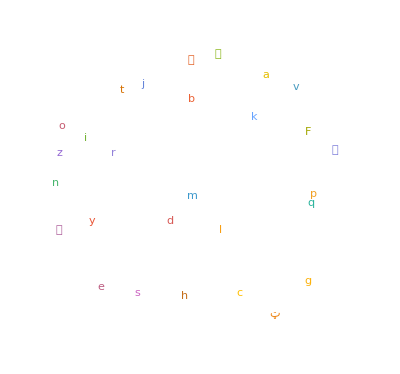

```mathematica
WordCloud[StringTake[translatedList, 1]]
```

```mathematica
ResourceFunction["WordSyllables"][WordTranslation["fish", "Mandarin"][[1]]]
```

{wrong,in,put}

```mathematica
audioSpanish=AudioTrim[SpeechSynthesize[WordTranslation["fish", "Spanish"][[2]]]]
```

```mathematica
audioFrench = AudioTrim[SpeechSynthesize[WordTranslation["fish", "French"][[1]]]]
```

```mathematica
audioEnglish=AudioTrim[SpeechSynthesize[WordTranslation["fish", "English"][[1]]]]
```

```mathematica
audioGerman =AudioTrim[SpeechSynthesize[WordTranslation["fish", "German"][[1]]]]
```

```mathematica
enc=NetEncoder[{"AudioSpectrogram"}]
```

NetEncoder[…]

```mathematica
generateSpectrogram[a_]:=ColorNegate[ImageReflect[Image[Normal[Spectrogram[a][[1,1]]]]]]
```

```mathematica
ss = enc[audioSpanish]
```

```mathematica
ss2=generateSpectrogram[audioSpanish]
```

-Graphics-

```mathematica
ss3=ShortTimeFourier[audioSpanish,Automatic,Automatic,HannWindow]
```

ShortTimeFourierData[…]

```mathematica
Spectrogram[ss3]
```

-Graphics-

```mathematica
Audio[InverseShortTimeFourier[ss3]]
```

```mathematica
sf = enc[audioFrench]
```

```mathematica
sf2=generateSpectrogram[audioFrench]
```

-Graphics-

```mathematica
sf3=ShortTimeFourier[audioFrench,Automatic,Automatic,HannWindow]
```

ShortTimeFourierData[…]

```mathematica
Print[Values[Normal[sf3][[1]]]]
```

{{{0.165775+0. ⅈ,-0.0308132+0.0010372 ⅈ,-0.0791791-0.0469796 ⅈ,0.0243436+0.0167721 ⅈ,0.00139587+0.012137 ⅈ,0.00168231-0.00633013 ⅈ,-0.000446419+0.00444591 ⅈ,-0.00149654-0.00165744 ⅈ,0.00165592+0.0011099 ⅈ,-0.000558429+0.0000518965 ⅈ,0.000613317-0.0000187234 ⅈ,-0.000364688-0.0000750207 ⅈ,0.000333885-0.0000769446 ⅈ,-0.000320852+0.000323404 ⅈ,0.000543455-0.000328147 ⅈ,-0.000613596+0.000254707 ⅈ,0.000374842-0.000157195 ⅈ,0.0000336359+0.000353836 ⅈ,-0.000121542-0.000467955 ⅈ,0.000320337+0.000267621 ⅈ,-0.000559353-0.000314975 ⅈ,0.000500477+0.000420552 ⅈ,-0.000569347+0.000148295 ⅈ,0.000687502-0.000593095 ⅈ,-0.000397506+0.000301139 ⅈ,0.0000982805-0.000175112 ⅈ,-0.000164621+0.000323814 ⅈ,0.0000245677-0.000148902 ⅈ,0.000457061-0.000178829 ⅈ,-0.000444343+0.000188742 ⅈ,0.000125268-0.000158208 ⅈ,-0.0000594972+0.000309717 ⅈ,-0.0000714267-0.000547949 ⅈ,-4.83371×10^-6+0.000780987 ⅈ,0.000058144-0.00018287 ⅈ,0.000180286-0.000675941 ⅈ,-0.000123232+0.00104613 ⅈ,0.000204643-0.00123424 ⅈ,-0.000257853+0.00105784 ⅈ,-0.00014484-0.000717486 ⅈ,0.000228085+0.000617348 ⅈ,-0.000339089-0.000705295 ⅈ,0.000842455+0.000688651 ⅈ,-0.000973731-0.0000249061 ⅈ,0.000561019-0.00077356 ⅈ,0.000160105+0.000806374 ⅈ,-0.000542508-0.000309671 ⅈ,0.000686408-0.000286199 ⅈ,-0.000836203+0.000190172 ⅈ,0.000317311+0.000477488 ⅈ,0.000067267-0.000323365 ⅈ,0.000125938-0.000324654 ⅈ,-0.000168834+0.000845422 ⅈ,0.00019875-0.000789427 ⅈ,-0.000174121+0.000454464 ⅈ,0.000382243-0.00102794 ⅈ,-0.0000727536+0.00140512 ⅈ,-0.0006784-0.001029 ⅈ,0.000767507+0.000656779 ⅈ,-0.000999828-0.00013489 ⅈ,0.00086618-0.000607209 ⅈ,-0.000170899+0.00075002 ⅈ,0.0000121436-0.000276503 ⅈ,-0.000156366-0.000103633 ⅈ,-0.000127546+0.0000962932 ⅈ,0.000283458-0.000224372 ⅈ,0.000161186+0.000561556 ⅈ,-0.000493591-0.000214027 ⅈ,0.000497586+0.0000862128 ⅈ,-0.0000785878-0.000148972 ⅈ,0.000114433+0.000130063 ⅈ,-0.000753537-0.000568182 ⅈ,0.000716794+0.00041597 ⅈ,-0.000539038+0.000103864 ⅈ,0.000291257-0.000187682 ⅈ,0.000506378-0.00030652 ⅈ,-0.00149551+0.000287297 ⅈ,0.00169178+0.000576195 ⅈ,-0.00109882-0.000875238 ⅈ,0.000472887+0.000481038 ⅈ,8.74465×10^-6-0.000105712 ⅈ,-0.0000415007+0.000410684 ⅈ,-0.000171684-0.000341467 ⅈ,0.000838479-0.00038719 ⅈ,-0.00144722+0.000681921 ⅈ,0.00113127-0.000597173 ⅈ,-0.000364248+0.000125799 ⅈ,0.0000800569+0.000515336 ⅈ,-0.000542576-0.000516481 ⅈ,0.00100517+0.000409862 ⅈ,-0.000656933-0.000596456 ⅈ,-0.0000858578+0.000777306 ⅈ,0.000350441-0.000750396 ⅈ,0.000115062+0.000193117 ⅈ,-0.000637467+0.000149213 ⅈ,0.000735833-0.000333617 ⅈ,-0.000408226+0.00025782 ⅈ,-0.000493611-0.000213523 ⅈ,0.000467991+0.00109087 ⅈ,0.000334654-0.00135583 ⅈ,-0.000132856+0.000624471 ⅈ,-0.000530583-0.0000965411 ⅈ,0.000351776+0.00014899 ⅈ,-0.0000909382-0.000127968 ⅈ,0.000665257-0.000545168 ⅈ,-0.00104666+0.00095294 ⅈ,0.00164036-0.000423647 ⅈ,-0.000944541-0.000579058 ⅈ,-0.000868842+0.000737395 ⅈ,0.000481134-0.000643928 ⅈ,0.000126818+0.00112817 ⅈ,-0.0000218304-0.00109639 ⅈ,0.00103149+0.0000954107 ⅈ,-0.0019597+0.000708727 ⅈ,0.00106465-0.00054868 ⅈ,-0.0000331148+0.000455845 ⅈ,0.0000521749-0.00051084 ⅈ,0.0000879295+0.000283614 ⅈ,-0.000269768+7.08223×10^-6 ⅈ,0.0000956129-0.000160237 ⅈ,0.0000524203+0.000188708 ⅈ,-0.0000800374-0.000135859 ⅈ,0.0000785945+6.92318×10^-7 ⅈ,-0.0000884907+0.0000549299 ⅈ,0.000109876+0.0000532194 ⅈ,-0.0000990886-0.000102131 ⅈ,0.00012706-0.0000290668 ⅈ,-0.0000984496+0.0000994757 ⅈ,0.0000393487+0. ⅈ,-0.0000984496-0.0000994757 ⅈ,0.00012706+0.0000290668 ⅈ,-0.0000990886+0.000102131 ⅈ,0.000109876-0.0000532194 ⅈ,-0.0000884907-0.0000549299 ⅈ,0.0000785945-6.92318×10^-7 ⅈ,-0.0000800374+0.000135859 ⅈ,0.0000524203-0.000188708 ⅈ,0.0000956129+0.000160237 ⅈ,-0.000269768-7.08223×10^-6 ⅈ,0.0000879295-0.000283614 ⅈ,0.0000521749+0.00051084 ⅈ,-0.0000331148-0.000455845 ⅈ,0.00106465+0.00054868 ⅈ,-0.0019597-0.000708727 ⅈ,0.00103149-0.0000954107 ⅈ,-0.0000218304+0.00109639 ⅈ,0.000126818-0.00112817 ⅈ,0.000481134+0.000643928 ⅈ,-0.000868842-0.000737395 ⅈ,-0.000944541+0.000579058 ⅈ,0.00164036+0.000423647 ⅈ,-0.00104666-0.00095294 ⅈ,0.000665257+0.000545168 ⅈ,-0.0000909382+0.000127968 ⅈ,0.000351776-0.00014899 ⅈ,-0.000530583+0.0000965411 ⅈ,-0.000132856-0.000624471 ⅈ,0.000334654+0.00135583 ⅈ,0.000467991-0.00109087 ⅈ,-0.000493611+0.000213523 ⅈ,-0.000408226-0.00025782 ⅈ,0.000735833+0.000333617 ⅈ,-0.000637467-0.000149213 ⅈ,0.000115062-0.000193117 ⅈ,0.000350441+0.000750396 ⅈ,-0.0000858578-0.000777306 ⅈ,-0.000656933+0.000596456 ⅈ,0.00100517-0.000409862 ⅈ,-0.000542576+0.000516481 ⅈ,0.0000800569-0.000515336 ⅈ,-0.000364248-0.000125799 ⅈ,0.00113127+0.000597173 ⅈ,-0.00144722-0.000681921 ⅈ,0.000838479+0.00038719 ⅈ,-0.000171684+0.000341467 ⅈ,-0.0000415007-0.000410684 ⅈ,8.74465×10^-6+0.000105712 ⅈ,0.000472887-0.000481038 ⅈ,-0.00109882+0.000875238 ⅈ,0.00169178-0.000576195 ⅈ,-0.00149551-0.000287297 ⅈ,0.000506378+0.00030652 ⅈ,0.000291257+0.000187682 ⅈ,-0.000539038-0.000103864 ⅈ,0.000716794-0.00041597 ⅈ,-0.000753537+0.000568182 ⅈ,0.000114433-0.000130063 ⅈ,-0.0000785878+0.000148972 ⅈ,0.000497586-0.0000862128 ⅈ,-0.000493591+0.000214027 ⅈ,0.000161186-0.000561556 ⅈ,0.000283458+0.000224372 ⅈ,-0.000127546-0.0000962932 ⅈ,-0.000156366+0.000103633 ⅈ,0.0000121436+0.000276503 ⅈ,-0.000170899-0.00075002 ⅈ,0.00086618+0.000607209 ⅈ,-0.000999828+0.00013489 ⅈ,0.000767507-0.000656779 ⅈ,-0.0006784+0.001029 ⅈ,-0.0000727536-0.00140512 ⅈ,0.000382243+0.00102794 ⅈ,-0.000174121-0.000454464 ⅈ,0.00019875+0.000789427 ⅈ,-0.000168834-0.000845422 ⅈ,0.000125938+0.000324654 ⅈ,0.000067267+0.000323365 ⅈ,0.000317311-0.000477488 ⅈ,-0.000836203-0.000190172 ⅈ,0.000686408+0.000286199 ⅈ,-0.000542508+0.000309671 ⅈ,0.000160105-0.000806374 ⅈ,0.000561019+0.00077356 ⅈ,-0.000973731+0.0000249061 ⅈ,0.000842455-0.000688651 ⅈ,-0.000339089+0.000705295 ⅈ,0.000228085-0.000617348 ⅈ,-0.00014484+0.000717486 ⅈ,-0.000257853-0.00105784 ⅈ,0.000204643+0.00123424 ⅈ,-0.000123232-0.00104613 ⅈ,0.000180286+0.000675941 ⅈ,0.000058144+0.00018287 ⅈ,-4.83371×10^-6-0.000780987 ⅈ,-0.0000714267+0.000547949 ⅈ,-0.0000594972-0.000309717 ⅈ,0.000125268+0.000158208 ⅈ,-0.000444343-0.000188742 ⅈ,0.000457061+0.000178829 ⅈ,0.0000245677+0.000148902 ⅈ,-0.000164621-0.000323814 ⅈ,0.0000982805+0.000175112 ⅈ,-0.000397506-0.000301139 ⅈ,0.000687502+0.000593095 ⅈ,-0.000569347-0.000148295 ⅈ,0.000500477-0.000420552 ⅈ,-0.000559353+0.000314975 ⅈ,0.000320337-0.000267621 ⅈ,-0.000121542+0.000467955 ⅈ,0.0000336359-0.000353836 ⅈ,0.000374842+0.000157195 ⅈ,-0.000613596-0.000254707 ⅈ,0.000543455+0.000328147 ⅈ,-0.000320852-0.000323404 ⅈ,0.000333885+0.0000769446 ⅈ,-0.000364688+0.0000750207 ⅈ,0.000613317+0.0000187234 ⅈ,-0.000558429-0.0000518965 ⅈ,0.00165592-0.0011099 ⅈ,-0.00149654+0.00165744 ⅈ,-0.000446419-0.00444591 ⅈ,0.00168231+0.00633013 ⅈ,0.00139587-0.012137 ⅈ,0.0243436-0.0167721 ⅈ,-0.0791791+0.0469796 ⅈ,-0.0308132-0.0010372 ⅈ},{0.107021+0. ⅈ,-0.0752013-0.0760855 ⅈ,0.0287423+0.0819972 ⅈ,0.000337365-0.0305841 ⅈ,-0.00684763+0.00220695 ⅈ,-0.0024855-0.00107846 ⅈ,0.00134901+0.00147832 ⅈ,0.00180452-0.00100634 ⅈ,-0.00101296-0.000231089 ⅈ,-0.000472438+0.000173013 ⅈ,0.0000982983-0.000123296 ⅈ,0.0000721499+0.0000850379 ⅈ,0.000305028-0.0000370289 ⅈ,-0.000124637+0.000021419 ⅈ,-0.000189264-0.000211886 ⅈ,-0.000118881+0.0000131811 ⅈ,0.000225995+0.00017346 ⅈ,0.000283272+0.0000640703 ⅈ,-0.000305723-0.0000871777 ⅈ,-0.000318698-0.000204509 ⅈ,0.000358578+0.0000957452 ⅈ,0.0000543452+0.000474472 ⅈ,0.000198372-0.000608206 ⅈ,-0.000508576+0.000105378 ⅈ,0.000160143+0.00013868 ⅈ,-0.0000207746+2.32574×10^-7 ⅈ,0.000166669-0.0000413175 ⅈ,0.0000646089-0.000263403 ⅈ,-0.000275478+0.000559902 ⅈ,0.000157938-0.000252562 ⅈ,4.6633×10^-6-0.0000907497 ⅈ,0.0000956305-0.000227315 ⅈ,-0.000106004+0.00034021 ⅈ,-0.00026734+0.000246328 ⅈ,0.000486782-0.000566559 ⅈ,-0.000403892+0.0000910838 ⅈ,-0.000075218+0.000361948 ⅈ,0.000290295+0.0000379309 ⅈ,0.000349473-0.0000806913 ⅈ,-0.000676456-0.000409181 ⅈ,0.000346676-0.000176107 ⅈ,-0.000238639+0.000486381 ⅈ,0.000412855+0.000512705 ⅈ,0.0000850437-0.000968746 ⅈ,-0.000760553+0.000291506 ⅈ,0.00049192+0.000502852 ⅈ,0.00017915-0.000589079 ⅈ,-0.000108699-0.0000235378 ⅈ,-0.000250786+0.000511389 ⅈ,-0.000028911-0.000517795 ⅈ,0.000183762+0.000339358 ⅈ,0.000284679-0.0000728156 ⅈ,-0.000367085-0.000235793 ⅈ,-0.000195312+0.000418895 ⅈ,-0.0000595803-0.00039655 ⅈ,0.0000822633+0.000583217 ⅈ,0.00108516-0.00091034 ⅈ,-0.00091198+0.000439407 ⅈ,-0.000254977+0.0000140042 ⅈ,0.000159785+0.00077414 ⅈ,0.000455537-0.00139664 ⅈ,-0.000308144+0.000618415 ⅈ,0.000122911+0.000209119 ⅈ,-0.000198035-0.000135967 ⅈ,0.000122617+0.000100792 ⅈ,-0.00037618-0.000596009 ⅈ,0.000721678+0.000924698 ⅈ,-0.000389948-0.000556692 ⅈ,0.000181676+0.0000735737 ⅈ,-0.000394332+0.000393255 ⅈ,-0.000131207-0.000908645 ⅈ,0.000254537+0.000790594 ⅈ,0.000450618-0.000371854 ⅈ,0.0000639751+0.000188764 ⅈ,-0.0010029+0.000330796 ⅈ,0.000864678-0.000522955 ⅈ,0.0000600093+0.000338283 ⅈ,-0.000639783-0.000610878 ⅈ,0.000292667-0.0000354256 ⅈ,-0.0000819147+0.000921665 ⅈ,-0.000132454-0.000931881 ⅈ,0.000469709+0.00062323 ⅈ,0.000096257-0.0000319112 ⅈ,-0.000427156-0.000559273 ⅈ,-0.000286377+0.000683648 ⅈ,0.000255666+0.000213855 ⅈ,-0.0000328375-0.00103758 ⅈ,0.00033615+0.000878807 ⅈ,0.00023359-0.000273562 ⅈ,-0.000449953-0.0000927793 ⅈ,-0.000329421+0.0000717857 ⅈ,0.00041587-0.000648121 ⅈ,0.0000224078+0.000842583 ⅈ,0.000130609+0.000162321 ⅈ,-0.000213384-0.000440287 ⅈ,-0.00034346-0.000132162 ⅈ,0.000261545+0.000401177 ⅈ,0.000264791-0.000355226 ⅈ,0.000228087+0.000427025 ⅈ,-0.000673493-0.000479589 ⅈ,-0.000180826-0.000129057 ⅈ,0.000819945+0.000401604 ⅈ,-0.0002803-0.000120089 ⅈ,0.000367228+0.000415112 ⅈ,-0.00136455-0.000645578 ⅈ,0.000821432+0.0000172958 ⅈ,-0.000253839+0.000384431 ⅈ,0.0010259-0.000795251 ⅈ,-0.000679143+0.00119087 ⅈ,0.000418113+0.0000287262 ⅈ,-0.000443348-0.000244453 ⅈ,-0.000459323-0.000929565 ⅈ,-0.00024121+0.000952841 ⅈ,0.00150356-0.000298964 ⅈ,-0.00073798-0.000364713 ⅈ,-0.0000353335+0.000301601 ⅈ,-0.000204012+0.00012039 ⅈ,0.000345956+0.0000275075 ⅈ,-0.00024371-0.000299256 ⅈ,0.0000826139+0.000181093 ⅈ,0.0000540661+0.0000801266 ⅈ,0.0000111002-0.000097343 ⅈ,-0.000129357+0.0000241047 ⅈ,0.0000462886-0.0000406441 ⅈ,0.0000199962-2.8052×10^-6 ⅈ,0.000016901+0.000119501 ⅈ,0.0000658765-0.000122228 ⅈ,-0.000135724+0.0000487588 ⅈ,0.000109796+0. ⅈ,-0.000135724-0.0000487588 ⅈ,0.0000658765+0.000122228 ⅈ,0.000016901-0.000119501 ⅈ,0.0000199962+2.8052×10^-6 ⅈ,0.0000462886+0.0000406441 ⅈ,-0.000129357-0.0000241047 ⅈ,0.0000111002+0.000097343 ⅈ,0.0000540661-0.0000801266 ⅈ,0.0000826139-0.000181093 ⅈ,-0.00024371+0.000299256 ⅈ,0.000345956-0.0000275075 ⅈ,-0.000204012-0.00012039 ⅈ,-0.0000353335-0.000301601 ⅈ,-0.00073798+0.000364713 ⅈ,0.00150356+0.000298964 ⅈ,-0.00024121-0.000952841 ⅈ,-0.000459323+0.000929565 ⅈ,-0.000443348+0.000244453 ⅈ,0.000418113-0.0000287262 ⅈ,-0.000679143-0.00119087 ⅈ,0.0010259+0.000795251 ⅈ,-0.000253839-0.000384431 ⅈ,0.000821432-0.0000172958 ⅈ,-0.00136455+0.000645578 ⅈ,0.000367228-0.000415112 ⅈ,-0.0002803+0.000120089 ⅈ,0.000819945-0.000401604 ⅈ,-0.000180826+0.000129057 ⅈ,-0.000673493+0.000479589 ⅈ,0.000228087-0.000427025 ⅈ,0.000264791+0.000355226 ⅈ,0.000261545-0.000401177 ⅈ,-0.00034346+0.000132162 ⅈ,-0.000213384+0.000440287 ⅈ,0.000130609-0.000162321 ⅈ,0.0000224078-0.000842583 ⅈ,0.00041587+0.000648121 ⅈ,-0.000329421-0.0000717857 ⅈ,-0.000449953+0.0000927793 ⅈ,0.00023359+0.000273562 ⅈ,0.00033615-0.000878807 ⅈ,-0.0000328375+0.00103758 ⅈ,0.000255666-0.000213855 ⅈ,-0.000286377-0.000683648 ⅈ,-0.000427156+0.000559273 ⅈ,0.000096257+0.0000319112 ⅈ,0.000469709-0.00062323 ⅈ,-0.000132454+0.000931881 ⅈ,-0.0000819147-0.000921665 ⅈ,0.000292667+0.0000354256 ⅈ,-0.000639783+0.000610878 ⅈ,0.0000600093-0.000338283 ⅈ,0.000864678+0.000522955 ⅈ,-0.0010029-0.000330796 ⅈ,0.0000639751-0.000188764 ⅈ,0.000450618+0.000371854 ⅈ,0.000254537-0.000790594 ⅈ,-0.000131207+0.000908645 ⅈ,-0.000394332-0.000393255 ⅈ,0.000181676-0.0000735737 ⅈ,-0.000389948+0.000556692 ⅈ,0.000721678-0.000924698 ⅈ,-0.00037618+0.000596009 ⅈ,0.000122617-0.000100792 ⅈ,-0.000198035+0.000135967 ⅈ,0.000122911-0.000209119 ⅈ,-0.000308144-0.000618415 ⅈ,0.000455537+0.00139664 ⅈ,0.000159785-0.00077414 ⅈ,-0.000254977-0.0000140042 ⅈ,-0.00091198-0.000439407 ⅈ,0.00108516+0.00091034 ⅈ,0.0000822633-0.000583217 ⅈ,-0.0000595803+0.00039655 ⅈ,-0.000195312-0.000418895 ⅈ,-0.000367085+0.000235793 ⅈ,0.000284679+0.0000728156 ⅈ,0.000183762-0.000339358 ⅈ,-0.000028911+0.000517795 ⅈ,-0.000250786-0.000511389 ⅈ,-0.000108699+0.0000235378 ⅈ,0.00017915+0.000589079 ⅈ,0.00049192-0.000502852 ⅈ,-0.000760553-0.000291506 ⅈ,0.0000850437+0.000968746 ⅈ,0.000412855-0.000512705 ⅈ,-0.000238639-0.000486381 ⅈ,0.000346676+0.000176107 ⅈ,-0.000676456+0.000409181 ⅈ,0.000349473+0.0000806913 ⅈ,0.000290295-0.0000379309 ⅈ,-0.000075218-0.000361948 ⅈ,-0.000403892-0.0000910838 ⅈ,0.000486782+0.000566559 ⅈ,-0.00026734-0.000246328 ⅈ,-0.000106004-0.00034021 ⅈ,0.0000956305+0.000227315 ⅈ,4.6633×10^-6+0.0000907497 ⅈ,0.000157938+0.000252562 ⅈ,-0.000275478-0.000559902 ⅈ,0.0000646089+0.000263403 ⅈ,0.000166669+0.0000413175 ⅈ,-0.0000207746-2.32574×10^-7 ⅈ,0.000160143-0.00013868 ⅈ,-0.000508576-0.000105378 ⅈ,0.000198372+0.000608206 ⅈ,0.0000543452-0.000474472 ⅈ,0.000358578-0.0000957452 ⅈ,-0.000318698+0.000204509 ⅈ,-0.000305723+0.0000871777 ⅈ,0.000283272-0.0000640703 ⅈ,0.000225995-0.00017346 ⅈ,-0.000118881-0.0000131811 ⅈ,-0.000189264+0.000211886 ⅈ,-0.000124637-0.000021419 ⅈ,0.000305028+0.0000370289 ⅈ,0.0000721499-0.0000850379 ⅈ,0.0000982983+0.000123296 ⅈ,-0.000472438-0.000173013 ⅈ,-0.00101296+0.000231089 ⅈ,0.00180452+0.00100634 ⅈ,0.00134901-0.00147832 ⅈ,-0.0024855+0.00107846 ⅈ,-0.00684763-0.00220695 ⅈ,0.000337365+0.0305841 ⅈ,0.0287423-0.0819972 ⅈ,-0.0752013+0.0760855 ⅈ},{0.0659741+0. ⅈ,-0.0232514+0.0576101 ⅈ,-0.0105198-0.070236 ⅈ,0.00541514+0.0189757 ⅈ,-0.00578011+0.00182479 ⅈ,0.000455019+0.00257104 ⅈ,0.00103212-0.00096595 ⅈ,-0.000953743+0.00129835 ⅈ,0.000864399-0.000680988 ⅈ,-0.000456545+0.000257143 ⅈ,0.000385023+0.000158326 ⅈ,-0.000341035-0.0000414562 ⅈ,0.000272577+0.000100471 ⅈ,-0.000120116-0.000203839 ⅈ,-0.0000101001+0.000281922 ⅈ,0.000191624-0.000191793 ⅈ,-0.000342323+0.000379942 ⅈ,0.00030823-0.000428726 ⅈ,-0.000411842+0.00021944 ⅈ,0.00058943-1.93365×10^-7 ⅈ,-0.000366086-0.000185501 ⅈ,-0.0000942304+0.000382932 ⅈ,0.0000852545-0.000292274 ⅈ,0.000148502+0.000195031 ⅈ,-0.0000902052-0.00012437 ⅈ,0.000103544+0.000114342 ⅈ,-0.000266049-0.000119613 ⅈ,0.000380769+0.0000849459 ⅈ,-0.000230951-0.000306193 ⅈ,0.0000823985+0.000466661 ⅈ,-0.000132401-0.000222958 ⅈ,-0.000109082+0.00014871 ⅈ,0.000479339-0.000263648 ⅈ,-0.000642552+0.000154373 ⅈ,0.000378882+0.000097484 ⅈ,-0.0000758639-0.000177086 ⅈ,0.0000633655-0.0000747172 ⅈ,0.000230225+0.000250791 ⅈ,-0.000221143+0.000143634 ⅈ,-0.000291255-0.000747483 ⅈ,0.000344642+0.000997985 ⅈ,-0.00020566-0.000773997 ⅈ,0.0000275916+0.000500149 ⅈ,-0.0000112501-0.000319882 ⅈ,0.000229792+9.5855×10^-6 ⅈ,3.89928×10^-6+0.000166082 ⅈ,-0.0000903482+0.000154439 ⅈ,-0.0000180275-0.000399195 ⅈ,-0.000365056+0.000375938 ⅈ,0.000519715-0.000229894 ⅈ,-0.000201911-0.0000717204 ⅈ,0.0000143719+0.000228779 ⅈ,0.0000708008-0.000354715 ⅈ,0.000186703+0.000660461 ⅈ,-0.00042829-0.000783957 ⅈ,0.00052209+0.000663548 ⅈ,-0.00102508-0.000913327 ⅈ,0.000928296+0.000741891 ⅈ,-0.000143782-0.0000201665 ⅈ,-0.0000609276+0.00036907 ⅈ,0.000122791-0.00103796 ⅈ,-0.000386322+0.000770502 ⅈ,0.000359472-0.000409801 ⅈ,-0.000270388+0.00024669 ⅈ,0.000257385-0.000271573 ⅈ,-0.000467238+0.000386894 ⅈ,0.000453064+0.000217305 ⅈ,-0.000188078-0.000720922 ⅈ,0.000498065+0.00021667 ⅈ,-0.00109971+0.000402362 ⅈ,0.00119901-0.000234945 ⅈ,-0.000773511-0.0000982353 ⅈ,0.00060715-0.0000256146 ⅈ,-0.000999555-0.000138114 ⅈ,0.00124703+0.000560152 ⅈ,-0.000570523-0.000473096 ⅈ,-0.0000918118-0.00014545 ⅈ,-0.0000489964+0.000870017 ⅈ,0.000277066-0.000847089 ⅈ,-0.000366149-3.61222×10^-7 ⅈ,-0.00018303+0.000211719 ⅈ,0.00108189+0.000140708 ⅈ,-0.00109074+0.0000221991 ⅈ,0.000401411-0.00027837 ⅈ,-0.000147513+0.000269764 ⅈ,0.000552489-0.000592363 ⅈ,-0.000835687+0.000956973 ⅈ,0.000636553-0.000446991 ⅈ,-0.000432075-0.0000807212 ⅈ,0.000536308+0.000166304 ⅈ,-0.00078187-0.000321773 ⅈ,0.000738698+0.000717133 ⅈ,-0.0003393-0.0010319 ⅈ,4.43822×10^-7+0.000928277 ⅈ,0.0000734275-0.000964879 ⅈ,0.000186992+0.00088708 ⅈ,-0.000331987-0.000370987 ⅈ,0.000231689+0.000237579 ⅈ,0.000210562-0.000306086 ⅈ,-0.000937146+0.000100184 ⅈ,0.00122574-8.29811×10^-6 ⅈ,-0.000741109-0.000177113 ⅈ,0.000280813+0.000593358 ⅈ,-0.000975554-0.000876901 ⅈ,0.00119751+0.00112509 ⅈ,-0.000249915-0.0012052 ⅈ,0.000206327+0.000965073 ⅈ,-0.00127742-0.00145494 ⅈ,0.00202917+0.00190644 ⅈ,-0.00226698-0.00113956 ⅈ,0.00252367+0.000114545 ⅈ,-0.0016029+0.000378898 ⅈ,0.000664661-0.0000253206 ⅈ,-0.00115797-0.000317027 ⅈ,0.0010573-0.000168435 ⅈ,-0.00030401+0.000687044 ⅈ,-0.00017012-0.000296807 ⅈ,0.000161352-0.000210225 ⅈ,0.00022597+0.000139076 ⅈ,-0.000365883-0.0000392612 ⅈ,0.000215092-6.44863×10^-6 ⅈ,-0.0000739731+0.0000118734 ⅈ,0.0000924281+0.0000573512 ⅈ,-0.0000995119-0.0000787986 ⅈ,0.0000293776+0.0000986253 ⅈ,0.0000148951-0.000124871 ⅈ,0.0000353498+0.000106329 ⅈ,-0.000110849-0.0000922302 ⅈ,0.000126182+0. ⅈ,-0.000110849+0.0000922302 ⅈ,0.0000353498-0.000106329 ⅈ,0.0000148951+0.000124871 ⅈ,0.0000293776-0.0000986253 ⅈ,-0.0000995119+0.0000787986 ⅈ,0.0000924281-0.0000573512 ⅈ,-0.0000739731-0.0000118734 ⅈ,0.000215092+6.44863×10^-6 ⅈ,-0.000365883+0.0000392612 ⅈ,0.00022597-0.000139076 ⅈ,0.000161352+0.000210225 ⅈ,-0.00017012+0.000296807 ⅈ,-0.00030401-0.000687044 ⅈ,0.0010573+0.000168435 ⅈ,-0.00115797+0.000317027 ⅈ,0.000664661+0.0000253206 ⅈ,-0.0016029-0.000378898 ⅈ,0.00252367-0.000114545 ⅈ,-0.00226698+0.00113956 ⅈ,0.00202917-0.00190644 ⅈ,-0.00127742+0.00145494 ⅈ,0.000206327-0.000965073 ⅈ,-0.000249915+0.0012052 ⅈ,0.00119751-0.00112509 ⅈ,-0.000975554+0.000876901 ⅈ,0.000280813-0.000593358 ⅈ,-0.000741109+0.000177113 ⅈ,0.00122574+8.29811×10^-6 ⅈ,-0.000937146-0.000100184 ⅈ,0.000210562+0.000306086 ⅈ,0.000231689-0.000237579 ⅈ,-0.000331987+0.000370987 ⅈ,0.000186992-0.00088708 ⅈ,0.0000734275+0.000964879 ⅈ,4.43822×10^-7-0.000928277 ⅈ,-0.0003393+0.0010319 ⅈ,0.000738698-0.000717133 ⅈ,-0.00078187+0.000321773 ⅈ,0.000536308-0.000166304 ⅈ,-0.000432075+0.0000807212 ⅈ,0.000636553+0.000446991 ⅈ,-0.000835687-0.000956973 ⅈ,0.000552489+0.000592363 ⅈ,-0.000147513-0.000269764 ⅈ,0.000401411+0.00027837 ⅈ,-0.00109074-0.0000221991 ⅈ,0.00108189-0.000140708 ⅈ,-0.00018303-0.000211719 ⅈ,-0.000366149+3.61222×10^-7 ⅈ,0.000277066+0.000847089 ⅈ,-0.0000489964-0.000870017 ⅈ,-0.0000918118+0.00014545 ⅈ,-0.000570523+0.000473096 ⅈ,0.00124703-0.000560152 ⅈ,-0.000999555+0.000138114 ⅈ,0.00060715+0.0000256146 ⅈ,-0.000773511+0.0000982353 ⅈ,0.00119901+0.000234945 ⅈ,-0.00109971-0.000402362 ⅈ,0.000498065-0.00021667 ⅈ,-0.000188078+0.000720922 ⅈ,0.000453064-0.000217305 ⅈ,-0.000467238-0.000386894 ⅈ,0.000257385+0.000271573 ⅈ,-0.000270388-0.00024669 ⅈ,0.000359472+0.000409801 ⅈ,-0.000386322-0.000770502 ⅈ,0.000122791+0.00103796 ⅈ,-0.0000609276-0.00036907 ⅈ,-0.000143782+0.0000201665 ⅈ,0.000928296-0.000741891 ⅈ,-0.00102508+0.000913327 ⅈ,0.00052209-0.000663548 ⅈ,-0.00042829+0.000783957 ⅈ,0.000186703-0.000660461 ⅈ,0.0000708008+0.000354715 ⅈ,0.0000143719-0.000228779 ⅈ,-0.000201911+0.0000717204 ⅈ,0.000519715+0.000229894 ⅈ,-0.000365056-0.000375938 ⅈ,-0.0000180275+0.000399195 ⅈ,-0.0000903482-0.000154439 ⅈ,3.89928×10^-6-0.000166082 ⅈ,0.000229792-9.5855×10^-6 ⅈ,-0.0000112501+0.000319882 ⅈ,0.0000275916-0.000500149 ⅈ,-0.00020566+0.000773997 ⅈ,0.000344642-0.000997985 ⅈ,-0.000291255+0.000747483 ⅈ,-0.000221143-0.000143634 ⅈ,0.000230225-0.000250791 ⅈ,0.0000633655+0.0000747172 ⅈ,-0.0000758639+0.000177086 ⅈ,0.000378882-0.000097484 ⅈ,-0.000642552-0.000154373 ⅈ,0.000479339+0.000263648 ⅈ,-0.000109082-0.00014871 ⅈ,-0.000132401+0.000222958 ⅈ,0.0000823985-0.000466661 ⅈ,-0.000230951+0.000306193 ⅈ,0.000380769-0.0000849459 ⅈ,-0.000266049+0.000119613 ⅈ,0.000103544-0.000114342 ⅈ,-0.0000902052+0.00012437 ⅈ,0.000148502-0.000195031 ⅈ,0.0000852545+0.000292274 ⅈ,-0.0000942304-0.000382932 ⅈ,-0.000366086+0.000185501 ⅈ,0.00058943+1.93365×10^-7 ⅈ,-0.000411842-0.00021944 ⅈ,0.00030823+0.000428726 ⅈ,-0.000342323-0.000379942 ⅈ,0.000191624+0.000191793 ⅈ,-0.0000101001-0.000281922 ⅈ,-0.000120116+0.000203839 ⅈ,0.000272577-0.000100471 ⅈ,-0.000341035+0.0000414562 ⅈ,0.000385023-0.000158326 ⅈ,-0.000456545-0.000257143 ⅈ,0.000864399+0.000680988 ⅈ,-0.000953743-0.00129835 ⅈ,0.00103212+0.00096595 ⅈ,0.000455019-0.00257104 ⅈ,-0.00578011-0.00182479 ⅈ,0.00541514-0.0189757 ⅈ,-0.0105198+0.070236 ⅈ,-0.0232514-0.0576101 ⅈ},{0.077919+0. ⅈ,-0.0362965-0.0496968 ⅈ,-0.0132628+0.0557282 ⅈ,0.0122429-0.0144805 ⅈ,-0.00228008-0.00419306 ⅈ,0.00130437+0.00110437 ⅈ,-0.00098714-0.000132166 ⅈ,0.000273701-0.00145288 ⅈ,0.000106045+0.000748595 ⅈ,-0.000163659+0.000163081 ⅈ,-0.000150811-0.000280085 ⅈ,0.000309805+0.000148177 ⅈ,-0.0000639128+0.0000315798 ⅈ,-0.0000942641-0.0000896174 ⅈ,0.00025638-0.0000825647 ⅈ,-0.000165739+0.000395457 ⅈ,-0.000109639-0.00071129 ⅈ,0.000215951+0.000181662 ⅈ,0.0000356351+0.000220186 ⅈ,-0.000443196+0.000130371 ⅈ,0.000342013-0.000349811 ⅈ,-0.0000879018+0.000214604 ⅈ,0.000103542+0.00010296 ⅈ,-0.0000315547-0.000285612 ⅈ,0.0000562518+0.000154254 ⅈ,-0.00020412-0.0000785048 ⅈ,0.000028672+0.0000353495 ⅈ,0.00029487+0.0000789352 ⅈ,-0.000367112+0.000141838 ⅈ,0.000298586-0.0003927 ⅈ,-0.000212013+0.0000931824 ⅈ,0.000378852+0.0000627431 ⅈ,-0.000334047+5.45802×10^-6 ⅈ,-0.0000887508-0.000136353 ⅈ,0.00033919+0.00034102 ⅈ,-0.000556666-4.74187×10^-6 ⅈ,0.00049494-0.000429052 ⅈ,-0.0002903+0.000111071 ⅈ,0.000631487+0.000556371 ⅈ,-0.000680508-0.000524894 ⅈ,0.0000454954-0.000315371 ⅈ,0.000143251+0.000726162 ⅈ,-0.000352893-0.000284864 ⅈ,0.000557685-0.000200533 ⅈ,0.0000403295-0.0000592111 ⅈ,-0.000127377+0.000915138 ⅈ,-0.000633578-0.00104503 ⅈ,0.000751936+0.000118487 ⅈ,-0.000306021+0.000264608 ⅈ,0.0000680976+0.000132414 ⅈ,-0.0000260967-0.000320545 ⅈ,0.000187355+0.000270493 ⅈ,-0.000439046+0.000199767 ⅈ,0.000631728-0.000678791 ⅈ,-0.000171425+0.000202073 ⅈ,-0.000380825+0.0000860707 ⅈ,-0.000325706+0.000286728 ⅈ,0.00131398-0.000229906 ⅈ,-0.00104765+0.000304227 ⅈ,0.00044156-0.0000884823 ⅈ,-0.000119578-0.000402827 ⅈ,-0.0000762605+0.000153395 ⅈ,-0.000250862+0.0000142713 ⅈ,0.00020934-0.000118173 ⅈ,0.0000825191+0.000258505 ⅈ,0.0000631718+0.0000168303 ⅈ,-0.000321554-0.000229235 ⅈ,0.000773548+0.000203711 ⅈ,-0.000394263-0.000303837 ⅈ,-0.00056363+0.000255295 ⅈ,0.000399516+0.000157115 ⅈ,-0.000127902+0.000168834 ⅈ,0.0000150703-0.000471771 ⅈ,0.000528925-0.0000360575 ⅈ,-0.000228111-0.000225885 ⅈ,-0.000350005+0.000661849 ⅈ,-0.0000452887-0.000355125 ⅈ,0.000791487+0.000179189 ⅈ,-0.000868098-0.0000957137 ⅈ,0.000317124-0.0000568414 ⅈ,-0.000422561+0.0000215599 ⅈ,0.000897251+0.000176835 ⅈ,-0.000469487-0.000582205 ⅈ,-0.000101342+0.000439829 ⅈ,0.000140827-0.0000739937 ⅈ,-0.000435854+0.000602895 ⅈ,0.00064097-0.000793475 ⅈ,-0.000161784+0.000160415 ⅈ,0.00015398+0.000122926 ⅈ,-0.000278101-1.03581×10^-6 ⅈ,-0.000301546-0.000411646 ⅈ,0.000533215+0.000120836 ⅈ,-0.000317396+0.000702775 ⅈ,-0.000115964-0.000363314 ⅈ,0.000526666+0.00028709 ⅈ,-0.000310952-0.00069277 ⅈ,-0.000144688+0.00019414 ⅈ,0.000320803-0.000071902 ⅈ,0.000144858+0.000404229 ⅈ,-0.0010125-0.000292575 ⅈ,0.000625055-8.12331×10^-6 ⅈ,0.000504545+0.0001286 ⅈ,-0.000861996+0.000555375 ⅈ,0.00112648-0.001055 ⅈ,-0.00052387+0.000543473 ⅈ,-0.000178975-0.00027439 ⅈ,-0.000431486+0.0000315403 ⅈ,-0.000256922+0.000498417 ⅈ,0.00191468+0.000384615 ⅈ,-0.00101903-0.000500751 ⅈ,-0.00137691-0.00171983 ⅈ,0.00187021+0.00186377 ⅈ,-0.00114735-0.000221813 ⅈ,0.000511027+0.000417138 ⅈ,0.000142067-0.00103976 ⅈ,-0.00041456+0.000129487 ⅈ,0.000673987+0.000715386 ⅈ,-0.000692473-0.000399761 ⅈ,0.0000841079-0.0000125648 ⅈ,0.000302483+0.0000860764 ⅈ,-0.0000827866-0.0000752399 ⅈ,-0.000049971+0.0000982628 ⅈ,-0.000023262-0.000112871 ⅈ,-3.26554×10^-6+0.0000554487 ⅈ,6.72367×10^-6-0.000035311 ⅈ,-0.0000246761+0.0000601948 ⅈ,0.000053484+0.0000122261 ⅈ,0.000043816-0.0000668105 ⅈ,-0.000131018+0. ⅈ,0.000043816+0.0000668105 ⅈ,0.000053484-0.0000122261 ⅈ,-0.0000246761-0.0000601948 ⅈ,6.72367×10^-6+0.000035311 ⅈ,-3.26554×10^-6-0.0000554487 ⅈ,-0.000023262+0.000112871 ⅈ,-0.000049971-0.0000982628 ⅈ,-0.0000827866+0.0000752399 ⅈ,0.000302483-0.0000860764 ⅈ,0.0000841079+0.0000125648 ⅈ,-0.000692473+0.000399761 ⅈ,0.000673987-0.000715386 ⅈ,-0.00041456-0.000129487 ⅈ,0.000142067+0.00103976 ⅈ,0.000511027-0.000417138 ⅈ,-0.00114735+0.000221813 ⅈ,0.00187021-0.00186377 ⅈ,-0.00137691+0.00171983 ⅈ,-0.00101903+0.000500751 ⅈ,0.00191468-0.000384615 ⅈ,-0.000256922-0.000498417 ⅈ,-0.000431486-0.0000315403 ⅈ,-0.000178975+0.00027439 ⅈ,-0.00052387-0.000543473 ⅈ,0.00112648+0.001055 ⅈ,-0.000861996-0.000555375 ⅈ,0.000504545-0.0001286 ⅈ,0.000625055+8.12331×10^-6 ⅈ,-0.0010125+0.000292575 ⅈ,0.000144858-0.000404229 ⅈ,0.000320803+0.000071902 ⅈ,-0.000144688-0.00019414 ⅈ,-0.000310952+0.00069277 ⅈ,0.000526666-0.00028709 ⅈ,-0.000115964+0.000363314 ⅈ,-0.000317396-0.000702775 ⅈ,0.000533215-0.000120836 ⅈ,-0.000301546+0.000411646 ⅈ,-0.000278101+1.03581×10^-6 ⅈ,0.00015398-0.000122926 ⅈ,-0.000161784-0.000160415 ⅈ,0.00064097+0.000793475 ⅈ,-0.000435854-0.000602895 ⅈ,0.000140827+0.0000739937 ⅈ,-0.000101342-0.000439829 ⅈ,-0.000469487+0.000582205 ⅈ,0.000897251-0.000176835 ⅈ,-0.000422561-0.0000215599 ⅈ,0.000317124+0.0000568414 ⅈ,-0.000868098+0.0000957137 ⅈ,0.000791487-0.000179189 ⅈ,-0.0000452887+0.000355125 ⅈ,-0.000350005-0.000661849 ⅈ,-0.000228111+0.000225885 ⅈ,0.000528925+0.0000360575 ⅈ,0.0000150703+0.000471771 ⅈ,-0.000127902-0.000168834 ⅈ,0.000399516-0.000157115 ⅈ,-0.00056363-0.000255295 ⅈ,-0.000394263+0.000303837 ⅈ,0.000773548-0.000203711 ⅈ,-0.000321554+0.000229235 ⅈ,0.0000631718-0.0000168303 ⅈ,0.0000825191-0.000258505 ⅈ,0.00020934+0.000118173 ⅈ,-0.000250862-0.0000142713 ⅈ,-0.0000762605-0.000153395 ⅈ,-0.000119578+0.000402827 ⅈ,0.00044156+0.0000884823 ⅈ,-0.00104765-0.000304227 ⅈ,0.00131398+0.000229906 ⅈ,-0.000325706-0.000286728 ⅈ,-0.000380825-0.0000860707 ⅈ,-0.000171425-0.000202073 ⅈ,0.000631728+0.000678791 ⅈ,-0.000439046-0.000199767 ⅈ,0.000187355-0.000270493 ⅈ,-0.0000260967+0.000320545 ⅈ,0.0000680976-0.000132414 ⅈ,-0.000306021-0.000264608 ⅈ,0.000751936-0.000118487 ⅈ,-0.000633578+0.00104503 ⅈ,-0.000127377-0.000915138 ⅈ,0.0000403295+0.0000592111 ⅈ,0.000557685+0.000200533 ⅈ,-0.000352893+0.000284864 ⅈ,0.000143251-0.000726162 ⅈ,0.0000454954+0.000315371 ⅈ,-0.000680508+0.000524894 ⅈ,0.000631487-0.000556371 ⅈ,-0.0002903-0.000111071 ⅈ,0.00049494+0.000429052 ⅈ,-0.000556666+4.74187×10^-6 ⅈ,0.00033919-0.00034102 ⅈ,-0.0000887508+0.000136353 ⅈ,-0.000334047-5.45802×10^-6 ⅈ,0.000378852-0.0000627431 ⅈ,-0.000212013-0.0000931824 ⅈ,0.000298586+0.0003927 ⅈ,-0.000367112-0.000141838 ⅈ,0.00029487-0.0000789352 ⅈ,0.000028672-0.0000353495 ⅈ,-0.00020412+0.0000785048 ⅈ,0.0000562518-0.000154254 ⅈ,-0.0000315547+0.000285612 ⅈ,0.000103542-0.00010296 ⅈ,-0.0000879018-0.000214604 ⅈ,0.000342013+0.000349811 ⅈ,-0.000443196-0.000130371 ⅈ,0.0000356351-0.000220186 ⅈ,0.000215951-0.000181662 ⅈ,-0.000109639+0.00071129 ⅈ,-0.000165739-0.000395457 ⅈ,0.00025638+0.0000825647 ⅈ,-0.0000942641+0.0000896174 ⅈ,-0.0000639128-0.0000315798 ⅈ,0.000309805-0.000148177 ⅈ,-0.000150811+0.000280085 ⅈ,-0.000163659-0.000163081 ⅈ,0.000106045-0.000748595 ⅈ,0.000273701+0.00145288 ⅈ,-0.00098714+0.000132166 ⅈ,0.00130437-0.00110437 ⅈ,-0.00228008+0.00419306 ⅈ,0.0122429+0.0144805 ⅈ,-0.0132628-0.0557282 ⅈ,-0.0362965+0.0496968 ⅈ},{0.0536293+0. ⅈ,-0.0389741+0.0214918 ⅈ,0.0229418-0.0283754 ⅈ,-0.0105527+0.00733925 ⅈ,0.000775111+0.00084523 ⅈ,-0.000120617+0.0000573381 ⅈ,-0.00151039+0.000409563 ⅈ,0.00121442+0.0010552 ⅈ,-0.000478776-0.000716895 ⅈ,-0.000224587+0.000405071 ⅈ,0.000221002+0.0000266398 ⅈ,-0.000141374-0.000240998 ⅈ,-0.0000792355+0.000230952 ⅈ,0.000107431-0.000132097 ⅈ,0.0000961141-0.000137794 ⅈ,-0.000418412+0.000284785 ⅈ,0.000534341+0.0000869761 ⅈ,-0.000224236-0.000544702 ⅈ,0.0001289+0.000772236 ⅈ,0.0000431541-0.000568818 ⅈ,-0.000251631+0.000177325 ⅈ,0.000168831+0.000156926 ⅈ,-0.00011148-0.000132502 ⅈ,-0.0000685348+0.0000475558 ⅈ,0.0000190576+0.0000442828 ⅈ,0.000161108-0.000165498 ⅈ,-0.000151282+0.00009612 ⅈ,0.0000632125+0.000150199 ⅈ,0.000185043-0.000413558 ⅈ,-0.000307448+0.000259397 ⅈ,0.000274154-0.000073068 ⅈ,-0.000394689+0.0000921615 ⅈ,0.000550918-0.0000166281 ⅈ,-0.000252567+0.000128684 ⅈ,-0.000307177-0.00043123 ⅈ,0.000531388+0.000817756 ⅈ,-0.000294227-0.00046502 ⅈ,-0.000326593+0.0000377817 ⅈ,0.000856544-0.000462462 ⅈ,-0.000854628+0.000363696 ⅈ,0.000431901+0.000291856 ⅈ,-0.000063998-0.000330793 ⅈ,-0.000121579-0.00054113 ⅈ,0.000346787+0.00109846 ⅈ,-0.000321832-0.000920479 ⅈ,-0.000255926+0.000857827 ⅈ,0.00113194-0.000256513 ⅈ,-0.00141173-0.000349642 ⅈ,0.000809557+0.0000599814 ⅈ,-0.000207364+0.000232946 ⅈ,-0.000264332-0.000301774 ⅈ,0.000608566+0.000355687 ⅈ,-0.000188865-0.0000931488 ⅈ,-0.000747007-0.000427187 ⅈ,0.00107382+0.000454502 ⅈ,-0.000733769-0.0000164006 ⅈ,0.0000154253-0.000187552 ⅈ,0.000904652+0.000372699 ⅈ,-0.000854695-0.000756181 ⅈ,0.00064765+0.000621244 ⅈ,-0.000639577+0.000116364 ⅈ,1.09298×10^-7-0.000408387 ⅈ,0.000141908+0.000281614 ⅈ,0.000254293-0.00035038 ⅈ,-0.000304306+0.000373129 ⅈ,0.000237667-0.000230754 ⅈ,-0.0000307138+0.0000616265 ⅈ,-0.000742684+0.000219316 ⅈ,0.00102163-0.000685228 ⅈ,-0.000452698+0.000796157 ⅈ,-0.0000759613-0.000523837 ⅈ,0.000514912+0.000520211 ⅈ,-0.000521141-0.000674414 ⅈ,0.000109824+0.000746765 ⅈ,-0.0000541182-0.000867465 ⅈ,0.000265224+0.000815632 ⅈ,0.0000311112-0.0000424998 ⅈ,-0.000229544-0.000540077 ⅈ,-0.000459482+0.000299044 ⅈ,0.000658817-0.00026052 ⅈ,-0.000371654+0.000573505 ⅈ,0.000320269-0.000518126 ⅈ,-0.0000126876+0.000239796 ⅈ,-0.0000742881-0.000246163 ⅈ,0.00013326+0.000327789 ⅈ,7.13399×10^-6-0.000562885 ⅈ,-0.00047116+0.000705602 ⅈ,0.000253394-0.000366183 ⅈ,-0.000152135-0.000224792 ⅈ,0.000857455+0.000412282 ⅈ,-0.000778851-0.0000656237 ⅈ,-0.000400757+0.00033431 ⅈ,0.00112122-0.000828667 ⅈ,-0.000733187+0.00076725 ⅈ,-0.000238642-0.000537417 ⅈ,0.000319104+0.000285012 ⅈ,0.000111847-0.000411251 ⅈ,0.0000482311+0.00064582 ⅈ,0.000328839-0.000525323 ⅈ,-0.00107226+0.000230042 ⅈ,0.000876581+0.000129995 ⅈ,-0.00023408-0.000734394 ⅈ,-0.000257699+0.000773579 ⅈ,0.000396704+0.000176151 ⅈ,0.000403032-0.0005632 ⅈ,-0.000914244+0.00080983 ⅈ,0.0000974374-0.00124807 ⅈ,0.000635984+0.000831983 ⅈ,-0.00014132+0.000657331 ⅈ,-0.000534488-0.00216954 ⅈ,-0.000339883+0.00266461 ⅈ,0.00110606-0.00150197 ⅈ,-0.000498669-0.000391497 ⅈ,0.000360325+0.000822671 ⅈ,-0.000594548-0.000682141 ⅈ,0.00050817+0.000720216 ⅈ,-0.000233184-0.000837734 ⅈ,-0.000165041+0.00065299 ⅈ,0.000405421-0.0000773747 ⅈ,-0.000410728-0.0000482529 ⅈ,0.000236312-0.0000208127 ⅈ,-0.000119702-0.0000124062 ⅈ,0.0000815591+0.0000694557 ⅈ,-0.000054613-0.0000122392 ⅈ,0.000017147-0.0000436311 ⅈ,0.0000514695+1.23565×10^-6 ⅈ,-0.000056366+0.0000644674 ⅈ,-0.0000630562-0.0000864636 ⅈ,0.000158675+0. ⅈ,-0.0000630562+0.0000864636 ⅈ,-0.000056366-0.0000644674 ⅈ,0.0000514695-1.23565×10^-6 ⅈ,0.000017147+0.0000436311 ⅈ,-0.000054613+0.0000122392 ⅈ,0.0000815591-0.0000694557 ⅈ,-0.000119702+0.0000124062 ⅈ,0.000236312+0.0000208127 ⅈ,-0.000410728+0.0000482529 ⅈ,0.000405421+0.0000773747 ⅈ,-0.000165041-0.00065299 ⅈ,-0.000233184+0.000837734 ⅈ,0.00050817-0.000720216 ⅈ,-0.000594548+0.000682141 ⅈ,0.000360325-0.000822671 ⅈ,-0.000498669+0.000391497 ⅈ,0.00110606+0.00150197 ⅈ,-0.000339883-0.00266461 ⅈ,-0.000534488+0.00216954 ⅈ,-0.00014132-0.000657331 ⅈ,0.000635984-0.000831983 ⅈ,0.0000974374+0.00124807 ⅈ,-0.000914244-0.00080983 ⅈ,0.000403032+0.0005632 ⅈ,0.000396704-0.000176151 ⅈ,-0.000257699-0.000773579 ⅈ,-0.00023408+0.000734394 ⅈ,0.000876581-0.000129995 ⅈ,-0.00107226-0.000230042 ⅈ,0.000328839+0.000525323 ⅈ,0.0000482311-0.00064582 ⅈ,0.000111847+0.000411251 ⅈ,0.000319104-0.000285012 ⅈ,-0.000238642+0.000537417 ⅈ,-0.000733187-0.00076725 ⅈ,0.00112122+0.000828667 ⅈ,-0.000400757-0.00033431 ⅈ,-0.000778851+0.0000656237 ⅈ,0.000857455-0.000412282 ⅈ,-0.000152135+0.000224792 ⅈ,0.000253394+0.000366183 ⅈ,-0.00047116-0.000705602 ⅈ,7.13399×10^-6+0.000562885 ⅈ,0.00013326-0.000327789 ⅈ,-0.0000742881+0.000246163 ⅈ,-0.0000126876-0.000239796 ⅈ,0.000320269+0.000518126 ⅈ,-0.000371654-0.000573505 ⅈ,0.000658817+0.00026052 ⅈ,-0.000459482-0.000299044 ⅈ,-0.000229544+0.000540077 ⅈ,0.0000311112+0.0000424998 ⅈ,0.000265224-0.000815632 ⅈ,-0.0000541182+0.000867465 ⅈ,0.000109824-0.000746765 ⅈ,-0.000521141+0.000674414 ⅈ,0.000514912-0.000520211 ⅈ,-0.0000759613+0.000523837 ⅈ,-0.000452698-0.000796157 ⅈ,0.00102163+0.000685228 ⅈ,-0.000742684-0.000219316 ⅈ,-0.0000307138-0.0000616265 ⅈ,0.000237667+0.000230754 ⅈ,-0.000304306-0.000373129 ⅈ,0.000254293+0.00035038 ⅈ,0.000141908-0.000281614 ⅈ,1.09298×10^-7+0.000408387 ⅈ,-0.000639577-0.000116364 ⅈ,0.00064765-0.000621244 ⅈ,-0.000854695+0.000756181 ⅈ,0.000904652-0.000372699 ⅈ,0.0000154253+0.000187552 ⅈ,-0.000733769+0.0000164006 ⅈ,0.00107382-0.000454502 ⅈ,-0.000747007+0.000427187 ⅈ,-0.000188865+0.0000931488 ⅈ,0.000608566-0.000355687 ⅈ,-0.000264332+0.000301774 ⅈ,-0.000207364-0.000232946 ⅈ,0.000809557-0.0000599814 ⅈ,-0.00141173+0.000349642 ⅈ,0.00113194+0.000256513 ⅈ,-0.000255926-0.000857827 ⅈ,-0.000321832+0.000920479 ⅈ,0.000346787-0.00109846 ⅈ,-0.000121579+0.00054113 ⅈ,-0.000063998+0.000330793 ⅈ,0.000431901-0.000291856 ⅈ,-0.000854628-0.000363696 ⅈ,0.000856544+0.000462462 ⅈ,-0.000326593-0.0000377817 ⅈ,-0.000294227+0.00046502 ⅈ,0.000531388-0.000817756 ⅈ,-0.000307177+0.00043123 ⅈ,-0.000252567-0.000128684 ⅈ,0.000550918+0.0000166281 ⅈ,-0.000394689-0.0000921615 ⅈ,0.000274154+0.000073068 ⅈ,-0.000307448-0.000259397 ⅈ,0.000185043+0.000413558 ⅈ,0.0000632125-0.000150199 ⅈ,-0.000151282-0.00009612 ⅈ,0.000161108+0.000165498 ⅈ,0.0000190576-0.0000442828 ⅈ,-0.0000685348-0.0000475558 ⅈ,-0.00011148+0.000132502 ⅈ,0.000168831-0.000156926 ⅈ,-0.000251631-0.000177325 ⅈ,0.0000431541+0.000568818 ⅈ,0.0001289-0.000772236 ⅈ,-0.000224236+0.000544702 ⅈ,0.000534341-0.0000869761 ⅈ,-0.000418412-0.000284785 ⅈ,0.0000961141+0.000137794 ⅈ,0.000107431+0.000132097 ⅈ,-0.0000792355-0.000230952 ⅈ,-0.000141374+0.000240998 ⅈ,0.000221002-0.0000266398 ⅈ,-0.000224587-0.000405071 ⅈ,-0.000478776+0.000716895 ⅈ,0.00121442-0.0010552 ⅈ,-0.00151039-0.000409563 ⅈ,-0.000120617-0.0000573381 ⅈ,0.000775111-0.00084523 ⅈ,-0.0105527-0.00733925 ⅈ,0.0229418+0.0283754 ⅈ,-0.0389741-0.0214918 ⅈ},{0.0524947+0. ⅈ,-0.00665531-0.00724568 ⅈ,-0.0325501+0.0119282 ⅈ,0.0104827-0.0078869 ⅈ,0.00300858+0.00315925 ⅈ,-0.000907644-0.00126362 ⅈ,0.000798098+0.000268691 ⅈ,-0.00108241+0.000146069 ⅈ,0.000785613-0.000171988 ⅈ,-0.000282605+0.00022796 ⅈ,0.000239671-0.000374234 ⅈ,-0.0000668797+0.000423197 ⅈ,-0.000207694-0.000350415 ⅈ,0.000378858+0.000214279 ⅈ,-0.000280893-0.000215623 ⅈ,0.000185615+2.33075×10^-6 ⅈ,-0.000196744+0.000310321 ⅈ,-0.000144686-0.000606769 ⅈ,0.000428537+0.000673257 ⅈ,-0.000306397-0.000211518 ⅈ,0.000276124-0.000140895 ⅈ,-0.000305444+0.000290435 ⅈ,0.000161211-0.000512253 ⅈ,0.000125377+0.000431956 ⅈ,-0.000277522-0.000274025 ⅈ,0.000232724+0.00015672 ⅈ,-0.000100889-0.0000156337 ⅈ,0.0000293924-0.000127288 ⅈ,-0.0000426016+0.000397863 ⅈ,-0.000117937-0.000380237 ⅈ,0.00033123+0.0000975897 ⅈ,-0.000140847+0.0000288834 ⅈ,0.000117753-0.000314956 ⅈ,-0.00036193+0.000745058 ⅈ,-0.0000725732-0.000412206 ⅈ,0.000720143-0.000395828 ⅈ,-0.000708741+0.000349328 ⅈ,0.000877811+0.000105053 ⅈ,-0.0010714-0.000180501 ⅈ,0.000309788-0.000151734 ⅈ,0.000440177+0.000153893 ⅈ,-0.000406428+0.000526274 ⅈ,0.000438437-0.000649505 ⅈ,-0.000828918+0.0000673005 ⅈ,0.000510124-0.0000418835 ⅈ,-0.0000453685+0.000314241 ⅈ,-0.000330791-0.000420077 ⅈ,0.000508002+0.000754097 ⅈ,0.000040072-0.000586672 ⅈ,-0.000205875-0.0000655146 ⅈ,-0.00024238+0.000151818 ⅈ,0.000623395+0.0000498507 ⅈ,-0.000290543-0.000211014 ⅈ,-0.000507446+0.00048914 ⅈ,0.000937785-0.000231154 ⅈ,-0.000512117-0.0000528472 ⅈ,-0.000615726-0.000239693 ⅈ,0.00121252+0.000268446 ⅈ,-0.000548421+0.000361733 ⅈ,0.000132738-0.00106677 ⅈ,-0.000482212+0.00100879 ⅈ,0.000507019-0.000373897 ⅈ,-0.000421198+0.000117481 ⅈ,0.000395082-0.00040732 ⅈ,0.0000856499+0.000199573 ⅈ,-0.000234521+0.000415165 ⅈ,-0.000393979-0.0000813308 ⅈ,0.000935243-0.000635312 ⅈ,-0.00110793+0.000337701 ⅈ,0.000444531+0.00020228 ⅈ,0.000329852-0.000046281 ⅈ,0.0000628486-0.000215608 ⅈ,-0.000415161+0.000202378 ⅈ,-0.0000328347-0.000395773 ⅈ,-4.49283×10^-6+0.000269415 ⅈ,0.000419925+0.000500537 ⅈ,-0.000498211-0.000926634 ⅈ,0.000615111+0.000713652 ⅈ,-0.000730237-0.000349893 ⅈ,0.000482451+0.000460989 ⅈ,-0.000179529-0.000169672 ⅈ,0.0000862568-0.000614878 ⅈ,0.0000519129+0.000539412 ⅈ,-0.000327494-0.000139975 ⅈ,0.000315942+0.0000607626 ⅈ,-0.000188041+0.0000600173 ⅈ,0.000513782-0.0000566518 ⅈ,-0.000528232-0.0000234935 ⅈ,0.0000819642+0.000370569 ⅈ,0.0000777433-0.00138373 ⅈ,0.000148887+0.00162569 ⅈ,-6.69421×10^-7-0.000955284 ⅈ,-0.00044202+0.000162926 ⅈ,0.0000405865+0.000628727 ⅈ,0.000740239-0.000616107 ⅈ,-0.000755675+0.00054132 ⅈ,0.000420112-0.000745112 ⅈ,-0.00037128+0.000537904 ⅈ,0.000197619-0.000481887 ⅈ,-0.000234681+0.000254401 ⅈ,0.000437625+0.000129324 ⅈ,-0.000386712-0.0000960077 ⅈ,0.000485212+0.000393568 ⅈ,-0.000853337-0.000331244 ⅈ,0.00081214-0.000735071 ⅈ,-0.000925566+0.00153998 ⅈ,0.000978351-0.00125945 ⅈ,0.000143402-0.000239055 ⅈ,-0.00109657+0.00188322 ⅈ,0.000808295-0.00167029 ⅈ,0.000824177+0.000563759 ⅈ,-0.00147011-0.000421285 ⅈ,0.0010153+0.00061431 ⅈ,-0.000748802-0.000212519 ⅈ,-0.000177702-0.000582491 ⅈ,0.000469285+0.00042176 ⅈ,-0.000319416+0.000238014 ⅈ,0.000354337-0.000228092 ⅈ,-0.000252687+0.000160754 ⅈ,0.000230503-0.0000961933 ⅈ,-0.0000484641-0.0000545883 ⅈ,-0.0000408146+0.0000392602 ⅈ,5.94145×10^-6-0.0000514947 ⅈ,-0.0000504269+0.0000837771 ⅈ,0.0000689391-0.0000484113 ⅈ,-0.0000443552-0.0000125704 ⅈ,-0.0000228547+0.0000794301 ⅈ,0.000133169-0.000085638 ⅈ,-0.000195627+0. ⅈ,0.000133169+0.000085638 ⅈ,-0.0000228547-0.0000794301 ⅈ,-0.0000443552+0.0000125704 ⅈ,0.0000689391+0.0000484113 ⅈ,-0.0000504269-0.0000837771 ⅈ,5.94145×10^-6+0.0000514947 ⅈ,-0.0000408146-0.0000392602 ⅈ,-0.0000484641+0.0000545883 ⅈ,0.000230503+0.0000961933 ⅈ,-0.000252687-0.000160754 ⅈ,0.000354337+0.000228092 ⅈ,-0.000319416-0.000238014 ⅈ,0.000469285-0.00042176 ⅈ,-0.000177702+0.000582491 ⅈ,-0.000748802+0.000212519 ⅈ,0.0010153-0.00061431 ⅈ,-0.00147011+0.000421285 ⅈ,0.000824177-0.000563759 ⅈ,0.000808295+0.00167029 ⅈ,-0.00109657-0.00188322 ⅈ,0.000143402+0.000239055 ⅈ,0.000978351+0.00125945 ⅈ,-0.000925566-0.00153998 ⅈ,0.00081214+0.000735071 ⅈ,-0.000853337+0.000331244 ⅈ,0.000485212-0.000393568 ⅈ,-0.000386712+0.0000960077 ⅈ,0.000437625-0.000129324 ⅈ,-0.000234681-0.000254401 ⅈ,0.000197619+0.000481887 ⅈ,-0.00037128-0.000537904 ⅈ,0.000420112+0.000745112 ⅈ,-0.000755675-0.00054132 ⅈ,0.000740239+0.000616107 ⅈ,0.0000405865-0.000628727 ⅈ,-0.00044202-0.000162926 ⅈ,-6.69421×10^-7+0.000955284 ⅈ,0.000148887-0.00162569 ⅈ,0.0000777433+0.00138373 ⅈ,0.0000819642-0.000370569 ⅈ,-0.000528232+0.0000234935 ⅈ,0.000513782+0.0000566518 ⅈ,-0.000188041-0.0000600173 ⅈ,0.000315942-0.0000607626 ⅈ,-0.000327494+0.000139975 ⅈ,0.0000519129-0.000539412 ⅈ,0.0000862568+0.000614878 ⅈ,-0.000179529+0.000169672 ⅈ,0.000482451-0.000460989 ⅈ,-0.000730237+0.000349893 ⅈ,0.000615111-0.000713652 ⅈ,-0.000498211+0.000926634 ⅈ,0.000419925-0.000500537 ⅈ,-4.49283×10^-6-0.000269415 ⅈ,-0.0000328347+0.000395773 ⅈ,-0.000415161-0.000202378 ⅈ,0.0000628486+0.000215608 ⅈ,0.000329852+0.000046281 ⅈ,0.000444531-0.00020228 ⅈ,-0.00110793-0.000337701 ⅈ,0.000935243+0.000635312 ⅈ,-0.000393979+0.0000813308 ⅈ,-0.000234521-0.000415165 ⅈ,0.0000856499-0.000199573 ⅈ,0.000395082+0.00040732 ⅈ,-0.000421198-0.000117481 ⅈ,0.000507019+0.000373897 ⅈ,-0.000482212-0.00100879 ⅈ,0.000132738+0.00106677 ⅈ,-0.000548421-0.000361733 ⅈ,0.00121252-0.000268446 ⅈ,-0.000615726+0.000239693 ⅈ,-0.000512117+0.0000528472 ⅈ,0.000937785+0.000231154 ⅈ,-0.000507446-0.00048914 ⅈ,-0.000290543+0.000211014 ⅈ,0.000623395-0.0000498507 ⅈ,-0.00024238-0.000151818 ⅈ,-0.000205875+0.0000655146 ⅈ,0.000040072+0.000586672 ⅈ,0.000508002-0.000754097 ⅈ,-0.000330791+0.000420077 ⅈ,-0.0000453685-0.000314241 ⅈ,0.000510124+0.0000418835 ⅈ,-0.000828918-0.0000673005 ⅈ,0.000438437+0.000649505 ⅈ,-0.000406428-0.000526274 ⅈ,0.000440177-0.000153893 ⅈ,0.000309788+0.000151734 ⅈ,-0.0010714+0.000180501 ⅈ,0.000877811-0.000105053 ⅈ,-0.000708741-0.000349328 ⅈ,0.000720143+0.000395828 ⅈ,-0.0000725732+0.000412206 ⅈ,-0.00036193-0.000745058 ⅈ,0.000117753+0.000314956 ⅈ,-0.000140847-0.0000288834 ⅈ,0.00033123-0.0000975897 ⅈ,-0.000117937+0.000380237 ⅈ,-0.0000426016-0.000397863 ⅈ,0.0000293924+0.000127288 ⅈ,-0.000100889+0.0000156337 ⅈ,0.000232724-0.00015672 ⅈ,-0.000277522+0.000274025 ⅈ,0.000125377-0.000431956 ⅈ,0.000161211+0.000512253 ⅈ,-0.000305444-0.000290435 ⅈ,0.000276124+0.000140895 ⅈ,-0.000306397+0.000211518 ⅈ,0.000428537-0.000673257 ⅈ,-0.000144686+0.000606769 ⅈ,-0.000196744-0.000310321 ⅈ,0.000185615-2.33075×10^-6 ⅈ,-0.000280893+0.000215623 ⅈ,0.000378858-0.000214279 ⅈ,-0.000207694+0.000350415 ⅈ,-0.0000668797-0.000423197 ⅈ,0.000239671+0.000374234 ⅈ,-0.000282605-0.00022796 ⅈ,0.000785613+0.000171988 ⅈ,-0.00108241-0.000146069 ⅈ,0.000798098-0.000268691 ⅈ,-0.000907644+0.00126362 ⅈ,0.00300858-0.00315925 ⅈ,0.0104827+0.0078869 ⅈ,-0.0325501-0.0119282 ⅈ,-0.00665531+0.00724568 ⅈ},{0.0613807+0. ⅈ,-0.0496759-0.00572399 ⅈ,0.0326784+0.0124162 ⅈ,-0.0108389-0.00792484 ⅈ,-0.00327824+0.0037893 ⅈ,-0.000823852-0.00170258 ⅈ,0.00128472-0.000251826 ⅈ,0.000268148-0.000365841 ⅈ,-0.000271+0.0000637763 ⅈ,-0.0000339425+0.00037193 ⅈ,-0.000282898+0.0000909662 ⅈ,0.000407279-0.00032733 ⅈ,-0.000109242-0.000119255 ⅈ,-0.000111008+0.000177545 ⅈ,0.0000307055+0.0000867733 ⅈ,0.000101043+0.0000140413 ⅈ,0.0000723501-0.000347087 ⅈ,-0.000434573+0.000254564 ⅈ,0.00033749+0.000240423 ⅈ,0.000101679-0.000427168 ⅈ,-0.000024003+0.000153139 ⅈ,-0.000406639+1.42748×10^-6 ⅈ,0.000358012+0.000189674 ⅈ,0.000102773-0.000341823 ⅈ,-0.0000405323+0.0000826522 ⅈ,-0.000203894+0.000234034 ⅈ,0.0000701721-0.000108032 ⅈ,0.0000296717+6.45625×10^-6 ⅈ,2.71859×10^-6-0.000354043 ⅈ,-0.000105937+0.00050393 ⅈ,0.000186179-0.000138164 ⅈ,-0.000084654-0.00014421 ⅈ,0.000107841+5.30598×10^-6 ⅈ,-0.000750956+0.000289748 ⅈ,0.00121621-0.000481644 ⅈ,-0.000603068+0.0000427916 ⅈ,0.000149772+0.000346395 ⅈ,-0.000507875-0.000197091 ⅈ,0.000483411+0.00058702 ⅈ,-0.000114472-0.00090147 ⅈ,-0.000181465+0.000312725 ⅈ,0.000811897+0.000478206 ⅈ,-0.00108925-0.000185151 ⅈ,0.000806353-0.000619065 ⅈ,-0.000493137+0.00046237 ⅈ,-0.0000611799-0.000035449 ⅈ,0.000410673+0.000133901 ⅈ,-0.000148662-0.000334816 ⅈ,0.0000533597+0.0000904883 ⅈ,-0.000176363+0.000300169 ⅈ,-0.000321894-0.000399034 ⅈ,0.000869856+0.000104478 ⅈ,-0.000653408+0.000122383 ⅈ,0.000325642+0.000128382 ⅈ,-0.000120968+0.0000355812 ⅈ,-0.000146427-0.000712922 ⅈ,-0.000125518+0.000671393 ⅈ,0.00091241-0.0000411789 ⅈ,-0.00071374-0.000509643 ⅈ,0.0000572859+0.000341379 ⅈ,-0.000213992+0.000437711 ⅈ,0.0000882283-0.000541481 ⅈ,0.000284623+0.000308712 ⅈ,0.00016417-0.000253745 ⅈ,-0.000840817+0.00022616 ⅈ,0.00117465-0.000250759 ⅈ,-0.00129673+0.000175693 ⅈ,0.000441987-0.0000919326 ⅈ,0.000421369+0.0000546685 ⅈ,-0.0000280097-0.00022986 ⅈ,-0.000112455+0.000388345 ⅈ,0.0000228546-0.000264208 ⅈ,-0.000388537+0.000298616 ⅈ,0.000376359-0.000162841 ⅈ,-0.000275088-0.00032711 ⅈ,0.000325988+0.000520011 ⅈ,0.000102792+0.0000694344 ⅈ,-0.000228778-0.000688129 ⅈ,-0.000213556+0.00031157 ⅈ,0.000170611-0.000152493 ⅈ,0.000260443+0.000714692 ⅈ,-0.000311274-0.00082333 ⅈ,-9.91748×10^-6+0.000365923 ⅈ,-0.0000798399+0.000176363 ⅈ,0.000208468-0.000481634 ⅈ,0.000196406+0.000272413 ⅈ,-0.000206518-0.000212504 ⅈ,2.12374×10^-6+0.000295272 ⅈ,0.000307188-0.000155966 ⅈ,-0.00136373+0.000201495 ⅈ,0.00127889-0.0000289813 ⅈ,-0.000202807-0.000203691 ⅈ,0.00015519-0.000123052 ⅈ,-0.000151111+0.000453703 ⅈ,-0.000353057-0.0000191693 ⅈ,0.00075961-0.000129248 ⅈ,-0.000493923-0.000252661 ⅈ,0.000215052-0.0000349173 ⅈ,-0.000422049+0.000561931 ⅈ,0.000106026-0.00055467 ⅈ,-0.0000670682+0.00024085 ⅈ,0.000223503-0.000244097 ⅈ,0.000119365+0.000378054 ⅈ,0.000700658-0.000599396 ⅈ,-0.00150584+0.000718223 ⅈ,0.000227054-0.000410595 ⅈ,0.00128805+0.000774817 ⅈ,-0.00183591-0.00129182 ⅈ,0.000698286+0.000771936 ⅈ,0.00127433+0.0000709637 ⅈ,-0.000759293-0.00076221 ⅈ,-0.000350349+0.00112732 ⅈ,-0.000845107-0.000616238 ⅈ,0.00169802+0.0000225963 ⅈ,-0.00107619-0.000306893 ⅈ,0.000418611+0.000440275 ⅈ,0.000120893-6.17986×10^-6 ⅈ,-0.000154457-0.000123234 ⅈ,-0.0000203985-0.0000521293 ⅈ,-0.00009904+0.000123822 ⅈ,0.0000708651-0.000114235 ⅈ,0.0000440157+0.0000312067 ⅈ,-0.0000303443+0.0000441047 ⅈ,-0.0000290163+0.0000102862 ⅈ,0.0000241979-0.0000289305 ⅈ,-2.09133×10^-6-0.0000226845 ⅈ,-5.73661×10^-6+0.0000157739 ⅈ,1.9683×10^-6+0.0000372732 ⅈ,0.0000149271+0. ⅈ,1.9683×10^-6-0.0000372732 ⅈ,-5.73661×10^-6-0.0000157739 ⅈ,-2.09133×10^-6+0.0000226845 ⅈ,0.0000241979+0.0000289305 ⅈ,-0.0000290163-0.0000102862 ⅈ,-0.0000303443-0.0000441047 ⅈ,0.0000440157-0.0000312067 ⅈ,0.0000708651+0.000114235 ⅈ,-0.00009904-0.000123822 ⅈ,-0.0000203985+0.0000521293 ⅈ,-0.000154457+0.000123234 ⅈ,0.000120893+6.17986×10^-6 ⅈ,0.000418611-0.000440275 ⅈ,-0.00107619+0.000306893 ⅈ,0.00169802-0.0000225963 ⅈ,-0.000845107+0.000616238 ⅈ,-0.000350349-0.00112732 ⅈ,-0.000759293+0.00076221 ⅈ,0.00127433-0.0000709637 ⅈ,0.000698286-0.000771936 ⅈ,-0.00183591+0.00129182 ⅈ,0.00128805-0.000774817 ⅈ,0.000227054+0.000410595 ⅈ,-0.00150584-0.000718223 ⅈ,0.000700658+0.000599396 ⅈ,0.000119365-0.000378054 ⅈ,0.000223503+0.000244097 ⅈ,-0.0000670682-0.00024085 ⅈ,0.000106026+0.00055467 ⅈ,-0.000422049-0.000561931 ⅈ,0.000215052+0.0000349173 ⅈ,-0.000493923+0.000252661 ⅈ,0.00075961+0.000129248 ⅈ,-0.000353057+0.0000191693 ⅈ,-0.000151111-0.000453703 ⅈ,0.00015519+0.000123052 ⅈ,-0.000202807+0.000203691 ⅈ,0.00127889+0.0000289813 ⅈ,-0.00136373-0.000201495 ⅈ,0.000307188+0.000155966 ⅈ,2.12374×10^-6-0.000295272 ⅈ,-0.000206518+0.000212504 ⅈ,0.000196406-0.000272413 ⅈ,0.000208468+0.000481634 ⅈ,-0.0000798399-0.000176363 ⅈ,-9.91748×10^-6-0.000365923 ⅈ,-0.000311274+0.00082333 ⅈ,0.000260443-0.000714692 ⅈ,0.000170611+0.000152493 ⅈ,-0.000213556-0.00031157 ⅈ,-0.000228778+0.000688129 ⅈ,0.000102792-0.0000694344 ⅈ,0.000325988-0.000520011 ⅈ,-0.000275088+0.00032711 ⅈ,0.000376359+0.000162841 ⅈ,-0.000388537-0.000298616 ⅈ,0.0000228546+0.000264208 ⅈ,-0.000112455-0.000388345 ⅈ,-0.0000280097+0.00022986 ⅈ,0.000421369-0.0000546685 ⅈ,0.000441987+0.0000919326 ⅈ,-0.00129673-0.000175693 ⅈ,0.00117465+0.000250759 ⅈ,-0.000840817-0.00022616 ⅈ,0.00016417+0.000253745 ⅈ,0.000284623-0.000308712 ⅈ,0.0000882283+0.000541481 ⅈ,-0.000213992-0.000437711 ⅈ,0.0000572859-0.000341379 ⅈ,-0.00071374+0.000509643 ⅈ,0.00091241+0.0000411789 ⅈ,-0.000125518-0.000671393 ⅈ,-0.000146427+0.000712922 ⅈ,-0.000120968-0.0000355812 ⅈ,0.000325642-0.000128382 ⅈ,-0.000653408-0.000122383 ⅈ,0.000869856-0.000104478 ⅈ,-0.000321894+0.000399034 ⅈ,-0.000176363-0.000300169 ⅈ,0.0000533597-0.0000904883 ⅈ,-0.000148662+0.000334816 ⅈ,0.000410673-0.000133901 ⅈ,-0.0000611799+0.000035449 ⅈ,-0.000493137-0.00046237 ⅈ,0.000806353+0.000619065 ⅈ,-0.00108925+0.000185151 ⅈ,0.000811897-0.000478206 ⅈ,-0.000181465-0.000312725 ⅈ,-0.000114472+0.00090147 ⅈ,0.000483411-0.00058702 ⅈ,-0.000507875+0.000197091 ⅈ,0.000149772-0.000346395 ⅈ,-0.000603068-0.0000427916 ⅈ,0.00121621+0.000481644 ⅈ,-0.000750956-0.000289748 ⅈ,0.000107841-5.30598×10^-6 ⅈ,-0.000084654+0.00014421 ⅈ,0.000186179+0.000138164 ⅈ,-0.000105937-0.00050393 ⅈ,2.71859×10^-6+0.000354043 ⅈ,0.0000296717-6.45625×10^-6 ⅈ,0.0000701721+0.000108032 ⅈ,-0.000203894-0.000234034 ⅈ,-0.0000405323-0.0000826522 ⅈ,0.000102773+0.000341823 ⅈ,0.000358012-0.000189674 ⅈ,-0.000406639-1.42748×10^-6 ⅈ,-0.000024003-0.000153139 ⅈ,0.000101679+0.000427168 ⅈ,0.00033749-0.000240423 ⅈ,-0.000434573-0.000254564 ⅈ,0.0000723501+0.000347087 ⅈ,0.000101043-0.0000140413 ⅈ,0.0000307055-0.0000867733 ⅈ,-0.000111008-0.000177545 ⅈ,-0.000109242+0.000119255 ⅈ,0.000407279+0.00032733 ⅈ,-0.000282898-0.0000909662 ⅈ,-0.0000339425-0.00037193 ⅈ,-0.000271-0.0000637763 ⅈ,0.000268148+0.000365841 ⅈ,0.00128472+0.000251826 ⅈ,-0.000823852+0.00170258 ⅈ,-0.00327824-0.0037893 ⅈ,-0.0108389+0.00792484 ⅈ,0.0326784-0.0124162 ⅈ,-0.0496759+0.00572399 ⅈ},{0.0648453+0. ⅈ,-0.0258528+0.0212198 ⅈ,-0.0147856-0.0354211 ⅈ,0.0110387+0.0164485 ⅈ,-0.00420043-0.00288582 ⅈ,0.000849027+0.00330591 ⅈ,0.000670516-0.00205221 ⅈ,-0.000123439+0.00144364 ⅈ,-0.000119736-0.000844375 ⅈ,0.0000922927+0.000650871 ⅈ,0.000164117-0.00041423 ⅈ,-0.000352524+0.0000906564 ⅈ,0.000399035+0.0000151762 ⅈ,-0.000257724+0.000168398 ⅈ,-0.0000154776-0.000108233 ⅈ,1.78701×10^-6-0.0000805975 ⅈ,0.0000132146+0.000114033 ⅈ,0.000029335-0.0000403911 ⅈ,0.00007353-0.0000834275 ⅈ,4.51015×10^-6+0.000286197 ⅈ,0.0000204104-0.000257117 ⅈ,-0.000112973-0.000100994 ⅈ,0.00014506+0.000273025 ⅈ,-0.000201436-0.000168913 ⅈ,0.000157322+0.00032151 ⅈ,-0.000149547-0.000508743 ⅈ,0.000176884+0.000383012 ⅈ,-0.000258704-0.000204377 ⅈ,0.000206406+0.000166918 ⅈ,0.000106877-0.0000543137 ⅈ,-0.000251346-0.000040993 ⅈ,0.000220508-0.0000407262 ⅈ,4.2474×10^-7+0.0000765834 ⅈ,-0.000358153-0.000509049 ⅈ,0.000245166+0.00102112 ⅈ,-0.0000149396-0.000691873 ⅈ,-0.000138405+0.000494856 ⅈ,0.000253784-0.000701056 ⅈ,0.000412976+0.000626823 ⅈ,-0.000710776-0.000197287 ⅈ,-0.000170874-0.0000362258 ⅈ,0.00106362-0.000500701 ⅈ,-0.00136601+0.000504516 ⅈ,0.000742853+0.0000504229 ⅈ,0.000231069+0.0000866249 ⅈ,-0.000521594-0.000210894 ⅈ,0.000139386-0.0000809273 ⅈ,0.0000717854+0.0000624824 ⅈ,0.000169399+0.000170845 ⅈ,-0.0000900223-0.000335631 ⅈ,-0.000471173+0.00054336 ⅈ,0.00082435-0.000275321 ⅈ,-0.000588527-0.0000706838 ⅈ,0.000240776-0.000129401 ⅈ,-0.000372553+0.000150123 ⅈ,0.000465838+0.000233612 ⅈ,-0.000455366-0.000547884 ⅈ,0.000840468+0.000485003 ⅈ,-0.000739833-0.0000285916 ⅈ,0.000404594-0.000540902 ⅈ,-0.000467254+0.000781392 ⅈ,0.000298992-0.000373278 ⅈ,0.0000602525-0.00024877 ⅈ,0.0000688388+0.000620832 ⅈ,0.0000159274-0.000470028 ⅈ,-0.00026187-0.0000426045 ⅈ,-0.000564214+7.58023×10^-6 ⅈ,0.00114979+0.000306111 ⅈ,-0.000876104-0.00020353 ⅈ,0.000680045-0.0000414904 ⅈ,-0.000541431-0.0000113672 ⅈ,0.000538398+0.0000514836 ⅈ,-0.000678962+0.000305381 ⅈ,0.000412359-0.000422954 ⅈ,-0.000273947+0.000232383 ⅈ,0.000359466+3.33614×10^-6 ⅈ,-0.000212763-0.000441285 ⅈ,0.000106119+0.000555812 ⅈ,-0.0000693657-0.00029921 ⅈ,0.0000374886+0.000453485 ⅈ,0.000207418-0.000552637 ⅈ,-0.00031118-0.0000307306 ⅈ,0.00025063+0.000319789 ⅈ,-0.00034237+0.000318862 ⅈ,0.000195984-0.0010565 ⅈ,0.0000824014+0.000892125 ⅈ,-0.00025445-0.000330781 ⅈ,0.000218831+0.000160407 ⅈ,-0.000399806-0.000400486 ⅈ,0.000718073+0.000906449 ⅈ,-0.000209804-0.000929797 ⅈ,0.0000237278+0.000659101 ⅈ,-0.000517736-0.00063093 ⅈ,0.000546966+0.000695585 ⅈ,-0.000212073-0.000501584 ⅈ,-0.0000894396-4.69154×10^-6 ⅈ,-0.0000744587+0.0000509706 ⅈ,0.000098665+0.0000331176 ⅈ,0.000604408+0.000358132 ⅈ,-0.00107823-0.000538745 ⅈ,0.000973789-0.0000230423 ⅈ,-0.000725981+0.000421815 ⅈ,0.00048168-0.00024781 ⅈ,-0.00080502+0.000373628 ⅈ,0.00151109-0.000327827 ⅈ,-0.00120396-0.000133739 ⅈ,-0.000208317-0.000334217 ⅈ,0.000793305+0.00142856 ⅈ,-0.00027113-0.0016818 ⅈ,-0.00012792+0.00109879 ⅈ,0.000487216-0.000753838 ⅈ,-0.000540914+0.00163006 ⅈ,0.000608284-0.00183921 ⅈ,-0.000889291+0.000460982 ⅈ,0.000476318-0.000222854 ⅈ,0.000132106+0.000772909 ⅈ,-0.000242983-0.000485932 ⅈ,0.0000719995+0.000152518 ⅈ,-0.0000450427-0.000104508 ⅈ,0.000188497+0.0000286843 ⅈ,-0.000105187-0.0000245101 ⅈ,-0.0000384638+0.000124553 ⅈ,0.0000400825-0.000138973 ⅈ,-0.0000504034+0.000109183 ⅈ,0.0000131209-0.000107848 ⅈ,0.00004825+0.0000327363 ⅈ,4.31658×10^-6+0.000048424 ⅈ,-0.000074114-0.0000315956 ⅈ,0.0000811184+0. ⅈ,-0.000074114+0.0000315956 ⅈ,4.31658×10^-6-0.000048424 ⅈ,0.00004825-0.0000327363 ⅈ,0.0000131209+0.000107848 ⅈ,-0.0000504034-0.000109183 ⅈ,0.0000400825+0.000138973 ⅈ,-0.0000384638-0.000124553 ⅈ,-0.000105187+0.0000245101 ⅈ,0.000188497-0.0000286843 ⅈ,-0.0000450427+0.000104508 ⅈ,0.0000719995-0.000152518 ⅈ,-0.000242983+0.000485932 ⅈ,0.000132106-0.000772909 ⅈ,0.000476318+0.000222854 ⅈ,-0.000889291-0.000460982 ⅈ,0.000608284+0.00183921 ⅈ,-0.000540914-0.00163006 ⅈ,0.000487216+0.000753838 ⅈ,-0.00012792-0.00109879 ⅈ,-0.00027113+0.0016818 ⅈ,0.000793305-0.00142856 ⅈ,-0.000208317+0.000334217 ⅈ,-0.00120396+0.000133739 ⅈ,0.00151109+0.000327827 ⅈ,-0.00080502-0.000373628 ⅈ,0.00048168+0.00024781 ⅈ,-0.000725981-0.000421815 ⅈ,0.000973789+0.0000230423 ⅈ,-0.00107823+0.000538745 ⅈ,0.000604408-0.000358132 ⅈ,0.000098665-0.0000331176 ⅈ,-0.0000744587-0.0000509706 ⅈ,-0.0000894396+4.69154×10^-6 ⅈ,-0.000212073+0.000501584 ⅈ,0.000546966-0.000695585 ⅈ,-0.000517736+0.00063093 ⅈ,0.0000237278-0.000659101 ⅈ,-0.000209804+0.000929797 ⅈ,0.000718073-0.000906449 ⅈ,-0.000399806+0.000400486 ⅈ,0.000218831-0.000160407 ⅈ,-0.00025445+0.000330781 ⅈ,0.0000824014-0.000892125 ⅈ,0.000195984+0.0010565 ⅈ,-0.00034237-0.000318862 ⅈ,0.00025063-0.000319789 ⅈ,-0.00031118+0.0000307306 ⅈ,0.000207418+0.000552637 ⅈ,0.0000374886-0.000453485 ⅈ,-0.0000693657+0.00029921 ⅈ,0.000106119-0.000555812 ⅈ,-0.000212763+0.000441285 ⅈ,0.000359466-3.33614×10^-6 ⅈ,-0.000273947-0.000232383 ⅈ,0.000412359+0.000422954 ⅈ,-0.000678962-0.000305381 ⅈ,0.000538398-0.0000514836 ⅈ,-0.000541431+0.0000113672 ⅈ,0.000680045+0.0000414904 ⅈ,-0.000876104+0.00020353 ⅈ,0.00114979-0.000306111 ⅈ,-0.000564214-7.58023×10^-6 ⅈ,-0.00026187+0.0000426045 ⅈ,0.0000159274+0.000470028 ⅈ,0.0000688388-0.000620832 ⅈ,0.0000602525+0.00024877 ⅈ,0.000298992+0.000373278 ⅈ,-0.000467254-0.000781392 ⅈ,0.000404594+0.000540902 ⅈ,-0.000739833+0.0000285916 ⅈ,0.000840468-0.000485003 ⅈ,-0.000455366+0.000547884 ⅈ,0.000465838-0.000233612 ⅈ,-0.000372553-0.000150123 ⅈ,0.000240776+0.000129401 ⅈ,-0.000588527+0.0000706838 ⅈ,0.00082435+0.000275321 ⅈ,-0.000471173-0.00054336 ⅈ,-0.0000900223+0.000335631 ⅈ,0.000169399-0.000170845 ⅈ,0.0000717854-0.0000624824 ⅈ,0.000139386+0.0000809273 ⅈ,-0.000521594+0.000210894 ⅈ,0.000231069-0.0000866249 ⅈ,0.000742853-0.0000504229 ⅈ,-0.00136601-0.000504516 ⅈ,0.00106362+0.000500701 ⅈ,-0.000170874+0.0000362258 ⅈ,-0.000710776+0.000197287 ⅈ,0.000412976-0.000626823 ⅈ,0.000253784+0.000701056 ⅈ,-0.000138405-0.000494856 ⅈ,-0.0000149396+0.000691873 ⅈ,0.000245166-0.00102112 ⅈ,-0.000358153+0.000509049 ⅈ,4.2474×10^-7-0.0000765834 ⅈ,0.000220508+0.0000407262 ⅈ,-0.000251346+0.000040993 ⅈ,0.000106877+0.0000543137 ⅈ,0.000206406-0.000166918 ⅈ,-0.000258704+0.000204377 ⅈ,0.000176884-0.000383012 ⅈ,-0.000149547+0.000508743 ⅈ,0.000157322-0.00032151 ⅈ,-0.000201436+0.000168913 ⅈ,0.00014506-0.000273025 ⅈ,-0.000112973+0.000100994 ⅈ,0.0000204104+0.000257117 ⅈ,4.51015×10^-6-0.000286197 ⅈ,0.00007353+0.0000834275 ⅈ,0.000029335+0.0000403911 ⅈ,0.0000132146-0.000114033 ⅈ,1.78701×10^-6+0.0000805975 ⅈ,-0.0000154776+0.000108233 ⅈ,-0.000257724-0.000168398 ⅈ,0.000399035-0.0000151762 ⅈ,-0.000352524-0.0000906564 ⅈ,0.000164117+0.00041423 ⅈ,0.0000922927-0.000650871 ⅈ,-0.000119736+0.000844375 ⅈ,-0.000123439-0.00144364 ⅈ,0.000670516+0.00205221 ⅈ,0.000849027-0.00330591 ⅈ,-0.00420043+0.00288582 ⅈ,0.0110387-0.0164485 ⅈ,-0.0147856+0.0354211 ⅈ,-0.0258528-0.0212198 ⅈ},{0.0541697+0. ⅈ,-0.0196004-0.0306591 ⅈ,-0.012519+0.0402343 ⅈ,0.00451638-0.0113308 ⅈ,0.000338743-0.00433119 ⅈ,0.000690199+0.000651097 ⅈ,-0.000350252-0.000555666 ⅈ,-0.000495039-0.000406218 ⅈ,0.000477963+0.000614724 ⅈ,-0.000301933+0.000405976 ⅈ,-0.000092242-0.000501754 ⅈ,0.000296468+4.40873×10^-6 ⅈ,0.0000788787+0.000350576 ⅈ,-0.000237934-0.000540158 ⅈ,0.000185484+0.000384712 ⅈ,-0.0000778808-0.000138444 ⅈ,-0.0000616862+0.0000853327 ⅈ,-0.0000526636-0.000223391 ⅈ,0.000463539+0.000247771 ⅈ,-0.000594283+0.0000223412 ⅈ,0.0000817806-0.000310399 ⅈ,0.000500593+0.000127651 ⅈ,-0.000526018+0.000178613 ⅈ,0.000101696-0.000187823 ⅈ,0.0000318298+0.0000565716 ⅈ,0.000277636+0.000234737 ⅈ,-0.000237396-0.00019793 ⅈ,-0.0000302798-0.00022117 ⅈ,0.0000933931+0.000304683 ⅈ,-0.0000518315-0.0000618912 ⅈ,-0.000118077-0.000154564 ⅈ,0.00011694+0.00016367 ⅈ,0.000131656-6.81737×10^-6 ⅈ,0.0000847173-0.000121307 ⅈ,-0.000410128-0.000132269 ⅈ,0.000213684+0.000325052 ⅈ,-0.000260651-0.0000988789 ⅈ,0.000209432+0.000288829 ⅈ,0.000616745-0.000711002 ⅈ,-0.000991495+0.000753531 ⅈ,0.000707432-0.000277095 ⅈ,-0.000471188-0.000645278 ⅈ,0.000186428+0.000627653 ⅈ,-0.000174986+0.000360798 ⅈ,0.000252878-0.000689882 ⅈ,-0.00011798+0.000132721 ⅈ,0.000185592+0.000517275 ⅈ,-0.000516283-0.000580208 ⅈ,0.000596016+0.000217031 ⅈ,-0.000411441+0.000121917 ⅈ,0.000182859-0.0000496533 ⅈ,0.000141981-0.000113857 ⅈ,0.0000647595-0.0000436199 ⅈ,-0.000398888+0.00015098 ⅈ,0.0000469289-0.000318237 ⅈ,0.000197932+0.000084217 ⅈ,-0.000233109+0.000199877 ⅈ,0.000596211+0.0005616 ⅈ,-0.000798476-0.00101025 ⅈ,0.000623725-0.000263113 ⅈ,-0.0000704274+0.00136041 ⅈ,-0.000508656-0.000580955 ⅈ,0.000349415-0.000754039 ⅈ,0.000298017+0.00129617 ⅈ,-0.000652987-0.000784673 ⅈ,0.000661732+0.0000898984 ⅈ,-0.000394476-0.000175902 ⅈ,-0.000286243+0.000416271 ⅈ,0.000396744-0.000123837 ⅈ,0.000347841-0.0000258146 ⅈ,-0.000399447+0.000158082 ⅈ,-0.0000973857-0.000516425 ⅈ,-0.000311866+0.000209618 ⅈ,0.000914986+0.0000722949 ⅈ,-0.000617533+0.00054435 ⅈ,-0.000194047-0.000861957 ⅈ,0.000740129+0.000440097 ⅈ,-0.000456293+2.6992×10^-6 ⅈ,-0.0000906424-0.000330411 ⅈ,0.000420073-0.0000550423 ⅈ,-0.000242095+0.000758576 ⅈ,-0.000364582-0.000397941 ⅈ,-0.0000909267-0.000401103 ⅈ,0.00104557+0.000545695 ⅈ,-0.000483593-0.000422772 ⅈ,-0.000620556+0.000368198 ⅈ,0.000303307-0.000284962 ⅈ,0.000401463+0.000017128 ⅈ,-7.87906×10^-6+0.000646015 ⅈ,-0.000352259-0.000974804 ⅈ,0.000414982+0.000344483 ⅈ,-0.000629155+0.0000169844 ⅈ,0.000240067+0.000338455 ⅈ,0.0000369814-0.0000822123 ⅈ,0.000198916-0.000391951 ⅈ,-0.000285724+0.000406006 ⅈ,0.000048153-0.000618481 ⅈ,0.000477611+0.000636634 ⅈ,-0.000140943-0.000303793 ⅈ,-0.000789435-0.0000954232 ⅈ,0.000506025+0.000489415 ⅈ,0.000353127-0.000255327 ⅈ,-0.000282002+0.000195894 ⅈ,0.000175469-0.00055835 ⅈ,-0.00022744+0.000157378 ⅈ,-0.000481819+0.00062953 ⅈ,0.000477634-0.000276705 ⅈ,0.000242879-0.000802896 ⅈ,0.000164163+0.000262169 ⅈ,-0.000716001+0.000795174 ⅈ,-0.000164807-0.00127151 ⅈ,0.00053004+0.00147995 ⅈ,0.000413163-0.000561701 ⅈ,-0.00066432+0.000323566 ⅈ,0.000429057-0.00114156 ⅈ,-0.000285891+0.000798024 ⅈ,0.000130256+0.000159021 ⅈ,-0.000179241-0.00026864 ⅈ,0.000292604-4.05897×10^-6 ⅈ,-0.000241173-9.25953×10^-6 ⅈ,0.00016161+0.0000920689 ⅈ,-0.000177514-0.0000769956 ⅈ,0.0000995283+2.59573×10^-6 ⅈ,-0.0000121574+0.0000776653 ⅈ,0.0000623073-0.0000228993 ⅈ,-0.000127455-0.0000645878 ⅈ,0.000115762+0.0000781236 ⅈ,-0.000056418-0.0000714892 ⅈ,0.0000200347+0. ⅈ,-0.000056418+0.0000714892 ⅈ,0.000115762-0.0000781236 ⅈ,-0.000127455+0.0000645878 ⅈ,0.0000623073+0.0000228993 ⅈ,-0.0000121574-0.0000776653 ⅈ,0.0000995283-2.59573×10^-6 ⅈ,-0.000177514+0.0000769956 ⅈ,0.00016161-0.0000920689 ⅈ,-0.000241173+9.25953×10^-6 ⅈ,0.000292604+4.05897×10^-6 ⅈ,-0.000179241+0.00026864 ⅈ,0.000130256-0.000159021 ⅈ,-0.000285891-0.000798024 ⅈ,0.000429057+0.00114156 ⅈ,-0.00066432-0.000323566 ⅈ,0.000413163+0.000561701 ⅈ,0.00053004-0.00147995 ⅈ,-0.000164807+0.00127151 ⅈ,-0.000716001-0.000795174 ⅈ,0.000164163-0.000262169 ⅈ,0.000242879+0.000802896 ⅈ,0.000477634+0.000276705 ⅈ,-0.000481819-0.00062953 ⅈ,-0.00022744-0.000157378 ⅈ,0.000175469+0.00055835 ⅈ,-0.000282002-0.000195894 ⅈ,0.000353127+0.000255327 ⅈ,0.000506025-0.000489415 ⅈ,-0.000789435+0.0000954232 ⅈ,-0.000140943+0.000303793 ⅈ,0.000477611-0.000636634 ⅈ,0.000048153+0.000618481 ⅈ,-0.000285724-0.000406006 ⅈ,0.000198916+0.000391951 ⅈ,0.0000369814+0.0000822123 ⅈ,0.000240067-0.000338455 ⅈ,-0.000629155-0.0000169844 ⅈ,0.000414982-0.000344483 ⅈ,-0.000352259+0.000974804 ⅈ,-7.87906×10^-6-0.000646015 ⅈ,0.000401463-0.000017128 ⅈ,0.000303307+0.000284962 ⅈ,-0.000620556-0.000368198 ⅈ,-0.000483593+0.000422772 ⅈ,0.00104557-0.000545695 ⅈ,-0.0000909267+0.000401103 ⅈ,-0.000364582+0.000397941 ⅈ,-0.000242095-0.000758576 ⅈ,0.000420073+0.0000550423 ⅈ,-0.0000906424+0.000330411 ⅈ,-0.000456293-2.6992×10^-6 ⅈ,0.000740129-0.000440097 ⅈ,-0.000194047+0.000861957 ⅈ,-0.000617533-0.00054435 ⅈ,0.000914986-0.0000722949 ⅈ,-0.000311866-0.000209618 ⅈ,-0.0000973857+0.000516425 ⅈ,-0.000399447-0.000158082 ⅈ,0.000347841+0.0000258146 ⅈ,0.000396744+0.000123837 ⅈ,-0.000286243-0.000416271 ⅈ,-0.000394476+0.000175902 ⅈ,0.000661732-0.0000898984 ⅈ,-0.000652987+0.000784673 ⅈ,0.000298017-0.00129617 ⅈ,0.000349415+0.000754039 ⅈ,-0.000508656+0.000580955 ⅈ,-0.0000704274-0.00136041 ⅈ,0.000623725+0.000263113 ⅈ,-0.000798476+0.00101025 ⅈ,0.000596211-0.0005616 ⅈ,-0.000233109-0.000199877 ⅈ,0.000197932-0.000084217 ⅈ,0.0000469289+0.000318237 ⅈ,-0.000398888-0.00015098 ⅈ,0.0000647595+0.0000436199 ⅈ,0.000141981+0.000113857 ⅈ,0.000182859+0.0000496533 ⅈ,-0.000411441-0.000121917 ⅈ,0.000596016-0.000217031 ⅈ,-0.000516283+0.000580208 ⅈ,0.000185592-0.000517275 ⅈ,-0.00011798-0.000132721 ⅈ,0.000252878+0.000689882 ⅈ,-0.000174986-0.000360798 ⅈ,0.000186428-0.000627653 ⅈ,-0.000471188+0.000645278 ⅈ,0.000707432+0.000277095 ⅈ,-0.000991495-0.000753531 ⅈ,0.000616745+0.000711002 ⅈ,0.000209432-0.000288829 ⅈ,-0.000260651+0.0000988789 ⅈ,0.000213684-0.000325052 ⅈ,-0.000410128+0.000132269 ⅈ,0.0000847173+0.000121307 ⅈ,0.000131656+6.81737×10^-6 ⅈ,0.00011694-0.00016367 ⅈ,-0.000118077+0.000154564 ⅈ,-0.0000518315+0.0000618912 ⅈ,0.0000933931-0.000304683 ⅈ,-0.0000302798+0.00022117 ⅈ,-0.000237396+0.00019793 ⅈ,0.000277636-0.000234737 ⅈ,0.0000318298-0.0000565716 ⅈ,0.000101696+0.000187823 ⅈ,-0.000526018-0.000178613 ⅈ,0.000500593-0.000127651 ⅈ,0.0000817806+0.000310399 ⅈ,-0.000594283-0.0000223412 ⅈ,0.000463539-0.000247771 ⅈ,-0.0000526636+0.000223391 ⅈ,-0.0000616862-0.0000853327 ⅈ,-0.0000778808+0.000138444 ⅈ,0.000185484-0.000384712 ⅈ,-0.000237934+0.000540158 ⅈ,0.0000788787-0.000350576 ⅈ,0.000296468-4.40873×10^-6 ⅈ,-0.000092242+0.000501754 ⅈ,-0.000301933-0.000405976 ⅈ,0.000477963-0.000614724 ⅈ,-0.000495039+0.000406218 ⅈ,-0.000350252+0.000555666 ⅈ,0.000690199-0.000651097 ⅈ,0.000338743+0.00433119 ⅈ,0.00451638+0.0113308 ⅈ,-0.012519-0.0402343 ⅈ,-0.0196004+0.0306591 ⅈ},{0.0498573+0. ⅈ,-0.0476955+0.0134826 ⅈ,0.0357361-0.0277974 ⅈ,-0.0137945+0.0118445 ⅈ,0.00234086-0.0000573094 ⅈ,-0.000780288+0.00030448 ⅈ,-0.000270334+0.000439199 ⅈ,-0.000252344+0.000899272 ⅈ,-0.00018812-0.00110874 ⅈ,-0.00040211+0.00053711 ⅈ,0.000678018-0.0000445485 ⅈ,-0.000538117-0.000207556 ⅈ,0.0000331161+0.000146653 ⅈ,0.000332964+0.00001071 ⅈ,-0.0000244721-0.000111594 ⅈ,-0.000197868+0.0000616695 ⅈ,0.000248858-0.000120305 ⅈ,-0.000271953+0.00015517 ⅈ,0.000177158+0.000293494 ⅈ,0.00024171-0.000557329 ⅈ,-0.000560462+0.000453102 ⅈ,0.000427803+0.000100428 ⅈ,-0.000175489-0.000462197 ⅈ,-0.000100955+0.000296181 ⅈ,0.000114269-0.0000598947 ⅈ,-0.000287136-0.000278463 ⅈ,0.000448522+0.000306076 ⅈ,-0.0000519485-0.00012445 ⅈ,-0.000196116+0.0000455986 ⅈ,0.000101942+0.000110641 ⅈ,0.0000493296-0.000306759 ⅈ,0.0000632392+0.00043703 ⅈ,-0.000265589-0.00011439 ⅈ,-0.000023023-0.0000514993 ⅈ,0.000219437-0.000174531 ⅈ,0.000154233+0.000127211 ⅈ,-0.000337345-0.000024658 ⅈ,0.000288894+0.000061663 ⅈ,-0.000166319-0.000301521 ⅈ,-0.000437324+0.000508954 ⅈ,0.000486712-0.000351739 ⅈ,-0.000424931+0.0000569045 ⅈ,0.000670239+0.0000764717 ⅈ,-0.0000313184-0.000217765 ⅈ,-0.000593682+0.000358876 ⅈ,0.000508968-0.000338604 ⅈ,-0.0000434341-0.000105306 ⅈ,-0.000272273+0.000947939 ⅈ,-5.64276×10^-6-0.000557807 ⅈ,0.0000848672-0.000427259 ⅈ,-0.0000200719+0.000275413 ⅈ,0.000231971-0.000123778 ⅈ,-0.000212499+0.000216319 ⅈ,0.0000235663+0.000155096 ⅈ,0.000128369-0.000737717 ⅈ,-0.0000495609+0.000873813 ⅈ,-0.000175508-0.000598601 ⅈ,0.000126418+0.000544903 ⅈ,0.000661927-0.000203144 ⅈ,-0.00110436-0.000671269 ⅈ,0.000609712+0.00160926 ⅈ,-0.000172126-0.00126619 ⅈ,-0.000576588-0.000165894 ⅈ,0.000700813+0.00106156 ⅈ,-8.37973×10^-6-0.000911944 ⅈ,-0.0000477745-0.0000213015 ⅈ,-0.0000722035+0.000569083 ⅈ,-0.000260076-0.000546891 ⅈ,0.00023493-0.00015106 ⅈ,0.000528845+0.000652474 ⅈ,-0.000507091-0.000523036 ⅈ,0.0000370377+0.000536309 ⅈ,0.000102862-0.000481115 ⅈ,-0.000541649+0.000745118 ⅈ,0.000848231-0.000413013 ⅈ,-0.000593432-0.000548731 ⅈ,-0.000116497+0.000745571 ⅈ,0.000388362-0.000318828 ⅈ,-0.0000119753-0.000189363 ⅈ,-0.000592454+0.000746411 ⅈ,0.000825904-0.000979657 ⅈ,-0.00080229+0.000150122 ⅈ,0.00129925+0.000504038 ⅈ,-0.000885776-0.000498546 ⅈ,0.000105797+0.000719939 ⅈ,-0.000078387-0.00067147 ⅈ,-0.000401293+0.000385715 ⅈ,0.000932245-0.00032088 ⅈ,-0.000793697+0.0000174759 ⅈ,0.0000995382+0.000456487 ⅈ,0.000353763-0.000163943 ⅈ,-0.000246375-0.000366898 ⅈ,0.000266386+0.000300562 ⅈ,-0.000606136-0.000136864 ⅈ,0.0005893-0.0000634934 ⅈ,0.0000246834+0.000301403 ⅈ,-0.0000149624-0.000649944 ⅈ,-0.000461674+0.000760626 ⅈ,0.000663602-0.000557826 ⅈ,-0.000413829+0.000437473 ⅈ,-0.0000183358+0.0000334339 ⅈ,0.0000410563-0.00028192 ⅈ,-0.000303853+0.000375451 ⅈ,0.000334982-0.000464041 ⅈ,0.000309032+0.000149156 ⅈ,-0.00104951+0.000346756 ⅈ,0.00118796-0.000698642 ⅈ,-0.00136367+0.000589263 ⅈ,0.00151283-0.000843102 ⅈ,-0.000265471+0.000161157 ⅈ,-0.000938105+0.00110515 ⅈ,0.000961585-0.000793608 ⅈ,-0.000376957+0.000286703 ⅈ,0.000429152+0.000281878 ⅈ,-0.000356775-0.000913601 ⅈ,-0.000186342+0.00084937 ⅈ,0.000100682-0.000360425 ⅈ,-0.000230364-0.000116809 ⅈ,0.000271267+0.000173976 ⅈ,-0.0000368195-0.000048803 ⅈ,0.0000788983+0.000026095 ⅈ,-0.0000212278-0.0000680658 ⅈ,-0.000118761+0.0000413753 ⅈ,0.0000932988-1.23591×10^-6 ⅈ,-0.0000531971-0.000016569 ⅈ,0.0000407573+0.0000616496 ⅈ,5.98549×10^-6-0.0000506313 ⅈ,0.0000151763-0.0000122987 ⅈ,-0.0000547864+0. ⅈ,0.0000151763+0.0000122987 ⅈ,5.98549×10^-6+0.0000506313 ⅈ,0.0000407573-0.0000616496 ⅈ,-0.0000531971+0.000016569 ⅈ,0.0000932988+1.23591×10^-6 ⅈ,-0.000118761-0.0000413753 ⅈ,-0.0000212278+0.0000680658 ⅈ,0.0000788983-0.000026095 ⅈ,-0.0000368195+0.000048803 ⅈ,0.000271267-0.000173976 ⅈ,-0.000230364+0.000116809 ⅈ,0.000100682+0.000360425 ⅈ,-0.000186342-0.00084937 ⅈ,-0.000356775+0.000913601 ⅈ,0.000429152-0.000281878 ⅈ,-0.000376957-0.000286703 ⅈ,0.000961585+0.000793608 ⅈ,-0.000938105-0.00110515 ⅈ,-0.000265471-0.000161157 ⅈ,0.00151283+0.000843102 ⅈ,-0.00136367-0.000589263 ⅈ,0.00118796+0.000698642 ⅈ,-0.00104951-0.000346756 ⅈ,0.000309032-0.000149156 ⅈ,0.000334982+0.000464041 ⅈ,-0.000303853-0.000375451 ⅈ,0.0000410563+0.00028192 ⅈ,-0.0000183358-0.0000334339 ⅈ,-0.000413829-0.000437473 ⅈ,0.000663602+0.000557826 ⅈ,-0.000461674-0.000760626 ⅈ,-0.0000149624+0.000649944 ⅈ,0.0000246834-0.000301403 ⅈ,0.0005893+0.0000634934 ⅈ,-0.000606136+0.000136864 ⅈ,0.000266386-0.000300562 ⅈ,-0.000246375+0.000366898 ⅈ,0.000353763+0.000163943 ⅈ,0.0000995382-0.000456487 ⅈ,-0.000793697-0.0000174759 ⅈ,0.000932245+0.00032088 ⅈ,-0.000401293-0.000385715 ⅈ,-0.000078387+0.00067147 ⅈ,0.000105797-0.000719939 ⅈ,-0.000885776+0.000498546 ⅈ,0.00129925-0.000504038 ⅈ,-0.00080229-0.000150122 ⅈ,0.000825904+0.000979657 ⅈ,-0.000592454-0.000746411 ⅈ,-0.0000119753+0.000189363 ⅈ,0.000388362+0.000318828 ⅈ,-0.000116497-0.000745571 ⅈ,-0.000593432+0.000548731 ⅈ,0.000848231+0.000413013 ⅈ,-0.000541649-0.000745118 ⅈ,0.000102862+0.000481115 ⅈ,0.0000370377-0.000536309 ⅈ,-0.000507091+0.000523036 ⅈ,0.000528845-0.000652474 ⅈ,0.00023493+0.00015106 ⅈ,-0.000260076+0.000546891 ⅈ,-0.0000722035-0.000569083 ⅈ,-0.0000477745+0.0000213015 ⅈ,-8.37973×10^-6+0.000911944 ⅈ,0.000700813-0.00106156 ⅈ,-0.000576588+0.000165894 ⅈ,-0.000172126+0.00126619 ⅈ,0.000609712-0.00160926 ⅈ,-0.00110436+0.000671269 ⅈ,0.000661927+0.000203144 ⅈ,0.000126418-0.000544903 ⅈ,-0.000175508+0.000598601 ⅈ,-0.0000495609-0.000873813 ⅈ,0.000128369+0.000737717 ⅈ,0.0000235663-0.000155096 ⅈ,-0.000212499-0.000216319 ⅈ,0.000231971+0.000123778 ⅈ,-0.0000200719-0.000275413 ⅈ,0.0000848672+0.000427259 ⅈ,-5.64276×10^-6+0.000557807 ⅈ,-0.000272273-0.000947939 ⅈ,-0.0000434341+0.000105306 ⅈ,0.000508968+0.000338604 ⅈ,-0.000593682-0.000358876 ⅈ,-0.0000313184+0.000217765 ⅈ,0.000670239-0.0000764717 ⅈ,-0.000424931-0.0000569045 ⅈ,0.000486712+0.000351739 ⅈ,-0.000437324-0.000508954 ⅈ,-0.000166319+0.000301521 ⅈ,0.000288894-0.000061663 ⅈ,-0.000337345+0.000024658 ⅈ,0.000154233-0.000127211 ⅈ,0.000219437+0.000174531 ⅈ,-0.000023023+0.0000514993 ⅈ,-0.000265589+0.00011439 ⅈ,0.0000632392-0.00043703 ⅈ,0.0000493296+0.000306759 ⅈ,0.000101942-0.000110641 ⅈ,-0.000196116-0.0000455986 ⅈ,-0.0000519485+0.00012445 ⅈ,0.000448522-0.000306076 ⅈ,-0.000287136+0.000278463 ⅈ,0.000114269+0.0000598947 ⅈ,-0.000100955-0.000296181 ⅈ,-0.000175489+0.000462197 ⅈ,0.000427803-0.000100428 ⅈ,-0.000560462-0.000453102 ⅈ,0.00024171+0.000557329 ⅈ,0.000177158-0.000293494 ⅈ,-0.000271953-0.00015517 ⅈ,0.000248858+0.000120305 ⅈ,-0.000197868-0.0000616695 ⅈ,-0.0000244721+0.000111594 ⅈ,0.000332964-0.00001071 ⅈ,0.0000331161-0.000146653 ⅈ,-0.000538117+0.000207556 ⅈ,0.000678018+0.0000445485 ⅈ,-0.00040211-0.00053711 ⅈ,-0.00018812+0.00110874 ⅈ,-0.000252344-0.000899272 ⅈ,-0.000270334-0.000439199 ⅈ,-0.000780288-0.00030448 ⅈ,0.00234086+0.0000573094 ⅈ,-0.0137945-0.0118445 ⅈ,0.0357361+0.0277974 ⅈ,-0.0476955-0.0134826 ⅈ},{0.00902435+0. ⅈ,0.0149632-0.0210251 ⅈ,-0.0423505+0.00062822 ⅈ,0.0249375-0.00193362 ⅈ,0.000110884+0.0101092 ⅈ,-0.0031293-0.0033465 ⅈ,0.00120378+0.000751238 ⅈ,-0.000414069-0.00145121 ⅈ,0.000325019+0.00143539 ⅈ,-0.000840841-0.000586977 ⅈ,0.000514627-0.000367613 ⅈ,0.0000451676+0.000362748 ⅈ,0.000441212-0.000552651 ⅈ,-0.0000285588+0.000924058 ⅈ,-0.000397669-0.000473451 ⅈ,0.000474955+0.0000909546 ⅈ,-0.000742282+0.000504009 ⅈ,0.000122908-0.00101831 ⅈ,0.00053926+0.000169479 ⅈ,0.0000754048+0.000173632 ⅈ,0.000642142+0.000557953 ⅈ,-0.000972652+0.000434002 ⅈ,0.000077854-0.000382608 ⅈ,-0.000308568+0.000355072 ⅈ,-0.000630929-0.000698368 ⅈ,0.000616252-0.0000724232 ⅈ,-0.000102693-0.00063858 ⅈ,0.000550234+0.000383943 ⅈ,-0.00014258+0.0000389466 ⅈ,0.000213552-0.0000790956 ⅈ,0.000357273+0.000161743 ⅈ,-0.0000713227-0.000115822 ⅈ,0.000535558+0.00140738 ⅈ,-0.00150362-0.0000465067 ⅈ,-0.000375684-0.000493 ⅈ,0.000491442-0.00113652 ⅈ,0.000785002+0.000363439 ⅈ,0.000117632+0.000953786 ⅈ,-0.000805808+0.000505035 ⅈ,-0.000850564-0.000527397 ⅈ,0.0000483956+0.000422444 ⅈ,-0.00186537-0.00124529 ⅈ,0.00208909-0.00235592 ⅈ,0.00145393+0.00105161 ⅈ,0.000239603+0.00141018 ⅈ,-0.000465718+0.00014349 ⅈ,-0.00107301+0.000183891 ⅈ,0.000721828-0.000325148 ⅈ,-0.00101589-0.000846559 ⅈ,0.00134158+0.000520683 ⅈ,-0.000966997-0.000157459 ⅈ,0.000945343-0.000586489 ⅈ,0.0000169838+0.000396761 ⅈ,0.000262462-0.000063348 ⅈ,0.00125114-8.64254×10^-6 ⅈ,-0.000524217+0.00132464 ⅈ,-0.000520336+0.00080287 ⅈ,-0.000790415+0.000443605 ⅈ,-0.00141238-0.00102168 ⅈ,0.000522481-0.000582104 ⅈ,-0.00045415+0.0000807692 ⅈ,0.00187135-0.00163335 ⅈ,-0.000308043+0.00206778 ⅈ,-0.000816431-0.0002019 ⅈ,0.000271624-0.00047554 ⅈ,-0.000516052-0.000782522 ⅈ,0.00118872-0.000145861 ⅈ,0.00111699+0.00134764 ⅈ,-0.00211099+0.0000198601 ⅈ,0.00117852+0.000398292 ⅈ,-0.00136689+0.0000640255 ⅈ,0.000193882-0.000954253 ⅈ,-0.0000190604+0.000231933 ⅈ,0.0000307703-0.000965402 ⅈ,0.000342641+0.00076574 ⅈ,-0.000568441-0.000564084 ⅈ,0.00101311-0.00037241 ⅈ,-0.000150958+0.00119949 ⅈ,-0.000622591-0.000562927 ⅈ,0.0010205-0.00120263 ⅈ,0.0000319596+0.00110286 ⅈ,0.00100619+0.000126734 ⅈ,-0.00140402+0.00191135 ⅈ,-0.0000994565-0.000864268 ⅈ,-0.000848405+0.000648048 ⅈ,-0.0003868-0.00154596 ⅈ,0.000502903-0.000212409 ⅈ,0.000798247-0.000343233 ⅈ,-0.0000453065+0.000324342 ⅈ,-0.0000582693+0.000345421 ⅈ,-0.00016961-0.000347835 ⅈ,0.000738581+0.000507894 ⅈ,-0.00108577+0.000354302 ⅈ,-0.000830219-0.00142146 ⅈ,0.00166353-0.0000947661 ⅈ,0.00083524+0.000374999 ⅈ,-0.000116163+0.00133634 ⅈ,-0.00173021-0.000263712 ⅈ,0.00040823-0.00135977 ⅈ,0.001026+0.00140927 ⅈ,-0.000869844-0.000415799 ⅈ,0.000333153+0.000189255 ⅈ,-0.00075699+4.47731×10^-6 ⅈ,0.000848959-0.000179201 ⅈ,-0.00035077-0.0000617528 ⅈ,-0.000693268+0.0000196712 ⅈ,0.000692287+0.000991951 ⅈ,-0.0020873-0.000531545 ⅈ,0.00232359-0.00385367 ⅈ,0.000701672+0.00340092 ⅈ,-0.0000656565-0.000478498 ⅈ,0.000543671+0.000197899 ⅈ,-0.00111575+0.00124058 ⅈ,-0.0000470796-0.000799314 ⅈ,-0.000358125+0.00034914 ⅈ,-0.000579307-0.00077724 ⅈ,0.00105565+0.000354646 ⅈ,-0.000711496+0.0000562376 ⅈ,0.000155276-0.000196172 ⅈ,0.000102142-0.0000827415 ⅈ,0.000105607+0.0000320677 ⅈ,-0.0000652271-2.65965×10^-6 ⅈ,0.0000964941+0.0000445285 ⅈ,-0.0000759292-0.0000147699 ⅈ,0.000019376-0.0000437386 ⅈ,0.0000329614+0.0000114507 ⅈ,-0.0000405952+0.0000129558 ⅈ,8.02602×10^-6-0.0000140392 ⅈ,0.0000469141+0. ⅈ,8.02602×10^-6+0.0000140392 ⅈ,-0.0000405952-0.0000129558 ⅈ,0.0000329614-0.0000114507 ⅈ,0.000019376+0.0000437386 ⅈ,-0.0000759292+0.0000147699 ⅈ,0.0000964941-0.0000445285 ⅈ,-0.0000652271+2.65965×10^-6 ⅈ,0.000105607-0.0000320677 ⅈ,0.000102142+0.0000827415 ⅈ,0.000155276+0.000196172 ⅈ,-0.000711496-0.0000562376 ⅈ,0.00105565-0.000354646 ⅈ,-0.000579307+0.00077724 ⅈ,-0.000358125-0.00034914 ⅈ,-0.0000470796+0.000799314 ⅈ,-0.00111575-0.00124058 ⅈ,0.000543671-0.000197899 ⅈ,-0.0000656565+0.000478498 ⅈ,0.000701672-0.00340092 ⅈ,0.00232359+0.00385367 ⅈ,-0.0020873+0.000531545 ⅈ,0.000692287-0.000991951 ⅈ,-0.000693268-0.0000196712 ⅈ,-0.00035077+0.0000617528 ⅈ,0.000848959+0.000179201 ⅈ,-0.00075699-4.47731×10^-6 ⅈ,0.000333153-0.000189255 ⅈ,-0.000869844+0.000415799 ⅈ,0.001026-0.00140927 ⅈ,0.00040823+0.00135977 ⅈ,-0.00173021+0.000263712 ⅈ,-0.000116163-0.00133634 ⅈ,0.00083524-0.000374999 ⅈ,0.00166353+0.0000947661 ⅈ,-0.000830219+0.00142146 ⅈ,-0.00108577-0.000354302 ⅈ,0.000738581-0.000507894 ⅈ,-0.00016961+0.000347835 ⅈ,-0.0000582693-0.000345421 ⅈ,-0.0000453065-0.000324342 ⅈ,0.000798247+0.000343233 ⅈ,0.000502903+0.000212409 ⅈ,-0.0003868+0.00154596 ⅈ,-0.000848405-0.000648048 ⅈ,-0.0000994565+0.000864268 ⅈ,-0.00140402-0.00191135 ⅈ,0.00100619-0.000126734 ⅈ,0.0000319596-0.00110286 ⅈ,0.0010205+0.00120263 ⅈ,-0.000622591+0.000562927 ⅈ,-0.000150958-0.00119949 ⅈ,0.00101311+0.00037241 ⅈ,-0.000568441+0.000564084 ⅈ,0.000342641-0.00076574 ⅈ,0.0000307703+0.000965402 ⅈ,-0.0000190604-0.000231933 ⅈ,0.000193882+0.000954253 ⅈ,-0.00136689-0.0000640255 ⅈ,0.00117852-0.000398292 ⅈ,-0.00211099-0.0000198601 ⅈ,0.00111699-0.00134764 ⅈ,0.00118872+0.000145861 ⅈ,-0.000516052+0.000782522 ⅈ,0.000271624+0.00047554 ⅈ,-0.000816431+0.0002019 ⅈ,-0.000308043-0.00206778 ⅈ,0.00187135+0.00163335 ⅈ,-0.00045415-0.0000807692 ⅈ,0.000522481+0.000582104 ⅈ,-0.00141238+0.00102168 ⅈ,-0.000790415-0.000443605 ⅈ,-0.000520336-0.00080287 ⅈ,-0.000524217-0.00132464 ⅈ,0.00125114+8.64254×10^-6 ⅈ,0.000262462+0.000063348 ⅈ,0.0000169838-0.000396761 ⅈ,0.000945343+0.000586489 ⅈ,-0.000966997+0.000157459 ⅈ,0.00134158-0.000520683 ⅈ,-0.00101589+0.000846559 ⅈ,0.000721828+0.000325148 ⅈ,-0.00107301-0.000183891 ⅈ,-0.000465718-0.00014349 ⅈ,0.000239603-0.00141018 ⅈ,0.00145393-0.00105161 ⅈ,0.00208909+0.00235592 ⅈ,-0.00186537+0.00124529 ⅈ,0.0000483956-0.000422444 ⅈ,-0.000850564+0.000527397 ⅈ,-0.000805808-0.000505035 ⅈ,0.000117632-0.000953786 ⅈ,0.000785002-0.000363439 ⅈ,0.000491442+0.00113652 ⅈ,-0.000375684+0.000493 ⅈ,-0.00150362+0.0000465067 ⅈ,0.000535558-0.00140738 ⅈ,-0.0000713227+0.000115822 ⅈ,0.000357273-0.000161743 ⅈ,0.000213552+0.0000790956 ⅈ,-0.00014258-0.0000389466 ⅈ,0.000550234-0.000383943 ⅈ,-0.000102693+0.00063858 ⅈ,0.000616252+0.0000724232 ⅈ,-0.000630929+0.000698368 ⅈ,-0.000308568-0.000355072 ⅈ,0.000077854+0.000382608 ⅈ,-0.000972652-0.000434002 ⅈ,0.000642142-0.000557953 ⅈ,0.0000754048-0.000173632 ⅈ,0.00053926-0.000169479 ⅈ,0.000122908+0.00101831 ⅈ,-0.000742282-0.000504009 ⅈ,0.000474955-0.0000909546 ⅈ,-0.000397669+0.000473451 ⅈ,-0.0000285588-0.000924058 ⅈ,0.000441212+0.000552651 ⅈ,0.0000451676-0.000362748 ⅈ,0.000514627+0.000367613 ⅈ,-0.000840841+0.000586977 ⅈ,0.000325019-0.00143539 ⅈ,-0.000414069+0.00145121 ⅈ,0.00120378-0.000751238 ⅈ,-0.0031293+0.0033465 ⅈ,0.000110884-0.0101092 ⅈ,0.0249375+0.00193362 ⅈ,-0.0423505-0.00062822 ⅈ,0.0149632+0.0210251 ⅈ},{-0.00776929+0. ⅈ,0.0221966+0.00602929 ⅈ,-0.0320893+0.044152 ⅈ,0.00155022-0.0549526 ⅈ,0.0139167-0.00716279 ⅈ,0.0173529+0.0178431 ⅈ,-0.00399937+0.0118127 ⅈ,-0.00617+0.00905802 ⅈ,-0.0151076+0.000536162 ⅈ,-0.00685929-0.0166194 ⅈ,0.0132869-0.00555775 ⅈ,0.00487014+0.0075049 ⅈ,-0.00370025+0.00523395 ⅈ,-0.00626439-0.00263315 ⅈ,-0.0000940107-0.00384665 ⅈ,0.00180592-0.00425013 ⅈ,0.00951468-0.00217068 ⅈ,0.00355429+0.0143844 ⅈ,-0.0166692+0.00842403 ⅈ,-0.0140596-0.0216527 ⅈ,0.0252556-0.0156962 ⅈ,0.0116764+0.0214147 ⅈ,-0.0104077+0.00985628 ⅈ,-0.00990217-0.000582022 ⅈ,-0.00497125-0.0121982 ⅈ,0.0109648-0.0049834 ⅈ,0.00635576+0.00605356 ⅈ,-0.000528916+0.0103716 ⅈ,-0.0130436+0.00171656 ⅈ,-0.00264574-0.0119744 ⅈ,0.00764545-0.00178726 ⅈ,0.00245828+0.000897252 ⅈ,0.00554988+0.00728869 ⅈ,-0.0159071+0.0040843 ⅈ,0.00240148-0.0141349 ⅈ,0.0054336+0.000834567 ⅈ,0.0051951+0.000398219 ⅈ,0.00516516+0.00725859 ⅈ,-0.0120426+0.0162554 ⅈ,-0.0228618-0.0232283 ⅈ,0.0294747-0.0194591 ⅈ,0.00902243+0.0252977 ⅈ,-0.00279324+0.00246885 ⅈ,-0.0144863+0.013785 ⅈ,-0.0120763-0.0199201 ⅈ,0.013272-0.00875843 ⅈ,0.00779463+0.00535369 ⅈ,-0.000932182+0.00386051 ⅈ,0.00210936+0.00272517 ⅈ,-0.00807546+0.00533 ⅈ,0.00027327-0.0109123 ⅈ,0.0121173+0.00874502 ⅈ,-0.0189211+0.00820559 ⅈ,0.0015547-0.0198589 ⅈ,0.00991011+0.0149131 ⅈ,-0.0249257-0.0116701 ⅈ,0.0282822-0.0212586 ⅈ,0.0114438+0.0258925 ⅈ,-0.00773173+0.00724793 ⅈ,-0.0107106+0.00690415 ⅈ,-0.0128104-0.0113971 ⅈ,0.00771568-0.0115338 ⅈ,0.014665+0.00233412 ⅈ,-0.00578742+0.0135876 ⅈ,-0.00780747-0.00481768 ⅈ,0.00194208-0.00490163 ⅈ,0.00549746+0.00260049 ⅈ,-0.00767981+0.000453523 ⅈ,0.00661632-0.00221951 ⅈ,-0.00473075+0.00543439 ⅈ,-0.00218194-0.00931914 ⅈ,0.00446071-0.0000289042 ⅈ,0.00487621-0.0030458 ⅈ,0.00914356+0.0110028 ⅈ,-0.0136818+0.00984865 ⅈ,-0.00881894-0.0122268 ⅈ,0.00693067-0.0044103 ⅈ,0.00549338-0.000293895 ⅈ,0.00255013+0.00662042 ⅈ,-0.00908233+0.00735421 ⅈ,-0.00589522-0.0142057 ⅈ,0.0102486-0.00100184 ⅈ,0.00131945-0.00402341 ⅈ,0.0144097+0.0105265 ⅈ,-0.0144137+0.0160969 ⅈ,-0.0114588-0.00817636 ⅈ,-0.00511628-0.0116908 ⅈ,0.0154443-0.0118627 ⅈ,0.011953+0.0159634 ⅈ,-0.0126849+0.0120271 ⅈ,-0.0132767-0.00852508 ⅈ,0.00173474-0.014574 ⅈ,0.0170023-0.00322268 ⅈ,0.00733588+0.0126298 ⅈ,-0.0127369+0.0151226 ⅈ,-0.0114723-0.0184465 ⅈ,0.0157207-0.000378738 ⅈ,-0.00202804+0.00654127 ⅈ,-0.00415739-0.000143001 ⅈ,0.0014183+0.00269567 ⅈ,-0.00981388-0.0030071 ⅈ,0.00371768-0.0131666 ⅈ,0.0139504+0.00074294 ⅈ,0.00555318+0.0136095 ⅈ,-0.00982532+0.0112837 ⅈ,-0.0166323-0.00468322 ⅈ,-0.00139212-0.0175977 ⅈ,0.0128564-0.00448312 ⅈ,0.0147547-0.000844826 ⅈ,-0.0032003+0.0214512 ⅈ,-0.00767804-0.00466692 ⅈ,0.00274388+0.00829708 ⅈ,-0.020248-0.00327743 ⅈ,0.0056131-0.0189687 ⅈ,0.0129959+0.00283936 ⅈ,0.00212113+0.00609054 ⅈ,-0.0023174+0.0033404 ⅈ,-0.00361002+0.00183159 ⅈ,-0.00168906-0.00303855 ⅈ,0.00115405-0.00130536 ⅈ,0.000994489+0.000394405 ⅈ,-0.000350125+0.00042175 ⅈ,-0.0000616809-0.000348774 ⅈ,0.00012743+0.000132203 ⅈ,0.000036725-0.0000231227 ⅈ,8.72843×10^-6+0.0000159389 ⅈ,-0.0000600884+0.0000530185 ⅈ,0.0000434479-0.000082654 ⅈ,0.0000135955+0. ⅈ,0.0000434479+0.000082654 ⅈ,-0.0000600884-0.0000530185 ⅈ,8.72843×10^-6-0.0000159389 ⅈ,0.000036725+0.0000231227 ⅈ,0.00012743-0.000132203 ⅈ,-0.0000616809+0.000348774 ⅈ,-0.000350125-0.00042175 ⅈ,0.000994489-0.000394405 ⅈ,0.00115405+0.00130536 ⅈ,-0.00168906+0.00303855 ⅈ,-0.00361002-0.00183159 ⅈ,-0.0023174-0.0033404 ⅈ,0.00212113-0.00609054 ⅈ,0.0129959-0.00283936 ⅈ,0.0056131+0.0189687 ⅈ,-0.020248+0.00327743 ⅈ,0.00274388-0.00829708 ⅈ,-0.00767804+0.00466692 ⅈ,-0.0032003-0.0214512 ⅈ,0.0147547+0.000844826 ⅈ,0.0128564+0.00448312 ⅈ,-0.00139212+0.0175977 ⅈ,-0.0166323+0.00468322 ⅈ,-0.00982532-0.0112837 ⅈ,0.00555318-0.0136095 ⅈ,0.0139504-0.00074294 ⅈ,0.00371768+0.0131666 ⅈ,-0.00981388+0.0030071 ⅈ,0.0014183-0.00269567 ⅈ,-0.00415739+0.000143001 ⅈ,-0.00202804-0.00654127 ⅈ,0.0157207+0.000378738 ⅈ,-0.0114723+0.0184465 ⅈ,-0.0127369-0.0151226 ⅈ,0.00733588-0.0126298 ⅈ,0.0170023+0.00322268 ⅈ,0.00173474+0.014574 ⅈ,-0.0132767+0.00852508 ⅈ,-0.0126849-0.0120271 ⅈ,0.011953-0.0159634 ⅈ,0.0154443+0.0118627 ⅈ,-0.00511628+0.0116908 ⅈ,-0.0114588+0.00817636 ⅈ,-0.0144137-0.0160969 ⅈ,0.0144097-0.0105265 ⅈ,0.00131945+0.00402341 ⅈ,0.0102486+0.00100184 ⅈ,-0.00589522+0.0142057 ⅈ,-0.00908233-0.00735421 ⅈ,0.00255013-0.00662042 ⅈ,0.00549338+0.000293895 ⅈ,0.00693067+0.0044103 ⅈ,-0.00881894+0.0122268 ⅈ,-0.0136818-0.00984865 ⅈ,0.00914356-0.0110028 ⅈ,0.00487621+0.0030458 ⅈ,0.00446071+0.0000289042 ⅈ,-0.00218194+0.00931914 ⅈ,-0.00473075-0.00543439 ⅈ,0.00661632+0.00221951 ⅈ,-0.00767981-0.000453523 ⅈ,0.00549746-0.00260049 ⅈ,0.00194208+0.00490163 ⅈ,-0.00780747+0.00481768 ⅈ,-0.00578742-0.0135876 ⅈ,0.014665-0.00233412 ⅈ,0.00771568+0.0115338 ⅈ,-0.0128104+0.0113971 ⅈ,-0.0107106-0.00690415 ⅈ,-0.00773173-0.00724793 ⅈ,0.0114438-0.0258925 ⅈ,0.0282822+0.0212586 ⅈ,-0.0249257+0.0116701 ⅈ,0.00991011-0.0149131 ⅈ,0.0015547+0.0198589 ⅈ,-0.0189211-0.00820559 ⅈ,0.0121173-0.00874502 ⅈ,0.00027327+0.0109123 ⅈ,-0.00807546-0.00533 ⅈ,0.00210936-0.00272517 ⅈ,-0.000932182-0.00386051 ⅈ,0.00779463-0.00535369 ⅈ,0.013272+0.00875843 ⅈ,-0.0120763+0.0199201 ⅈ,-0.0144863-0.013785 ⅈ,-0.00279324-0.00246885 ⅈ,0.00902243-0.0252977 ⅈ,0.0294747+0.0194591 ⅈ,-0.0228618+0.0232283 ⅈ,-0.0120426-0.0162554 ⅈ,0.00516516-0.00725859 ⅈ,0.0051951-0.000398219 ⅈ,0.0054336-0.000834567 ⅈ,0.00240148+0.0141349 ⅈ,-0.0159071-0.0040843 ⅈ,0.00554988-0.00728869 ⅈ,0.00245828-0.000897252 ⅈ,0.00764545+0.00178726 ⅈ,-0.00264574+0.0119744 ⅈ,-0.0130436-0.00171656 ⅈ,-0.000528916-0.0103716 ⅈ,0.00635576-0.00605356 ⅈ,0.0109648+0.0049834 ⅈ,-0.00497125+0.0121982 ⅈ,-0.00990217+0.000582022 ⅈ,-0.0104077-0.00985628 ⅈ,0.0116764-0.0214147 ⅈ,0.0252556+0.0156962 ⅈ,-0.0140596+0.0216527 ⅈ,-0.0166692-0.00842403 ⅈ,0.00355429-0.0143844 ⅈ,0.00951468+0.00217068 ⅈ,0.00180592+0.00425013 ⅈ,-0.0000940107+0.00384665 ⅈ,-0.00626439+0.00263315 ⅈ,-0.00370025-0.00523395 ⅈ,0.00487014-0.0075049 ⅈ,0.0132869+0.00555775 ⅈ,-0.00685929+0.0166194 ⅈ,-0.0151076-0.000536162 ⅈ,-0.00617-0.00905802 ⅈ,-0.00399937-0.0118127 ⅈ,0.0173529-0.0178431 ⅈ,0.0139167+0.00716279 ⅈ,0.00155022+0.0549526 ⅈ,-0.0320893-0.044152 ⅈ,0.0221966-0.00602929 ⅈ},{0.0466525+0. ⅈ,-0.0612046+0.0063802 ⅈ,0.0607211+0.0110019 ⅈ,-0.0100138-0.0378348 ⅈ,-0.0499319+0.0583641 ⅈ,0.0701147-0.120995 ⅈ,0.018499+0.167865 ⅈ,-0.103685-0.0891991 ⅈ,0.0751723+0.0229067 ⅈ,-0.0443174-0.018723 ⅈ,0.0175193+0.00593336 ⅈ,0.0113982-0.00695369 ⅈ,-0.0226388+0.0130862 ⅈ,0.0257128-0.0245153 ⅈ,-0.0103474+0.0295958 ⅈ,0.00313012-0.01998 ⅈ,-0.0115353+0.016186 ⅈ,0.026669-0.0108746 ⅈ,-0.0490209+0.00374763 ⅈ,0.0639735+0.00632098 ⅈ,-0.0675975-0.0258635 ⅈ,0.0606542+0.0319606 ⅈ,-0.0365409-0.026487 ⅈ,0.0263779+0.0383388 ⅈ,-0.0430936-0.0322641 ⅈ,0.0226191-0.00256359 ⅈ,0.0292467-0.00590504 ⅈ,-0.0353782+0.0530476 ⅈ,0.00564745-0.0663101 ⅈ,0.00598405+0.0454427 ⅈ,-0.00907573-0.0253499 ⅈ,0.00806336+0.00392204 ⅈ,0.0116316+0.00390202 ⅈ,-0.0318155-0.010003 ⅈ,0.0526793+0.0101159 ⅈ,-0.0389226+0.0150712 ⅈ,0.0118984-0.00665596 ⅈ,-0.0282168-0.00784529 ⅈ,0.0310341+0.00828849 ⅈ,-0.0131256-0.0584822 ⅈ,0.0342963+0.113471 ⅈ,-0.0660685-0.0715895 ⅈ,0.0269942+0.00130551 ⅈ,0.0298484-0.0276661 ⅈ,-0.03031+0.0760447 ⅈ,0.00977693-0.0786229 ⅈ,0.016596+0.0559922 ⅈ,-0.0238944-0.0170043 ⅈ,0.0058338+0.0079712 ⅈ,-0.00453335-0.0223226 ⅈ,0.00745199+0.0123644 ⅈ,-0.00510392+0.0141048 ⅈ,0.00998052-0.0404993 ⅈ,-0.0125096+0.0398196 ⅈ,0.00803774-0.02649 ⅈ,0.044124+0.041014 ⅈ,-0.115979-0.0310021 ⅈ,0.0998184-0.0100703 ⅈ,-0.0379715+0.00241676 ⅈ,0.0468096+0.03187 ⅈ,-0.0781417-0.0127133 ⅈ,0.0490187-0.012824 ⅈ,-0.0126259-0.00589507 ⅈ,0.00156834+0.0242621 ⅈ,0.00469471-0.0219119 ⅈ,-0.0104074+0.019228 ⅈ,-0.00216424-0.0193046 ⅈ,0.0221969-0.000775586 ⅈ,-0.016089+0.0172618 ⅈ,-0.00708372-0.0181235 ⅈ,0.0305376+0.0133453 ⅈ,-0.0370453-0.00193776 ⅈ,0.0397843-0.00974741 ⅈ,-0.0432345+0.0211931 ⅈ,0.0401079-0.0129675 ⅈ,-0.0410834+0.00294435 ⅈ,0.0252982-0.00772434 ⅈ,-0.00709218-0.00158392 ⅈ,0.00404565+0.0130984 ⅈ,0.00310162-0.0333049 ⅈ,0.0117038+0.0487442 ⅈ,-0.0174391-0.0130791 ⅈ,-0.019129+0.0017975 ⅈ,0.0382426-0.0503352 ⅈ,-0.0238602+0.0923566 ⅈ,-0.0126657-0.0919856 ⅈ,0.0295578+0.0513013 ⅈ,0.00126889-0.0278721 ⅈ,-0.0228358+0.0255541 ⅈ,0.0371965-0.00441861 ⅈ,-0.060504+0.00114872 ⅈ,0.0549866-0.0102312 ⅈ,-0.0467232-0.00651786 ⅈ,0.0568787+0.0139378 ⅈ,-0.0449758-0.00739858 ⅈ,0.0122015+0.016886 ⅈ,0.00452823-0.0204169 ⅈ,-0.00790671+0.00590632 ⅈ,0.0100643+0.0017597 ⅈ,-0.0142611-0.000647151 ⅈ,0.0315991-0.0117163 ⅈ,-0.0430869+0.0349845 ⅈ,0.0338303-0.0434165 ⅈ,-0.0295488+0.0249431 ⅈ,0.0568276-0.0139206 ⅈ,-0.0694945+0.0417646 ⅈ,0.0376461-0.0409728 ⅈ,-0.041122+0.00310642 ⅈ,0.0778579-0.0113735 ⅈ,-0.0812391+0.0437595 ⅈ,0.0406513-0.0670425 ⅈ,0.016806+0.0622411 ⅈ,-0.0126089-0.0344367 ⅈ,-0.025397+0.0430652 ⅈ,0.0177838-0.054642 ⅈ,0.000258698+0.0369811 ⅈ,-0.00362171-0.0229365 ⅈ,0.00549226+0.016252 ⅈ,-0.00482865-0.00858975 ⅈ,0.00144943+0.00311701 ⅈ,0.000248423-0.00144458 ⅈ,-0.000193919+0.000212392 ⅈ,0.000197434+0.000403041 ⅈ,-0.0000242372-0.000217293 ⅈ,-1.93848×10^-6+0.000129111 ⅈ,-0.0000250271-0.000115262 ⅈ,-0.0000225267+0.0000996637 ⅈ,0.0000748724-0.0000662957 ⅈ,-0.000063225+0. ⅈ,0.0000748724+0.0000662957 ⅈ,-0.0000225267-0.0000996637 ⅈ,-0.0000250271+0.000115262 ⅈ,-1.93848×10^-6-0.000129111 ⅈ,-0.0000242372+0.000217293 ⅈ,0.000197434-0.000403041 ⅈ,-0.000193919-0.000212392 ⅈ,0.000248423+0.00144458 ⅈ,0.00144943-0.00311701 ⅈ,-0.00482865+0.00858975 ⅈ,0.00549226-0.016252 ⅈ,-0.00362171+0.0229365 ⅈ,0.000258698-0.0369811 ⅈ,0.0177838+0.054642 ⅈ,-0.025397-0.0430652 ⅈ,-0.0126089+0.0344367 ⅈ,0.016806-0.0622411 ⅈ,0.0406513+0.0670425 ⅈ,-0.0812391-0.0437595 ⅈ,0.0778579+0.0113735 ⅈ,-0.041122-0.00310642 ⅈ,0.0376461+0.0409728 ⅈ,-0.0694945-0.0417646 ⅈ,0.0568276+0.0139206 ⅈ,-0.0295488-0.0249431 ⅈ,0.0338303+0.0434165 ⅈ,-0.0430869-0.0349845 ⅈ,0.0315991+0.0117163 ⅈ,-0.0142611+0.000647151 ⅈ,0.0100643-0.0017597 ⅈ,-0.00790671-0.00590632 ⅈ,0.00452823+0.0204169 ⅈ,0.0122015-0.016886 ⅈ,-0.0449758+0.00739858 ⅈ,0.0568787-0.0139378 ⅈ,-0.0467232+0.00651786 ⅈ,0.0549866+0.0102312 ⅈ,-0.060504-0.00114872 ⅈ,0.0371965+0.00441861 ⅈ,-0.0228358-0.0255541 ⅈ,0.00126889+0.0278721 ⅈ,0.0295578-0.0513013 ⅈ,-0.0126657+0.0919856 ⅈ,-0.0238602-0.0923566 ⅈ,0.0382426+0.0503352 ⅈ,-0.019129-0.0017975 ⅈ,-0.0174391+0.0130791 ⅈ,0.0117038-0.0487442 ⅈ,0.00310162+0.0333049 ⅈ,0.00404565-0.0130984 ⅈ,-0.00709218+0.00158392 ⅈ,0.0252982+0.00772434 ⅈ,-0.0410834-0.00294435 ⅈ,0.0401079+0.0129675 ⅈ,-0.0432345-0.0211931 ⅈ,0.0397843+0.00974741 ⅈ,-0.0370453+0.00193776 ⅈ,0.0305376-0.0133453 ⅈ,-0.00708372+0.0181235 ⅈ,-0.016089-0.0172618 ⅈ,0.0221969+0.000775586 ⅈ,-0.00216424+0.0193046 ⅈ,-0.0104074-0.019228 ⅈ,0.00469471+0.0219119 ⅈ,0.00156834-0.0242621 ⅈ,-0.0126259+0.00589507 ⅈ,0.0490187+0.012824 ⅈ,-0.0781417+0.0127133 ⅈ,0.0468096-0.03187 ⅈ,-0.0379715-0.00241676 ⅈ,0.0998184+0.0100703 ⅈ,-0.115979+0.0310021 ⅈ,0.044124-0.041014 ⅈ,0.00803774+0.02649 ⅈ,-0.0125096-0.0398196 ⅈ,0.00998052+0.0404993 ⅈ,-0.00510392-0.0141048 ⅈ,0.00745199-0.0123644 ⅈ,-0.00453335+0.0223226 ⅈ,0.0058338-0.0079712 ⅈ,-0.0238944+0.0170043 ⅈ,0.016596-0.0559922 ⅈ,0.00977693+0.0786229 ⅈ,-0.03031-0.0760447 ⅈ,0.0298484+0.0276661 ⅈ,0.0269942-0.00130551 ⅈ,-0.0660685+0.0715895 ⅈ,0.0342963-0.113471 ⅈ,-0.0131256+0.0584822 ⅈ,0.0310341-0.00828849 ⅈ,-0.0282168+0.00784529 ⅈ,0.0118984+0.00665596 ⅈ,-0.0389226-0.0150712 ⅈ,0.0526793-0.0101159 ⅈ,-0.0318155+0.010003 ⅈ,0.0116316-0.00390202 ⅈ,0.00806336-0.00392204 ⅈ,-0.00907573+0.0253499 ⅈ,0.00598405-0.0454427 ⅈ,0.00564745+0.0663101 ⅈ,-0.0353782-0.0530476 ⅈ,0.0292467+0.00590504 ⅈ,0.0226191+0.00256359 ⅈ,-0.0430936+0.0322641 ⅈ,0.0263779-0.0383388 ⅈ,-0.0365409+0.026487 ⅈ,0.0606542-0.0319606 ⅈ,-0.0675975+0.0258635 ⅈ,0.0639735-0.00632098 ⅈ,-0.0490209-0.00374763 ⅈ,0.026669+0.0108746 ⅈ,-0.0115353-0.016186 ⅈ,0.00313012+0.01998 ⅈ,-0.0103474-0.0295958 ⅈ,0.0257128+0.0245153 ⅈ,-0.0226388-0.0130862 ⅈ,0.0113982+0.00695369 ⅈ,0.0175193-0.00593336 ⅈ,-0.0443174+0.018723 ⅈ,0.0751723-0.0229067 ⅈ,-0.103685+0.0891991 ⅈ,0.018499-0.167865 ⅈ,0.0701147+0.120995 ⅈ,-0.0499319-0.0583641 ⅈ,-0.0100138+0.0378348 ⅈ,0.0607211-0.0110019 ⅈ,-0.0612046-0.0063802 ⅈ},{0.0970232+0. ⅈ,-0.0391417+0.0682336 ⅈ,-0.0728957-0.0973133 ⅈ,0.107582+0.0102627 ⅈ,-0.022766+0.0645629 ⅈ,-0.100471-0.150115 ⅈ,0.0742554+0.173911 ⅈ,0.0823233-0.0901653 ⅈ,-0.0645548+0.065205 ⅈ,-0.0492218-0.0648571 ⅈ,0.0668262+0.0384696 ⅈ,-0.056165+0.00292154 ⅈ,0.0146788-0.0543348 ⅈ,0.0279305+0.0670952 ⅈ,-0.0291749-0.0168506 ⅈ,0.00863333-0.034248 ⅈ,0.0270989+0.0219095 ⅈ,-0.0293778+0.00705038 ⅈ,0.00310879-0.0492889 ⅈ,0.034948+0.0612216 ⅈ,-0.0765325+0.0392015 ⅈ,0.0177148-0.0755349 ⅈ,0.0589946-0.00511855 ⅈ,-0.00619779+0.060897 ⅈ,-0.0781766-0.0827303 ⅈ,0.0976647+0.0500949 ⅈ,-0.0401947-0.00109772 ⅈ,-0.0625745+0.00362482 ⅈ,0.0917033-0.0129859 ⅈ,-0.0257947+0.0300056 ⅈ,-0.029207-0.049147 ⅈ,0.0340974+0.0292336 ⅈ,-0.0137403-0.00512495 ⅈ,0.00472128-0.0175388 ⅈ,-0.0252525+0.0235263 ⅈ,0.0508824+0.0202473 ⅈ,-0.0851135-0.0211438 ⅈ,0.0984219-0.0515208 ⅈ,-0.0258747+0.0920648 ⅈ,-0.0225256-0.0489108 ⅈ,-0.0233326-0.0703339 ⅈ,0.046392+0.158622 ⅈ,-0.058358-0.1261 ⅈ,0.0461707+0.0415622 ⅈ,0.041892+0.0261726 ⅈ,-0.0550782-0.0313416 ⅈ,-0.0245848-0.0242083 ⅈ,0.0647268+0.0455728 ⅈ,-0.067311-0.0075012 ⅈ,0.0553325-0.0293617 ⅈ,-0.00363305+0.0375601 ⅈ,-0.0568619-0.00758007 ⅈ,0.0373927-0.0259883 ⅈ,0.0405992+0.0141979 ⅈ,-0.0379349+0.0288517 ⅈ,-0.0628739-0.0873513 ⅈ,0.101099+0.113261 ⅈ,-0.0252697-0.0434443 ⅈ,-0.041199-0.0168037 ⅈ,0.0895395-0.0277756 ⅈ,-0.111278+0.0641588 ⅈ,0.0475256-0.0430578 ⅈ,0.0138271+0.0145238 ⅈ,-0.0259349+0.0128111 ⅈ,0.0184266-0.0268402 ⅈ,0.0138989+0.0315196 ⅈ,-0.0304359-0.0322912 ⅈ,0.00765665+0.0277084 ⅈ,0.00947249-0.0134533 ⅈ,-0.00339278-0.0153163 ⅈ,-0.0159192+0.0197174 ⅈ,0.0254568+0.00395258 ⅈ,0.000303263+0.0158261 ⅈ,-0.0310956-0.0478174 ⅈ,0.0357266+0.00529618 ⅈ,-0.0281408+0.025416 ⅈ,0.0147253+0.00213774 ⅈ,-0.0119626-0.0176588 ⅈ,0.0218839+0.00873931 ⅈ,-0.0250114+0.0303761 ⅈ,0.0364651-0.0719771 ⅈ,-0.033277+0.0767813 ⅈ,0.0177047-0.0599135 ⅈ,-0.027551+0.00743538 ⅈ,0.00018135+0.0545129 ⅈ,0.0541368-0.0299716 ⅈ,-0.0494358-0.0203044 ⅈ,0.0310788+0.0140006 ⅈ,-0.032978-0.005152 ⅈ,0.0398766-0.0189116 ⅈ,-0.049506+0.0371287 ⅈ,0.0189861-0.0106546 ⅈ,-0.000437091+0.000879791 ⅈ,0.0385967+0.00570373 ⅈ,-0.0446657-0.0104701 ⅈ,0.0147934-0.00561469 ⅈ,0.00174119-0.00101879 ⅈ,0.000115971+0.0142316 ⅈ,-0.00994265-0.0122556 ⅈ,0.00805368-0.000906834 ⅈ,-0.0215311+0.0266509 ⅈ,0.0401648-0.0253208 ⅈ,-0.00387729+0.00149713 ⅈ,-0.0319301+0.0141618 ⅈ,0.0133161-0.0706165 ⅈ,0.000138604+0.103695 ⅈ,-0.000626397-0.0380433 ⅈ,-0.0240618+0.00406121 ⅈ,0.0909381-0.033122 ⅈ,-0.0564502+0.0347658 ⅈ,-0.0924002-0.00554924 ⅈ,0.125793-0.0260635 ⅈ,-0.0422076+0.0357592 ⅈ,0.0234996-0.00426677 ⅈ,-0.0346586-0.0320308 ⅈ,0.0103857+0.0159596 ⅈ,-0.00146554+0.0128457 ⅈ,0.00429243-0.00416763 ⅈ,-0.0000191362-0.00752885 ⅈ,0.000209805+0.0039089 ⅈ,-0.00211033-0.000770658 ⅈ,0.00139744+0.000113598 ⅈ,-0.00041629+0.000259065 ⅈ,0.0000168741-0.000203748 ⅈ,0.0000721332+0.000143896 ⅈ,-0.0000980154+0.0000229872 ⅈ,0.0000782954-0.000136471 ⅈ,0.00012311+0.000138784 ⅈ,-0.000188469+0. ⅈ,0.00012311-0.000138784 ⅈ,0.0000782954+0.000136471 ⅈ,-0.0000980154-0.0000229872 ⅈ,0.0000721332-0.000143896 ⅈ,0.0000168741+0.000203748 ⅈ,-0.00041629-0.000259065 ⅈ,0.00139744-0.000113598 ⅈ,-0.00211033+0.000770658 ⅈ,0.000209805-0.0039089 ⅈ,-0.0000191362+0.00752885 ⅈ,0.00429243+0.00416763 ⅈ,-0.00146554-0.0128457 ⅈ,0.0103857-0.0159596 ⅈ,-0.0346586+0.0320308 ⅈ,0.0234996+0.00426677 ⅈ,-0.0422076-0.0357592 ⅈ,0.125793+0.0260635 ⅈ,-0.0924002+0.00554924 ⅈ,-0.0564502-0.0347658 ⅈ,0.0909381+0.033122 ⅈ,-0.0240618-0.00406121 ⅈ,-0.000626397+0.0380433 ⅈ,0.000138604-0.103695 ⅈ,0.0133161+0.0706165 ⅈ,-0.0319301-0.0141618 ⅈ,-0.00387729-0.00149713 ⅈ,0.0401648+0.0253208 ⅈ,-0.0215311-0.0266509 ⅈ,0.00805368+0.000906834 ⅈ,-0.00994265+0.0122556 ⅈ,0.000115971-0.0142316 ⅈ,0.00174119+0.00101879 ⅈ,0.0147934+0.00561469 ⅈ,-0.0446657+0.0104701 ⅈ,0.0385967-0.00570373 ⅈ,-0.000437091-0.000879791 ⅈ,0.0189861+0.0106546 ⅈ,-0.049506-0.0371287 ⅈ,0.0398766+0.0189116 ⅈ,-0.032978+0.005152 ⅈ,0.0310788-0.0140006 ⅈ,-0.0494358+0.0203044 ⅈ,0.0541368+0.0299716 ⅈ,0.00018135-0.0545129 ⅈ,-0.027551-0.00743538 ⅈ,0.0177047+0.0599135 ⅈ,-0.033277-0.0767813 ⅈ,0.0364651+0.0719771 ⅈ,-0.0250114-0.0303761 ⅈ,0.0218839-0.00873931 ⅈ,-0.0119626+0.0176588 ⅈ,0.0147253-0.00213774 ⅈ,-0.0281408-0.025416 ⅈ,0.0357266-0.00529618 ⅈ,-0.0310956+0.0478174 ⅈ,0.000303263-0.0158261 ⅈ,0.0254568-0.00395258 ⅈ,-0.0159192-0.0197174 ⅈ,-0.00339278+0.0153163 ⅈ,0.00947249+0.0134533 ⅈ,0.00765665-0.0277084 ⅈ,-0.0304359+0.0322912 ⅈ,0.0138989-0.0315196 ⅈ,0.0184266+0.0268402 ⅈ,-0.0259349-0.0128111 ⅈ,0.0138271-0.0145238 ⅈ,0.0475256+0.0430578 ⅈ,-0.111278-0.0641588 ⅈ,0.0895395+0.0277756 ⅈ,-0.041199+0.0168037 ⅈ,-0.0252697+0.0434443 ⅈ,0.101099-0.113261 ⅈ,-0.0628739+0.0873513 ⅈ,-0.0379349-0.0288517 ⅈ,0.0405992-0.0141979 ⅈ,0.0373927+0.0259883 ⅈ,-0.0568619+0.00758007 ⅈ,-0.00363305-0.0375601 ⅈ,0.0553325+0.0293617 ⅈ,-0.067311+0.0075012 ⅈ,0.0647268-0.0455728 ⅈ,-0.0245848+0.0242083 ⅈ,-0.0550782+0.0313416 ⅈ,0.041892-0.0261726 ⅈ,0.0461707-0.0415622 ⅈ,-0.058358+0.1261 ⅈ,0.046392-0.158622 ⅈ,-0.0233326+0.0703339 ⅈ,-0.0225256+0.0489108 ⅈ,-0.0258747-0.0920648 ⅈ,0.0984219+0.0515208 ⅈ,-0.0851135+0.0211438 ⅈ,0.0508824-0.0202473 ⅈ,-0.0252525-0.0235263 ⅈ,0.00472128+0.0175388 ⅈ,-0.0137403+0.00512495 ⅈ,0.0340974-0.0292336 ⅈ,-0.029207+0.049147 ⅈ,-0.0257947-0.0300056 ⅈ,0.0917033+0.0129859 ⅈ,-0.0625745-0.00362482 ⅈ,-0.0401947+0.00109772 ⅈ,0.0976647-0.0500949 ⅈ,-0.0781766+0.0827303 ⅈ,-0.00619779-0.060897 ⅈ,0.0589946+0.00511855 ⅈ,0.0177148+0.0755349 ⅈ,-0.0765325-0.0392015 ⅈ,0.034948-0.0612216 ⅈ,0.00310879+0.0492889 ⅈ,-0.0293778-0.00705038 ⅈ,0.0270989-0.0219095 ⅈ,0.00863333+0.034248 ⅈ,-0.0291749+0.0168506 ⅈ,0.0279305-0.0670952 ⅈ,0.0146788+0.0543348 ⅈ,-0.056165-0.00292154 ⅈ,0.0668262-0.0384696 ⅈ,-0.0492218+0.0648571 ⅈ,-0.0645548-0.065205 ⅈ,0.0823233+0.0901653 ⅈ,0.0742554-0.173911 ⅈ,-0.100471+0.150115 ⅈ,-0.022766-0.0645629 ⅈ,0.107582-0.0102627 ⅈ,-0.0728957+0.0973133 ⅈ,-0.0391417-0.0682336 ⅈ},{0.0620344+0. ⅈ,0.0155115-0.0868865 ⅈ,-0.102722+0.148452 ⅈ,0.117602-0.0672702 ⅈ,-0.055194-0.0160472 ⅈ,-0.109575-0.013448 ⅈ,0.189132+0.0482613 ⅈ,-0.189775+0.0352301 ⅈ,0.151609-0.0971183 ⅈ,-0.0318176+0.00635403 ⅈ,-0.0285364+0.024269 ⅈ,0.0280977+0.0470151 ⅈ,0.0198604-0.0539918 ⅈ,-0.0570445+0.0241913 ⅈ,0.00374468+0.0264186 ⅈ,0.02028-0.0635884 ⅈ,-0.0324366+0.0242323 ⅈ,0.0400389-0.000522819 ⅈ,0.0198207-0.00291211 ⅈ,-0.0733998-0.0498087 ⅈ,0.12678+0.13705 ⅈ,-0.0987075-0.108727 ⅈ,-0.016043+0.0747163 ⅈ,0.0610891-0.0389547 ⅈ,-0.0357021-0.0547851 ⅈ,-0.0385934+0.0628821 ⅈ,0.0827177-0.0177538 ⅈ,-0.0599338-0.0262738 ⅈ,0.0174714+0.0509652 ⅈ,0.0357218-0.000883663 ⅈ,-0.0410569-0.0393575 ⅈ,-0.0018124+0.0274815 ⅈ,0.00859-0.00462474 ⅈ,0.00683767-0.0049899 ⅈ,-0.00293616-0.00855351 ⅈ,0.0377187+0.012753 ⅈ,-0.0761147-0.035087 ⅈ,0.00838498+0.0902917 ⅈ,0.0742773-0.0797742 ⅈ,-0.0799195+0.0149154 ⅈ,0.0375531+0.0520634 ⅈ,0.0381813-0.056986 ⅈ,-0.0561286-0.0430183 ⅈ,0.000990778+0.0957464 ⅈ,0.0368315-0.0787212 ⅈ,-0.0419093+0.0445953 ⅈ,0.0414871+0.0199905 ⅈ,-0.0185045-0.0499944 ⅈ,-0.0329417+0.00767327 ⅈ,0.0258243+0.034954 ⅈ,0.0398698-0.0315877 ⅈ,-0.0716607-0.00187936 ⅈ,0.0621337+0.046015 ⅈ,-0.0287143-0.0600483 ⅈ,-0.036399+0.0507974 ⅈ,0.0873969+0.0116601 ⅈ,-0.0506368-0.0667641 ⅈ,-0.0302284+0.040375 ⅈ,0.0660397-0.0186786 ⅈ,-0.034924-0.0336409 ⅈ,-0.0350337+0.0688764 ⅈ,0.0554476-0.0118855 ⅈ,-0.0193879-0.0222394 ⅈ,-0.0157007+0.00932804 ⅈ,0.0220386+0.0116489 ⅈ,0.0136604-0.0166322 ⅈ,-0.0397114+0.00623382 ⅈ,0.0193133-0.0187448 ⅈ,0.00742198+0.0257806 ⅈ,-0.00359144-0.00753781 ⅈ,-0.00516692+0.00085992 ⅈ,0.00380038-0.0110564 ⅈ,-0.0228114+0.0268969 ⅈ,0.0547148-0.0181146 ⅈ,-0.0589911-0.0135171 ⅈ,0.0289979+0.0154773 ⅈ,-0.00321117-0.00307142 ⅈ,-0.00974+0.00645728 ⅈ,0.0272312+0.00354158 ⅈ,-0.0174458-0.0274791 ⅈ,-0.0225729+0.00182026 ⅈ,0.0164861+0.041208 ⅈ,0.0160187-0.0227376 ⅈ,-0.014232-0.00884236 ⅈ,0.000311143+0.0111268 ⅈ,0.0018905-0.00426915 ⅈ,0.00263245+0.0171621 ⅈ,0.00281427-0.0126467 ⅈ,0.00623187-0.0103006 ⅈ,-0.0223605-0.0163514 ⅈ,0.00433443+0.0394352 ⅈ,0.011841-0.0201027 ⅈ,-0.0110774+0.00220476 ⅈ,0.0249696+0.0161275 ⅈ,-0.0166447-0.0278665 ⅈ,-0.00936461+0.0191247 ⅈ,0.0132586-0.00819138 ⅈ,-0.016101-0.00201526 ⅈ,0.013012+0.00884894 ⅈ,0.00225833-0.00261071 ⅈ,0.000912694-0.0163053 ⅈ,-0.0146328+0.0144868 ⅈ,0.0164456+0.014945 ⅈ,-0.00284921-0.040129 ⅈ,-0.0409096+0.0215637 ⅈ,0.0570203+0.0405475 ⅈ,-0.0358634-0.0504531 ⅈ,0.00353013+0.0264757 ⅈ,0.0599018-0.0257746 ⅈ,-0.0988601-0.0176103 ⅈ,0.0753111+0.0854424 ⅈ,0.00842273-0.0928939 ⅈ,-0.0487931+0.0521262 ⅈ,0.0209057-0.024619 ⅈ,-0.0160471+0.00585223 ⅈ,0.00896846+0.0144254 ⅈ,0.0025093-0.0146955 ⅈ,-0.00350176+0.00530254 ⅈ,0.00495625-0.000691931 ⅈ,-0.00252126-0.00157583 ⅈ,-0.000436695+0.00129034 ⅈ,0.000793892+0.000437772 ⅈ,-0.0000402511-0.000502968 ⅈ,-0.0000841497+0.0000692284 ⅈ,-0.0000917934+0.000019442 ⅈ,0.000224503-0.0000118417 ⅈ,-0.000035879-0.000088796 ⅈ,-0.000108875+0.000171079 ⅈ,0.000178068+0. ⅈ,-0.000108875-0.000171079 ⅈ,-0.000035879+0.000088796 ⅈ,0.000224503+0.0000118417 ⅈ,-0.0000917934-0.000019442 ⅈ,-0.0000841497-0.0000692284 ⅈ,-0.0000402511+0.000502968 ⅈ,0.000793892-0.000437772 ⅈ,-0.000436695-0.00129034 ⅈ,-0.00252126+0.00157583 ⅈ,0.00495625+0.000691931 ⅈ,-0.00350176-0.00530254 ⅈ,0.0025093+0.0146955 ⅈ,0.00896846-0.0144254 ⅈ,-0.0160471-0.00585223 ⅈ,0.0209057+0.024619 ⅈ,-0.0487931-0.0521262 ⅈ,0.00842273+0.0928939 ⅈ,0.0753111-0.0854424 ⅈ,-0.0988601+0.0176103 ⅈ,0.0599018+0.0257746 ⅈ,0.00353013-0.0264757 ⅈ,-0.0358634+0.0504531 ⅈ,0.0570203-0.0405475 ⅈ,-0.0409096-0.0215637 ⅈ,-0.00284921+0.040129 ⅈ,0.0164456-0.014945 ⅈ,-0.0146328-0.0144868 ⅈ,0.000912694+0.0163053 ⅈ,0.00225833+0.00261071 ⅈ,0.013012-0.00884894 ⅈ,-0.016101+0.00201526 ⅈ,0.0132586+0.00819138 ⅈ,-0.00936461-0.0191247 ⅈ,-0.0166447+0.0278665 ⅈ,0.0249696-0.0161275 ⅈ,-0.0110774-0.00220476 ⅈ,0.011841+0.0201027 ⅈ,0.00433443-0.0394352 ⅈ,-0.0223605+0.0163514 ⅈ,0.00623187+0.0103006 ⅈ,0.00281427+0.0126467 ⅈ,0.00263245-0.0171621 ⅈ,0.0018905+0.00426915 ⅈ,0.000311143-0.0111268 ⅈ,-0.014232+0.00884236 ⅈ,0.0160187+0.0227376 ⅈ,0.0164861-0.041208 ⅈ,-0.0225729-0.00182026 ⅈ,-0.0174458+0.0274791 ⅈ,0.0272312-0.00354158 ⅈ,-0.00974-0.00645728 ⅈ,-0.00321117+0.00307142 ⅈ,0.0289979-0.0154773 ⅈ,-0.0589911+0.0135171 ⅈ,0.0547148+0.0181146 ⅈ,-0.0228114-0.0268969 ⅈ,0.00380038+0.0110564 ⅈ,-0.00516692-0.00085992 ⅈ,-0.00359144+0.00753781 ⅈ,0.00742198-0.0257806 ⅈ,0.0193133+0.0187448 ⅈ,-0.0397114-0.00623382 ⅈ,0.0136604+0.0166322 ⅈ,0.0220386-0.0116489 ⅈ,-0.0157007-0.00932804 ⅈ,-0.0193879+0.0222394 ⅈ,0.0554476+0.0118855 ⅈ,-0.0350337-0.0688764 ⅈ,-0.034924+0.0336409 ⅈ,0.0660397+0.0186786 ⅈ,-0.0302284-0.040375 ⅈ,-0.0506368+0.0667641 ⅈ,0.0873969-0.0116601 ⅈ,-0.036399-0.0507974 ⅈ,-0.0287143+0.0600483 ⅈ,0.0621337-0.046015 ⅈ,-0.0716607+0.00187936 ⅈ,0.0398698+0.0315877 ⅈ,0.0258243-0.034954 ⅈ,-0.0329417-0.00767327 ⅈ,-0.0185045+0.0499944 ⅈ,0.0414871-0.0199905 ⅈ,-0.0419093-0.0445953 ⅈ,0.0368315+0.0787212 ⅈ,0.000990778-0.0957464 ⅈ,-0.0561286+0.0430183 ⅈ,0.0381813+0.056986 ⅈ,0.0375531-0.0520634 ⅈ,-0.0799195-0.0149154 ⅈ,0.0742773+0.0797742 ⅈ,0.00838498-0.0902917 ⅈ,-0.0761147+0.035087 ⅈ,0.0377187-0.012753 ⅈ,-0.00293616+0.00855351 ⅈ,0.00683767+0.0049899 ⅈ,0.00859+0.00462474 ⅈ,-0.0018124-0.0274815 ⅈ,-0.0410569+0.0393575 ⅈ,0.0357218+0.000883663 ⅈ,0.0174714-0.0509652 ⅈ,-0.0599338+0.0262738 ⅈ,0.0827177+0.0177538 ⅈ,-0.0385934-0.0628821 ⅈ,-0.0357021+0.0547851 ⅈ,0.0610891+0.0389547 ⅈ,-0.016043-0.0747163 ⅈ,-0.0987075+0.108727 ⅈ,0.12678-0.13705 ⅈ,-0.0733998+0.0498087 ⅈ,0.0198207+0.00291211 ⅈ,0.0400389+0.000522819 ⅈ,-0.0324366-0.0242323 ⅈ,0.02028+0.0635884 ⅈ,0.00374468-0.0264186 ⅈ,-0.0570445-0.0241913 ⅈ,0.0198604+0.0539918 ⅈ,0.0280977-0.0470151 ⅈ,-0.0285364-0.024269 ⅈ,-0.0318176-0.00635403 ⅈ,0.151609+0.0971183 ⅈ,-0.189775-0.0352301 ⅈ,0.189132-0.0482613 ⅈ,-0.109575+0.013448 ⅈ,-0.055194+0.0160472 ⅈ,0.117602+0.0672702 ⅈ,-0.102722-0.148452 ⅈ,0.0155115+0.0868865 ⅈ},{0.0609696+0. ⅈ,-0.126943+0.0141266 ⅈ,0.149098-0.0395124 ⅈ,-0.0351475+0.0425333 ⅈ,-0.00504327-0.059793 ⅈ,-0.0828649+0.0756313 ⅈ,0.0869664-0.0224487 ⅈ,0.111033-0.0419886 ⅈ,-0.220846+0.0342203 ⅈ,0.121366-0.0187726 ⅈ,-0.0558061+0.0264855 ⅈ,0.0541433-0.0301154 ⅈ,-0.0362404+0.0500615 ⅈ,0.00935095-0.0780331 ⅈ,-0.000123892+0.0963861 ⅈ,-0.0096392-0.103126 ⅈ,0.044433+0.0794048 ⅈ,-0.0832634-0.0500612 ⅈ,0.0785937+0.0259987 ⅈ,-0.0631617+0.0547008 ⅈ,0.117247-0.12369 ⅈ,-0.134293+0.10521 ⅈ,0.0541928-0.102614 ⅈ,0.0113158+0.0925973 ⅈ,-0.0270147-0.040505 ⅈ,0.0323727+0.0164417 ⅈ,-0.0368942-0.0199259 ⅈ,0.0281784+0.007826 ⅈ,-0.0338859+0.0120159 ⅈ,0.0481647-0.0128105 ⅈ,-0.040858+0.0118702 ⅈ,0.0176293-0.012898 ⅈ,-0.00947077+0.0194803 ⅈ,0.00526-0.017761 ⅈ,-0.00297462+0.0197792 ⅈ,0.029829-0.0324552 ⅈ,-0.0346503+0.0264215 ⅈ,0.0180536-0.0248117 ⅈ,-0.0224721+0.00569033 ⅈ,0.0203916+0.00130286 ⅈ,0.0170903+0.0282766 ⅈ,-0.0584818+0.00769292 ⅈ,0.0436921-0.0647333 ⅈ,0.00927149+0.0359334 ⅈ,-0.0438012-0.000862417 ⅈ,0.034376+0.0112617 ⅈ,-0.0149971-0.0129986 ⅈ,0.00403498+0.0217205 ⅈ,0.00385869-0.0320039 ⅈ,0.00151417+0.0311857 ⅈ,-0.00392825-0.0385758 ⅈ,0.00945079+0.0207284 ⅈ,-0.0283723-0.0047881 ⅈ,0.0352699+0.00890168 ⅈ,-0.0234119+0.00326173 ⅈ,0.00142562-0.0181186 ⅈ,0.0116399+0.0426736 ⅈ,-0.0275354-0.0573542 ⅈ,0.0397687+0.0423285 ⅈ,-0.0231054-0.0242161 ⅈ,0.000467662+0.0183133 ⅈ,0.00228374-0.01093 ⅈ,0.0120537+0.00430612 ⅈ,-0.00907925-0.00460213 ⅈ,-0.000931116+0.00563993 ⅈ,0.00859624-0.0110869 ⅈ,-0.0229735+0.00606593 ⅈ,0.0199197+0.0189486 ⅈ,-0.000544111-0.0380059 ⅈ,0.00344358+0.0317503 ⅈ,-0.0128096-0.0155842 ⅈ,0.00936791-0.00280042 ⅈ,-0.0162635+0.00698378 ⅈ,0.004504-0.00259484 ⅈ,0.0111359+0.0159899 ⅈ,0.0050078-0.020086 ⅈ,-0.00745769+0.00661809 ⅈ,-0.000547816+0.00431106 ⅈ,-0.00157127+0.000240752 ⅈ,0.00543727-0.0105979 ⅈ,-0.0126374+0.00478855 ⅈ,0.0121049+0.00569142 ⅈ,-0.00483839-0.00571475 ⅈ,0.00163642-0.00157792 ⅈ,0.00311859+0.00582434 ⅈ,-0.00844955-0.00117217 ⅈ,0.0169284-0.00522874 ⅈ,-0.0211196+0.00423219 ⅈ,0.0122672-0.00533997 ⅈ,-0.0132316+0.00747482 ⅈ,0.0114206-0.00171281 ⅈ,0.000685731+0.00373296 ⅈ,-0.0116468-0.0106631 ⅈ,0.0172213+0.0136298 ⅈ,-0.0108485-0.0140631 ⅈ,0.0126663+0.00574711 ⅈ,-0.0111592+0.00249384 ⅈ,0.00614326-0.00345245 ⅈ,-0.0122308+0.000488353 ⅈ,0.00377353-0.00601743 ⅈ,0.0061641+0.0089272 ⅈ,0.00213678-0.0076195 ⅈ,-0.00758291+0.0173824 ⅈ,0.0000178693-0.0122769 ⅈ,-0.0029464+0.000780499 ⅈ,0.0113452+0.0125567 ⅈ,0.0132692-0.0206399 ⅈ,-0.0434924+0.0271044 ⅈ,0.0430474-0.034086 ⅈ,-0.000543661+0.029772 ⅈ,-0.027407-0.0397691 ⅈ,0.0334167+0.0203721 ⅈ,-0.0471214+0.000236342 ⅈ,0.0197761+0.00143296 ⅈ,0.00375942+0.00475672 ⅈ,-0.00271516-0.00590256 ⅈ,0.00302549+0.0080552 ⅈ,-0.00215028-0.004386 ⅈ,0.00235554+0.000578106 ⅈ,-0.000418065-0.000199568 ⅈ,0.0000412544-0.000420494 ⅈ,-0.000247242+0.000105414 ⅈ,0.000213621-0.0000717821 ⅈ,-0.0000697418+0.0000946572 ⅈ,0.0000400771-0.000151346 ⅈ,-0.000109345+0.0000204581 ⅈ,0.000188991+0.0000139368 ⅈ,-0.000150628+0.00003023 ⅈ,0.0000874636+0. ⅈ,-0.000150628-0.00003023 ⅈ,0.000188991-0.0000139368 ⅈ,-0.000109345-0.0000204581 ⅈ,0.0000400771+0.000151346 ⅈ,-0.0000697418-0.0000946572 ⅈ,0.000213621+0.0000717821 ⅈ,-0.000247242-0.000105414 ⅈ,0.0000412544+0.000420494 ⅈ,-0.000418065+0.000199568 ⅈ,0.00235554-0.000578106 ⅈ,-0.00215028+0.004386 ⅈ,0.00302549-0.0080552 ⅈ,-0.00271516+0.00590256 ⅈ,0.00375942-0.00475672 ⅈ,0.0197761-0.00143296 ⅈ,-0.0471214-0.000236342 ⅈ,0.0334167-0.0203721 ⅈ,-0.027407+0.0397691 ⅈ,-0.000543661-0.029772 ⅈ,0.0430474+0.034086 ⅈ,-0.0434924-0.0271044 ⅈ,0.0132692+0.0206399 ⅈ,0.0113452-0.0125567 ⅈ,-0.0029464-0.000780499 ⅈ,0.0000178693+0.0122769 ⅈ,-0.00758291-0.0173824 ⅈ,0.00213678+0.0076195 ⅈ,0.0061641-0.0089272 ⅈ,0.00377353+0.00601743 ⅈ,-0.0122308-0.000488353 ⅈ,0.00614326+0.00345245 ⅈ,-0.0111592-0.00249384 ⅈ,0.0126663-0.00574711 ⅈ,-0.0108485+0.0140631 ⅈ,0.0172213-0.0136298 ⅈ,-0.0116468+0.0106631 ⅈ,0.000685731-0.00373296 ⅈ,0.0114206+0.00171281 ⅈ,-0.0132316-0.00747482 ⅈ,0.0122672+0.00533997 ⅈ,-0.0211196-0.00423219 ⅈ,0.0169284+0.00522874 ⅈ,-0.00844955+0.00117217 ⅈ,0.00311859-0.00582434 ⅈ,0.00163642+0.00157792 ⅈ,-0.00483839+0.00571475 ⅈ,0.0121049-0.00569142 ⅈ,-0.0126374-0.00478855 ⅈ,0.00543727+0.0105979 ⅈ,-0.00157127-0.000240752 ⅈ,-0.000547816-0.00431106 ⅈ,-0.00745769-0.00661809 ⅈ,0.0050078+0.020086 ⅈ,0.0111359-0.0159899 ⅈ,0.004504+0.00259484 ⅈ,-0.0162635-0.00698378 ⅈ,0.00936791+0.00280042 ⅈ,-0.0128096+0.0155842 ⅈ,0.00344358-0.0317503 ⅈ,-0.000544111+0.0380059 ⅈ,0.0199197-0.0189486 ⅈ,-0.0229735-0.00606593 ⅈ,0.00859624+0.0110869 ⅈ,-0.000931116-0.00563993 ⅈ,-0.00907925+0.00460213 ⅈ,0.0120537-0.00430612 ⅈ,0.00228374+0.01093 ⅈ,0.000467662-0.0183133 ⅈ,-0.0231054+0.0242161 ⅈ,0.0397687-0.0423285 ⅈ,-0.0275354+0.0573542 ⅈ,0.0116399-0.0426736 ⅈ,0.00142562+0.0181186 ⅈ,-0.0234119-0.00326173 ⅈ,0.0352699-0.00890168 ⅈ,-0.0283723+0.0047881 ⅈ,0.00945079-0.0207284 ⅈ,-0.00392825+0.0385758 ⅈ,0.00151417-0.0311857 ⅈ,0.00385869+0.0320039 ⅈ,0.00403498-0.0217205 ⅈ,-0.0149971+0.0129986 ⅈ,0.034376-0.0112617 ⅈ,-0.0438012+0.000862417 ⅈ,0.00927149-0.0359334 ⅈ,0.0436921+0.0647333 ⅈ,-0.0584818-0.00769292 ⅈ,0.0170903-0.0282766 ⅈ,0.0203916-0.00130286 ⅈ,-0.0224721-0.00569033 ⅈ,0.0180536+0.0248117 ⅈ,-0.0346503-0.0264215 ⅈ,0.029829+0.0324552 ⅈ,-0.00297462-0.0197792 ⅈ,0.00526+0.017761 ⅈ,-0.00947077-0.0194803 ⅈ,0.0176293+0.012898 ⅈ,-0.040858-0.0118702 ⅈ,0.0481647+0.0128105 ⅈ,-0.0338859-0.0120159 ⅈ,0.0281784-0.007826 ⅈ,-0.0368942+0.0199259 ⅈ,0.0323727-0.0164417 ⅈ,-0.0270147+0.040505 ⅈ,0.0113158-0.0925973 ⅈ,0.0541928+0.102614 ⅈ,-0.134293-0.10521 ⅈ,0.117247+0.12369 ⅈ,-0.0631617-0.0547008 ⅈ,0.0785937-0.0259987 ⅈ,-0.0832634+0.0500612 ⅈ,0.044433-0.0794048 ⅈ,-0.0096392+0.103126 ⅈ,-0.000123892-0.0963861 ⅈ,0.00935095+0.0780331 ⅈ,-0.0362404-0.0500615 ⅈ,0.0541433+0.0301154 ⅈ,-0.0558061-0.0264855 ⅈ,0.121366+0.0187726 ⅈ,-0.220846-0.0342203 ⅈ,0.111033+0.0419886 ⅈ,0.0869664+0.0224487 ⅈ,-0.0828649-0.0756313 ⅈ,-0.00504327+0.059793 ⅈ,-0.0351475-0.0425333 ⅈ,0.149098+0.0395124 ⅈ,-0.126943-0.0141266 ⅈ},{0.0142417+0. ⅈ,0.10287+0.0435586 ⅈ,-0.172801-0.0492206 ⅈ,0.0415612+0.0191766 ⅈ,0.0194349-0.0120604 ⅈ,0.00151201+0.0511963 ⅈ,0.023015-0.0559911 ⅈ,-0.128699-0.029792 ⅈ,0.164682+0.0631057 ⅈ,-0.0048288+0.0142424 ⅈ,-0.0643963-0.0140736 ⅈ,-0.00928034-0.0635646 ⅈ,0.0159484+0.0328402 ⅈ,0.0282653+0.0627135 ⅈ,-0.0307856-0.00978455 ⅈ,0.00870608-0.100168 ⅈ,-0.00119943+0.0255008 ⅈ,-0.00267237+0.087392 ⅈ,-0.000949507-0.00261444 ⅈ,0.00112119-0.0899672 ⅈ,-0.000180354-0.0409121 ⅈ,-0.00441775+0.0900122 ⅈ,0.0107724+0.0842522 ⅈ,-0.0150444-0.121856 ⅈ,0.0204825-0.00185093 ⅈ,-0.00543083+0.0384875 ⅈ,-0.0223175+0.0115078 ⅈ,0.0208509-0.0197524 ⅈ,0.0106134-0.00511847 ⅈ,-0.00889478-0.00705851 ⅈ,-0.0202406+0.0191691 ⅈ,0.013438-0.00504421 ⅈ,0.00948684+0.00665655 ⅈ,-0.00460222-0.0129411 ⅈ,0.000215827+0.0138377 ⅈ,-0.0231331-0.0330051 ⅈ,0.026108+0.0137061 ⅈ,0.00542398+0.0359702 ⅈ,-0.0359567-0.0270914 ⅈ,0.0512731-0.0037197 ⅈ,-0.0479967-0.0174304 ⅈ,0.0402031+0.0837781 ⅈ,-0.0196287-0.0928667 ⅈ,-0.0226375+0.0230708 ⅈ,0.033978+0.0138976 ⅈ,-0.00926685+0.00698819 ⅈ,-0.00658503-0.0180109 ⅈ,0.0136589+0.00886044 ⅈ,-0.000240292-0.0129845 ⅈ,-0.0065549+0.0102079 ⅈ,-0.0269089+0.00437032 ⅈ,0.0329556-0.00420082 ⅈ,0.00170503+0.00358607 ⅈ,-0.00785406-0.0168583 ⅈ,-0.0163755+0.0206144 ⅈ,0.0162971-0.00937146 ⅈ,0.0274445+0.0114226 ⅈ,-0.0366462-0.0282485 ⅈ,-0.0117814+0.0252437 ⅈ,0.0177247-0.0104991 ⅈ,0.00555905+0.0052536 ⅈ,-0.000320638+0.0117878 ⅈ,-0.0146728-0.0256948 ⅈ,0.0212812+0.00368904 ⅈ,0.00124839+0.0175055 ⅈ,-0.0201024-0.00312049 ⅈ,0.000927177-0.0145023 ⅈ,0.0162485+0.00231245 ⅈ,-0.0189736+0.0113361 ⅈ,0.0101284+0.0116601 ⅈ,0.000183118-0.0240648 ⅈ,-0.0000764507-0.000551493 ⅈ,0.0014924+0.0064769 ⅈ,0.00366778+0.0158034 ⅈ,-0.0118941-0.0186007 ⅈ,0.0155056-0.000804195 ⅈ,-0.0146845+0.00881256 ⅈ,0.0103812-0.00512261 ⅈ,-0.013256+0.00299052 ⅈ,0.0110117-0.00516704 ⅈ,-0.000221715+0.00930437 ⅈ,-0.00573891-0.00421026 ⅈ,0.00617191-0.00887422 ⅈ,0.00133018+0.00663119 ⅈ,-0.00351317+0.0118145 ⅈ,-0.00294188-0.0177883 ⅈ,0.00858009-0.00280153 ⅈ,-0.010724+0.0175655 ⅈ,0.00225661-0.0057153 ⅈ,0.00360922+0.00346272 ⅈ,-0.00424049-0.0116159 ⅈ,0.00698395-0.00209188 ⅈ,-0.00886751+0.0205625 ⅈ,0.00329137-0.0157873 ⅈ,0.011299+0.00151512 ⅈ,-0.00865731-0.00539762 ⅈ,-0.00192804+0.0155988 ⅈ,-0.00559537-0.0110505 ⅈ,0.0103013+0.00502527 ⅈ,0.00265555-0.0115147 ⅈ,-0.00874667+0.0218168 ⅈ,-0.00679264-0.0245863 ⅈ,0.00935254+0.017645 ⅈ,0.00790474-0.0137302 ⅈ,-0.00662369+0.0169091 ⅈ,-0.0090447-0.00450612 ⅈ,-0.00356845-0.0121867 ⅈ,0.0386337+0.0252866 ⅈ,-0.0253248-0.0259943 ⅈ,-0.024826-0.000282834 ⅈ,0.0151443+0.0154728 ⅈ,0.0282848-0.00173264 ⅈ,-0.0174663-0.0192993 ⅈ,-0.00671583+0.0220902 ⅈ,0.0000142316-0.00645317 ⅈ,0.00318313-0.00204193 ⅈ,0.00267528-0.00361263 ⅈ,-0.00316954+0.00497957 ⅈ,0.000330773-8.85218×10^-6 ⅈ,0.000491325-0.00108089 ⅈ,0.000115531+0.00032472 ⅈ,-0.000128206+0.0000155906 ⅈ,-0.0000922805-0.0000413614 ⅈ,0.0000984018+0.000106344 ⅈ,-7.84795×10^-6-0.0000468916 ⅈ,-0.0000569467-8.94153×10^-6 ⅈ,0.000197366-0.0000458519 ⅈ,-0.000157656+0.0000394462 ⅈ,0.0000581541+0. ⅈ,-0.000157656-0.0000394462 ⅈ,0.000197366+0.0000458519 ⅈ,-0.0000569467+8.94153×10^-6 ⅈ,-7.84795×10^-6+0.0000468916 ⅈ,0.0000984018-0.000106344 ⅈ,-0.0000922805+0.0000413614 ⅈ,-0.000128206-0.0000155906 ⅈ,0.000115531-0.00032472 ⅈ,0.000491325+0.00108089 ⅈ,0.000330773+8.85218×10^-6 ⅈ,-0.00316954-0.00497957 ⅈ,0.00267528+0.00361263 ⅈ,0.00318313+0.00204193 ⅈ,0.0000142316+0.00645317 ⅈ,-0.00671583-0.0220902 ⅈ,-0.0174663+0.0192993 ⅈ,0.0282848+0.00173264 ⅈ,0.0151443-0.0154728 ⅈ,-0.024826+0.000282834 ⅈ,-0.0253248+0.0259943 ⅈ,0.0386337-0.0252866 ⅈ,-0.00356845+0.0121867 ⅈ,-0.0090447+0.00450612 ⅈ,-0.00662369-0.0169091 ⅈ,0.00790474+0.0137302 ⅈ,0.00935254-0.017645 ⅈ,-0.00679264+0.0245863 ⅈ,-0.00874667-0.0218168 ⅈ,0.00265555+0.0115147 ⅈ,0.0103013-0.00502527 ⅈ,-0.00559537+0.0110505 ⅈ,-0.00192804-0.0155988 ⅈ,-0.00865731+0.00539762 ⅈ,0.011299-0.00151512 ⅈ,0.00329137+0.0157873 ⅈ,-0.00886751-0.0205625 ⅈ,0.00698395+0.00209188 ⅈ,-0.00424049+0.0116159 ⅈ,0.00360922-0.00346272 ⅈ,0.00225661+0.0057153 ⅈ,-0.010724-0.0175655 ⅈ,0.00858009+0.00280153 ⅈ,-0.00294188+0.0177883 ⅈ,-0.00351317-0.0118145 ⅈ,0.00133018-0.00663119 ⅈ,0.00617191+0.00887422 ⅈ,-0.00573891+0.00421026 ⅈ,-0.000221715-0.00930437 ⅈ,0.0110117+0.00516704 ⅈ,-0.013256-0.00299052 ⅈ,0.0103812+0.00512261 ⅈ,-0.0146845-0.00881256 ⅈ,0.0155056+0.000804195 ⅈ,-0.0118941+0.0186007 ⅈ,0.00366778-0.0158034 ⅈ,0.0014924-0.0064769 ⅈ,-0.0000764507+0.000551493 ⅈ,0.000183118+0.0240648 ⅈ,0.0101284-0.0116601 ⅈ,-0.0189736-0.0113361 ⅈ,0.0162485-0.00231245 ⅈ,0.000927177+0.0145023 ⅈ,-0.0201024+0.00312049 ⅈ,0.00124839-0.0175055 ⅈ,0.0212812-0.00368904 ⅈ,-0.0146728+0.0256948 ⅈ,-0.000320638-0.0117878 ⅈ,0.00555905-0.0052536 ⅈ,0.0177247+0.0104991 ⅈ,-0.0117814-0.0252437 ⅈ,-0.0366462+0.0282485 ⅈ,0.0274445-0.0114226 ⅈ,0.0162971+0.00937146 ⅈ,-0.0163755-0.0206144 ⅈ,-0.00785406+0.0168583 ⅈ,0.00170503-0.00358607 ⅈ,0.0329556+0.00420082 ⅈ,-0.0269089-0.00437032 ⅈ,-0.0065549-0.0102079 ⅈ,-0.000240292+0.0129845 ⅈ,0.0136589-0.00886044 ⅈ,-0.00658503+0.0180109 ⅈ,-0.00926685-0.00698819 ⅈ,0.033978-0.0138976 ⅈ,-0.0226375-0.0230708 ⅈ,-0.0196287+0.0928667 ⅈ,0.0402031-0.0837781 ⅈ,-0.0479967+0.0174304 ⅈ,0.0512731+0.0037197 ⅈ,-0.0359567+0.0270914 ⅈ,0.00542398-0.0359702 ⅈ,0.026108-0.0137061 ⅈ,-0.0231331+0.0330051 ⅈ,0.000215827-0.0138377 ⅈ,-0.00460222+0.0129411 ⅈ,0.00948684-0.00665655 ⅈ,0.013438+0.00504421 ⅈ,-0.0202406-0.0191691 ⅈ,-0.00889478+0.00705851 ⅈ,0.0106134+0.00511847 ⅈ,0.0208509+0.0197524 ⅈ,-0.0223175-0.0115078 ⅈ,-0.00543083-0.0384875 ⅈ,0.0204825+0.00185093 ⅈ,-0.0150444+0.121856 ⅈ,0.0107724-0.0842522 ⅈ,-0.00441775-0.0900122 ⅈ,-0.000180354+0.0409121 ⅈ,0.00112119+0.0899672 ⅈ,-0.000949507+0.00261444 ⅈ,-0.00267237-0.087392 ⅈ,-0.00119943-0.0255008 ⅈ,0.00870608+0.100168 ⅈ,-0.0307856+0.00978455 ⅈ,0.0282653-0.0627135 ⅈ,0.0159484-0.0328402 ⅈ,-0.00928034+0.0635646 ⅈ,-0.0643963+0.0140736 ⅈ,-0.0048288-0.0142424 ⅈ,0.164682-0.0631057 ⅈ,-0.128699+0.029792 ⅈ,0.023015+0.0559911 ⅈ,0.00151201-0.0511963 ⅈ,0.0194349+0.0120604 ⅈ,0.0415612-0.0191766 ⅈ,-0.172801+0.0492206 ⅈ,0.10287-0.0435586 ⅈ},{0.0803386+0. ⅈ,-0.1233-0.0838955 ⅈ,0.128951+0.128664 ⅈ,-0.0533156-0.0667618 ⅈ,0.00781027+0.0187237 ⅈ,0.0151138+0.00754876 ⅈ,-0.0158912-0.0310685 ⅈ,0.0515497+0.106855 ⅈ,-0.0861642-0.190026 ⅈ,0.052255+0.164704 ⅈ,-0.00090837-0.0843992 ⅈ,-0.0665513+0.0305854 ⅈ,0.0788794-0.0000304984 ⅈ,-0.0640475-0.0481398 ⅈ,0.045889+0.0975319 ⅈ,-0.00290443-0.116009 ⅈ,-0.0269239+0.080158 ⅈ,0.0605218-0.00932729 ⅈ,-0.119382-0.0405939 ⅈ,0.150337+0.0428422 ⅈ,-0.128679-0.0510886 ⅈ,0.088737+0.0762612 ⅈ,-0.0358789-0.116636 ⅈ,-0.0149796+0.11498 ⅈ,0.0508375-0.0503729 ⅈ,-0.0457475+0.00687017 ⅈ,0.0243725+0.0250565 ⅈ,-0.00890361-0.0341353 ⅈ,-0.0016551+0.0236847 ⅈ,0.00133492-0.0154337 ⅈ,-0.00833281+0.00668929 ⅈ,0.00972203+0.00541688 ⅈ,-0.00277191-0.00604936 ⅈ,-0.00316132-0.00318198 ⅈ,0.00790867-0.00615147 ⅈ,-0.0378511+0.0151542 ⅈ,0.0647747-0.0147546 ⅈ,-0.0478821-0.00891293 ⅈ,0.00989107+0.0350845 ⅈ,0.0200073-0.0133363 ⅈ,-0.0248637+0.00474579 ⅈ,0.0465621-0.0088567 ⅈ,-0.0583993-0.0228836 ⅈ,0.0397622+0.0249945 ⅈ,-0.018865-0.0116665 ⅈ,-0.00716757+0.0165932 ⅈ,0.0180806-0.00469309 ⅈ,-0.0113303-0.0051256 ⅈ,0.0056166+0.00828996 ⅈ,-0.0161278-0.0176117 ⅈ,0.0130573+0.026136 ⅈ,0.0080234-0.0205264 ⅈ,-0.0171325+0.00854922 ⅈ,0.000587713-0.0103176 ⅈ,0.00290762-0.00171509 ⅈ,0.0110037+0.0162874 ⅈ,0.0137561-0.0212658 ⅈ,-0.0280985+0.0233567 ⅈ,0.0140471-0.0187445 ⅈ,-0.0147397+0.0110475 ⅈ,0.0170448-0.000999602 ⅈ,-0.00679178-0.0116633 ⅈ,-0.00955927+0.0234543 ⅈ,0.0307215-0.00924613 ⅈ,-0.0490234-0.00504298 ⅈ,0.0381057+0.00649505 ⅈ,-0.014563-0.0192836 ⅈ,0.000288404+0.0192961 ⅈ,0.0144533-0.00313858 ⅈ,-0.0241811+0.00513368 ⅈ,0.0240147-0.00834853 ⅈ,-0.0216898+0.000658159 ⅈ,0.018201+0.000322519 ⅈ,-0.0155011-0.0109888 ⅈ,0.00880169+0.0225167 ⅈ,0.0018898-0.01223 ⅈ,-0.00144093-0.00896274 ⅈ,0.00425359+0.0111373 ⅈ,-0.0133454-0.00281821 ⅈ,0.0131036+0.00544282 ⅈ,-0.000425768-0.00233263 ⅈ,-0.0117775-0.00504522 ⅈ,0.0135789+0.0113764 ⅈ,-0.00797093-0.0117902 ⅈ,-0.00828658+0.0130542 ⅈ,0.0168415-0.013913 ⅈ,-0.0107077-0.00194767 ⅈ,-0.000507737+0.0172447 ⅈ,0.00395873-0.0185425 ⅈ,0.00527826+0.0137969 ⅈ,-0.0138653-0.0157869 ⅈ,0.0100889+0.0140033 ⅈ,0.00887096-0.00336333 ⅈ,-0.0120781-0.00734291 ⅈ,-0.00138537+0.0145894 ⅈ,0.00146517-0.016497 ⅈ,0.0041704+0.0179515 ⅈ,0.003132-0.00935577 ⅈ,-0.0102919+0.000492776 ⅈ,0.0118099-0.00170379 ⅈ,-0.0118476-0.010148 ⅈ,0.00238832+0.0271358 ⅈ,-0.00119244-0.0139311 ⅈ,-0.00862594+0.00116424 ⅈ,0.0298282-0.0217561 ⅈ,-0.0201076+0.0320428 ⅈ,0.00844816+0.00201249 ⅈ,-0.0128643-0.0333571 ⅈ,-0.0081049+0.0202739 ⅈ,0.0347729-0.0173087 ⅈ,-0.0277356+0.0308727 ⅈ,0.0100715-0.0176829 ⅈ,-0.00645178+0.00250277 ⅈ,0.0150136-0.00736415 ⅈ,-0.0177676+0.0107625 ⅈ,0.00960485-0.00706035 ⅈ,-0.00528448+0.00262757 ⅈ,0.00428934+0.00159924 ⅈ,-0.00173222-0.00150043 ⅈ,0.0000830793+0.000790493 ⅈ,0.000203616-0.000326919 ⅈ,-0.000261712-0.0000784923 ⅈ,0.000144319+0.0000695105 ⅈ,-0.000117073+0.0000223072 ⅈ,6.94001×10^-7-0.000187192 ⅈ,0.0000551626+0.000130167 ⅈ,0.000102431-0.0000957622 ⅈ,-0.000116392+0.0000641469 ⅈ,0.0000265171+0. ⅈ,-0.000116392-0.0000641469 ⅈ,0.000102431+0.0000957622 ⅈ,0.0000551626-0.000130167 ⅈ,6.94001×10^-7+0.000187192 ⅈ,-0.000117073-0.0000223072 ⅈ,0.000144319-0.0000695105 ⅈ,-0.000261712+0.0000784923 ⅈ,0.000203616+0.000326919 ⅈ,0.0000830793-0.000790493 ⅈ,-0.00173222+0.00150043 ⅈ,0.00428934-0.00159924 ⅈ,-0.00528448-0.00262757 ⅈ,0.00960485+0.00706035 ⅈ,-0.0177676-0.0107625 ⅈ,0.0150136+0.00736415 ⅈ,-0.00645178-0.00250277 ⅈ,0.0100715+0.0176829 ⅈ,-0.0277356-0.0308727 ⅈ,0.0347729+0.0173087 ⅈ,-0.0081049-0.0202739 ⅈ,-0.0128643+0.0333571 ⅈ,0.00844816-0.00201249 ⅈ,-0.0201076-0.0320428 ⅈ,0.0298282+0.0217561 ⅈ,-0.00862594-0.00116424 ⅈ,-0.00119244+0.0139311 ⅈ,0.00238832-0.0271358 ⅈ,-0.0118476+0.010148 ⅈ,0.0118099+0.00170379 ⅈ,-0.0102919-0.000492776 ⅈ,0.003132+0.00935577 ⅈ,0.0041704-0.0179515 ⅈ,0.00146517+0.016497 ⅈ,-0.00138537-0.0145894 ⅈ,-0.0120781+0.00734291 ⅈ,0.00887096+0.00336333 ⅈ,0.0100889-0.0140033 ⅈ,-0.0138653+0.0157869 ⅈ,0.00527826-0.0137969 ⅈ,0.00395873+0.0185425 ⅈ,-0.000507737-0.0172447 ⅈ,-0.0107077+0.00194767 ⅈ,0.0168415+0.013913 ⅈ,-0.00828658-0.0130542 ⅈ,-0.00797093+0.0117902 ⅈ,0.0135789-0.0113764 ⅈ,-0.0117775+0.00504522 ⅈ,-0.000425768+0.00233263 ⅈ,0.0131036-0.00544282 ⅈ,-0.0133454+0.00281821 ⅈ,0.00425359-0.0111373 ⅈ,-0.00144093+0.00896274 ⅈ,0.0018898+0.01223 ⅈ,0.00880169-0.0225167 ⅈ,-0.0155011+0.0109888 ⅈ,0.018201-0.000322519 ⅈ,-0.0216898-0.000658159 ⅈ,0.0240147+0.00834853 ⅈ,-0.0241811-0.00513368 ⅈ,0.0144533+0.00313858 ⅈ,0.000288404-0.0192961 ⅈ,-0.014563+0.0192836 ⅈ,0.0381057-0.00649505 ⅈ,-0.0490234+0.00504298 ⅈ,0.0307215+0.00924613 ⅈ,-0.00955927-0.0234543 ⅈ,-0.00679178+0.0116633 ⅈ,0.0170448+0.000999602 ⅈ,-0.0147397-0.0110475 ⅈ,0.0140471+0.0187445 ⅈ,-0.0280985-0.0233567 ⅈ,0.0137561+0.0212658 ⅈ,0.0110037-0.0162874 ⅈ,0.00290762+0.00171509 ⅈ,0.000587713+0.0103176 ⅈ,-0.0171325-0.00854922 ⅈ,0.0080234+0.0205264 ⅈ,0.0130573-0.026136 ⅈ,-0.0161278+0.0176117 ⅈ,0.0056166-0.00828996 ⅈ,-0.0113303+0.0051256 ⅈ,0.0180806+0.00469309 ⅈ,-0.00716757-0.0165932 ⅈ,-0.018865+0.0116665 ⅈ,0.0397622-0.0249945 ⅈ,-0.0583993+0.0228836 ⅈ,0.0465621+0.0088567 ⅈ,-0.0248637-0.00474579 ⅈ,0.0200073+0.0133363 ⅈ,0.00989107-0.0350845 ⅈ,-0.0478821+0.00891293 ⅈ,0.0647747+0.0147546 ⅈ,-0.0378511-0.0151542 ⅈ,0.00790867+0.00615147 ⅈ,-0.00316132+0.00318198 ⅈ,-0.00277191+0.00604936 ⅈ,0.00972203-0.00541688 ⅈ,-0.00833281-0.00668929 ⅈ,0.00133492+0.0154337 ⅈ,-0.0016551-0.0236847 ⅈ,-0.00890361+0.0341353 ⅈ,0.0243725-0.0250565 ⅈ,-0.0457475-0.00687017 ⅈ,0.0508375+0.0503729 ⅈ,-0.0149796-0.11498 ⅈ,-0.0358789+0.116636 ⅈ,0.088737-0.0762612 ⅈ,-0.128679+0.0510886 ⅈ,0.150337-0.0428422 ⅈ,-0.119382+0.0405939 ⅈ,0.0605218+0.00932729 ⅈ,-0.0269239-0.080158 ⅈ,-0.00290443+0.116009 ⅈ,0.045889-0.0975319 ⅈ,-0.0640475+0.0481398 ⅈ,0.0788794+0.0000304984 ⅈ,-0.0665513-0.0305854 ⅈ,-0.00090837+0.0843992 ⅈ,0.052255-0.164704 ⅈ,-0.0861642+0.190026 ⅈ,0.0515497-0.106855 ⅈ,-0.0158912+0.0310685 ⅈ,0.0151138-0.00754876 ⅈ,0.00781027-0.0187237 ⅈ,-0.0533156+0.0667618 ⅈ,0.128951-0.128664 ⅈ,-0.1233+0.0838955 ⅈ},{0.0331614+0. ⅈ,-0.0116417+0.0920469 ⅈ,-0.0177465-0.178441 ⅈ,0.0391768+0.066879 ⅈ,-0.0420394+0.0219173 ⅈ,0.058912-0.0154625 ⅈ,-0.0354515+0.0768606 ⅈ,-0.0575175-0.16224 ⅈ,0.0359935+0.0894705 ⅈ,-0.00102729+0.0597101 ⅈ,0.0306025-0.0869924 ⅈ,-0.0165329+0.089709 ⅈ,-0.0243819-0.0770657 ⅈ,0.0648802+0.0364481 ⅈ,-0.0457446+0.0141145 ⅈ,0.0195996-0.0804863 ⅈ,0.00658429+0.063034 ⅈ,-0.0305724+0.0074224 ⅈ,0.010494-0.112176 ⅈ,-0.00592357+0.138603 ⅈ,-0.0645172-0.0325808 ⅈ,0.10408-0.0481796 ⅈ,-0.0150848+0.109378 ⅈ,-0.0343808-0.0977247 ⅈ,0.0525161+0.0252665 ⅈ,-0.0570459+0.00758381 ⅈ,0.0324873-0.0280281 ⅈ,-0.00372159+0.0272836 ⅈ,-0.0234071-0.0164262 ⅈ,0.0209252+0.00570659 ⅈ,-0.0125471+0.00851114 ⅈ,0.00298142-0.0178408 ⅈ,0.0109571+0.0183817 ⅈ,-0.0135558-0.0121779 ⅈ,0.00616712+0.00458307 ⅈ,-0.0145421+0.0150839 ⅈ,0.0434534-0.013839 ⅈ,-0.042199+0.0171675 ⅈ,0.00796814-0.037852 ⅈ,0.0186341+0.0294007 ⅈ,-0.0161116-0.00554472 ⅈ,0.00533396-0.0238611 ⅈ,0.00485845+0.0106197 ⅈ,-0.0288354+0.0238278 ⅈ,0.028918-0.0248408 ⅈ,-0.0110098+0.0235749 ⅈ,-0.00974058-0.0226631 ⅈ,0.0263954+0.0072793 ⅈ,-0.0235588+0.0117255 ⅈ,0.0207502-0.014013 ⅈ,-0.00549001+0.00876278 ⅈ,-0.0037901-0.010232 ⅈ,0.0187558+0.0115736 ⅈ,-0.056067+0.0168863 ⅈ,0.044114-0.0612688 ⅈ,0.00258577+0.0557855 ⅈ,-0.0204441-0.0364095 ⅈ,0.015045+0.0258375 ⅈ,-0.00569145+0.00755146 ⅈ,-0.00461684-0.0147931 ⅈ,0.0125646+0.00244371 ⅈ,-0.019377+0.00353929 ⅈ,0.0213742-0.0122109 ⅈ,-0.00764989+0.0284795 ⅈ,0.00450832-0.0327766 ⅈ,-0.0161515+0.00820769 ⅈ,0.0157254-0.0107885 ⅈ,-0.00312206+0.0217354 ⅈ,-0.000254435-0.00985543 ⅈ,-0.019828+0.00105671 ⅈ,0.0209904-0.00341944 ⅈ,-0.00226223+0.016571 ⅈ,-0.000982602-0.0171037 ⅈ,0.0064216+0.0136238 ⅈ,-0.0119452-0.0135088 ⅈ,0.00960276-0.00478879 ⅈ,-0.0000481088+0.0266748 ⅈ,-0.00929917-0.0269785 ⅈ,0.0080541+0.00904628 ⅈ,-0.0112772+0.00596935 ⅈ,0.0155517-0.0117513 ⅈ,-0.00799715+0.0106154 ⅈ,-0.00851428-0.00942423 ⅈ,0.0187568+0.00741639 ⅈ,-0.0216762-0.000609838 ⅈ,0.0208304+0.0000325193 ⅈ,-0.0144833+0.00350776 ⅈ,-0.00247727-0.0115803 ⅈ,0.0268199+0.0107284 ⅈ,-0.0189332+0.00384617 ⅈ,-0.00645729-0.0200438 ⅈ,0.00834148+0.0202265 ⅈ,-0.00417784-0.0158459 ⅈ,0.00860817+0.00927333 ⅈ,-0.00899989-0.00318758 ⅈ,-0.00310491+0.00145287 ⅈ,0.010729+0.00710547 ⅈ,-0.00968497-0.00954863 ⅈ,0.00993239+0.00694109 ⅈ,-0.00803427-0.00124175 ⅈ,0.00194123-0.00551483 ⅈ,0.0159018+0.00264979 ⅈ,-0.034216-0.000721534 ⅈ,0.0444516-0.0140332 ⅈ,-0.0371817+0.0153474 ⅈ,0.0129986+0.018802 ⅈ,-0.00625538-0.03994 ⅈ,0.00632035+0.0402328 ⅈ,-0.0100653-0.0362935 ⅈ,0.0118801+0.0430062 ⅈ,-0.000428803-0.0336689 ⅈ,-0.00370991-0.0057709 ⅈ,0.0183935+0.0145903 ⅈ,-0.0276632+0.00216072 ⅈ,0.00295413-0.00452314 ⅈ,0.0135207+0.000254141 ⅈ,-0.0061087+0.00280511 ⅈ,0.00140229-0.00325049 ⅈ,-0.000533402+0.00109944 ⅈ,-0.000455528-0.000244764 ⅈ,0.000132294+0.000280937 ⅈ,-0.000261589-0.0000795764 ⅈ,0.000133133-0.000168799 ⅈ,-0.000104671+0.000264507 ⅈ,0.000152728-0.000145084 ⅈ,-0.000122134+9.55164×10^-6 ⅈ,0.000153798-5.4968×10^-6 ⅈ,-0.00016946+0.0000441916 ⅈ,0.000105053+0. ⅈ,-0.00016946-0.0000441916 ⅈ,0.000153798+5.4968×10^-6 ⅈ,-0.000122134-9.55164×10^-6 ⅈ,0.000152728+0.000145084 ⅈ,-0.000104671-0.000264507 ⅈ,0.000133133+0.000168799 ⅈ,-0.000261589+0.0000795764 ⅈ,0.000132294-0.000280937 ⅈ,-0.000455528+0.000244764 ⅈ,-0.000533402-0.00109944 ⅈ,0.00140229+0.00325049 ⅈ,-0.0061087-0.00280511 ⅈ,0.0135207-0.000254141 ⅈ,0.00295413+0.00452314 ⅈ,-0.0276632-0.00216072 ⅈ,0.0183935-0.0145903 ⅈ,-0.00370991+0.0057709 ⅈ,-0.000428803+0.0336689 ⅈ,0.0118801-0.0430062 ⅈ,-0.0100653+0.0362935 ⅈ,0.00632035-0.0402328 ⅈ,-0.00625538+0.03994 ⅈ,0.0129986-0.018802 ⅈ,-0.0371817-0.0153474 ⅈ,0.0444516+0.0140332 ⅈ,-0.034216+0.000721534 ⅈ,0.0159018-0.00264979 ⅈ,0.00194123+0.00551483 ⅈ,-0.00803427+0.00124175 ⅈ,0.00993239-0.00694109 ⅈ,-0.00968497+0.00954863 ⅈ,0.010729-0.00710547 ⅈ,-0.00310491-0.00145287 ⅈ,-0.00899989+0.00318758 ⅈ,0.00860817-0.00927333 ⅈ,-0.00417784+0.0158459 ⅈ,0.00834148-0.0202265 ⅈ,-0.00645729+0.0200438 ⅈ,-0.0189332-0.00384617 ⅈ,0.0268199-0.0107284 ⅈ,-0.00247727+0.0115803 ⅈ,-0.0144833-0.00350776 ⅈ,0.0208304-0.0000325193 ⅈ,-0.0216762+0.000609838 ⅈ,0.0187568-0.00741639 ⅈ,-0.00851428+0.00942423 ⅈ,-0.00799715-0.0106154 ⅈ,0.0155517+0.0117513 ⅈ,-0.0112772-0.00596935 ⅈ,0.0080541-0.00904628 ⅈ,-0.00929917+0.0269785 ⅈ,-0.0000481088-0.0266748 ⅈ,0.00960276+0.00478879 ⅈ,-0.0119452+0.0135088 ⅈ,0.0064216-0.0136238 ⅈ,-0.000982602+0.0171037 ⅈ,-0.00226223-0.016571 ⅈ,0.0209904+0.00341944 ⅈ,-0.019828-0.00105671 ⅈ,-0.000254435+0.00985543 ⅈ,-0.00312206-0.0217354 ⅈ,0.0157254+0.0107885 ⅈ,-0.0161515-0.00820769 ⅈ,0.00450832+0.0327766 ⅈ,-0.00764989-0.0284795 ⅈ,0.0213742+0.0122109 ⅈ,-0.019377-0.00353929 ⅈ,0.0125646-0.00244371 ⅈ,-0.00461684+0.0147931 ⅈ,-0.00569145-0.00755146 ⅈ,0.015045-0.0258375 ⅈ,-0.0204441+0.0364095 ⅈ,0.00258577-0.0557855 ⅈ,0.044114+0.0612688 ⅈ,-0.056067-0.0168863 ⅈ,0.0187558-0.0115736 ⅈ,-0.0037901+0.010232 ⅈ,-0.00549001-0.00876278 ⅈ,0.0207502+0.014013 ⅈ,-0.0235588-0.0117255 ⅈ,0.0263954-0.0072793 ⅈ,-0.00974058+0.0226631 ⅈ,-0.0110098-0.0235749 ⅈ,0.028918+0.0248408 ⅈ,-0.0288354-0.0238278 ⅈ,0.00485845-0.0106197 ⅈ,0.00533396+0.0238611 ⅈ,-0.0161116+0.00554472 ⅈ,0.0186341-0.0294007 ⅈ,0.00796814+0.037852 ⅈ,-0.042199-0.0171675 ⅈ,0.0434534+0.013839 ⅈ,-0.0145421-0.0150839 ⅈ,0.00616712-0.00458307 ⅈ,-0.0135558+0.0121779 ⅈ,0.0109571-0.0183817 ⅈ,0.00298142+0.0178408 ⅈ,-0.0125471-0.00851114 ⅈ,0.0209252-0.00570659 ⅈ,-0.0234071+0.0164262 ⅈ,-0.00372159-0.0272836 ⅈ,0.0324873+0.0280281 ⅈ,-0.0570459-0.00758381 ⅈ,0.0525161-0.0252665 ⅈ,-0.0343808+0.0977247 ⅈ,-0.0150848-0.109378 ⅈ,0.10408+0.0481796 ⅈ,-0.0645172+0.0325808 ⅈ,-0.00592357-0.138603 ⅈ,0.010494+0.112176 ⅈ,-0.0305724-0.0074224 ⅈ,0.00658429-0.063034 ⅈ,0.0195996+0.0804863 ⅈ,-0.0457446-0.0141145 ⅈ,0.0648802-0.0364481 ⅈ,-0.0243819+0.0770657 ⅈ,-0.0165329-0.089709 ⅈ,0.0306025+0.0869924 ⅈ,-0.00102729-0.0597101 ⅈ,0.0359935-0.0894705 ⅈ,-0.0575175+0.16224 ⅈ,-0.0354515-0.0768606 ⅈ,0.058912+0.0154625 ⅈ,-0.0420394-0.0219173 ⅈ,0.0391768-0.066879 ⅈ,-0.0177465+0.178441 ⅈ,-0.0116417-0.0920469 ⅈ},{0.0754651+0. ⅈ,0.0760092-0.0108136 ⅈ,-0.199592+0.129422 ⅈ,0.0858083-0.06446 ⅈ,-0.0263021-0.035393 ⅈ,0.0581212-0.0415586 ⅈ,-0.0945161+0.0606661 ⅈ,0.151324+0.0498424 ⅈ,-0.108572-0.0611614 ⅈ,-0.0170226+0.00800329 ⅈ,0.018705+0.00257083 ⅈ,0.066125+0.0010164 ⅈ,-0.0311239-0.0329232 ⅈ,-0.047196+0.0480775 ⅈ,0.0210637+0.0141725 ⅈ,0.0268196-0.0641091 ⅈ,-0.0501744+0.0057757 ⅈ,0.0498183+0.0421997 ⅈ,0.0564757-0.02918 ⅈ,-0.112233+0.0070513 ⅈ,-0.0147741+0.0511253 ⅈ,0.114487-0.0594307 ⅈ,-0.0931281-0.0381625 ⅈ,0.022177+0.0624662 ⅈ,0.0335697+0.019444 ⅈ,-0.0174932-0.035789 ⅈ,-0.0293808-0.00694192 ⅈ,0.0157804+0.0161836 ⅈ,0.0267389-0.012495 ⅈ,-0.013441+0.00839169 ⅈ,-0.0160043+0.00340716 ⅈ,0.0108043+0.00619045 ⅈ,0.00513008-0.0198756 ⅈ,-0.00178114+0.00913908 ⅈ,-0.00738226+0.00872585 ⅈ,-0.00437531+0.00922268 ⅈ,-0.00279265-0.0100784 ⅈ,0.0261139-0.0476318 ⅈ,-0.0305273+0.0514518 ⅈ,0.0191518-0.00929387 ⅈ,0.0176514-0.00487639 ⅈ,-0.0443829+0.0162425 ⅈ,0.0205378-0.0106117 ⅈ,0.012372-0.0247732 ⅈ,-0.012419+0.0169189 ⅈ,0.000479332+0.0126566 ⅈ,0.0169266+0.0120213 ⅈ,-0.0307705-0.0361298 ⅈ,0.017744+0.0114311 ⅈ,-0.00563867+0.0194889 ⅈ,0.00990937-0.023207 ⅈ,0.00132655+0.0189144 ⅈ,-0.0389914-0.0221042 ⅈ,0.0414871+0.0434122 ⅈ,0.0195917-0.0707186 ⅈ,-0.0385259+0.0504689 ⅈ,-0.00528869-0.00788436 ⅈ,0.0250501+0.0147192 ⅈ,-0.0295887-0.0316056 ⅈ,0.0206047+0.0102916 ⅈ,0.0053503+0.00590429 ⅈ,0.00640778-0.00546788 ⅈ,-0.0202063+0.00379135 ⅈ,-0.0113683+0.0115493 ⅈ,0.0251538-0.0191781 ⅈ,-0.0122726+0.0148706 ⅈ,0.0217653-0.0173001 ⅈ,-0.0272457+0.0132256 ⅈ,0.0127727-0.00580797 ⅈ,-0.00713725-0.00773887 ⅈ,0.0066607+0.0260652 ⅈ,3.71132×10^-6-0.0205433 ⅈ,0.00415175+0.00109588 ⅈ,-0.0136842+0.00608117 ⅈ,-0.00149638+0.00171616 ⅈ,0.0228334-0.0132431 ⅈ,-0.0192149+0.000370847 ⅈ,0.00475451+0.0205306 ⅈ,0.00128718-0.00892912 ⅈ,0.00253515-0.0091815 ⅈ,-0.00757979+0.00106001 ⅈ,0.00710038+0.0126006 ⅈ,0.00111409+0.000890989 ⅈ,-0.0118309-0.021164 ⅈ,0.0091409+0.00464448 ⅈ,0.000316395+0.018725 ⅈ,-0.00324459-0.00392902 ⅈ,0.00465039-0.0270691 ⅈ,-0.00946026+0.0349504 ⅈ,0.0158239-0.0110461 ⅈ,-0.0141356-0.015304 ⅈ,0.0088053+0.0113868 ⅈ,-0.0114445+0.00859919 ⅈ,0.00998501-0.00667225 ⅈ,-0.00571452-0.00644706 ⅈ,0.00389432+0.00205757 ⅈ,0.00432044+0.00734092 ⅈ,-0.00127086-0.00262244 ⅈ,-0.00568631-0.00376527 ⅈ,-0.00561884+0.000222793 ⅈ,0.0149905+0.00203905 ⅈ,-0.00516989-0.0110052 ⅈ,-0.00717205+0.00394001 ⅈ,-0.00107813+0.034137 ⅈ,0.00881426-0.0378366 ⅈ,-0.0128584+0.0212762 ⅈ,0.019842-0.0152708 ⅈ,0.00581446+0.00140367 ⅈ,-0.0213882-0.00569254 ⅈ,0.00148618-0.000948166 ⅈ,0.00503348+0.0276241 ⅈ,0.00195772-0.0303652 ⅈ,-0.0184281+0.0252691 ⅈ,0.024729-0.0146803 ⅈ,-0.0146944-0.0074811 ⅈ,0.010696+0.0141402 ⅈ,-0.00415108-0.00400065 ⅈ,-0.00115868-0.00251085 ⅈ,0.000187946+0.00172331 ⅈ,0.0000210559-0.000562815 ⅈ,0.000499933+0.000308829 ⅈ,-0.000283091-0.000047837 ⅈ,-0.000260597+0.0000784669 ⅈ,0.000126683-0.0000960331 ⅈ,0.0000869378+0.0000474045 ⅈ,-0.0000831414-5.28898×10^-6 ⅈ,0.000139557-4.57762×10^-6 ⅈ,-0.000181038-0.0000188255 ⅈ,0.0000955089+0. ⅈ,-0.000181038+0.0000188255 ⅈ,0.000139557+4.57762×10^-6 ⅈ,-0.0000831414+5.28898×10^-6 ⅈ,0.0000869378-0.0000474045 ⅈ,0.000126683+0.0000960331 ⅈ,-0.000260597-0.0000784669 ⅈ,-0.000283091+0.000047837 ⅈ,0.000499933-0.000308829 ⅈ,0.0000210559+0.000562815 ⅈ,0.000187946-0.00172331 ⅈ,-0.00115868+0.00251085 ⅈ,-0.00415108+0.00400065 ⅈ,0.010696-0.0141402 ⅈ,-0.0146944+0.0074811 ⅈ,0.024729+0.0146803 ⅈ,-0.0184281-0.0252691 ⅈ,0.00195772+0.0303652 ⅈ,0.00503348-0.0276241 ⅈ,0.00148618+0.000948166 ⅈ,-0.0213882+0.00569254 ⅈ,0.00581446-0.00140367 ⅈ,0.019842+0.0152708 ⅈ,-0.0128584-0.0212762 ⅈ,0.00881426+0.0378366 ⅈ,-0.00107813-0.034137 ⅈ,-0.00717205-0.00394001 ⅈ,-0.00516989+0.0110052 ⅈ,0.0149905-0.00203905 ⅈ,-0.00561884-0.000222793 ⅈ,-0.00568631+0.00376527 ⅈ,-0.00127086+0.00262244 ⅈ,0.00432044-0.00734092 ⅈ,0.00389432-0.00205757 ⅈ,-0.00571452+0.00644706 ⅈ,0.00998501+0.00667225 ⅈ,-0.0114445-0.00859919 ⅈ,0.0088053-0.0113868 ⅈ,-0.0141356+0.015304 ⅈ,0.0158239+0.0110461 ⅈ,-0.00946026-0.0349504 ⅈ,0.00465039+0.0270691 ⅈ,-0.00324459+0.00392902 ⅈ,0.000316395-0.018725 ⅈ,0.0091409-0.00464448 ⅈ,-0.0118309+0.021164 ⅈ,0.00111409-0.000890989 ⅈ,0.00710038-0.0126006 ⅈ,-0.00757979-0.00106001 ⅈ,0.00253515+0.0091815 ⅈ,0.00128718+0.00892912 ⅈ,0.00475451-0.0205306 ⅈ,-0.0192149-0.000370847 ⅈ,0.0228334+0.0132431 ⅈ,-0.00149638-0.00171616 ⅈ,-0.0136842-0.00608117 ⅈ,0.00415175-0.00109588 ⅈ,3.71132×10^-6+0.0205433 ⅈ,0.0066607-0.0260652 ⅈ,-0.00713725+0.00773887 ⅈ,0.0127727+0.00580797 ⅈ,-0.0272457-0.0132256 ⅈ,0.0217653+0.0173001 ⅈ,-0.0122726-0.0148706 ⅈ,0.0251538+0.0191781 ⅈ,-0.0113683-0.0115493 ⅈ,-0.0202063-0.00379135 ⅈ,0.00640778+0.00546788 ⅈ,0.0053503-0.00590429 ⅈ,0.0206047-0.0102916 ⅈ,-0.0295887+0.0316056 ⅈ,0.0250501-0.0147192 ⅈ,-0.00528869+0.00788436 ⅈ,-0.0385259-0.0504689 ⅈ,0.0195917+0.0707186 ⅈ,0.0414871-0.0434122 ⅈ,-0.0389914+0.0221042 ⅈ,0.00132655-0.0189144 ⅈ,0.00990937+0.023207 ⅈ,-0.00563867-0.0194889 ⅈ,0.017744-0.0114311 ⅈ,-0.0307705+0.0361298 ⅈ,0.0169266-0.0120213 ⅈ,0.000479332-0.0126566 ⅈ,-0.012419-0.0169189 ⅈ,0.012372+0.0247732 ⅈ,0.0205378+0.0106117 ⅈ,-0.0443829-0.0162425 ⅈ,0.0176514+0.00487639 ⅈ,0.0191518+0.00929387 ⅈ,-0.0305273-0.0514518 ⅈ,0.0261139+0.0476318 ⅈ,-0.00279265+0.0100784 ⅈ,-0.00437531-0.00922268 ⅈ,-0.00738226-0.00872585 ⅈ,-0.00178114-0.00913908 ⅈ,0.00513008+0.0198756 ⅈ,0.0108043-0.00619045 ⅈ,-0.0160043-0.00340716 ⅈ,-0.013441-0.00839169 ⅈ,0.0267389+0.012495 ⅈ,0.0157804-0.0161836 ⅈ,-0.0293808+0.00694192 ⅈ,-0.0174932+0.035789 ⅈ,0.0335697-0.019444 ⅈ,0.022177-0.0624662 ⅈ,-0.0931281+0.0381625 ⅈ,0.114487+0.0594307 ⅈ,-0.0147741-0.0511253 ⅈ,-0.112233-0.0070513 ⅈ,0.0564757+0.02918 ⅈ,0.0498183-0.0421997 ⅈ,-0.0501744-0.0057757 ⅈ,0.0268196+0.0641091 ⅈ,0.0210637-0.0141725 ⅈ,-0.047196-0.0480775 ⅈ,-0.0311239+0.0329232 ⅈ,0.066125-0.0010164 ⅈ,0.018705-0.00257083 ⅈ,-0.0170226-0.00800329 ⅈ,-0.108572+0.0611614 ⅈ,0.151324-0.0498424 ⅈ,-0.0945161-0.0606661 ⅈ,0.0581212+0.0415586 ⅈ,-0.0263021+0.035393 ⅈ,0.0858083+0.06446 ⅈ,-0.199592-0.129422 ⅈ,0.0760092+0.0108136 ⅈ},{0.155448+0. ⅈ,-0.250527-0.080249 ⅈ,0.314012+0.10684 ⅈ,-0.193535-0.0460576 ⅈ,0.0873517-0.00190814 ⅈ,-0.0389102-0.0567879 ⅈ,0.0328257+0.0799941 ⅈ,-0.109145-0.0671769 ⅈ,0.130876+0.0820667 ⅈ,-0.080355-0.0539614 ⅈ,0.0461963+0.0333831 ⅈ,-0.0111693-0.0447447 ⅈ,-0.011118+0.0553787 ⅈ,0.00407635-0.0723564 ⅈ,0.00443274+0.0785146 ⅈ,-0.0037172-0.0602104 ⅈ,-0.00306783+0.0473824 ⅈ,0.00186576-0.0781218 ⅈ,0.0246655+0.124755 ⅈ,-0.0416834-0.127619 ⅈ,0.0181076+0.0958627 ⅈ,0.0119152-0.0518449 ⅈ,-0.00525576+0.0311869 ⅈ,-0.0103382-0.0568825 ⅈ,0.00952943+0.0617283 ⅈ,0.0000892119-0.0364849 ⅈ,-0.0210682+0.0264417 ⅈ,0.0273351-0.0340678 ⅈ,-0.0226938+0.0393639 ⅈ,0.0213617-0.0318379 ⅈ,-0.0153272+0.0157967 ⅈ,0.00987619-0.00924399 ⅈ,-0.00717285+0.00547427 ⅈ,0.00125142+0.00977316 ⅈ,0.00285791-0.0248671 ⅈ,-0.00145702+0.0422917 ⅈ,-0.0206071-0.0810181 ⅈ,0.056186+0.0919616 ⅈ,-0.0464702-0.0229349 ⅈ,0.0130661-0.0319997 ⅈ,-0.00883681+0.0153521 ⅈ,0.0138275+0.0284488 ⅈ,-0.014898-0.0525285 ⅈ,0.0122425+0.052282 ⅈ,-0.0150964-0.048252 ⅈ,0.0298037+0.0259479 ⅈ,-0.0257554-0.00913287 ⅈ,-0.0107929+0.0214951 ⅈ,0.0297315-0.0268441 ⅈ,-0.00888952+0.00794943 ⅈ,-0.0113829-0.00061419 ⅈ,0.002044+0.0138976 ⅈ,0.0262211-0.00309555 ⅈ,-0.0327011-0.00634242 ⅈ,0.0392646-0.0104574 ⅈ,-0.0460048-0.00154525 ⅈ,0.0212377+0.0189244 ⅈ,-0.0162101-0.0023697 ⅈ,0.0413942-0.00510177 ⅈ,-0.051082-0.00122007 ⅈ,0.0308479-0.00638214 ⅈ,-0.0177445+0.00223219 ⅈ,0.0312539+0.00464281 ⅈ,-0.0355185-0.000307616 ⅈ,0.0215561+0.0120193 ⅈ,-0.0155056-0.00707468 ⅈ,0.0191446-0.0130085 ⅈ,-0.00117948+0.00261135 ⅈ,-0.0116021+0.0155537 ⅈ,0.00456108-0.0103989 ⅈ,-0.0132812-0.00290507 ⅈ,0.00658581+0.00392348 ⅈ,0.00888153-3.82555×10^-6 ⅈ,0.000354015-0.00674681 ⅈ,-0.0111251+0.0206906 ⅈ,0.0141546-0.0232329 ⅈ,-0.0103418+0.0157318 ⅈ,0.00713894-0.0118002 ⅈ,-0.0100754+0.00472195 ⅈ,0.00675568+0.000964045 ⅈ,-0.00346697-0.00478815 ⅈ,0.00736606+0.00968392 ⅈ,-0.00329609-0.0151532 ⅈ,-0.00824707+0.0254516 ⅈ,0.0141781-0.0210191 ⅈ,-0.0185007+0.00307256 ⅈ,0.0160163+0.00747019 ⅈ,0.00458604-0.0141643 ⅈ,-0.0164921+0.0085693 ⅈ,0.0083971+0.00105398 ⅈ,-0.0021898-0.00751485 ⅈ,-0.00389843+0.011526 ⅈ,0.0130861+0.00133366 ⅈ,-0.0167682-0.00595913 ⅈ,0.0132742-0.00203892 ⅈ,-0.0102273-0.00214552 ⅈ,0.0116343+0.00946795 ⅈ,-0.0128046-0.0096548 ⅈ,0.0126703+0.00548981 ⅈ,-0.00888043-0.00547228 ⅈ,0.00333844+0.00981177 ⅈ,-0.00368974-0.0113792 ⅈ,0.0184129+0.0109899 ⅈ,-0.0229757-0.014256 ⅈ,0.00222935+0.0234723 ⅈ,-0.0103307-0.0215266 ⅈ,0.0323688+0.0109648 ⅈ,-0.0167291-0.00363198 ⅈ,-0.0109116+0.00219081 ⅈ,0.00820447-0.00325761 ⅈ,0.0211216-0.00632493 ⅈ,-0.0195902+0.0135707 ⅈ,0.00280049-0.0183881 ⅈ,-0.00480015+0.0225708 ⅈ,-0.00164782-0.01859 ⅈ,0.00275567+0.0118838 ⅈ,0.00510884-0.00316414 ⅈ,-0.0043595-0.0000550287 ⅈ,0.00118618-0.00105181 ⅈ,0.000156172+0.000934184 ⅈ,0.000257078-0.000360821 ⅈ,-0.000522126-0.0000620272 ⅈ,0.000362781+0.0000556363 ⅈ,-0.000251139-0.000211362 ⅈ,0.000170704+0.000135679 ⅈ,-0.0000912479+0.0000239247 ⅈ,0.0000853976-0.0000459827 ⅈ,-0.0000724526-0.0000505674 ⅈ,0.0000301786+0. ⅈ,-0.0000724526+0.0000505674 ⅈ,0.0000853976+0.0000459827 ⅈ,-0.0000912479-0.0000239247 ⅈ,0.000170704-0.000135679 ⅈ,-0.000251139+0.000211362 ⅈ,0.000362781-0.0000556363 ⅈ,-0.000522126+0.0000620272 ⅈ,0.000257078+0.000360821 ⅈ,0.000156172-0.000934184 ⅈ,0.00118618+0.00105181 ⅈ,-0.0043595+0.0000550287 ⅈ,0.00510884+0.00316414 ⅈ,0.00275567-0.0118838 ⅈ,-0.00164782+0.01859 ⅈ,-0.00480015-0.0225708 ⅈ,0.00280049+0.0183881 ⅈ,-0.0195902-0.0135707 ⅈ,0.0211216+0.00632493 ⅈ,0.00820447+0.00325761 ⅈ,-0.0109116-0.00219081 ⅈ,-0.0167291+0.00363198 ⅈ,0.0323688-0.0109648 ⅈ,-0.0103307+0.0215266 ⅈ,0.00222935-0.0234723 ⅈ,-0.0229757+0.014256 ⅈ,0.0184129-0.0109899 ⅈ,-0.00368974+0.0113792 ⅈ,0.00333844-0.00981177 ⅈ,-0.00888043+0.00547228 ⅈ,0.0126703-0.00548981 ⅈ,-0.0128046+0.0096548 ⅈ,0.0116343-0.00946795 ⅈ,-0.0102273+0.00214552 ⅈ,0.0132742+0.00203892 ⅈ,-0.0167682+0.00595913 ⅈ,0.0130861-0.00133366 ⅈ,-0.00389843-0.011526 ⅈ,-0.0021898+0.00751485 ⅈ,0.0083971-0.00105398 ⅈ,-0.0164921-0.0085693 ⅈ,0.00458604+0.0141643 ⅈ,0.0160163-0.00747019 ⅈ,-0.0185007-0.00307256 ⅈ,0.0141781+0.0210191 ⅈ,-0.00824707-0.0254516 ⅈ,-0.00329609+0.0151532 ⅈ,0.00736606-0.00968392 ⅈ,-0.00346697+0.00478815 ⅈ,0.00675568-0.000964045 ⅈ,-0.0100754-0.00472195 ⅈ,0.00713894+0.0118002 ⅈ,-0.0103418-0.0157318 ⅈ,0.0141546+0.0232329 ⅈ,-0.0111251-0.0206906 ⅈ,0.000354015+0.00674681 ⅈ,0.00888153+3.82555×10^-6 ⅈ,0.00658581-0.00392348 ⅈ,-0.0132812+0.00290507 ⅈ,0.00456108+0.0103989 ⅈ,-0.0116021-0.0155537 ⅈ,-0.00117948-0.00261135 ⅈ,0.0191446+0.0130085 ⅈ,-0.0155056+0.00707468 ⅈ,0.0215561-0.0120193 ⅈ,-0.0355185+0.000307616 ⅈ,0.0312539-0.00464281 ⅈ,-0.0177445-0.00223219 ⅈ,0.0308479+0.00638214 ⅈ,-0.051082+0.00122007 ⅈ,0.0413942+0.00510177 ⅈ,-0.0162101+0.0023697 ⅈ,0.0212377-0.0189244 ⅈ,-0.0460048+0.00154525 ⅈ,0.0392646+0.0104574 ⅈ,-0.0327011+0.00634242 ⅈ,0.0262211+0.00309555 ⅈ,0.002044-0.0138976 ⅈ,-0.0113829+0.00061419 ⅈ,-0.00888952-0.00794943 ⅈ,0.0297315+0.0268441 ⅈ,-0.0107929-0.0214951 ⅈ,-0.0257554+0.00913287 ⅈ,0.0298037-0.0259479 ⅈ,-0.0150964+0.048252 ⅈ,0.0122425-0.052282 ⅈ,-0.014898+0.0525285 ⅈ,0.0138275-0.0284488 ⅈ,-0.00883681-0.0153521 ⅈ,0.0130661+0.0319997 ⅈ,-0.0464702+0.0229349 ⅈ,0.056186-0.0919616 ⅈ,-0.0206071+0.0810181 ⅈ,-0.00145702-0.0422917 ⅈ,0.00285791+0.0248671 ⅈ,0.00125142-0.00977316 ⅈ,-0.00717285-0.00547427 ⅈ,0.00987619+0.00924399 ⅈ,-0.0153272-0.0157967 ⅈ,0.0213617+0.0318379 ⅈ,-0.0226938-0.0393639 ⅈ,0.0273351+0.0340678 ⅈ,-0.0210682-0.0264417 ⅈ,0.0000892119+0.0364849 ⅈ,0.00952943-0.0617283 ⅈ,-0.0103382+0.0568825 ⅈ,-0.00525576-0.0311869 ⅈ,0.0119152+0.0518449 ⅈ,0.0181076-0.0958627 ⅈ,-0.0416834+0.127619 ⅈ,0.0246655-0.124755 ⅈ,0.00186576+0.0781218 ⅈ,-0.00306783-0.0473824 ⅈ,-0.0037172+0.0602104 ⅈ,0.00443274-0.0785146 ⅈ,0.00407635+0.0723564 ⅈ,-0.011118-0.0553787 ⅈ,-0.0111693+0.0447447 ⅈ,0.0461963-0.0333831 ⅈ,-0.080355+0.0539614 ⅈ,0.130876-0.0820667 ⅈ,-0.109145+0.0671769 ⅈ,0.0328257-0.0799941 ⅈ,-0.0389102+0.0567879 ⅈ,0.0873517+0.00190814 ⅈ,-0.193535+0.0460576 ⅈ,0.314012-0.10684 ⅈ,-0.250527+0.080249 ⅈ},{0.122007+0. ⅈ,0.0978982+0.215104 ⅈ,-0.239313-0.202543 ⅈ,0.00411774-0.0634204 ⅈ,0.115607+0.105401 ⅈ,-0.086247-0.0214012 ⅈ,0.0420086+0.0173017 ⅈ,0.0651853+0.0420362 ⅈ,-0.0653085-0.0690209 ⅈ,0.00277141-0.0154571 ⅈ,0.0120204+0.0582698 ⅈ,-0.0442125-0.0216254 ⅈ,0.0188314-0.0257639 ⅈ,0.040287+0.0684662 ⅈ,-0.0383022-0.0294488 ⅈ,0.0157834-0.0694912 ⅈ,0.0547802+0.050655 ⅈ,-0.091955+0.0185161 ⅈ,-0.0193408+0.0134623 ⅈ,0.0974291-0.0280499 ⅈ,-0.0194455+0.0270497 ⅈ,-0.0483323-0.0310679 ⅈ,0.0371534-0.0323105 ⅈ,-0.0183334+0.0453736 ⅈ,-0.00865995+0.0118923 ⅈ,0.0210305-0.0322571 ⅈ,0.00154558+0.0408264 ⅈ,-0.0075079-0.0332203 ⅈ,0.00832099-0.0110587 ⅈ,-0.0167868+0.0215946 ⅈ,0.000683006-0.00889728 ⅈ,0.0125621+0.00724173 ⅈ,-0.00502489+0.00198011 ⅈ,-0.0115876-0.0117877 ⅈ,0.0237919+0.0137918 ⅈ,-0.00210903+0.0232557 ⅈ,0.000117763-0.063475 ⅈ,-0.0548125+0.0065909 ⅈ,0.0905375+0.0626049 ⅈ,-0.0702599-0.0231923 ⅈ,0.0115774-0.0348684 ⅈ,0.0485965+0.0394173 ⅈ,-0.0570139-0.0188686 ⅈ,0.0150807-0.0341176 ⅈ,0.00514393+0.0499438 ⅈ,0.00307177+0.00908741 ⅈ,-0.0116012-0.0437998 ⅈ,0.0216585+0.0353063 ⅈ,-0.00765408-0.0206589 ⅈ,-0.00950896+0.00157724 ⅈ,0.0114094+0.00952728 ⅈ,-0.0185708+0.00120899 ⅈ,-0.00145423-0.0278282 ⅈ,0.0325102+0.0354313 ⅈ,-0.0168116+0.006531 ⅈ,-0.00741507-0.0363805 ⅈ,0.0229419+0.0138537 ⅈ,-0.0364556+0.00626969 ⅈ,0.000223085-0.0183287 ⅈ,0.0350259+0.0293879 ⅈ,-0.00989212-0.0155529 ⅈ,-0.00873695+0.00894172 ⅈ,0.00654163-0.0335492 ⅈ,-0.00425267+0.0373949 ⅈ,-0.0141638-0.0172615 ⅈ,0.0176952+0.0136097 ⅈ,0.00423757-0.0120445 ⅈ,-0.0239669+0.0047055 ⅈ,0.0357597-0.00131712 ⅈ,-0.0382856+0.00998921 ⅈ,0.0236901-0.0302235 ⅈ,0.00102584+0.0237557 ⅈ,-0.00250947+0.00265089 ⅈ,-0.0175115-0.00177442 ⅈ,0.023664-0.0064185 ⅈ,-0.00572003+0.00040234 ⅈ,-0.00663365-0.00521987 ⅈ,0.00519647+0.00902113 ⅈ,-0.00836683+0.00137604 ⅈ,0.00350771-0.00589238 ⅈ,0.00178531-0.000320655 ⅈ,0.00342568+0.0122588 ⅈ,-0.0148819-0.00814909 ⅈ,0.0255582-0.00645451 ⅈ,-0.0116545+0.00856932 ⅈ,-0.00189531-0.000427439 ⅈ,-0.00911278-0.0082054 ⅈ,0.0198711+0.00381827 ⅈ,-0.0163506+0.00527001 ⅈ,0.000745268-0.00994763 ⅈ,0.0133871+0.00516759 ⅈ,-0.015768+0.00506301 ⅈ,0.0127595-0.0129195 ⅈ,-0.0122012+0.0117805 ⅈ,0.0033745-0.000542565 ⅈ,0.0000632089-0.00652895 ⅈ,0.010903+0.00927945 ⅈ,-0.00698665-0.00353865 ⅈ,-0.00199148-0.0107133 ⅈ,0.00675068+0.0137925 ⅈ,-0.0174165-0.00487619 ⅈ,0.0109832-0.00856832 ⅈ,0.0168889+0.03006 ⅈ,-0.0361643-0.0230771 ⅈ,0.0333971-0.0115777 ⅈ,-0.0122224+0.00136655 ⅈ,-0.0091798+0.0341595 ⅈ,0.00351936-0.032108 ⅈ,0.00727575-0.00261741 ⅈ,0.0178073+0.0328206 ⅈ,-0.0493691-0.0294499 ⅈ,0.0316355+0.00440148 ⅈ,0.00576275+0.0105953 ⅈ,-0.0000405861-0.0039578 ⅈ,-0.015067-0.00667546 ⅈ,0.00760572+0.00586167 ⅈ,-0.00248701-0.00102446 ⅈ,-0.000642232+0.000514401 ⅈ,0.0028213-0.000892547 ⅈ,-0.000911387+0.000225789 ⅈ,0.0000210735+0.0000385628 ⅈ,0.0000361762-0.000308088 ⅈ,4.64637×10^-6+0.000204494 ⅈ,-0.000107189-0.000100773 ⅈ,0.0000962458+0.000172551 ⅈ,0.0000292432-0.0000763188 ⅈ,-0.000037299-5.44457×10^-7 ⅈ,0.0000289193-0.0000423186 ⅈ,-0.0000199646+0. ⅈ,0.0000289193+0.0000423186 ⅈ,-0.000037299+5.44457×10^-7 ⅈ,0.0000292432+0.0000763188 ⅈ,0.0000962458-0.000172551 ⅈ,-0.000107189+0.000100773 ⅈ,4.64637×10^-6-0.000204494 ⅈ,0.0000361762+0.000308088 ⅈ,0.0000210735-0.0000385628 ⅈ,-0.000911387-0.000225789 ⅈ,0.0028213+0.000892547 ⅈ,-0.000642232-0.000514401 ⅈ,-0.00248701+0.00102446 ⅈ,0.00760572-0.00586167 ⅈ,-0.015067+0.00667546 ⅈ,-0.0000405861+0.0039578 ⅈ,0.00576275-0.0105953 ⅈ,0.0316355-0.00440148 ⅈ,-0.0493691+0.0294499 ⅈ,0.0178073-0.0328206 ⅈ,0.00727575+0.00261741 ⅈ,0.00351936+0.032108 ⅈ,-0.0091798-0.0341595 ⅈ,-0.0122224-0.00136655 ⅈ,0.0333971+0.0115777 ⅈ,-0.0361643+0.0230771 ⅈ,0.0168889-0.03006 ⅈ,0.0109832+0.00856832 ⅈ,-0.0174165+0.00487619 ⅈ,0.00675068-0.0137925 ⅈ,-0.00199148+0.0107133 ⅈ,-0.00698665+0.00353865 ⅈ,0.010903-0.00927945 ⅈ,0.0000632089+0.00652895 ⅈ,0.0033745+0.000542565 ⅈ,-0.0122012-0.0117805 ⅈ,0.0127595+0.0129195 ⅈ,-0.015768-0.00506301 ⅈ,0.0133871-0.00516759 ⅈ,0.000745268+0.00994763 ⅈ,-0.0163506-0.00527001 ⅈ,0.0198711-0.00381827 ⅈ,-0.00911278+0.0082054 ⅈ,-0.00189531+0.000427439 ⅈ,-0.0116545-0.00856932 ⅈ,0.0255582+0.00645451 ⅈ,-0.0148819+0.00814909 ⅈ,0.00342568-0.0122588 ⅈ,0.00178531+0.000320655 ⅈ,0.00350771+0.00589238 ⅈ,-0.00836683-0.00137604 ⅈ,0.00519647-0.00902113 ⅈ,-0.00663365+0.00521987 ⅈ,-0.00572003-0.00040234 ⅈ,0.023664+0.0064185 ⅈ,-0.0175115+0.00177442 ⅈ,-0.00250947-0.00265089 ⅈ,0.00102584-0.0237557 ⅈ,0.0236901+0.0302235 ⅈ,-0.0382856-0.00998921 ⅈ,0.0357597+0.00131712 ⅈ,-0.0239669-0.0047055 ⅈ,0.00423757+0.0120445 ⅈ,0.0176952-0.0136097 ⅈ,-0.0141638+0.0172615 ⅈ,-0.00425267-0.0373949 ⅈ,0.00654163+0.0335492 ⅈ,-0.00873695-0.00894172 ⅈ,-0.00989212+0.0155529 ⅈ,0.0350259-0.0293879 ⅈ,0.000223085+0.0183287 ⅈ,-0.0364556-0.00626969 ⅈ,0.0229419-0.0138537 ⅈ,-0.00741507+0.0363805 ⅈ,-0.0168116-0.006531 ⅈ,0.0325102-0.0354313 ⅈ,-0.00145423+0.0278282 ⅈ,-0.0185708-0.00120899 ⅈ,0.0114094-0.00952728 ⅈ,-0.00950896-0.00157724 ⅈ,-0.00765408+0.0206589 ⅈ,0.0216585-0.0353063 ⅈ,-0.0116012+0.0437998 ⅈ,0.00307177-0.00908741 ⅈ,0.00514393-0.0499438 ⅈ,0.0150807+0.0341176 ⅈ,-0.0570139+0.0188686 ⅈ,0.0485965-0.0394173 ⅈ,0.0115774+0.0348684 ⅈ,-0.0702599+0.0231923 ⅈ,0.0905375-0.0626049 ⅈ,-0.0548125-0.0065909 ⅈ,0.000117763+0.063475 ⅈ,-0.00210903-0.0232557 ⅈ,0.0237919-0.0137918 ⅈ,-0.0115876+0.0117877 ⅈ,-0.00502489-0.00198011 ⅈ,0.0125621-0.00724173 ⅈ,0.000683006+0.00889728 ⅈ,-0.0167868-0.0215946 ⅈ,0.00832099+0.0110587 ⅈ,-0.0075079+0.0332203 ⅈ,0.00154558-0.0408264 ⅈ,0.0210305+0.0322571 ⅈ,-0.00865995-0.0118923 ⅈ,-0.0183334-0.0453736 ⅈ,0.0371534+0.0323105 ⅈ,-0.0483323+0.0310679 ⅈ,-0.0194455-0.0270497 ⅈ,0.0974291+0.0280499 ⅈ,-0.0193408-0.0134623 ⅈ,-0.091955-0.0185161 ⅈ,0.0547802-0.050655 ⅈ,0.0157834+0.0694912 ⅈ,-0.0383022+0.0294488 ⅈ,0.040287-0.0684662 ⅈ,0.0188314+0.0257639 ⅈ,-0.0442125+0.0216254 ⅈ,0.0120204-0.0582698 ⅈ,0.00277141+0.0154571 ⅈ,-0.0653085+0.0690209 ⅈ,0.0651853-0.0420362 ⅈ,0.0420086-0.0173017 ⅈ,-0.086247+0.0214012 ⅈ,0.115607-0.105401 ⅈ,0.00411774+0.0634204 ⅈ,-0.239313+0.202543 ⅈ,0.0978982-0.215104 ⅈ},{0.211924+0. ⅈ,-0.0979316-0.263107 ⅈ,0.128927+0.530759 ⅈ,-0.104577-0.292838 ⅈ,-0.0366802+0.113903 ⅈ,-0.0280696-0.00179617 ⅈ,0.0426318-0.0416737 ⅈ,-0.0681988-0.0448467 ⅈ,0.0446677+0.0353136 ⅈ,0.04066-0.0302047 ⅈ,-0.0209084-0.00276016 ⅈ,-0.00891385+0.0725074 ⅈ,0.0339377-0.0594241 ⅈ,-0.0603591+0.0157003 ⅈ,-0.00530194+0.0256924 ⅈ,0.0865003-0.0732653 ⅈ,-0.128073+0.039518 ⅈ,0.128374+0.00630198 ⅈ,-0.0615835-0.0287304 ⅈ,-0.00341478+0.0530266 ⅈ,0.0511716-0.0157403 ⅈ,-0.0665845-0.034451 ⅈ,0.0225561+0.0556477 ⅈ,0.0134028-0.0475718 ⅈ,-0.0192101+0.00972332 ⅈ,0.00698245+0.0172065 ⅈ,0.0226943-0.0138258 ⅈ,-0.024256-0.0102245 ⅈ,0.00336113+0.0226812 ⅈ,0.00463044-0.00710923 ⅈ,-0.00185086-0.0117397 ⅈ,-0.00771+0.00914502 ⅈ,0.0136999-0.000635652 ⅈ,-0.00146731-0.00630679 ⅈ,-0.0222025+0.0116607 ⅈ,0.0359743+0.0131152 ⅈ,-0.0364611-0.0278243 ⅈ,0.0185931+0.0235606 ⅈ,0.0302234-0.0565604 ⅈ,-0.0695848+0.0424238 ⅈ,0.059475+0.0192021 ⅈ,-0.00701064-0.0368172 ⅈ,-0.0370931+0.00324384 ⅈ,0.0356549+0.0504268 ⅈ,-0.0177101-0.0521455 ⅈ,-0.0105741+0.0166579 ⅈ,0.0301132+0.00974092 ⅈ,-0.0124628-0.0236796 ⅈ,-0.000547203+0.0126248 ⅈ,-0.000823824+0.00240229 ⅈ,0.00773149-0.00218681 ⅈ,-0.0284412-0.00101495 ⅈ,0.0270399+0.0234542 ⅈ,-0.00834139-0.0542127 ⅈ,-0.011967+0.0388781 ⅈ,0.0330853-0.00482562 ⅈ,-0.0135779-0.00887241 ⅈ,-0.0267955+0.00571287 ⅈ,0.0403966+0.0198546 ⅈ,-0.0287991-0.0321429 ⅈ,0.0077188+0.0147222 ⅈ,0.00690961-0.0115285 ⅈ,-0.0193717+0.0052586 ⅈ,0.0135413+0.0172681 ⅈ,0.00932845-0.0160038 ⅈ,-0.00728797+0.00159155 ⅈ,0.000794099+0.00895094 ⅈ,0.000902923-0.00479504 ⅈ,-0.00936795-0.0163997 ⅈ,-0.00926636+0.00560021 ⅈ,0.0278074+0.0309522 ⅈ,-0.0151178-0.0391471 ⅈ,0.0040391+0.0298792 ⅈ,0.00319697-0.0212708 ⅈ,-0.00898804+0.00267999 ⅈ,0.00907031+0.0128126 ⅈ,-0.0128675-0.00221546 ⅈ,0.0108643-0.0184147 ⅈ,-0.00470879+0.016675 ⅈ,0.0041194-0.00300659 ⅈ,-0.00262746-0.00613769 ⅈ,0.00193926+0.0180355 ⅈ,0.00553519-0.013556 ⅈ,-0.0191467-0.00770025 ⅈ,0.0129449+0.0147957 ⅈ,-0.00172652-0.0153069 ⅈ,-0.00311508+0.0176917 ⅈ,0.0120362-0.0105975 ⅈ,-0.0037273-0.00354557 ⅈ,-0.0145002+0.0159573 ⅈ,0.0141636-0.0139706 ⅈ,0.00306172-0.00361763 ⅈ,-0.011854+0.0103645 ⅈ,-0.000531176-0.00129603 ⅈ,0.0116948-0.00566824 ⅈ,-0.012578+0.00892749 ⅈ,0.010879-0.000908822 ⅈ,-0.00875775-0.00809879 ⅈ,-0.00240166+0.0012457 ⅈ,0.0108121+0.00839803 ⅈ,0.000833342-0.0147673 ⅈ,-0.0161078+0.00360012 ⅈ,0.019654+0.022723 ⅈ,0.0154735-0.0309359 ⅈ,-0.0438623+0.026044 ⅈ,0.0260129-0.0140753 ⅈ,-0.0127333-0.0109607 ⅈ,-0.0030106+0.030131 ⅈ,0.0206344-0.0328514 ⅈ,-0.0365589+0.00924725 ⅈ,0.035776+0.0249478 ⅈ,0.000615495-0.0359331 ⅈ,-0.015691+0.0287125 ⅈ,0.00975266-0.0208202 ⅈ,-0.00502728+0.0135452 ⅈ,-0.0041601-0.000985026 ⅈ,0.00506531-0.00424638 ⅈ,-0.00260228+0.000923108 ⅈ,0.00184234-0.0000284402 ⅈ,0.000185523-0.000405016 ⅈ,-0.000422365+0.000569672 ⅈ,5.07548×10^-6-0.000191149 ⅈ,-0.000012675-0.000139679 ⅈ,-8.98903×10^-7+0.000080465 ⅈ,-0.00007648+0.0000552034 ⅈ,0.0000764805-0.0000365365 ⅈ,-0.0000699614+0.0000430622 ⅈ,0.0000428557-0.0000366018 ⅈ,-0.0000311402+0. ⅈ,0.0000428557+0.0000366018 ⅈ,-0.0000699614-0.0000430622 ⅈ,0.0000764805+0.0000365365 ⅈ,-0.00007648-0.0000552034 ⅈ,-8.98903×10^-7-0.000080465 ⅈ,-0.000012675+0.000139679 ⅈ,5.07548×10^-6+0.000191149 ⅈ,-0.000422365-0.000569672 ⅈ,0.000185523+0.000405016 ⅈ,0.00184234+0.0000284402 ⅈ,-0.00260228-0.000923108 ⅈ,0.00506531+0.00424638 ⅈ,-0.0041601+0.000985026 ⅈ,-0.00502728-0.0135452 ⅈ,0.00975266+0.0208202 ⅈ,-0.015691-0.0287125 ⅈ,0.000615495+0.0359331 ⅈ,0.035776-0.0249478 ⅈ,-0.0365589-0.00924725 ⅈ,0.0206344+0.0328514 ⅈ,-0.0030106-0.030131 ⅈ,-0.0127333+0.0109607 ⅈ,0.0260129+0.0140753 ⅈ,-0.0438623-0.026044 ⅈ,0.0154735+0.0309359 ⅈ,0.019654-0.022723 ⅈ,-0.0161078-0.00360012 ⅈ,0.000833342+0.0147673 ⅈ,0.0108121-0.00839803 ⅈ,-0.00240166-0.0012457 ⅈ,-0.00875775+0.00809879 ⅈ,0.010879+0.000908822 ⅈ,-0.012578-0.00892749 ⅈ,0.0116948+0.00566824 ⅈ,-0.000531176+0.00129603 ⅈ,-0.011854-0.0103645 ⅈ,0.00306172+0.00361763 ⅈ,0.0141636+0.0139706 ⅈ,-0.0145002-0.0159573 ⅈ,-0.0037273+0.00354557 ⅈ,0.0120362+0.0105975 ⅈ,-0.00311508-0.0176917 ⅈ,-0.00172652+0.0153069 ⅈ,0.0129449-0.0147957 ⅈ,-0.0191467+0.00770025 ⅈ,0.00553519+0.013556 ⅈ,0.00193926-0.0180355 ⅈ,-0.00262746+0.00613769 ⅈ,0.0041194+0.00300659 ⅈ,-0.00470879-0.016675 ⅈ,0.0108643+0.0184147 ⅈ,-0.0128675+0.00221546 ⅈ,0.00907031-0.0128126 ⅈ,-0.00898804-0.00267999 ⅈ,0.00319697+0.0212708 ⅈ,0.0040391-0.0298792 ⅈ,-0.0151178+0.0391471 ⅈ,0.0278074-0.0309522 ⅈ,-0.00926636-0.00560021 ⅈ,-0.00936795+0.0163997 ⅈ,0.000902923+0.00479504 ⅈ,0.000794099-0.00895094 ⅈ,-0.00728797-0.00159155 ⅈ,0.00932845+0.0160038 ⅈ,0.0135413-0.0172681 ⅈ,-0.0193717-0.0052586 ⅈ,0.00690961+0.0115285 ⅈ,0.0077188-0.0147222 ⅈ,-0.0287991+0.0321429 ⅈ,0.0403966-0.0198546 ⅈ,-0.0267955-0.00571287 ⅈ,-0.0135779+0.00887241 ⅈ,0.0330853+0.00482562 ⅈ,-0.011967-0.0388781 ⅈ,-0.00834139+0.0542127 ⅈ,0.0270399-0.0234542 ⅈ,-0.0284412+0.00101495 ⅈ,0.00773149+0.00218681 ⅈ,-0.000823824-0.00240229 ⅈ,-0.000547203-0.0126248 ⅈ,-0.0124628+0.0236796 ⅈ,0.0301132-0.00974092 ⅈ,-0.0105741-0.0166579 ⅈ,-0.0177101+0.0521455 ⅈ,0.0356549-0.0504268 ⅈ,-0.0370931-0.00324384 ⅈ,-0.00701064+0.0368172 ⅈ,0.059475-0.0192021 ⅈ,-0.0695848-0.0424238 ⅈ,0.0302234+0.0565604 ⅈ,0.0185931-0.0235606 ⅈ,-0.0364611+0.0278243 ⅈ,0.0359743-0.0131152 ⅈ,-0.0222025-0.0116607 ⅈ,-0.00146731+0.00630679 ⅈ,0.0136999+0.000635652 ⅈ,-0.00771-0.00914502 ⅈ,-0.00185086+0.0117397 ⅈ,0.00463044+0.00710923 ⅈ,0.00336113-0.0226812 ⅈ,-0.024256+0.0102245 ⅈ,0.0226943+0.0138258 ⅈ,0.00698245-0.0172065 ⅈ,-0.0192101-0.00972332 ⅈ,0.0134028+0.0475718 ⅈ,0.0225561-0.0556477 ⅈ,-0.0665845+0.034451 ⅈ,0.0511716+0.0157403 ⅈ,-0.00341478-0.0530266 ⅈ,-0.0615835+0.0287304 ⅈ,0.128374-0.00630198 ⅈ,-0.128073-0.039518 ⅈ,0.0865003+0.0732653 ⅈ,-0.00530194-0.0256924 ⅈ,-0.0603591-0.0157003 ⅈ,0.0339377+0.0594241 ⅈ,-0.00891385-0.0725074 ⅈ,-0.0209084+0.00276016 ⅈ,0.04066+0.0302047 ⅈ,0.0446677-0.0353136 ⅈ,-0.0681988+0.0448467 ⅈ,0.0426318+0.0416737 ⅈ,-0.0280696+0.00179617 ⅈ,-0.0366802-0.113903 ⅈ,-0.104577+0.292838 ⅈ,0.128927-0.530759 ⅈ,-0.0979316+0.263107 ⅈ},{0.522004+0. ⅈ,-0.771281+0.326487 ⅈ,0.690256-0.941103 ⅈ,0.0752271+0.67915 ⅈ,-0.349876-0.100909 ⅈ,0.115978+0.0473521 ⅈ,-0.0913331-0.0949332 ⅈ,0.164074+0.0434793 ⅈ,-0.144527+0.0190105 ⅈ,0.0815707-0.0349388 ⅈ,-0.0763856+0.0215526 ⅈ,0.0881979-0.0163843 ⅈ,-0.0599769+0.0352145 ⅈ,0.0248198-0.0652043 ⅈ,-0.0361551+0.0770972 ⅈ,0.0572091-0.0578801 ⅈ,0.0013096+0.0477513 ⅈ,-0.0589874-0.0792775 ⅈ,0.0531822+0.0611474 ⅈ,-0.0517995-0.00946204 ⅈ,0.049898-0.0174993 ⅈ,-0.0320007+0.0168754 ⅈ,0.0100812-0.0134565 ⅈ,-0.0117811+0.0186001 ⅈ,0.0131937-0.0105493 ⅈ,-0.000448411+0.0101266 ⅈ,-0.00340016-0.0127684 ⅈ,0.00384206+0.00892226 ⅈ,-0.00831132-0.0078712 ⅈ,0.00799445+0.0097877 ⅈ,-0.00112955-0.00745447 ⅈ,0.00151938+0.00593874 ⅈ,-0.00438382-0.00727213 ⅈ,0.0031865+0.0129913 ⅈ,0.000659295-0.0134634 ⅈ,0.010277+0.00874129 ⅈ,-0.0249737-0.0245288 ⅈ,0.0372567+0.032096 ⅈ,-0.04564-0.0276769 ⅈ,0.0274329+0.0165003 ⅈ,-0.0237946+0.0087293 ⅈ,0.0271587-0.0241033 ⅈ,0.00583791+0.0265602 ⅈ,-0.0360345-0.0264427 ⅈ,0.0227613+0.0257854 ⅈ,0.000622092-0.017827 ⅈ,-0.00497779+0.0111921 ⅈ,-0.00145633-0.00567176 ⅈ,0.00939732+0.00767806 ⅈ,-0.00904097-0.0114665 ⅈ,0.0188374+0.00535486 ⅈ,-0.0293507-0.0031442 ⅈ,0.0269919-0.0110702 ⅈ,-0.0305128+0.0250602 ⅈ,0.0254057-0.0184856 ⅈ,-0.0148852+0.0184629 ⅈ,0.0172688-0.0182418 ⅈ,-0.0123244+0.00602757 ⅈ,-0.00587791-0.00828843 ⅈ,0.009364+0.0238054 ⅈ,-0.00247008-0.02118 ⅈ,0.00451178+0.0112664 ⅈ,-0.00746235-0.00467858 ⅈ,0.00767884-0.00122231 ⅈ,-0.00572685+0.0048825 ⅈ,0.00748891-0.0114815 ⅈ,-0.00761506+0.0175667 ⅈ,0.00466222-0.0225723 ⅈ,-0.00311828+0.0213715 ⅈ,0.00856911-0.0177714 ⅈ,-0.0183684+0.00703385 ⅈ,0.00588838+0.00198649 ⅈ,0.00717347+0.00710256 ⅈ,-0.00130183-0.00640938 ⅈ,-0.000329392-0.0054554 ⅈ,0.000752117+0.0158025 ⅈ,0.00387545-0.0232646 ⅈ,-0.0136916+0.0113095 ⅈ,0.0142757+0.00313228 ⅈ,-0.00790333-0.000249629 ⅈ,0.00115017-0.00763068 ⅈ,-0.00166186+0.0160588 ⅈ,0.000485904-0.0212319 ⅈ,0.00243269+0.0194104 ⅈ,-0.00304055-0.0117412 ⅈ,0.00750934+0.00623124 ⅈ,-0.00456129-0.00379106 ⅈ,0.00262485-0.00139771 ⅈ,-0.011695+0.00133412 ⅈ,0.0199224+0.00328206 ⅈ,-0.012338-0.00569272 ⅈ,-0.00823159+0.00694844 ⅈ,0.0171111-0.0116095 ⅈ,-0.00883204+0.00729729 ⅈ,-0.00250484+0.00448207 ⅈ,0.00928608-0.00383135 ⅈ,-0.010685+0.00234004 ⅈ,0.0107013-0.00953182 ⅈ,-0.0116048+0.01209 ⅈ,0.00802614-0.00984042 ⅈ,-0.00202105+0.0112178 ⅈ,-0.00944103-0.0142567 ⅈ,0.0215869+0.0134983 ⅈ,-0.0345679+0.00143927 ⅈ,0.0459645-0.0106626 ⅈ,-0.0312643+0.00568336 ⅈ,0.0099248-0.00575305 ⅈ,0.00404634+0.0122542 ⅈ,-0.00796051-0.021144 ⅈ,0.0176814+0.0192633 ⅈ,-0.0306589-0.00559708 ⅈ,0.0221608-0.0131548 ⅈ,-0.0151633+0.0110446 ⅈ,0.00113237-0.00336909 ⅈ,0.0126089+0.0123236 ⅈ,-0.00832059-0.0128286 ⅈ,0.00346273+0.00614552 ⅈ,-0.0031615-0.000847212 ⅈ,0.00261415-0.00065359 ⅈ,-0.00121991+0.000145633 ⅈ,0.000477708+0.0000154369 ⅈ,-6.13658×10^-6-0.00025117 ⅈ,-0.000105006+0.000152785 ⅈ,0.000128817-0.000102484 ⅈ,-0.0000572466+0.0000414045 ⅈ,-0.0000446181-0.0000419312 ⅈ,0.0000456472+0.0000226322 ⅈ,0.0000345811+0.0000208846 ⅈ,-0.0000597055+0. ⅈ,0.0000345811-0.0000208846 ⅈ,0.0000456472-0.0000226322 ⅈ,-0.0000446181+0.0000419312 ⅈ,-0.0000572466-0.0000414045 ⅈ,0.000128817+0.000102484 ⅈ,-0.000105006-0.000152785 ⅈ,-6.13658×10^-6+0.00025117 ⅈ,0.000477708-0.0000154369 ⅈ,-0.00121991-0.000145633 ⅈ,0.00261415+0.00065359 ⅈ,-0.0031615+0.000847212 ⅈ,0.00346273-0.00614552 ⅈ,-0.00832059+0.0128286 ⅈ,0.0126089-0.0123236 ⅈ,0.00113237+0.00336909 ⅈ,-0.0151633-0.0110446 ⅈ,0.0221608+0.0131548 ⅈ,-0.0306589+0.00559708 ⅈ,0.0176814-0.0192633 ⅈ,-0.00796051+0.021144 ⅈ,0.00404634-0.0122542 ⅈ,0.0099248+0.00575305 ⅈ,-0.0312643-0.00568336 ⅈ,0.0459645+0.0106626 ⅈ,-0.0345679-0.00143927 ⅈ,0.0215869-0.0134983 ⅈ,-0.00944103+0.0142567 ⅈ,-0.00202105-0.0112178 ⅈ,0.00802614+0.00984042 ⅈ,-0.0116048-0.01209 ⅈ,0.0107013+0.00953182 ⅈ,-0.010685-0.00234004 ⅈ,0.00928608+0.00383135 ⅈ,-0.00250484-0.00448207 ⅈ,-0.00883204-0.00729729 ⅈ,0.0171111+0.0116095 ⅈ,-0.00823159-0.00694844 ⅈ,-0.012338+0.00569272 ⅈ,0.0199224-0.00328206 ⅈ,-0.011695-0.00133412 ⅈ,0.00262485+0.00139771 ⅈ,-0.00456129+0.00379106 ⅈ,0.00750934-0.00623124 ⅈ,-0.00304055+0.0117412 ⅈ,0.00243269-0.0194104 ⅈ,0.000485904+0.0212319 ⅈ,-0.00166186-0.0160588 ⅈ,0.00115017+0.00763068 ⅈ,-0.00790333+0.000249629 ⅈ,0.0142757-0.00313228 ⅈ,-0.0136916-0.0113095 ⅈ,0.00387545+0.0232646 ⅈ,0.000752117-0.0158025 ⅈ,-0.000329392+0.0054554 ⅈ,-0.00130183+0.00640938 ⅈ,0.00717347-0.00710256 ⅈ,0.00588838-0.00198649 ⅈ,-0.0183684-0.00703385 ⅈ,0.00856911+0.0177714 ⅈ,-0.00311828-0.0213715 ⅈ,0.00466222+0.0225723 ⅈ,-0.00761506-0.0175667 ⅈ,0.00748891+0.0114815 ⅈ,-0.00572685-0.0048825 ⅈ,0.00767884+0.00122231 ⅈ,-0.00746235+0.00467858 ⅈ,0.00451178-0.0112664 ⅈ,-0.00247008+0.02118 ⅈ,0.009364-0.0238054 ⅈ,-0.00587791+0.00828843 ⅈ,-0.0123244-0.00602757 ⅈ,0.0172688+0.0182418 ⅈ,-0.0148852-0.0184629 ⅈ,0.0254057+0.0184856 ⅈ,-0.0305128-0.0250602 ⅈ,0.0269919+0.0110702 ⅈ,-0.0293507+0.0031442 ⅈ,0.0188374-0.00535486 ⅈ,-0.00904097+0.0114665 ⅈ,0.00939732-0.00767806 ⅈ,-0.00145633+0.00567176 ⅈ,-0.00497779-0.0111921 ⅈ,0.000622092+0.017827 ⅈ,0.0227613-0.0257854 ⅈ,-0.0360345+0.0264427 ⅈ,0.00583791-0.0265602 ⅈ,0.0271587+0.0241033 ⅈ,-0.0237946-0.0087293 ⅈ,0.0274329-0.0165003 ⅈ,-0.04564+0.0276769 ⅈ,0.0372567-0.032096 ⅈ,-0.0249737+0.0245288 ⅈ,0.010277-0.00874129 ⅈ,0.000659295+0.0134634 ⅈ,0.0031865-0.0129913 ⅈ,-0.00438382+0.00727213 ⅈ,0.00151938-0.00593874 ⅈ,-0.00112955+0.00745447 ⅈ,0.00799445-0.0097877 ⅈ,-0.00831132+0.0078712 ⅈ,0.00384206-0.00892226 ⅈ,-0.00340016+0.0127684 ⅈ,-0.000448411-0.0101266 ⅈ,0.0131937+0.0105493 ⅈ,-0.0117811-0.0186001 ⅈ,0.0100812+0.0134565 ⅈ,-0.0320007-0.0168754 ⅈ,0.049898+0.0174993 ⅈ,-0.0517995+0.00946204 ⅈ,0.0531822-0.0611474 ⅈ,-0.0589874+0.0792775 ⅈ,0.0013096-0.0477513 ⅈ,0.0572091+0.0578801 ⅈ,-0.0361551-0.0770972 ⅈ,0.0248198+0.0652043 ⅈ,-0.0599769-0.0352145 ⅈ,0.0881979+0.0163843 ⅈ,-0.0763856-0.0215526 ⅈ,0.0815707+0.0349388 ⅈ,-0.144527-0.0190105 ⅈ,0.164074-0.0434793 ⅈ,-0.0913331+0.0949332 ⅈ,0.115978-0.0473521 ⅈ,-0.349876+0.100909 ⅈ,0.0752271-0.67915 ⅈ,0.690256+0.941103 ⅈ,-0.771281-0.326487 ⅈ},{0.726681+0. ⅈ,0.737421+0.620656 ⅈ,-2.11578-0.0843813 ⅈ,0.668913-0.105649 ⅈ,0.192231-0.653857 ⅈ,0.437605+0.270606 ⅈ,-0.0855224+0.285777 ⅈ,-0.38792+0.0680161 ⅈ,0.0985624-0.208441 ⅈ,0.149633-0.0207883 ⅈ,0.0102422+0.100507 ⅈ,-0.093114-0.0346118 ⅈ,-0.0221618-0.0247798 ⅈ,0.082983+0.027771 ⅈ,-0.00665381+0.0527744 ⅈ,-0.0283802-0.0300613 ⅈ,-0.0283209-0.0693133 ⅈ,0.0178123+0.0497455 ⅈ,0.0319529+0.0390834 ⅈ,-0.0119172-0.0339354 ⅈ,-0.0199934-0.0261305 ⅈ,0.0138204+0.0277566 ⅈ,-0.00665907+0.00963632 ⅈ,0.000687076-0.00969141 ⅈ,0.00927251-0.00640313 ⅈ,-0.00692624+0.00227422 ⅈ,-0.00515926+0.004808 ⅈ,0.00246355-0.00185704 ⅈ,0.00788139+0.000937853 ⅈ,-0.00443052-0.00118107 ⅈ,-0.00132469-0.000666327 ⅈ,-0.000682383-0.00366941 ⅈ,0.00136678+0.00690262 ⅈ,-0.00787719+0.000506952 ⅈ,0.0107282-0.00368071 ⅈ,0.00669062+0.00075753 ⅈ,-0.00300098-0.00638857 ⅈ,-0.031297+0.0026589 ⅈ,0.0185492+0.0101564 ⅈ,0.0167417-0.00421736 ⅈ,0.00416123-0.00193646 ⅈ,-0.0369897-0.0084882 ⅈ,0.0185077+0.021371 ⅈ,0.0188113-0.0161945 ⅈ,-0.0150727+0.00665459 ⅈ,-0.00527159-0.00502735 ⅈ,0.00290094-0.00840391 ⅈ,0.00422072+0.0134652 ⅈ,-0.00675369+0.00411274 ⅈ,0.00434173-0.00821031 ⅈ,0.00808104-0.011415 ⅈ,-0.0129334+0.0107656 ⅈ,-0.00882927+0.0144204 ⅈ,0.0176538-0.0116611 ⅈ,0.00623414-0.00587955 ⅈ,-0.00760953+0.00123349 ⅈ,-0.00985549+0.0036538 ⅈ,-0.000342393+0.000169109 ⅈ,0.0107166+0.000443806 ⅈ,0.00540571-0.000607335 ⅈ,-0.0127154-0.0031444 ⅈ,-0.000789963-0.00232077 ⅈ,0.00715982+0.0104215 ⅈ,-0.00281248-0.00417054 ⅈ,0.000783233-0.00607834 ⅈ,-0.00230771-0.000693025 ⅈ,-0.00210869+0.0117737 ⅈ,0.00379303+0.00175568 ⅈ,0.00119082-0.0123315 ⅈ,0.0035128+0.00204349 ⅈ,-0.00202851+0.000831785 ⅈ,-0.00916523+0.0017138 ⅈ,0.00751421-0.00110462 ⅈ,0.00322911-0.000174051 ⅈ,-0.00816451+0.00139508 ⅈ,-0.00325075+0.00225529 ⅈ,0.010415-0.0035937 ⅈ,-0.000969279+0.00104942 ⅈ,0.00075002+0.00508895 ⅈ,-0.00599577-0.0131732 ⅈ,0.00525892+0.00648337 ⅈ,-0.00893628+0.00888566 ⅈ,0.0100932-0.00389996 ⅈ,-0.00210748-0.00791616 ⅈ,-0.000800353-0.00269046 ⅈ,-0.000889818+0.0110681 ⅈ,-0.00205638-0.00162186 ⅈ,0.00248659-0.00448993 ⅈ,0.00829835+0.00256907 ⅈ,-0.0100816-0.00155458 ⅈ,-0.00515092+0.00482178 ⅈ,0.0134048-0.0114566 ⅈ,-0.0127696+0.00657329 ⅈ,0.00997204+0.0070986 ⅈ,-0.00820572-0.00745629 ⅈ,0.00656348-0.00448004 ⅈ,-0.00462035+0.00879644 ⅈ,-0.000372263+0.00422069 ⅈ,0.00439508-0.00867605 ⅈ,0.00299518-0.00373624 ⅈ,-0.00538372+0.00372555 ⅈ,-0.00937222+0.0113167 ⅈ,0.0155524-0.00831674 ⅈ,0.0112428-0.0140215 ⅈ,-0.0256324+0.011083 ⅈ,0.000562453+0.00743483 ⅈ,0.00817907-0.00346562 ⅈ,0.00736076-0.00952741 ⅈ,-0.000254921+0.00302937 ⅈ,-0.0237013+0.012178 ⅈ,0.0225977+0.00529276 ⅈ,-0.00864956-0.0261625 ⅈ,0.00806852+0.00645206 ⅈ,-0.0097729+0.0122189 ⅈ,0.00727895-0.00218756 ⅈ,-0.00210481-0.0048259 ⅈ,-0.000673709-0.00284212 ⅈ,-0.00022832+0.00483095 ⅈ,-0.000206297-0.000220452 ⅈ,0.000574257-0.00107083 ⅈ,0.0000521958+0.000271128 ⅈ,-0.000158553+0.000182195 ⅈ,-0.0000378829-0.000165001 ⅈ,0.000106851+3.58259×10^-6 ⅈ,-0.000125626+0.0000703727 ⅈ,0.0000238057-0.000013619 ⅈ,0.0000479375-0.0000449266 ⅈ,-0.00005907+0.000031269 ⅈ,0.0000890891+0. ⅈ,-0.00005907-0.000031269 ⅈ,0.0000479375+0.0000449266 ⅈ,0.0000238057+0.000013619 ⅈ,-0.000125626-0.0000703727 ⅈ,0.000106851-3.58259×10^-6 ⅈ,-0.0000378829+0.000165001 ⅈ,-0.000158553-0.000182195 ⅈ,0.0000521958-0.000271128 ⅈ,0.000574257+0.00107083 ⅈ,-0.000206297+0.000220452 ⅈ,-0.00022832-0.00483095 ⅈ,-0.000673709+0.00284212 ⅈ,-0.00210481+0.0048259 ⅈ,0.00727895+0.00218756 ⅈ,-0.0097729-0.0122189 ⅈ,0.00806852-0.00645206 ⅈ,-0.00864956+0.0261625 ⅈ,0.0225977-0.00529276 ⅈ,-0.0237013-0.012178 ⅈ,-0.000254921-0.00302937 ⅈ,0.00736076+0.00952741 ⅈ,0.00817907+0.00346562 ⅈ,0.000562453-0.00743483 ⅈ,-0.0256324-0.011083 ⅈ,0.0112428+0.0140215 ⅈ,0.0155524+0.00831674 ⅈ,-0.00937222-0.0113167 ⅈ,-0.00538372-0.00372555 ⅈ,0.00299518+0.00373624 ⅈ,0.00439508+0.00867605 ⅈ,-0.000372263-0.00422069 ⅈ,-0.00462035-0.00879644 ⅈ,0.00656348+0.00448004 ⅈ,-0.00820572+0.00745629 ⅈ,0.00997204-0.0070986 ⅈ,-0.0127696-0.00657329 ⅈ,0.0134048+0.0114566 ⅈ,-0.00515092-0.00482178 ⅈ,-0.0100816+0.00155458 ⅈ,0.00829835-0.00256907 ⅈ,0.00248659+0.00448993 ⅈ,-0.00205638+0.00162186 ⅈ,-0.000889818-0.0110681 ⅈ,-0.000800353+0.00269046 ⅈ,-0.00210748+0.00791616 ⅈ,0.0100932+0.00389996 ⅈ,-0.00893628-0.00888566 ⅈ,0.00525892-0.00648337 ⅈ,-0.00599577+0.0131732 ⅈ,0.00075002-0.00508895 ⅈ,-0.000969279-0.00104942 ⅈ,0.010415+0.0035937 ⅈ,-0.00325075-0.00225529 ⅈ,-0.00816451-0.00139508 ⅈ,0.00322911+0.000174051 ⅈ,0.00751421+0.00110462 ⅈ,-0.00916523-0.0017138 ⅈ,-0.00202851-0.000831785 ⅈ,0.0035128-0.00204349 ⅈ,0.00119082+0.0123315 ⅈ,0.00379303-0.00175568 ⅈ,-0.00210869-0.0117737 ⅈ,-0.00230771+0.000693025 ⅈ,0.000783233+0.00607834 ⅈ,-0.00281248+0.00417054 ⅈ,0.00715982-0.0104215 ⅈ,-0.000789963+0.00232077 ⅈ,-0.0127154+0.0031444 ⅈ,0.00540571+0.000607335 ⅈ,0.0107166-0.000443806 ⅈ,-0.000342393-0.000169109 ⅈ,-0.00985549-0.0036538 ⅈ,-0.00760953-0.00123349 ⅈ,0.00623414+0.00587955 ⅈ,0.0176538+0.0116611 ⅈ,-0.00882927-0.0144204 ⅈ,-0.0129334-0.0107656 ⅈ,0.00808104+0.011415 ⅈ,0.00434173+0.00821031 ⅈ,-0.00675369-0.00411274 ⅈ,0.00422072-0.0134652 ⅈ,0.00290094+0.00840391 ⅈ,-0.00527159+0.00502735 ⅈ,-0.0150727-0.00665459 ⅈ,0.0188113+0.0161945 ⅈ,0.0185077-0.021371 ⅈ,-0.0369897+0.0084882 ⅈ,0.00416123+0.00193646 ⅈ,0.0167417+0.00421736 ⅈ,0.0185492-0.0101564 ⅈ,-0.031297-0.0026589 ⅈ,-0.00300098+0.00638857 ⅈ,0.00669062-0.00075753 ⅈ,0.0107282+0.00368071 ⅈ,-0.00787719-0.000506952 ⅈ,0.00136678-0.00690262 ⅈ,-0.000682383+0.00366941 ⅈ,-0.00132469+0.000666327 ⅈ,-0.00443052+0.00118107 ⅈ,0.00788139-0.000937853 ⅈ,0.00246355+0.00185704 ⅈ,-0.00515926-0.004808 ⅈ,-0.00692624-0.00227422 ⅈ,0.00927251+0.00640313 ⅈ,0.000687076+0.00969141 ⅈ,-0.00665907-0.00963632 ⅈ,0.0138204-0.0277566 ⅈ,-0.0199934+0.0261305 ⅈ,-0.0119172+0.0339354 ⅈ,0.0319529-0.0390834 ⅈ,0.0178123-0.0497455 ⅈ,-0.0283209+0.0693133 ⅈ,-0.0283802+0.0300613 ⅈ,-0.00665381-0.0527744 ⅈ,0.082983-0.027771 ⅈ,-0.0221618+0.0247798 ⅈ,-0.093114+0.0346118 ⅈ,0.0102422-0.100507 ⅈ,0.149633+0.0207883 ⅈ,0.0985624+0.208441 ⅈ,-0.38792-0.0680161 ⅈ,-0.0855224-0.285777 ⅈ,0.437605-0.270606 ⅈ,0.192231+0.653857 ⅈ,0.668913+0.105649 ⅈ,-2.11578+0.0843813 ⅈ,0.737421-0.620656 ⅈ},{0.607875+0. ⅈ,-0.730583-1.75344 ⅈ,1.43346+3.5315 ⅈ,-2.11305-2.60651 ⅈ,1.78649+0.879241 ⅈ,-0.634835-0.504178 ⅈ,-0.0869051+0.718903 ⅈ,0.279335-0.722791 ⅈ,-0.288211+0.566492 ⅈ,0.149934-0.233311 ⅈ,-0.132287+0.0179927 ⅈ,0.0438818+0.0738832 ⅈ,-0.0023919-0.112476 ⅈ,-0.0616841+0.0782658 ⅈ,0.101366-0.0418872 ⅈ,-0.113625-0.00608355 ⅈ,0.0955769+0.0300492 ⅈ,-0.0628177-0.0516411 ⅈ,0.0213827+0.0375945 ⅈ,0.0103708-0.034676 ⅈ,-0.0224681+0.0114094 ⅈ,0.0277815+0.00664626 ⅈ,-0.00973429-0.0177533 ⅈ,-0.000362339+0.0159573 ⅈ,0.00732957-0.00673732 ⅈ,-0.00620757+0.000405755 ⅈ,0.00300034+0.00423995 ⅈ,0.000351704-0.00691215 ⅈ,-0.00404165+0.0058473 ⅈ,0.00411685-0.00185751 ⅈ,-0.00291165-0.0014267 ⅈ,0.00166609+0.00251749 ⅈ,0.00375903-0.00314569 ⅈ,-0.00726671-0.0034238 ⅈ,0.0045709+0.00983522 ⅈ,0.00344103-0.0122951 ⅈ,-0.0053093+0.0166487 ⅈ,0.0127411-0.0130171 ⅈ,-0.0206236+0.00374604 ⅈ,0.0199997+0.00138801 ⅈ,-0.0227214-0.00806375 ⅈ,0.0126515+0.0143558 ⅈ,0.00113874-0.0101147 ⅈ,-0.00865688+0.00545576 ⅈ,0.0177407-0.00259985 ⅈ,-0.0184955-0.00471678 ⅈ,0.00981482+0.00828099 ⅈ,0.00454987-0.0130447 ⅈ,-0.0111945+0.0107313 ⅈ,0.0134442-0.000958659 ⅈ,-0.0117667-0.00748768 ⅈ,0.0050749+0.0149253 ⅈ,0.0056485-0.0167508 ⅈ,-0.0133521+0.0144682 ⅈ,0.0108634-0.00477916 ⅈ,-0.00999398-0.00428126 ⅈ,0.0100495+0.00801992 ⅈ,-0.00797009-0.0108281 ⅈ,0.00434293+0.0115173 ⅈ,0.000271028-0.00995961 ⅈ,-0.00593066+0.00326296 ⅈ,0.00783557+0.00341078 ⅈ,-0.000469535-0.00598591 ⅈ,-0.00531336+0.00273386 ⅈ,0.00611019+0.0019938 ⅈ,-0.00410186-0.00472803 ⅈ,0.00175026+0.00869002 ⅈ,0.000760686-0.00934159 ⅈ,-0.00668663+0.00741398 ⅈ,0.0100503-0.00417798 ⅈ,-0.00838368+0.000428494 ⅈ,0.00511077+0.00414432 ⅈ,-0.000637721-0.00546068 ⅈ,-0.00557584+0.00113486 ⅈ,0.00929759+0.00141201 ⅈ,-0.00968933-0.00527835 ⅈ,0.00857446+0.00763366 ⅈ,-0.00320912-0.00596418 ⅈ,-0.0025463+0.00673595 ⅈ,0.0079545-0.00332624 ⅈ,-0.00493286-0.00518043 ⅈ,-0.0056487+0.0078723 ⅈ,0.00924954-0.00518552 ⅈ,-0.0081007+0.00740459 ⅈ,0.00770056-0.0100752 ⅈ,-0.00682723+0.00481821 ⅈ,0.00375426+0.00364071 ⅈ,-0.00137308-0.00833263 ⅈ,-0.00520447+0.00412616 ⅈ,0.0137709-0.000504481 ⅈ,-0.0156197+0.000242514 ⅈ,0.00998872+0.00372845 ⅈ,-0.000788897-0.00423811 ⅈ,-0.000750368+0.00568063 ⅈ,0.00436925-0.00886 ⅈ,-0.00895382+0.00377457 ⅈ,0.00489062+0.00449355 ⅈ,0.00027431-0.00866318 ⅈ,-0.00454638+0.0109722 ⅈ,0.00509019-0.00865332 ⅈ,-0.00716793+0.00157534 ⅈ,0.0106195+0.00572871 ⅈ,-0.00662095-0.0124075 ⅈ,-0.00559817+0.0179195 ⅈ,0.0139055-0.0176318 ⅈ,-0.0097805+0.0103137 ⅈ,0.00538907-0.00126483 ⅈ,-0.0128136-0.00819145 ⅈ,0.0219818+0.0125559 ⅈ,-0.0135985-0.0168134 ⅈ,0.0107589+0.0180981 ⅈ,-0.0192701-0.0171087 ⅈ,0.00979218+0.0183884 ⅈ,0.00390896-0.0122648 ⅈ,-0.00356525+0.00590488 ⅈ,0.00163723-0.00428086 ⅈ,-0.0033947+0.00321911 ⅈ,0.00297167-0.000415907 ⅈ,-0.00130876-0.00129871 ⅈ,-0.0000662855+0.000829577 ⅈ,0.000496147-0.000430157 ⅈ,-0.00033706+0.0000341563 ⅈ,0.000187013+0.0000490456 ⅈ,0.0000667851+1.69474×10^-6 ⅈ,-0.000130921-0.0000524374 ⅈ,0.0000616735+0.0000709758 ⅈ,-5.7306×10^-6-0.0000994758 ⅈ,0.0000787715+0.0000700445 ⅈ,-0.000125176+0. ⅈ,0.0000787715-0.0000700445 ⅈ,-5.7306×10^-6+0.0000994758 ⅈ,0.0000616735-0.0000709758 ⅈ,-0.000130921+0.0000524374 ⅈ,0.0000667851-1.69474×10^-6 ⅈ,0.000187013-0.0000490456 ⅈ,-0.00033706-0.0000341563 ⅈ,0.000496147+0.000430157 ⅈ,-0.0000662855-0.000829577 ⅈ,-0.00130876+0.00129871 ⅈ,0.00297167+0.000415907 ⅈ,-0.0033947-0.00321911 ⅈ,0.00163723+0.00428086 ⅈ,-0.00356525-0.00590488 ⅈ,0.00390896+0.0122648 ⅈ,0.00979218-0.0183884 ⅈ,-0.0192701+0.0171087 ⅈ,0.0107589-0.0180981 ⅈ,-0.0135985+0.0168134 ⅈ,0.0219818-0.0125559 ⅈ,-0.0128136+0.00819145 ⅈ,0.00538907+0.00126483 ⅈ,-0.0097805-0.0103137 ⅈ,0.0139055+0.0176318 ⅈ,-0.00559817-0.0179195 ⅈ,-0.00662095+0.0124075 ⅈ,0.0106195-0.00572871 ⅈ,-0.00716793-0.00157534 ⅈ,0.00509019+0.00865332 ⅈ,-0.00454638-0.0109722 ⅈ,0.00027431+0.00866318 ⅈ,0.00489062-0.00449355 ⅈ,-0.00895382-0.00377457 ⅈ,0.00436925+0.00886 ⅈ,-0.000750368-0.00568063 ⅈ,-0.000788897+0.00423811 ⅈ,0.00998872-0.00372845 ⅈ,-0.0156197-0.000242514 ⅈ,0.0137709+0.000504481 ⅈ,-0.00520447-0.00412616 ⅈ,-0.00137308+0.00833263 ⅈ,0.00375426-0.00364071 ⅈ,-0.00682723-0.00481821 ⅈ,0.00770056+0.0100752 ⅈ,-0.0081007-0.00740459 ⅈ,0.00924954+0.00518552 ⅈ,-0.0056487-0.0078723 ⅈ,-0.00493286+0.00518043 ⅈ,0.0079545+0.00332624 ⅈ,-0.0025463-0.00673595 ⅈ,-0.00320912+0.00596418 ⅈ,0.00857446-0.00763366 ⅈ,-0.00968933+0.00527835 ⅈ,0.00929759-0.00141201 ⅈ,-0.00557584-0.00113486 ⅈ,-0.000637721+0.00546068 ⅈ,0.00511077-0.00414432 ⅈ,-0.00838368-0.000428494 ⅈ,0.0100503+0.00417798 ⅈ,-0.00668663-0.00741398 ⅈ,0.000760686+0.00934159 ⅈ,0.00175026-0.00869002 ⅈ,-0.00410186+0.00472803 ⅈ,0.00611019-0.0019938 ⅈ,-0.00531336-0.00273386 ⅈ,-0.000469535+0.00598591 ⅈ,0.00783557-0.00341078 ⅈ,-0.00593066-0.00326296 ⅈ,0.000271028+0.00995961 ⅈ,0.00434293-0.0115173 ⅈ,-0.00797009+0.0108281 ⅈ,0.0100495-0.00801992 ⅈ,-0.00999398+0.00428126 ⅈ,0.0108634+0.00477916 ⅈ,-0.0133521-0.0144682 ⅈ,0.0056485+0.0167508 ⅈ,0.0050749-0.0149253 ⅈ,-0.0117667+0.00748768 ⅈ,0.0134442+0.000958659 ⅈ,-0.0111945-0.0107313 ⅈ,0.00454987+0.0130447 ⅈ,0.00981482-0.00828099 ⅈ,-0.0184955+0.00471678 ⅈ,0.0177407+0.00259985 ⅈ,-0.00865688-0.00545576 ⅈ,0.00113874+0.0101147 ⅈ,0.0126515-0.0143558 ⅈ,-0.0227214+0.00806375 ⅈ,0.0199997-0.00138801 ⅈ,-0.0206236-0.00374604 ⅈ,0.0127411+0.0130171 ⅈ,-0.0053093-0.0166487 ⅈ,0.00344103+0.0122951 ⅈ,0.0045709-0.00983522 ⅈ,-0.00726671+0.0034238 ⅈ,0.00375903+0.00314569 ⅈ,0.00166609-0.00251749 ⅈ,-0.00291165+0.0014267 ⅈ,0.00411685+0.00185751 ⅈ,-0.00404165-0.0058473 ⅈ,0.000351704+0.00691215 ⅈ,0.00300034-0.00423995 ⅈ,-0.00620757-0.000405755 ⅈ,0.00732957+0.00673732 ⅈ,-0.000362339-0.0159573 ⅈ,-0.00973429+0.0177533 ⅈ,0.0277815-0.00664626 ⅈ,-0.0224681-0.0114094 ⅈ,0.0103708+0.034676 ⅈ,0.0213827-0.0375945 ⅈ,-0.0628177+0.0516411 ⅈ,0.0955769-0.0300492 ⅈ,-0.113625+0.00608355 ⅈ,0.101366+0.0418872 ⅈ,-0.0616841-0.0782658 ⅈ,-0.0023919+0.112476 ⅈ,0.0438818-0.0738832 ⅈ,-0.132287-0.0179927 ⅈ,0.149934+0.233311 ⅈ,-0.288211-0.566492 ⅈ,0.279335+0.722791 ⅈ,-0.0869051-0.718903 ⅈ,-0.634835+0.504178 ⅈ,1.78649-0.879241 ⅈ,-2.11305+2.60651 ⅈ,1.43346-3.5315 ⅈ,-0.730583+1.75344 ⅈ},{1.06245+0. ⅈ,-2.45039+1.66978 ⅈ,2.93592-4.11045 ⅈ,0.584062+1.08939 ⅈ,-2.30506+2.84017 ⅈ,0.255915-2.70864 ⅈ,1.47279+1.45238 ⅈ,-1.76446+0.749492 ⅈ,0.420349-1.74163 ⅈ,0.667728+0.542651 ⅈ,-0.48933+0.118354 ⅈ,0.243121-0.178704 ⅈ,-0.06848+0.248643 ⅈ,-0.142789-0.200708 ⅈ,0.211303-0.00782781 ⅈ,-0.124343+0.139469 ⅈ,-0.0326605-0.108389 ⅈ,0.0819498+0.061816 ⅈ,-0.0499904-0.00758881 ⅈ,0.0330284-0.0183334 ⅈ,-0.0152523+0.0207347 ⅈ,0.00435482-0.0189082 ⅈ,0.00534441+0.0111428 ⅈ,-0.0063941-0.00739315 ⅈ,0.00474+0.00171133 ⅈ,-0.00520264-0.0000358055 ⅈ,0.00409828-0.00067182 ⅈ,-0.00159512+0.00184634 ⅈ,-0.000438907-0.0035701 ⅈ,0.000380871+0.00407769 ⅈ,-0.00199401-0.00299843 ⅈ,0.00297488+0.00179659 ⅈ,-0.00181222-0.000956575 ⅈ,0.00343774-0.00091814 ⅈ,-0.00528936+0.00197632 ⅈ,0.00369201-0.00737955 ⅈ,-0.00512637+0.0181147 ⅈ,-0.00759914-0.0189075 ⅈ,0.0216236+0.00858899 ⅈ,-0.0107265+0.00972949 ⅈ,0.00441262-0.0146847 ⅈ,-0.00229305+0.00621064 ⅈ,-0.00587134-0.00504795 ⅈ,0.0122402+0.0017661 ⅈ,-0.0102554+0.000916508 ⅈ,0.000681813-0.00758361 ⅈ,0.00552791+0.014752 ⅈ,-0.0125481-0.0143644 ⅈ,0.0168178+0.00646079 ⅈ,-0.0142487+0.00811953 ⅈ,0.00326707-0.0142158 ⅈ,0.00787092+0.0125723 ⅈ,-0.0130547-0.00184049 ⅈ,0.0165415-0.00575308 ⅈ,-0.0101179+0.00636778 ⅈ,0.00379257-0.00679213 ⅈ,0.00186972+0.00294988 ⅈ,-0.00717095-0.0037415 ⅈ,0.00458499-0.000275793 ⅈ,-0.00255884+0.0078002 ⅈ,0.000152513-0.00830277 ⅈ,0.00265415+0.00663795 ⅈ,-0.00393694-0.00323129 ⅈ,0.00384082-0.000965558 ⅈ,-0.00319467+0.00281101 ⅈ,0.00170223-0.00331935 ⅈ,-0.000766839+0.00627872 ⅈ,-0.0000404321-0.00548366 ⅈ,0.00358892+0.00392228 ⅈ,-0.00256325-0.00222695 ⅈ,0.00125968-0.00359225 ⅈ,0.0014063+0.00577133 ⅈ,-0.00717192-0.00290321 ⅈ,0.00926266-0.000735667 ⅈ,-0.00661556+0.00142998 ⅈ,0.00183187-0.00581847 ⅈ,-0.00145342+0.00900502 ⅈ,0.0000515884-0.00523295 ⅈ,0.00178994+0.00243531 ⅈ,-0.00212305-0.00030609 ⅈ,0.00365576-0.00278314 ⅈ,-0.00370817+0.00420383 ⅈ,0.000179858-0.000348202 ⅈ,0.00618947+0.00266308 ⅈ,-0.00610197-0.00647189 ⅈ,0.00215002-0.00082159 ⅈ,0.00250013+0.00668926 ⅈ,-0.00644585-0.00651128 ⅈ,0.0087375+0.00478548 ⅈ,-0.00848094-0.00650632 ⅈ,0.00295654+0.00456847 ⅈ,-0.00202558+0.00540033 ⅈ,-0.00149344-0.00975621 ⅈ,0.00585179+0.00529129 ⅈ,-0.00396433+0.00198582 ⅈ,0.00361177-0.00460378 ⅈ,-0.00247948+0.00483328 ⅈ,-0.00117573-0.00284983 ⅈ,0.00695405+0.000646708 ⅈ,-0.00816115-0.00244742 ⅈ,0.00786365+0.000872112 ⅈ,-0.0047629+0.00281567 ⅈ,-0.00301241-0.00569587 ⅈ,0.00817565-0.00270092 ⅈ,-0.012848+0.010601 ⅈ,0.0066154-0.00580789 ⅈ,0.00534807+0.00191013 ⅈ,-0.0170674+0.00880795 ⅈ,0.0228976-0.0170044 ⅈ,-0.00341445+0.0199812 ⅈ,-0.00963702-0.0208896 ⅈ,0.000841884+0.00165184 ⅈ,0.0026482+0.010947 ⅈ,-0.00634869-0.0039864 ⅈ,0.00805444+0.000262681 ⅈ,-0.00262973+0.00224848 ⅈ,0.000821551-0.00342541 ⅈ,0.000191866+0.00151176 ⅈ,-0.00104516-0.000704975 ⅈ,0.000565163+0.000151204 ⅈ,-0.000358606+0.0000882178 ⅈ,0.0000861146-0.000171567 ⅈ,-0.0000302085+0.000158773 ⅈ,0.0000447246+0.0000217526 ⅈ,0.0000184099-0.0000884972 ⅈ,4.87695×10^-6+0.00011254 ⅈ,-0.0000758577-0.0000931674 ⅈ,-0.0000139608+0.0000635525 ⅈ,0.000106831+0. ⅈ,-0.0000139608-0.0000635525 ⅈ,-0.0000758577+0.0000931674 ⅈ,4.87695×10^-6-0.00011254 ⅈ,0.0000184099+0.0000884972 ⅈ,0.0000447246-0.0000217526 ⅈ,-0.0000302085-0.000158773 ⅈ,0.0000861146+0.000171567 ⅈ,-0.000358606-0.0000882178 ⅈ,0.000565163-0.000151204 ⅈ,-0.00104516+0.000704975 ⅈ,0.000191866-0.00151176 ⅈ,0.000821551+0.00342541 ⅈ,-0.00262973-0.00224848 ⅈ,0.00805444-0.000262681 ⅈ,-0.00634869+0.0039864 ⅈ,0.0026482-0.010947 ⅈ,0.000841884-0.00165184 ⅈ,-0.00963702+0.0208896 ⅈ,-0.00341445-0.0199812 ⅈ,0.0228976+0.0170044 ⅈ,-0.0170674-0.00880795 ⅈ,0.00534807-0.00191013 ⅈ,0.0066154+0.00580789 ⅈ,-0.012848-0.010601 ⅈ,0.00817565+0.00270092 ⅈ,-0.00301241+0.00569587 ⅈ,-0.0047629-0.00281567 ⅈ,0.00786365-0.000872112 ⅈ,-0.00816115+0.00244742 ⅈ,0.00695405-0.000646708 ⅈ,-0.00117573+0.00284983 ⅈ,-0.00247948-0.00483328 ⅈ,0.00361177+0.00460378 ⅈ,-0.00396433-0.00198582 ⅈ,0.00585179-0.00529129 ⅈ,-0.00149344+0.00975621 ⅈ,-0.00202558-0.00540033 ⅈ,0.00295654-0.00456847 ⅈ,-0.00848094+0.00650632 ⅈ,0.0087375-0.00478548 ⅈ,-0.00644585+0.00651128 ⅈ,0.00250013-0.00668926 ⅈ,0.00215002+0.00082159 ⅈ,-0.00610197+0.00647189 ⅈ,0.00618947-0.00266308 ⅈ,0.000179858+0.000348202 ⅈ,-0.00370817-0.00420383 ⅈ,0.00365576+0.00278314 ⅈ,-0.00212305+0.00030609 ⅈ,0.00178994-0.00243531 ⅈ,0.0000515884+0.00523295 ⅈ,-0.00145342-0.00900502 ⅈ,0.00183187+0.00581847 ⅈ,-0.00661556-0.00142998 ⅈ,0.00926266+0.000735667 ⅈ,-0.00717192+0.00290321 ⅈ,0.0014063-0.00577133 ⅈ,0.00125968+0.00359225 ⅈ,-0.00256325+0.00222695 ⅈ,0.00358892-0.00392228 ⅈ,-0.0000404321+0.00548366 ⅈ,-0.000766839-0.00627872 ⅈ,0.00170223+0.00331935 ⅈ,-0.00319467-0.00281101 ⅈ,0.00384082+0.000965558 ⅈ,-0.00393694+0.00323129 ⅈ,0.00265415-0.00663795 ⅈ,0.000152513+0.00830277 ⅈ,-0.00255884-0.0078002 ⅈ,0.00458499+0.000275793 ⅈ,-0.00717095+0.0037415 ⅈ,0.00186972-0.00294988 ⅈ,0.00379257+0.00679213 ⅈ,-0.0101179-0.00636778 ⅈ,0.0165415+0.00575308 ⅈ,-0.0130547+0.00184049 ⅈ,0.00787092-0.0125723 ⅈ,0.00326707+0.0142158 ⅈ,-0.0142487-0.00811953 ⅈ,0.0168178-0.00646079 ⅈ,-0.0125481+0.0143644 ⅈ,0.00552791-0.014752 ⅈ,0.000681813+0.00758361 ⅈ,-0.0102554-0.000916508 ⅈ,0.0122402-0.0017661 ⅈ,-0.00587134+0.00504795 ⅈ,-0.00229305-0.00621064 ⅈ,0.00441262+0.0146847 ⅈ,-0.0107265-0.00972949 ⅈ,0.0216236-0.00858899 ⅈ,-0.00759914+0.0189075 ⅈ,-0.00512637-0.0181147 ⅈ,0.00369201+0.00737955 ⅈ,-0.00528936-0.00197632 ⅈ,0.00343774+0.00091814 ⅈ,-0.00181222+0.000956575 ⅈ,0.00297488-0.00179659 ⅈ,-0.00199401+0.00299843 ⅈ,0.000380871-0.00407769 ⅈ,-0.000438907+0.0035701 ⅈ,-0.00159512-0.00184634 ⅈ,0.00409828+0.00067182 ⅈ,-0.00520264+0.0000358055 ⅈ,0.00474-0.00171133 ⅈ,-0.0063941+0.00739315 ⅈ,0.00534441-0.0111428 ⅈ,0.00435482+0.0189082 ⅈ,-0.0152523-0.0207347 ⅈ,0.0330284+0.0183334 ⅈ,-0.0499904+0.00758881 ⅈ,0.0819498-0.061816 ⅈ,-0.0326605+0.108389 ⅈ,-0.124343-0.139469 ⅈ,0.211303+0.00782781 ⅈ,-0.142789+0.200708 ⅈ,-0.06848-0.248643 ⅈ,0.243121+0.178704 ⅈ,-0.48933-0.118354 ⅈ,0.667728-0.542651 ⅈ,0.420349+1.74163 ⅈ,-1.76446-0.749492 ⅈ,1.47279-1.45238 ⅈ,0.255915+2.70864 ⅈ,-2.30506-2.84017 ⅈ,0.584062-1.08939 ⅈ,2.93592+4.11045 ⅈ,-2.45039-1.66978 ⅈ},{0.640402+0. ⅈ,2.71994+0.658964 ⅈ,-6.28004-1.32458 ⅈ,5.32054+3.0164 ⅈ,-3.40531-3.14838 ⅈ,-0.0316665+0.118902 ⅈ,1.54355+1.6591 ⅈ,0.977978-2.67928 ⅈ,-1.37323+2.67429 ⅈ,0.463567-0.394105 ⅈ,-0.33245-0.315167 ⅈ,-0.110834-0.228288 ⅈ,0.0650791+0.138307 ⅈ,0.31464-0.013956 ⅈ,-0.157886-0.0644605 ⅈ,-0.0842633+0.189843 ⅈ,0.0601291-0.0655972 ⅈ,-0.0256867-0.0793929 ⅈ,-0.00393065+0.0106777 ⅈ,0.025082+0.0275709 ⅈ,0.00322944+0.00755341 ⅈ,-0.0131046-0.017673 ⅈ,-0.00105278-0.0021243 ⅈ,0.00618661+0.00621309 ⅈ,0.00163252+0.00205172 ⅈ,-0.00218039-0.00172292 ⅈ,-0.00174005-0.00348458 ⅈ,0.00147712+0.00220963 ⅈ,0.00151174+0.00158991 ⅈ,-0.0000237723+0.0000950481 ⅈ,-0.00267713-0.00341137 ⅈ,0.00124089+0.00145425 ⅈ,0.000549013+0.00132908 ⅈ,-0.000160933+0.00211949 ⅈ,-0.00126103-0.00652177 ⅈ,0.000870034-0.00407994 ⅈ,-0.00379024+0.00883634 ⅈ,0.021801+0.0100988 ⅈ,-0.0225114-0.0166006 ⅈ,-0.00628689+0.0109069 ⅈ,0.0107644-0.010072 ⅈ,0.00681585+0.00334566 ⅈ,-0.00384763-0.00288363 ⅈ,-0.00625309+0.0117635 ⅈ,-0.000763423-0.0041302 ⅈ,0.00677018-0.0131146 ⅈ,-0.00166403+0.00197642 ⅈ,-0.00147139+0.0147179 ⅈ,0.00831038+0.00377511 ⅈ,-0.0126025-0.0171083 ⅈ,-0.00482882+0.00316645 ⅈ,0.0129622+0.00491305 ⅈ,0.00629837-0.00709216 ⅈ,-0.00899581+0.00455139 ⅈ,-0.00671674+0.00609093 ⅈ,0.00471655-0.00627668 ⅈ,0.00506213-0.00304773 ⅈ,-0.00250959+0.00234105 ⅈ,-0.00309533+0.00780078 ⅈ,0.00191751-0.00630021 ⅈ,0.000614115-0.00543625 ⅈ,-0.000647289+0.00394957 ⅈ,0.000724982+0.00492171 ⅈ,0.0006744-0.00288928 ⅈ,-0.00271237-0.00110126 ⅈ,-0.00120692-0.00264507 ⅈ,0.00342287+0.00306008 ⅈ,0.00298365+0.00262806 ⅈ,-0.00410534-0.00207644 ⅈ,-0.003538-0.00151663 ⅈ,0.00367772+0.000677078 ⅈ,0.00626518-0.00244858 ⅈ,-0.00907605+0.00316999 ⅈ,0.000727658+0.0019911 ⅈ,0.00256283-0.000760127 ⅈ,0.00126383-0.0060268 ⅈ,-0.0004547+0.00149866 ⅈ,-0.000268628+0.0072301 ⅈ,-0.003111-0.00164589 ⅈ,0.000978987-0.00571278 ⅈ,0.00246963-0.00171923 ⅈ,0.0012663+0.0100358 ⅈ,-0.00517486-0.00361859 ⅈ,0.00441507-0.00416932 ⅈ,-0.00571012+0.00109367 ⅈ,0.00310606+0.0016569 ⅈ,0.00768355-0.00565573 ⅈ,-0.00516261+0.00737186 ⅈ,-0.00733058+0.00101097 ⅈ,0.00379359-0.0025206 ⅈ,0.00239318-0.000946439 ⅈ,0.0014796-0.00830171 ⅈ,-0.00116997+0.0160701 ⅈ,0.0000915478-0.00445775 ⅈ,-0.0037733-0.006325 ⅈ,0.00278184-0.000183962 ⅈ,0.00196413+0.00596551 ⅈ,0.00192378-0.000340882 ⅈ,-0.00644639-0.00138119 ⅈ,-0.00212732-0.00408391 ⅈ,0.00365518+0.00261637 ⅈ,0.00847446+0.000306961 ⅈ,-0.0084471-0.000574497 ⅈ,-0.00295484+0.0100211 ⅈ,0.00366773-0.00902879 ⅈ,-0.00217614-0.00822638 ⅈ,0.000923722+0.00436075 ⅈ,0.013654+0.0136813 ⅈ,-0.00473597-0.0121537 ⅈ,-0.0214673-0.000852017 ⅈ,0.0139349+0.00960805 ⅈ,0.00122539-0.0131836 ⅈ,-0.00345532+0.00511803 ⅈ,0.00534907+0.00549525 ⅈ,-0.000397834-0.00426945 ⅈ,-0.00401271+0.0000655501 ⅈ,0.000323347+0.000512731 ⅈ,0.00185363-0.0000978679 ⅈ,-0.000370687-0.000412063 ⅈ,-0.000332707+0.000267682 ⅈ,-0.000124119+0.000112402 ⅈ,0.000266973-0.000150382 ⅈ,-0.0000662917+9.98716×10^-6 ⅈ,0.0000109588+0.0000522653 ⅈ,-0.0000584447+0.0000417309 ⅈ,0.0000721438-0.000163512 ⅈ,-0.0000577888+0.000125528 ⅈ,0.0000230836-0.0000488024 ⅈ,-5.44343×10^-6+0. ⅈ,0.0000230836+0.0000488024 ⅈ,-0.0000577888-0.000125528 ⅈ,0.0000721438+0.000163512 ⅈ,-0.0000584447-0.0000417309 ⅈ,0.0000109588-0.0000522653 ⅈ,-0.0000662917-9.98716×10^-6 ⅈ,0.000266973+0.000150382 ⅈ,-0.000124119-0.000112402 ⅈ,-0.000332707-0.000267682 ⅈ,-0.000370687+0.000412063 ⅈ,0.00185363+0.0000978679 ⅈ,0.000323347-0.000512731 ⅈ,-0.00401271-0.0000655501 ⅈ,-0.000397834+0.00426945 ⅈ,0.00534907-0.00549525 ⅈ,-0.00345532-0.00511803 ⅈ,0.00122539+0.0131836 ⅈ,0.0139349-0.00960805 ⅈ,-0.0214673+0.000852017 ⅈ,-0.00473597+0.0121537 ⅈ,0.013654-0.0136813 ⅈ,0.000923722-0.00436075 ⅈ,-0.00217614+0.00822638 ⅈ,0.00366773+0.00902879 ⅈ,-0.00295484-0.0100211 ⅈ,-0.0084471+0.000574497 ⅈ,0.00847446-0.000306961 ⅈ,0.00365518-0.00261637 ⅈ,-0.00212732+0.00408391 ⅈ,-0.00644639+0.00138119 ⅈ,0.00192378+0.000340882 ⅈ,0.00196413-0.00596551 ⅈ,0.00278184+0.000183962 ⅈ,-0.0037733+0.006325 ⅈ,0.0000915478+0.00445775 ⅈ,-0.00116997-0.0160701 ⅈ,0.0014796+0.00830171 ⅈ,0.00239318+0.000946439 ⅈ,0.00379359+0.0025206 ⅈ,-0.00733058-0.00101097 ⅈ,-0.00516261-0.00737186 ⅈ,0.00768355+0.00565573 ⅈ,0.00310606-0.0016569 ⅈ,-0.00571012-0.00109367 ⅈ,0.00441507+0.00416932 ⅈ,-0.00517486+0.00361859 ⅈ,0.0012663-0.0100358 ⅈ,0.00246963+0.00171923 ⅈ,0.000978987+0.00571278 ⅈ,-0.003111+0.00164589 ⅈ,-0.000268628-0.0072301 ⅈ,-0.0004547-0.00149866 ⅈ,0.00126383+0.0060268 ⅈ,0.00256283+0.000760127 ⅈ,0.000727658-0.0019911 ⅈ,-0.00907605-0.00316999 ⅈ,0.00626518+0.00244858 ⅈ,0.00367772-0.000677078 ⅈ,-0.003538+0.00151663 ⅈ,-0.00410534+0.00207644 ⅈ,0.00298365-0.00262806 ⅈ,0.00342287-0.00306008 ⅈ,-0.00120692+0.00264507 ⅈ,-0.00271237+0.00110126 ⅈ,0.0006744+0.00288928 ⅈ,0.000724982-0.00492171 ⅈ,-0.000647289-0.00394957 ⅈ,0.000614115+0.00543625 ⅈ,0.00191751+0.00630021 ⅈ,-0.00309533-0.00780078 ⅈ,-0.00250959-0.00234105 ⅈ,0.00506213+0.00304773 ⅈ,0.00471655+0.00627668 ⅈ,-0.00671674-0.00609093 ⅈ,-0.00899581-0.00455139 ⅈ,0.00629837+0.00709216 ⅈ,0.0129622-0.00491305 ⅈ,-0.00482882-0.00316645 ⅈ,-0.0126025+0.0171083 ⅈ,0.00831038-0.00377511 ⅈ,-0.00147139-0.0147179 ⅈ,-0.00166403-0.00197642 ⅈ,0.00677018+0.0131146 ⅈ,-0.000763423+0.0041302 ⅈ,-0.00625309-0.0117635 ⅈ,-0.00384763+0.00288363 ⅈ,0.00681585-0.00334566 ⅈ,0.0107644+0.010072 ⅈ,-0.00628689-0.0109069 ⅈ,-0.0225114+0.0166006 ⅈ,0.021801-0.0100988 ⅈ,-0.00379024-0.00883634 ⅈ,0.000870034+0.00407994 ⅈ,-0.00126103+0.00652177 ⅈ,-0.000160933-0.00211949 ⅈ,0.000549013-0.00132908 ⅈ,0.00124089-0.00145425 ⅈ,-0.00267713+0.00341137 ⅈ,-0.0000237723-0.0000950481 ⅈ,0.00151174-0.00158991 ⅈ,0.00147712-0.00220963 ⅈ,-0.00174005+0.00348458 ⅈ,-0.00218039+0.00172292 ⅈ,0.00163252-0.00205172 ⅈ,0.00618661-0.00621309 ⅈ,-0.00105278+0.0021243 ⅈ,-0.0131046+0.017673 ⅈ,0.00322944-0.00755341 ⅈ,0.025082-0.0275709 ⅈ,-0.00393065-0.0106777 ⅈ,-0.0256867+0.0793929 ⅈ,0.0601291+0.0655972 ⅈ,-0.0842633-0.189843 ⅈ,-0.157886+0.0644605 ⅈ,0.31464+0.013956 ⅈ,0.0650791-0.138307 ⅈ,-0.110834+0.228288 ⅈ,-0.33245+0.315167 ⅈ,0.463567+0.394105 ⅈ,-1.37323-2.67429 ⅈ,0.977978+2.67928 ⅈ,1.54355-1.6591 ⅈ,-0.0316665-0.118902 ⅈ,-3.40531+3.14838 ⅈ,5.32054-3.0164 ⅈ,-6.28004+1.32458 ⅈ,2.71994-0.658964 ⅈ},{0.819903+0. ⅈ,-1.85713-3.22272 ⅈ,2.99301+5.41179 ⅈ,-3.61542-0.242133 ⅈ,3.94348-3.50751 ⅈ,-3.28015+1.26648 ⅈ,2.98003-0.50261 ⅈ,-3.11497+2.92279 ⅈ,2.12797-3.65908 ⅈ,-0.406293+1.74467 ⅈ,-0.0435603-0.626014 ⅈ,-0.285975+0.361955 ⅈ,0.340039-0.275752 ⅈ,-0.336703+0.354397 ⅈ,0.215075-0.33595 ⅈ,-0.102527+0.278353 ⅈ,0.0588817-0.183864 ⅈ,-0.0242098+0.111404 ⅈ,0.0161208-0.058308 ⅈ,-0.0251348+0.0297233 ⅈ,0.0253369-0.00753326 ⅈ,-0.026626-0.0048478 ⅈ,0.0158357+0.0067518 ⅈ,-0.00735766-0.00659467 ⅈ,0.00225772+0.00642035 ⅈ,0.000526491-0.00429531 ⅈ,-0.00355982+0.0033317 ⅈ,0.00425478-0.0011927 ⅈ,-0.00394294+0.000583526 ⅈ,0.00349665+0.000918505 ⅈ,-0.00260861-0.00216946 ⅈ,0.00034914+0.00288453 ⅈ,0.000800585-0.00169672 ⅈ,-0.0030317+0.000744744 ⅈ,0.00543794+0.00302386 ⅈ,-0.00738287-0.0106353 ⅈ,0.0144412+0.0141289 ⅈ,-0.0288828-0.0149479 ⅈ,0.0314847+0.0139654 ⅈ,-0.0226828-0.0067257 ⅈ,0.0158621+0.009191 ⅈ,-0.00872232-0.0134204 ⅈ,0.00522789+0.011657 ⅈ,-0.00460135-0.0152771 ⅈ,0.000907128+0.0202883 ⅈ,0.00490065-0.0193032 ⅈ,-0.0113566+0.0169171 ⅈ,0.0136358-0.0170903 ⅈ,-0.0144447+0.018897 ⅈ,0.0170778-0.0192214 ⅈ,-0.0150844+0.0157376 ⅈ,0.0134239-0.0115147 ⅈ,-0.0147333+0.0130789 ⅈ,0.0130681-0.014928 ⅈ,-0.0104254+0.00942604 ⅈ,0.0102544-0.000167958 ⅈ,-0.0100349-0.00493322 ⅈ,0.00820049+0.00626518 ⅈ,-0.00511367-0.00779389 ⅈ,-0.000210891+0.00960624 ⅈ,0.00267635-0.00989848 ⅈ,-0.0030699+0.00730896 ⅈ,0.00439115-0.00446948 ⅈ,-0.00446502+0.00278582 ⅈ,0.00546883-0.003802 ⅈ,-0.00577006+0.00575796 ⅈ,0.00565251-0.00215442 ⅈ,-0.00861795-0.00148132 ⅈ,0.00940886+0.00160261 ⅈ,-0.00616336-0.0029541 ⅈ,0.00490171+0.0063384 ⅈ,-0.00488148-0.00851915 ⅈ,0.000968626+0.00761262 ⅈ,0.00172163-0.00503304 ⅈ,-0.00159445+0.0045516 ⅈ,0.00298313-0.00634653 ⅈ,-0.0051115+0.0075679 ⅈ,0.00814317-0.007137 ⅈ,-0.0102047+0.00484333 ⅈ,0.0103205-0.000165568 ⅈ,-0.0116567-0.00367671 ⅈ,0.00733212+0.00554093 ⅈ,0.00452455-0.00848606 ⅈ,-0.00647107+0.0113779 ⅈ,-0.00367584-0.0100584 ⅈ,0.00934301+0.00655477 ⅈ,-0.0100534-0.00875166 ⅈ,0.00844508+0.0135354 ⅈ,-0.00226727-0.0140333 ⅈ,-0.00117012+0.0127616 ⅈ,-0.00214375-0.0103177 ⅈ,0.00246617+0.011774 ⅈ,0.00400743-0.0145982 ⅈ,-0.00773376+0.0103392 ⅈ,0.00847027-0.00573338 ⅈ,-0.00853449+0.00190263 ⅈ,0.00715094+0.00335248 ⅈ,-0.00865657-0.00636506 ⅈ,0.013076+0.00691565 ⅈ,-0.0115551-0.00565636 ⅈ,0.00623329+0.0072951 ⅈ,-0.00456236-0.01191 ⅈ,0.00453452+0.0134242 ⅈ,-0.00471662-0.0143167 ⅈ,0.00337427+0.018155 ⅈ,-0.00401934-0.0198614 ⅈ,0.00427638+0.0209943 ⅈ,0.000439222-0.0260967 ⅈ,0.000137689+0.0284196 ⅈ,-0.00212189-0.0216444 ⅈ,0.000852062+0.0119292 ⅈ,-0.00249506-0.010201 ⅈ,0.00333651+0.0112886 ⅈ,-0.00382303-0.00902389 ⅈ,0.00416121+0.00537983 ⅈ,-0.0026376-0.00239514 ⅈ,0.000844425+0.00195597 ⅈ,0.0000543043-0.00142919 ⅈ,-0.000116879+0.000655182 ⅈ,0.000131649-0.00038342 ⅈ,-0.000167156+0.000211496 ⅈ,0.000195622-0.0000267231 ⅈ,-0.0000478691-0.0000660322 ⅈ,0.0000690408+0.000125305 ⅈ,-0.0000947783-0.000123254 ⅈ,-0.0000374375+0.0000673943 ⅈ,0.0000850504-0.0000204924 ⅈ,0.0000267965+0.0000230346 ⅈ,-0.0000847083+0. ⅈ,0.0000267965-0.0000230346 ⅈ,0.0000850504+0.0000204924 ⅈ,-0.0000374375-0.0000673943 ⅈ,-0.0000947783+0.000123254 ⅈ,0.0000690408-0.000125305 ⅈ,-0.0000478691+0.0000660322 ⅈ,0.000195622+0.0000267231 ⅈ,-0.000167156-0.000211496 ⅈ,0.000131649+0.00038342 ⅈ,-0.000116879-0.000655182 ⅈ,0.0000543043+0.00142919 ⅈ,0.000844425-0.00195597 ⅈ,-0.0026376+0.00239514 ⅈ,0.00416121-0.00537983 ⅈ,-0.00382303+0.00902389 ⅈ,0.00333651-0.0112886 ⅈ,-0.00249506+0.010201 ⅈ,0.000852062-0.0119292 ⅈ,-0.00212189+0.0216444 ⅈ,0.000137689-0.0284196 ⅈ,0.000439222+0.0260967 ⅈ,0.00427638-0.0209943 ⅈ,-0.00401934+0.0198614 ⅈ,0.00337427-0.018155 ⅈ,-0.00471662+0.0143167 ⅈ,0.00453452-0.0134242 ⅈ,-0.00456236+0.01191 ⅈ,0.00623329-0.0072951 ⅈ,-0.0115551+0.00565636 ⅈ,0.013076-0.00691565 ⅈ,-0.00865657+0.00636506 ⅈ,0.00715094-0.00335248 ⅈ,-0.00853449-0.00190263 ⅈ,0.00847027+0.00573338 ⅈ,-0.00773376-0.0103392 ⅈ,0.00400743+0.0145982 ⅈ,0.00246617-0.011774 ⅈ,-0.00214375+0.0103177 ⅈ,-0.00117012-0.0127616 ⅈ,-0.00226727+0.0140333 ⅈ,0.00844508-0.0135354 ⅈ,-0.0100534+0.00875166 ⅈ,0.00934301-0.00655477 ⅈ,-0.00367584+0.0100584 ⅈ,-0.00647107-0.0113779 ⅈ,0.00452455+0.00848606 ⅈ,0.00733212-0.00554093 ⅈ,-0.0116567+0.00367671 ⅈ,0.0103205+0.000165568 ⅈ,-0.0102047-0.00484333 ⅈ,0.00814317+0.007137 ⅈ,-0.0051115-0.0075679 ⅈ,0.00298313+0.00634653 ⅈ,-0.00159445-0.0045516 ⅈ,0.00172163+0.00503304 ⅈ,0.000968626-0.00761262 ⅈ,-0.00488148+0.00851915 ⅈ,0.00490171-0.0063384 ⅈ,-0.00616336+0.0029541 ⅈ,0.00940886-0.00160261 ⅈ,-0.00861795+0.00148132 ⅈ,0.00565251+0.00215442 ⅈ,-0.00577006-0.00575796 ⅈ,0.00546883+0.003802 ⅈ,-0.00446502-0.00278582 ⅈ,0.00439115+0.00446948 ⅈ,-0.0030699-0.00730896 ⅈ,0.00267635+0.00989848 ⅈ,-0.000210891-0.00960624 ⅈ,-0.00511367+0.00779389 ⅈ,0.00820049-0.00626518 ⅈ,-0.0100349+0.00493322 ⅈ,0.0102544+0.000167958 ⅈ,-0.0104254-0.00942604 ⅈ,0.0130681+0.014928 ⅈ,-0.0147333-0.0130789 ⅈ,0.0134239+0.0115147 ⅈ,-0.0150844-0.0157376 ⅈ,0.0170778+0.0192214 ⅈ,-0.0144447-0.018897 ⅈ,0.0136358+0.0170903 ⅈ,-0.0113566-0.0169171 ⅈ,0.00490065+0.0193032 ⅈ,0.000907128-0.0202883 ⅈ,-0.00460135+0.0152771 ⅈ,0.00522789-0.011657 ⅈ,-0.00872232+0.0134204 ⅈ,0.0158621-0.009191 ⅈ,-0.0226828+0.0067257 ⅈ,0.0314847-0.0139654 ⅈ,-0.0288828+0.0149479 ⅈ,0.0144412-0.0141289 ⅈ,-0.00738287+0.0106353 ⅈ,0.00543794-0.00302386 ⅈ,-0.0030317-0.000744744 ⅈ,0.000800585+0.00169672 ⅈ,0.00034914-0.00288453 ⅈ,-0.00260861+0.00216946 ⅈ,0.00349665-0.000918505 ⅈ,-0.00394294-0.000583526 ⅈ,0.00425478+0.0011927 ⅈ,-0.00355982-0.0033317 ⅈ,0.000526491+0.00429531 ⅈ,0.00225772-0.00642035 ⅈ,-0.00735766+0.00659467 ⅈ,0.0158357-0.0067518 ⅈ,-0.026626+0.0048478 ⅈ,0.0253369+0.00753326 ⅈ,-0.0251348-0.0297233 ⅈ,0.0161208+0.058308 ⅈ,-0.0242098-0.111404 ⅈ,0.0588817+0.183864 ⅈ,-0.102527-0.278353 ⅈ,0.215075+0.33595 ⅈ,-0.336703-0.354397 ⅈ,0.340039+0.275752 ⅈ,-0.285975-0.361955 ⅈ,-0.0435603+0.626014 ⅈ,-0.406293-1.74467 ⅈ,2.12797+3.65908 ⅈ,-3.11497-2.92279 ⅈ,2.98003+0.50261 ⅈ,-3.28015-1.26648 ⅈ,3.94348+3.50751 ⅈ,-3.61542+0.242133 ⅈ,2.99301-5.41179 ⅈ,-1.85713+3.22272 ⅈ},{0.85312+0. ⅈ,-1.65774+3.40555 ⅈ,2.55705-5.60905 ⅈ,-3.14242-0.155026 ⅈ,3.24152+4.00338 ⅈ,-2.76671-0.103499 ⅈ,1.37265-1.42165 ⅈ,2.41029-2.53729 ⅈ,-3.03416+3.6225 ⅈ,-0.00123656-0.4088 ⅈ,0.528401-0.863142 ⅈ,0.254538+0.465705 ⅈ,-0.259985-0.0511158 ⅈ,0.0448886-0.505564 ⅈ,0.0795136+0.224996 ⅈ,-0.0767436+0.248856 ⅈ,-0.0380201-0.090112 ⅈ,0.0873582-0.0978643 ⅈ,-0.0112451+0.055603 ⅈ,-0.0354575-0.0284143 ⅈ,0.0339796+0.000884468 ⅈ,-0.0232793+0.0161062 ⅈ,0.00136127-0.0108207 ⅈ,0.00963574+0.00509853 ⅈ,-0.00494121+0.00225652 ⅈ,0.00203495-0.00509409 ⅈ,0.00140481+0.0041318 ⅈ,-0.0020495-0.0027315 ⅈ,0.00342946-0.00123212 ⅈ,-0.00208987+0.0026384 ⅈ,-0.0010723-0.00344709 ⅈ,0.0032745+0.00193037 ⅈ,-0.00403399+0.00122948 ⅈ,0.00370713-0.00601332 ⅈ,0.00226364+0.00866568 ⅈ,-0.0178007-0.00320382 ⅈ,0.0166624-0.00160646 ⅈ,0.0169527+0.0116531 ⅈ,-0.0292885-0.0143824 ⅈ,0.00513843-0.00992876 ⅈ,0.0124836+0.0143985 ⅈ,-0.0168387+0.00796086 ⅈ,0.00542042-0.0150094 ⅈ,0.0117721+0.0129551 ⅈ,-0.0108067-0.00338317 ⅈ,0.00783251-0.0149787 ⅈ,0.00833907+0.013981 ⅈ,-0.0287185+0.000716424 ⅈ,0.00862036-0.0154171 ⅈ,0.0165584+0.0234698 ⅈ,-0.0135591-0.00200389 ⅈ,0.00448937-0.0168188 ⅈ,0.0108709+0.00020096 ⅈ,-0.0174931+0.012403 ⅈ,0.00261279-0.00781928 ⅈ,0.00570247+0.00226668 ⅈ,-0.00525549+0.0063025 ⅈ,0.00196432-0.00803687 ⅈ,0.00679953+0.00305704 ⅈ,-0.00609317+0.00434547 ⅈ,0.00087413-0.0117678 ⅈ,0.0031555+0.0085885 ⅈ,-0.00955715-0.00228951 ⅈ,0.00788687-0.00530301 ⅈ,0.000015487+0.0124274 ⅈ,-0.0036421-0.00527915 ⅈ,0.00147428-0.00390812 ⅈ,0.00807933+0.00256968 ⅈ,-0.0105439+0.00162175 ⅈ,0.00169642-0.00444041 ⅈ,0.0007173+0.000728764 ⅈ,-0.00119323+0.00463065 ⅈ,0.00124842-0.00365061 ⅈ,0.00278197+0.00306073 ⅈ,-0.00304255-0.00138138 ⅈ,0.00558581-0.00390464 ⅈ,-0.0016905+0.00592811 ⅈ,-0.00885884-0.00264723 ⅈ,0.002825-0.00342635 ⅈ,0.00432171+0.00299222 ⅈ,-0.00299721+0.00590505 ⅈ,0.00300875-0.0101401 ⅈ,-0.00152616+0.011392 ⅈ,0.00332265-0.00698921 ⅈ,-0.00518936-0.00890056 ⅈ,0.00556324+0.0123157 ⅈ,-0.0115013+0.00190632 ⅈ,0.00872431-0.00815813 ⅈ,0.00524877+0.0061345 ⅈ,-0.00323282-0.00104465 ⅈ,-0.00473273-0.00712191 ⅈ,0.00516949+0.00396593 ⅈ,-0.00951196+0.00359706 ⅈ,0.00520406-0.00500551 ⅈ,0.00317264+0.00653026 ⅈ,-0.00375191-0.00321909 ⅈ,0.00409114-0.000292733 ⅈ,0.00159517+0.00342198 ⅈ,-0.00715384-0.0112697 ⅈ,0.00525255+0.00552414 ⅈ,-0.00195061+0.00387397 ⅈ,-0.00743186+0.000601477 ⅈ,0.00942395-0.00353707 ⅈ,0.00517257+0.00660146 ⅈ,-0.00734817-0.00336146 ⅈ,-0.00266232-0.0157221 ⅈ,0.00971675+0.0116459 ⅈ,-0.0183334+0.0110605 ⅈ,0.00602495-0.00435451 ⅈ,0.0137922-0.0113565 ⅈ,-0.00204147+0.0104389 ⅈ,-0.0112176-0.00598622 ⅈ,0.00252036-0.002317 ⅈ,0.00360955+0.00857392 ⅈ,-0.000834976-0.00245105 ⅈ,-0.000866575-0.00304906 ⅈ,0.00167796+0.000880976 ⅈ,-0.0015361+0.000749328 ⅈ,0.000135117-0.000643379 ⅈ,0.000380104+0.0004894 ⅈ,-0.000271575-0.000019924 ⅈ,0.000137681-0.0000799281 ⅈ,-0.0000766324-1.22287×10^-7 ⅈ,0.0000845357+0.0000624869 ⅈ,-0.0000458499-0.000106426 ⅈ,0.0000115133+0.0000739359 ⅈ,0.0000128715-0.0000743756 ⅈ,-0.0000530907+0.0000748251 ⅈ,0.0000541884+0. ⅈ,-0.0000530907-0.0000748251 ⅈ,0.0000128715+0.0000743756 ⅈ,0.0000115133-0.0000739359 ⅈ,-0.0000458499+0.000106426 ⅈ,0.0000845357-0.0000624869 ⅈ,-0.0000766324+1.22287×10^-7 ⅈ,0.000137681+0.0000799281 ⅈ,-0.000271575+0.000019924 ⅈ,0.000380104-0.0004894 ⅈ,0.000135117+0.000643379 ⅈ,-0.0015361-0.000749328 ⅈ,0.00167796-0.000880976 ⅈ,-0.000866575+0.00304906 ⅈ,-0.000834976+0.00245105 ⅈ,0.00360955-0.00857392 ⅈ,0.00252036+0.002317 ⅈ,-0.0112176+0.00598622 ⅈ,-0.00204147-0.0104389 ⅈ,0.0137922+0.0113565 ⅈ,0.00602495+0.00435451 ⅈ,-0.0183334-0.0110605 ⅈ,0.00971675-0.0116459 ⅈ,-0.00266232+0.0157221 ⅈ,-0.00734817+0.00336146 ⅈ,0.00517257-0.00660146 ⅈ,0.00942395+0.00353707 ⅈ,-0.00743186-0.000601477 ⅈ,-0.00195061-0.00387397 ⅈ,0.00525255-0.00552414 ⅈ,-0.00715384+0.0112697 ⅈ,0.00159517-0.00342198 ⅈ,0.00409114+0.000292733 ⅈ,-0.00375191+0.00321909 ⅈ,0.00317264-0.00653026 ⅈ,0.00520406+0.00500551 ⅈ,-0.00951196-0.00359706 ⅈ,0.00516949-0.00396593 ⅈ,-0.00473273+0.00712191 ⅈ,-0.00323282+0.00104465 ⅈ,0.00524877-0.0061345 ⅈ,0.00872431+0.00815813 ⅈ,-0.0115013-0.00190632 ⅈ,0.00556324-0.0123157 ⅈ,-0.00518936+0.00890056 ⅈ,0.00332265+0.00698921 ⅈ,-0.00152616-0.011392 ⅈ,0.00300875+0.0101401 ⅈ,-0.00299721-0.00590505 ⅈ,0.00432171-0.00299222 ⅈ,0.002825+0.00342635 ⅈ,-0.00885884+0.00264723 ⅈ,-0.0016905-0.00592811 ⅈ,0.00558581+0.00390464 ⅈ,-0.00304255+0.00138138 ⅈ,0.00278197-0.00306073 ⅈ,0.00124842+0.00365061 ⅈ,-0.00119323-0.00463065 ⅈ,0.0007173-0.000728764 ⅈ,0.00169642+0.00444041 ⅈ,-0.0105439-0.00162175 ⅈ,0.00807933-0.00256968 ⅈ,0.00147428+0.00390812 ⅈ,-0.0036421+0.00527915 ⅈ,0.000015487-0.0124274 ⅈ,0.00788687+0.00530301 ⅈ,-0.00955715+0.00228951 ⅈ,0.0031555-0.0085885 ⅈ,0.00087413+0.0117678 ⅈ,-0.00609317-0.00434547 ⅈ,0.00679953-0.00305704 ⅈ,0.00196432+0.00803687 ⅈ,-0.00525549-0.0063025 ⅈ,0.00570247-0.00226668 ⅈ,0.00261279+0.00781928 ⅈ,-0.0174931-0.012403 ⅈ,0.0108709-0.00020096 ⅈ,0.00448937+0.0168188 ⅈ,-0.0135591+0.00200389 ⅈ,0.0165584-0.0234698 ⅈ,0.00862036+0.0154171 ⅈ,-0.0287185-0.000716424 ⅈ,0.00833907-0.013981 ⅈ,0.00783251+0.0149787 ⅈ,-0.0108067+0.00338317 ⅈ,0.0117721-0.0129551 ⅈ,0.00542042+0.0150094 ⅈ,-0.0168387-0.00796086 ⅈ,0.0124836-0.0143985 ⅈ,0.00513843+0.00992876 ⅈ,-0.0292885+0.0143824 ⅈ,0.0169527-0.0116531 ⅈ,0.0166624+0.00160646 ⅈ,-0.0178007+0.00320382 ⅈ,0.00226364-0.00866568 ⅈ,0.00370713+0.00601332 ⅈ,-0.00403399-0.00122948 ⅈ,0.0032745-0.00193037 ⅈ,-0.0010723+0.00344709 ⅈ,-0.00208987-0.0026384 ⅈ,0.00342946+0.00123212 ⅈ,-0.0020495+0.0027315 ⅈ,0.00140481-0.0041318 ⅈ,0.00203495+0.00509409 ⅈ,-0.00494121-0.00225652 ⅈ,0.00963574-0.00509853 ⅈ,0.00136127+0.0108207 ⅈ,-0.0232793-0.0161062 ⅈ,0.0339796-0.000884468 ⅈ,-0.0354575+0.0284143 ⅈ,-0.0112451-0.055603 ⅈ,0.0873582+0.0978643 ⅈ,-0.0380201+0.090112 ⅈ,-0.0767436-0.248856 ⅈ,0.0795136-0.224996 ⅈ,0.0448886+0.505564 ⅈ,-0.259985+0.0511158 ⅈ,0.254538-0.465705 ⅈ,0.528401+0.863142 ⅈ,-0.00123656+0.4088 ⅈ,-3.03416-3.6225 ⅈ,2.41029+2.53729 ⅈ,1.37265+1.42165 ⅈ,-2.76671+0.103499 ⅈ,3.24152-4.00338 ⅈ,-3.14242+0.155026 ⅈ,2.55705+5.60905 ⅈ,-1.65774-3.40555 ⅈ},{0.497064+0. ⅈ,2.92123-1.22019 ⅈ,-6.1635+2.1363 ⅈ,5.57386-2.83802 ⅈ,-4.16416+2.59657 ⅈ,1.26474+0.907321 ⅈ,1.39456-3.13517 ⅈ,-3.99859+3.89448 ⅈ,4.32635-3.59433 ⅈ,-2.01623+0.942127 ⅈ,0.781395+0.181653 ⅈ,0.145378-0.256209 ⅈ,-0.436561+0.0984203 ⅈ,0.390007+0.429609 ⅈ,-0.208612-0.446638 ⅈ,-0.0604735+0.413457 ⅈ,0.045327-0.231128 ⅈ,-0.0952302+0.0169717 ⅈ,0.0377643+0.0171939 ⅈ,0.031139-0.0240219 ⅈ,-0.00947735-0.0129768 ⅈ,-0.00579197+0.0296803 ⅈ,0.00781496-0.000839264 ⅈ,-0.00689462-0.00837413 ⅈ,-0.00375063+0.0033548 ⅈ,0.00449074-0.000889574 ⅈ,0.00228779-0.000341597 ⅈ,-0.00286552-0.000259339 ⅈ,-0.000943905+0.00368349 ⅈ,0.00106138-0.000661397 ⅈ,-0.00129857-0.00384622 ⅈ,-0.00125319+0.00163564 ⅈ,0.00288754+0.00179688 ⅈ,0.00466379-0.00117606 ⅈ,-0.00882112-0.00281057 ⅈ,-0.00210264+0.0170434 ⅈ,0.0090359-0.0183963 ⅈ,-0.0175333-0.00582 ⅈ,0.0130876+0.0243878 ⅈ,0.00637923-0.0328954 ⅈ,-0.008391+0.0200535 ⅈ,0.0114029+0.012834 ⅈ,-0.00817949-0.0194093 ⅈ,-0.00901426+0.00970071 ⅈ,0.00137483+0.00346101 ⅈ,0.011321-0.0170053 ⅈ,-0.0198646-0.000490144 ⅈ,0.0261394+0.0207143 ⅈ,-0.000745381-0.020947 ⅈ,-0.0222869+0.0136771 ⅈ,0.0168073+0.00751123 ⅈ,-0.00529623-0.0200287 ⅈ,-0.0112924+0.01811 ⅈ,0.0146306-0.00920055 ⅈ,-0.00591947-0.00742114 ⅈ,0.00190731+0.00685778 ⅈ,0.00603672+0.00471893 ⅈ,-0.00577036-0.00628705 ⅈ,-0.00623146+0.00549868 ⅈ,0.00814185-0.000853014 ⅈ,-0.00281305-0.00864851 ⅈ,-0.00206535+0.00240425 ⅈ,0.00522737+0.00816736 ⅈ,0.00580782-0.004996 ⅈ,-0.0147141+0.00129114 ⅈ,0.00627422+0.00460457 ⅈ,-0.00199023-0.00830011 ⅈ,-0.00665817+0.00144273 ⅈ,0.0153486+0.000402892 ⅈ,-0.00618752-0.001071 ⅈ,0.000406517+0.00405182 ⅈ,0.00120565-0.000716064 ⅈ,-0.00104757-0.000271958 ⅈ,-0.00626642+0.00106927 ⅈ,0.00347489-0.00315284 ⅈ,0.00621433+0.00187992 ⅈ,-0.0118815-0.00628242 ⅈ,0.0133577+0.0101679 ⅈ,-0.005781-0.00801853 ⅈ,-0.00198337+0.0084999 ⅈ,0.00277343-0.00286682 ⅈ,-0.000477432-0.00403441 ⅈ,-0.00492611-0.000451796 ⅈ,0.00255184+0.00296788 ⅈ,0.00567732-0.00877513 ⅈ,-0.00807542+0.00989484 ⅈ,0.00908587+0.00568121 ⅈ,-0.00395433-0.0122771 ⅈ,-0.00679687+0.00860841 ⅈ,0.00808868-0.00481329 ⅈ,-0.0050488-0.00287517 ⅈ,0.000519124+0.00257541 ⅈ,0.0080537+0.0053076 ⅈ,-0.00560964-0.00700251 ⅈ,-0.00175202+0.00310169 ⅈ,0.00252374+0.00415308 ⅈ,-0.00274568-0.00345578 ⅈ,-0.002371-0.00651275 ⅈ,0.00215814+0.00757448 ⅈ,0.00876734-0.00332401 ⅈ,-0.00978943+0.000964252 ⅈ,0.00581165+0.00657204 ⅈ,-0.000892964-0.00778081 ⅈ,-0.010898+0.00307299 ⅈ,0.0114907+0.00259572 ⅈ,-0.00561994-0.0169613 ⅈ,-0.0051294+0.01547 ⅈ,0.0227981-0.00247133 ⅈ,-0.0218986-0.00430483 ⅈ,0.0131463+0.0134928 ⅈ,-0.00272824-0.0142093 ⅈ,-0.00951651+0.0070132 ⅈ,0.00908421+0.000397175 ⅈ,-0.00324127-0.00491391 ⅈ,-0.00213704+0.00368945 ⅈ,0.003912-0.00265267 ⅈ,-0.00198969+0.000629601 ⅈ,0.000462037+0.00112499 ⅈ,0.000521316-0.000355454 ⅈ,-0.000555325-0.000175174 ⅈ,-5.90555×10^-6+0.000196415 ⅈ,0.000115137-0.000121727 ⅈ,-0.00002762+0.0000471114 ⅈ,0.0000198187-0.0000636748 ⅈ,0.0000887353+0.0000342313 ⅈ,-0.0000990874+0.0000222976 ⅈ,0.0000459368-0.0000721533 ⅈ,-8.00178×10^-6+0.0000683991 ⅈ,-0.0000220148+0. ⅈ,-8.00178×10^-6-0.0000683991 ⅈ,0.0000459368+0.0000721533 ⅈ,-0.0000990874-0.0000222976 ⅈ,0.0000887353-0.0000342313 ⅈ,0.0000198187+0.0000636748 ⅈ,-0.00002762-0.0000471114 ⅈ,0.000115137+0.000121727 ⅈ,-5.90555×10^-6-0.000196415 ⅈ,-0.000555325+0.000175174 ⅈ,0.000521316+0.000355454 ⅈ,0.000462037-0.00112499 ⅈ,-0.00198969-0.000629601 ⅈ,0.003912+0.00265267 ⅈ,-0.00213704-0.00368945 ⅈ,-0.00324127+0.00491391 ⅈ,0.00908421-0.000397175 ⅈ,-0.00951651-0.0070132 ⅈ,-0.00272824+0.0142093 ⅈ,0.0131463-0.0134928 ⅈ,-0.0218986+0.00430483 ⅈ,0.0227981+0.00247133 ⅈ,-0.0051294-0.01547 ⅈ,-0.00561994+0.0169613 ⅈ,0.0114907-0.00259572 ⅈ,-0.010898-0.00307299 ⅈ,-0.000892964+0.00778081 ⅈ,0.00581165-0.00657204 ⅈ,-0.00978943-0.000964252 ⅈ,0.00876734+0.00332401 ⅈ,0.00215814-0.00757448 ⅈ,-0.002371+0.00651275 ⅈ,-0.00274568+0.00345578 ⅈ,0.00252374-0.00415308 ⅈ,-0.00175202-0.00310169 ⅈ,-0.00560964+0.00700251 ⅈ,0.0080537-0.0053076 ⅈ,0.000519124-0.00257541 ⅈ,-0.0050488+0.00287517 ⅈ,0.00808868+0.00481329 ⅈ,-0.00679687-0.00860841 ⅈ,-0.00395433+0.0122771 ⅈ,0.00908587-0.00568121 ⅈ,-0.00807542-0.00989484 ⅈ,0.00567732+0.00877513 ⅈ,0.00255184-0.00296788 ⅈ,-0.00492611+0.000451796 ⅈ,-0.000477432+0.00403441 ⅈ,0.00277343+0.00286682 ⅈ,-0.00198337-0.0084999 ⅈ,-0.005781+0.00801853 ⅈ,0.0133577-0.0101679 ⅈ,-0.0118815+0.00628242 ⅈ,0.00621433-0.00187992 ⅈ,0.00347489+0.00315284 ⅈ,-0.00626642-0.00106927 ⅈ,-0.00104757+0.000271958 ⅈ,0.00120565+0.000716064 ⅈ,0.000406517-0.00405182 ⅈ,-0.00618752+0.001071 ⅈ,0.0153486-0.000402892 ⅈ,-0.00665817-0.00144273 ⅈ,-0.00199023+0.00830011 ⅈ,0.00627422-0.00460457 ⅈ,-0.0147141-0.00129114 ⅈ,0.00580782+0.004996 ⅈ,0.00522737-0.00816736 ⅈ,-0.00206535-0.00240425 ⅈ,-0.00281305+0.00864851 ⅈ,0.00814185+0.000853014 ⅈ,-0.00623146-0.00549868 ⅈ,-0.00577036+0.00628705 ⅈ,0.00603672-0.00471893 ⅈ,0.00190731-0.00685778 ⅈ,-0.00591947+0.00742114 ⅈ,0.0146306+0.00920055 ⅈ,-0.0112924-0.01811 ⅈ,-0.00529623+0.0200287 ⅈ,0.0168073-0.00751123 ⅈ,-0.0222869-0.0136771 ⅈ,-0.000745381+0.020947 ⅈ,0.0261394-0.0207143 ⅈ,-0.0198646+0.000490144 ⅈ,0.011321+0.0170053 ⅈ,0.00137483-0.00346101 ⅈ,-0.00901426-0.00970071 ⅈ,-0.00817949+0.0194093 ⅈ,0.0114029-0.012834 ⅈ,-0.008391-0.0200535 ⅈ,0.00637923+0.0328954 ⅈ,0.0130876-0.0243878 ⅈ,-0.0175333+0.00582 ⅈ,0.0090359+0.0183963 ⅈ,-0.00210264-0.0170434 ⅈ,-0.00882112+0.00281057 ⅈ,0.00466379+0.00117606 ⅈ,0.00288754-0.00179688 ⅈ,-0.00125319-0.00163564 ⅈ,-0.00129857+0.00384622 ⅈ,0.00106138+0.000661397 ⅈ,-0.000943905-0.00368349 ⅈ,-0.00286552+0.000259339 ⅈ,0.00228779+0.000341597 ⅈ,0.00449074+0.000889574 ⅈ,-0.00375063-0.0033548 ⅈ,-0.00689462+0.00837413 ⅈ,0.00781496+0.000839264 ⅈ,-0.00579197-0.0296803 ⅈ,-0.00947735+0.0129768 ⅈ,0.031139+0.0240219 ⅈ,0.0377643-0.0171939 ⅈ,-0.0952302-0.0169717 ⅈ,0.045327+0.231128 ⅈ,-0.0604735-0.413457 ⅈ,-0.208612+0.446638 ⅈ,0.390007-0.429609 ⅈ,-0.436561-0.0984203 ⅈ,0.145378+0.256209 ⅈ,0.781395-0.181653 ⅈ,-2.01623-0.942127 ⅈ,4.32635+3.59433 ⅈ,-3.99859-3.89448 ⅈ,1.39456+3.13517 ⅈ,1.26474-0.907321 ⅈ,-4.16416-2.59657 ⅈ,5.57386+2.83802 ⅈ,-6.1635-2.1363 ⅈ,2.92123+1.22019 ⅈ},{1.07718+0. ⅈ,-3.59138-1.59362 ⅈ,5.06624+2.69639 ⅈ,-0.457255+1.49709 ⅈ,-2.74512-4.74005 ⅈ,1.79176+3.72399 ⅈ,-2.09799-1.97269 ⅈ,5.21353-2.13562 ⅈ,-5.04337+4.10157 ⅈ,0.37589-2.29102 ⅈ,1.24039+1.05799 ⅈ,-0.587932-0.574485 ⅈ,0.637632+0.270763 ⅈ,-0.740377-0.0466217 ⅈ,0.541031-0.225549 ⅈ,-0.21516+0.554172 ⅈ,-0.0223286-0.443403 ⅈ,0.15679+0.115801 ⅈ,-0.0738012-0.0231363 ⅈ,0.0208374+0.0198876 ⅈ,-0.0181334-0.0278128 ⅈ,0.0181482+0.0269791 ⅈ,-0.0147049-0.014926 ⅈ,0.00801337+0.00699588 ⅈ,-0.00598198-0.00662694 ⅈ,0.00569196+0.00471709 ⅈ,-0.00223174-0.00419257 ⅈ,0.00125737+0.0040323 ⅈ,-0.00210816-0.00397109 ⅈ,0.00206434+0.00385391 ⅈ,-0.00125473-0.0040282 ⅈ,0.000467608+0.00397584 ⅈ,-0.000797544-0.0050634 ⅈ,0.00149949+0.00842674 ⅈ,-0.0038071-0.0101107 ⅈ,0.00901256+0.0149444 ⅈ,-0.0137862-0.0204283 ⅈ,0.0201671+0.0179722 ⅈ,-0.0211927-0.00593404 ⅈ,0.0263657-0.013005 ⅈ,-0.0318368+0.0209241 ⅈ,0.0269183-0.0187829 ⅈ,-0.0178841+0.0165864 ⅈ,0.00660147-0.0169355 ⅈ,-0.00405948+0.0235148 ⅈ,0.00381752-0.0260749 ⅈ,0.00568054+0.0277546 ⅈ,-0.0118385-0.0302935 ⅈ,0.0150351+0.0245829 ⅈ,-0.0204553-0.0156297 ⅈ,0.0202166+0.00312778 ⅈ,-0.0129993+0.00494818 ⅈ,0.00874751-0.0105205 ⅈ,-0.0106219+0.014872 ⅈ,0.00771804-0.015138 ⅈ,-0.00362589+0.0160354 ⅈ,0.00380967-0.0128873 ⅈ,-0.00378016+0.00889147 ⅈ,0.0038482-0.00753547 ⅈ,-0.00345406+0.00730032 ⅈ,0.00324999-0.00868404 ⅈ,-0.00325593+0.0147558 ⅈ,-0.00169732-0.0168933 ⅈ,0.00654324+0.0141458 ⅈ,-0.00476021-0.0140262 ⅈ,0.00636833+0.0130849 ⅈ,-0.0132287-0.00954388 ⅈ,0.0178245+0.00592636 ⅈ,-0.0185061-0.00626162 ⅈ,0.0140463+0.0030026 ⅈ,-0.00881761+0.00266161 ⅈ,0.00764756-0.00344747 ⅈ,-0.008128+0.00869019 ⅈ,0.00549399-0.0149021 ⅈ,-0.00292719+0.0116679 ⅈ,0.00157334-0.00274913 ⅈ,0.00445841+0.00211878 ⅈ,-0.00569083-0.00816987 ⅈ,0.00118391+0.00699383 ⅈ,-0.00239332-0.00787319 ⅈ,0.0080259+0.0105898 ⅈ,-0.0110763-0.00348716 ⅈ,0.0102427-0.00197359 ⅈ,-0.0106702+0.00542364 ⅈ,0.0123377-0.0101227 ⅈ,-0.0109141+0.00900696 ⅈ,0.00883388-0.00856847 ⅈ,-0.0042909+0.00816111 ⅈ,0.000913557-0.00641127 ⅈ,-0.00291516+0.00657887 ⅈ,0.00230383-0.00627537 ⅈ,-0.000146873+0.0109448 ⅈ,-0.00247452-0.0145298 ⅈ,0.00398797+0.00792621 ⅈ,-0.00460436-0.00143894 ⅈ,0.00842994-0.0000367893 ⅈ,-0.0133085+0.00203592 ⅈ,0.0137794-0.00222894 ⅈ,-0.00968942+0.00140356 ⅈ,0.00907343+0.000200783 ⅈ,-0.0101669-0.00131659 ⅈ,0.0107613-0.00280963 ⅈ,-0.010816+0.00905826 ⅈ,0.00904407-0.0137393 ⅈ,-0.00504535+0.0163578 ⅈ,-0.0015374-0.0220091 ⅈ,0.0108965+0.0220122 ⅈ,-0.0181075-0.0186533 ⅈ,0.0172727+0.00942986 ⅈ,-0.015691+0.00661584 ⅈ,0.00938913-0.0101465 ⅈ,-0.00207127+0.00811829 ⅈ,-0.000836208-0.00505957 ⅈ,0.00346727+0.00182981 ⅈ,-0.00387375-0.00071354 ⅈ,0.00393486+0.000655228 ⅈ,-0.00252033-0.000395824 ⅈ,0.000864118-0.000681276 ⅈ,-0.000431688+0.000433369 ⅈ,0.000329033-0.000285881 ⅈ,-0.00020916+0.000216172 ⅈ,0.00007943-0.000153426 ⅈ,0.0000129647+0.0000874523 ⅈ,-0.0000371028-0.0000818178 ⅈ,-0.0000356041+0.000148182 ⅈ,0.0000397953-0.0000697942 ⅈ,-0.0000293273-0.0000224262 ⅈ,-0.0000708696-0.00001141 ⅈ,0.000140639+0. ⅈ,-0.0000708696+0.00001141 ⅈ,-0.0000293273+0.0000224262 ⅈ,0.0000397953+0.0000697942 ⅈ,-0.0000356041-0.000148182 ⅈ,-0.0000371028+0.0000818178 ⅈ,0.0000129647-0.0000874523 ⅈ,0.00007943+0.000153426 ⅈ,-0.00020916-0.000216172 ⅈ,0.000329033+0.000285881 ⅈ,-0.000431688-0.000433369 ⅈ,0.000864118+0.000681276 ⅈ,-0.00252033+0.000395824 ⅈ,0.00393486-0.000655228 ⅈ,-0.00387375+0.00071354 ⅈ,0.00346727-0.00182981 ⅈ,-0.000836208+0.00505957 ⅈ,-0.00207127-0.00811829 ⅈ,0.00938913+0.0101465 ⅈ,-0.015691-0.00661584 ⅈ,0.0172727-0.00942986 ⅈ,-0.0181075+0.0186533 ⅈ,0.0108965-0.0220122 ⅈ,-0.0015374+0.0220091 ⅈ,-0.00504535-0.0163578 ⅈ,0.00904407+0.0137393 ⅈ,-0.010816-0.00905826 ⅈ,0.0107613+0.00280963 ⅈ,-0.0101669+0.00131659 ⅈ,0.00907343-0.000200783 ⅈ,-0.00968942-0.00140356 ⅈ,0.0137794+0.00222894 ⅈ,-0.0133085-0.00203592 ⅈ,0.00842994+0.0000367893 ⅈ,-0.00460436+0.00143894 ⅈ,0.00398797-0.00792621 ⅈ,-0.00247452+0.0145298 ⅈ,-0.000146873-0.0109448 ⅈ,0.00230383+0.00627537 ⅈ,-0.00291516-0.00657887 ⅈ,0.000913557+0.00641127 ⅈ,-0.0042909-0.00816111 ⅈ,0.00883388+0.00856847 ⅈ,-0.0109141-0.00900696 ⅈ,0.0123377+0.0101227 ⅈ,-0.0106702-0.00542364 ⅈ,0.0102427+0.00197359 ⅈ,-0.0110763+0.00348716 ⅈ,0.0080259-0.0105898 ⅈ,-0.00239332+0.00787319 ⅈ,0.00118391-0.00699383 ⅈ,-0.00569083+0.00816987 ⅈ,0.00445841-0.00211878 ⅈ,0.00157334+0.00274913 ⅈ,-0.00292719-0.0116679 ⅈ,0.00549399+0.0149021 ⅈ,-0.008128-0.00869019 ⅈ,0.00764756+0.00344747 ⅈ,-0.00881761-0.00266161 ⅈ,0.0140463-0.0030026 ⅈ,-0.0185061+0.00626162 ⅈ,0.0178245-0.00592636 ⅈ,-0.0132287+0.00954388 ⅈ,0.00636833-0.0130849 ⅈ,-0.00476021+0.0140262 ⅈ,0.00654324-0.0141458 ⅈ,-0.00169732+0.0168933 ⅈ,-0.00325593-0.0147558 ⅈ,0.00324999+0.00868404 ⅈ,-0.00345406-0.00730032 ⅈ,0.0038482+0.00753547 ⅈ,-0.00378016-0.00889147 ⅈ,0.00380967+0.0128873 ⅈ,-0.00362589-0.0160354 ⅈ,0.00771804+0.015138 ⅈ,-0.0106219-0.014872 ⅈ,0.00874751+0.0105205 ⅈ,-0.0129993-0.00494818 ⅈ,0.0202166-0.00312778 ⅈ,-0.0204553+0.0156297 ⅈ,0.0150351-0.0245829 ⅈ,-0.0118385+0.0302935 ⅈ,0.00568054-0.0277546 ⅈ,0.00381752+0.0260749 ⅈ,-0.00405948-0.0235148 ⅈ,0.00660147+0.0169355 ⅈ,-0.0178841-0.0165864 ⅈ,0.0269183+0.0187829 ⅈ,-0.0318368-0.0209241 ⅈ,0.0263657+0.013005 ⅈ,-0.0211927+0.00593404 ⅈ,0.0201671-0.0179722 ⅈ,-0.0137862+0.0204283 ⅈ,0.00901256-0.0149444 ⅈ,-0.0038071+0.0101107 ⅈ,0.00149949-0.00842674 ⅈ,-0.000797544+0.0050634 ⅈ,0.000467608-0.00397584 ⅈ,-0.00125473+0.0040282 ⅈ,0.00206434-0.00385391 ⅈ,-0.00210816+0.00397109 ⅈ,0.00125737-0.0040323 ⅈ,-0.00223174+0.00419257 ⅈ,0.00569196-0.00471709 ⅈ,-0.00598198+0.00662694 ⅈ,0.00801337-0.00699588 ⅈ,-0.0147049+0.014926 ⅈ,0.0181482-0.0269791 ⅈ,-0.0181334+0.0278128 ⅈ,0.0208374-0.0198876 ⅈ,-0.0738012+0.0231363 ⅈ,0.15679-0

```mathematica
snew=Image[ImageAdd[ImageRotate[Image[ss]], ImageRotate[Image[sf]]]]
```

```mathematica
-Graphics-ShortTimeFourier[audioSpanish,Automatic,Automatic,HannWindow]
```

-Graphics- ShortTimeFourierData[…]

```mathematica
a=InverseSpectrogram[ss2]
```

```mathematica
Spectrogram[audioSpanish]
```

-Graphics-

```mathematica
Spectrogram[a]
```

-Graphics-

```mathematica
b=InverseSpectrogram[ImageRotate[Image[enc[audioSpanish]]]]
```

```mathematica
Spectrogram[b]
```

-Graphics-

```mathematica
c=InverseSpectrogram[snew]
```

```mathematica
Audio[a, SampleRate->16000]
```

```mathematica
Audio[b, SampleRate->16000]
```

```mathematica
Audio[c, SampleRate->16000]
```

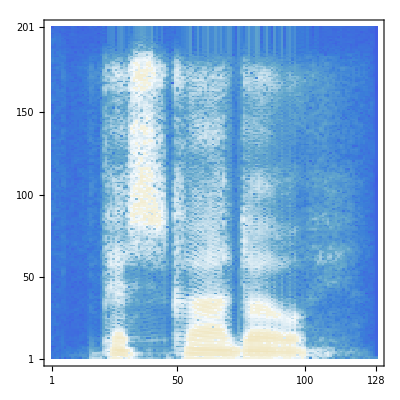

```mathematica
MatrixPlot[Log[Transpose[ss]], DataReversed->{True, False}, AspectRatio->1]
```

```mathematica
avgSpectrogram=(ArrayPad[ss,{{0,1},{0,0}}]+sf)/2;
```

```mathematica
Audio[InverseSpectrogram[avgSpectrogram], SampleRate->16000]
```

```mathematica
Dimensions[ss]
```

{128,201}

```mathematica
NetModel["Whisper-V1 Multilingual Turbo"]
```

NetGraph[<41>, <42>]

```mathematica
extractor=NetChain[{NetModel["Whisper-V1 Multilingual Turbo"],AggregationLayer[Max,1]}][AudioPartition[#,30][[1]]]&
```

NetChain[{NetModel[Whisper-V1 Multilingual Turbo],AggregationLayer[Max,1]}][AudioPartition[#1,30]⟦1⟧]&

```mathematica
audios={audioSpanish->"Spanish",audioFrench->"French",audioEnglish->"English", audioGerman->"German" };
```

```mathematica
(* FeatureSpacePlot[audios,FeatureExtractor->extractor,LabelingFunction->Callout]*)
```

-Graphics-

```mathematica
(* featuresEnglish = extractor[audioEnglish]
featuresGerman = extractor[audioGerman]
featuresFrench = extractor[audioFrench]
featuresSpanish = extractor[audioSpanish] *)
```

{0.774171,0.719631,0.759881,0.631769,0.826635,0.908477,0.732558,1.12869,1.31293,0.98251,0.800492,1.00817,0.808665,0.776203,0.820396,1.24126,1.02109,0.954736,1.24192,1.23756,1.07509,1.16689,0.849514,0.81745,0.709537,0.726202,0.739852,0.790792,0.994964,0.871079,0.984711,0.761131,0.746905,0.786765,1.41789,0.997074,0.760269,0.848729,0.862149,0.880143,1.11858,1.06614,0.939398,0.947875,0.812391,1.33791,1.02307,0.956568,1.24641,1.06704,0.88115,0.791525,1.21875,0.806163,1.42222,1.23695,1.37143,1.12987,1.3487,0.927695,1.14026,2.83735,1.05268,1.18407,1.05678,1.09039,1.012,1.21731,0.815894,1.34669,0.771008,1.16941,0.925183,0.824055,1.1263,0.912548,1.22294,1.00131,0.820401,0.984049,0.920434,0.849586,0.828685,1.0491,1.16012,0.882728,0.964341,0.789098,0.944518,1.01947,1.88916,0.670617,0.909887,0.460764,0.975489,1.10799,0.952197,0.800464,1.14472,0.952666,1.28195,1.13514,0.849474,0.830162,0.728182,0.94601,1.06894,0.755903,1.21056,0.891513,0.989706,1.29011,0.993587,1.08718,1.04836,0.872235,2.22002,1.13155,1.07711,0.83807,1.04337,0.811216,1.17395,1.2283,0.789591,0.962139,1.03846,0.797361,0.692767,0.719227,1.01761,1.08332,0.854921,0.939724,0.763391,1.1069,0.935704,1.01166,0.808471,0.981373,1.14912,1.31907,1.14064,1.11149,0.916265,0.845951,0.995178,0.99077,0.91932,0.882433,0.916839,3.95378,0.812488,0.896717,1.10472,0.900737,1.77652,0.880935,1.5057,1.00717,1.72737,1.11086,1.0067,0.833267,0.853429,0.926996,0.967287,0.8444,0.900422,0.901072,1.14714,1.49388,0.872511,0.977507,1.24687,1.15786,1.21608,1.13684,1.10841,0.857357,1.5002,0.84698,4.36485,0.707804,1.03424,1.281,1.26359,0.562464,0.685724,1.18359,1.24012,1.01715,1.18282,1.18458,1.46351,1.38591,1.13588,1.41977,1.54343,1.2208,1.31269,1.06296,1.23885,1.03321,0.805007,0.897218,0.966484,0.960517,1.24427,0.791861,0.733285,0.769227,0.744786,0.874165,1.09789,1.21534,1.39405,0.97601,0.999661,1.03997,1.26734,0.855351,1.00298,1.49755,0.880764,0.700711,1.05522,2.73339,1.1078,1.35822,1.15159,2.61959,0.979029,0.959016,1.16206,1.20754,1.15877,1.07653,0.876551,1.2219,1.17011,1.10862,1.13205,0.935506,1.05667,0.913634,0.931257,1.26236,1.20048,1.01232,0.976496,0.89171,0.984467,0.850698,1.23368,0.785955,0.932946,1.32042,1.16503,1.0216,0.90074,0.723188,1.33732,0.946869,0.946755,1.18413,1.39972,0.818821,1.00563,0.834069,0.811835,1.19667,1.17418,1.17392,1.21183,0.896576,1.19946,1.09403,0.859106,0.613346,0.673695,0.998583,1.19621,1.06966,1.20451,0.843783,1.34844,1.07691,0.968859,1.21696,0.974054,0.869834,0.948008,0.865781,1.22174,0.868728,0.875825,0.812745,1.28526,1.3875,0.822806,0.951218,0.815463,1.33362,0.988441,0.654523,1.3175,1.06002,1.17786,1.13442,1.14322,0.753428,0.83312,1.28272,0.974636,0.950766,1.01945,1.49688,2.09519,7.14439,0.677672,0.843516,1.13583,1.16861,0.794248,1.00752,1.18549,0.949175,3.03925,0.596643,0.879087,1.16626,0.800682,0.893409,0.872077,0.80745,1.12855,1.22194,0.726912,0.883563,0.882699,1.07033,0.902287,1.0686,1.09203,0.80273,0.92066,0.845005,0.846505,1.12455,1.0195,1.374,0.993206,1.05549,1.11092,1.02761,0.818848,1.05811,1.23259,1.11061,0.765214,1.26545,1.23808,1.09478,1.23003,1.12748,0.756889,0.849223,1.29104,1.25479,1.00318,0.954807,1.01721,0.996403,1.16868,0.865875,1.12312,0.833862,1.40179,1.30522,0.882799,1.26205,1.02847,1.49417,0.76808,1.15658,0.986223,1.18168,1.07764,0.784144,0.946799,2.04992,2.47139,1.05041,1.29203,0.714365,0.837577,0.865095,1.14555,0.46599,0.78455,0.799418,0.654669,2.13231,0.935378,1.07497,1.00971,1.06909,0.847029,1.05505,0.992838,0.953241,1.0781,0.749228,0.886774,1.38448,1.04287,1.53015,1.05023,1.02124,1.03245,1.04131,0.69408,0.944735,0.921468,0.814733,1.10699,1.00371,0.778832,1.21159,1.04961,0.950549,1.07321,1.04857,1.30395,1.03112,0.841323,0.923506,1.10646,0.848144,1.47911,1.0057,0.749235,0.775109,1.22502,1.73655,1.03084,0.767805,1.26214,0.898026,1.22355,1.37857,0.970834,1.08986,0.801519,0.696346,0.984541,1.33219,0.96942,0.927446,1.0283,1.09415,1.09794,0.779003,0.713928,0.973576,1.75645,0.86741,1.12234,1.08616,1.02473,0.782065,1.23058,0.963553,1.28104,0.850468,1.17087,1.95644,0.882839,1.0385,0.97031,1.01275,1.03707,1.36735,0.996233,0.921538,1.05505,0.587759,0.926376,0.715256,0.848553,0.860826,0.728148,0.685717,0.903696,0.652255,1.29265,1.037,1.20992,1.14958,1.10413,1.21715,1.09698,1.25163,0.94781,0.870773,0.844885,0.850205,1.02716,1.11393,0.809835,0.578801,0.71218,0.821288,0.731185,0.864699,0.875148,0.912038,1.03048,0.656933,0.907672,1.03196,1.21623,0.926972,0.69671,0.889706,0.845285,1.09783,0.745686,0.817986,0.865563,0.955558,1.08323,0.963854,1.15851,1.21491,0.839368,1.22624,0.879907,1.33218,0.914654,1.13835,0.878495,0.926492,1.61487,1.09669,0.829938,1.43707,0.900364,1.1404,1.23789,0.91401,1.6487,0.879659,0.936067,1.05732,0.803254,0.814707,0.955815,0.819083,1.02824,1.02247,0.945273,0.796214,0.778401,0.79894,0.765518,0.737641,0.702534,0.64944,0.759994,0.926202,0.888147,0.997975,1.12234,0.991677,1.07681,1.01206,0.876681,0.76884,1.09749,0.94063,0.867904,1.26794,0.859735,0.889168,1.60387,0.968983,1.1462,1.24847,0.79722,0.90604,0.983415,0.842439,2.4449,1.11582,0.74686,0.785294,0.835451,0.777304,0.83285,0.856985,1.10916,0.960085,0.879053,0.797543,0.917137,1.02444,1.47686,0.717521,0.964563,1.29241,0.713599,0.97693,0.947482,1.2331,0.940294,1.30124,1.05749,1.12697,1.11368,0.953545,0.539656,1.42747,0.827928,1.18152,0.6019,1.10897,1.00913,1.02497,1.21278,0.864258,0.903078,1.04463,1.10109,10.1706,0.7555,0.903892,1.1004,1.20799,1.34405,0.960052,1.12844,0.888428,1.61946,0.898774,0.949072,0.815217,1.00247,0.764991,0.811053,1.37419,0.81998,0.980964,1.00976,1.02669,1.24938,0.780028,0.682241,0.886279,0.955452,0.890462,1.02984,1.08213,0.947393,0.785514,0.782921,1.25473,0.719296,1.11736,1.04514,0.84177,0.839864,1.33442,0.771167,0.975462,0.996912,0.795408,0.968422,0.763428,1.17866,0.912981,0.981343,0.87941,1.5361,1.13017,1.05589,0.827125,1.28769,0.962403,1.12175,2.00043,0.940823,1.01958,1.26175,1.24022,1.21401,1.1578,0.92818,0.785182,0.863974,1.38851,1.18234,1.24755,0.845133,1.62421,0.698987,0.757864,0.672056,0.956592,0.855975,1.00127,0.795154,0.693583,1.13205,1.31245,1.20151,1.07399,1.11042,1.10178,0.941132,0.988483,0.880132,1.05422,1.33073,0.749423,0.76163,0.729287,1.22511,1.96547,1.19209,1.22299,1.22042,1.0961,0.909276,1.24448,1.117,0.90445,0.981596,1.15209,0.859964,0.877575,1.00923,0.97413,1.12067,1.04391,0.707949,1.11236,0.868843,0.977339,1.18575,1.18781,1.53844,1.10863,0.953091,1.31611,2.18489,1.04403,1.06279,1.05068,1.07042,1.18283,0.989853,1.41314,1.13963,1.03823,0.699952,0.880917,1.10697,1.25178,0.871068,1.02636,0.766088,0.926672,0.97271,0.888804,0.937002,1.28738,1.3034,0.911774,1.3155,0.937073,0.909152,1.02732,1.18943,0.2908,0.823092,0.982793,0.962224,1.32427,0.813633,0.880322,0.996707,1.47415,1.28913,0.931893,0.869244,0.734453,1.25838,0.995455,1.85467,0.910514,0.892151,1.16251,1.16886,0.840615,0.843404,0.882163,1.01659,1.10581,1.05677,1.03426,0.705085,1.02336,0.930129,1.18061,1.09275,1.08624,1.21017,1.32984,1.28721,1.11535,1.22646,1.20298,1.21417,0.70166,1.6282,1.08433,1.01696,0.919122,1.36764,1.02597,1.17057,1.29129,1.04877,1.1821,0.821109,1.21789,1.40865,1.05103,0.910787,1.22963,1.17983,0.734731,1.07172,1.13012,1.0407,0.983859,0.902877,0.939645,0.877282,0.938584,1.12427,1.17569,1.2897,0.973956,0.91399,0.673133,0.938426,0.957976,0.813637,1.23752,0.770731,0.923167,0.986979,1.19008,1.20411,1.07854,0.74437,0.939878,1.01335,0.870917,1.16377,0.875562,1.04951,1.00386,0.995598,1.24529,1.02198,1.41625,0.712914,0.844573,0.762549,1.00832,0.92143,1.0202,0.865117,0.742905,0.870959,1.41244,1.28718,1.05103,0.941998,1.04843,1.32618,0.900872,0.982817,0.869169,0.874319,0.834785,1.46701,0.991976,0.604456,1.2314,0.841993,0.972923,0.980275,1.33894,0.817146,0.720322,0.820751,1.22576,0.717749,1.20911,0.821371,1.59532,1.08991,1.21794,1.3803,0.946816,0.974136,0.998968,0.689222,0.793665,0.821681,1.17827,0.641201,1.47847,0.983398,1.09,0.953841,1.26466,1.04776,1.2203,0.64649,1.13949,0.888492,0.861697,1.18388,1.05632,1.11929,1.38061,0.823605,1.42209,1.00443,0.940914,0.874674,0.89353,1.19085,1.21419,1.19014,1.25947,1.01838,1.10464,0.834321,0.90694,0.92147,0.702558,1.00815,0.734766,1.05174,0.978437,1.18466,0.703371,0.950956,0.829652,1.19139,1.16362,0.868401,0.998248,1.17699,0.976961,1.28995,1.21867,0.68839,0.982411,1.0219,1.20564,0.856465,1.28542,0.998006,1.31499,1.23668,0.963873,1.0015,0.902853,1.37466,6.71967,4.72016,0.923654,1.06859,0.849374,1.05069,0.932201,1.59703,0.600782,1.09834,1.01498,1.17312,1.17578,0.936825,1.20702,1.19919,1.07891,1.07149,1.08128,1.13181,1.24358,1.3294,1.15699,0.84191,0.649885,0.752754,1.25393,0.880137,1.41087,0.944024,0.936037,1.04463,0.883959,0.84885,0.938178,1.1106,0.675765,1.10053,0.840627,0.832837,0.991671,1.07897,1.09444,1.93074,0.80715,0.786491,1.40871,0.991152,1.08525,0.939563,0.655746,0.846702,0.937492,0.733954,1.08385,1.04005,1.09286,0.976066,1.1262,0.94759,1.03841,1.20689,0.925057,1.1404,0.904874,0.824404,1.23423,0.870838,0.999422,0.931169,0.674098,1.15187,1.01,0.825931,1.16425,0.641211,1.13575,0.946972,1.30735,0.912731,0.864293,0.905395,0.771334,0.850719,0.963704,0.963299,0.850234,0.957232,2.91101,0.814573,0.951847,0.765108,0.815954,0.973988,1.03286,0.939314,0.842274,0.917163,1.04488,1.17626,1.01346,1.13187,1.02709,0.686672,0.88267,2.9815,1.14471,0.944178,1.0274,1.14753,1.29459,1.34102,1.20601,0.937701,1.13877,0.891185,0.772511,0.938589,1.02539,1.04278,1.08404,0.924782,1.1676,0.962019,0.940238,0.700984,1.0419,0.845078,1.00207,1.43299,0.968229,0.667403,0.833583,0.744544,0.88154,0.882751,0.714093,1.08146,0.991879,0.949925,1.17211,0.876462,0.920643,1.1219,0.874922,1.2597,0.956628,0.969148,1.03842,0.982584,1.04203,0.914642,1.45267,1.19536,0.815048,3.42772,0.977187,0.859617,1.00022,0.918433,1.41704,1.12303,2.41217,0.884584,0.917601,0.95063,0.968599,0.869241,0.726486,0.726394,1.00459,1.20054,0.992306,1.17684,0.957708,0.959122,1.26146,1.0474,0.940447,1.03708,1.10612,1.212,0.877735,0.832564,1.15396,0.833992,0.910857,0.905355,1.06224,0.603851,1.02588,1.38509,1.12017,0.962799,0.912599,1.00105,0.824467,1.20212,0.869862,1.078,1.11711,1.17642,0.801688,1.07102,0.731327,0.820472,1.49016,0.91778,0.994656,1.29975,1.27186,0.924591,1.07445,1.13998,0.909422,0.878539,1.11446,0.87464,0.665784,0.971,0.976044,1.15405,0.957882,1.02775,0.800808,1.06754,0.831219,0.64987,1.2683,0.897633,0.712936,0.822186,1.04636,0.855112,0.996836,1.6201,1.04871,1.07494,1.17433,1.01562,1.07332,0.804416,0.918498,1.38756,0.877248,1.05653,0.811352,0.829152,1.21265,0.982834,0.830737,1.01208,1.12846,0.860131,0.859137,0.880918,0.690392,1.47899,1.32432,0.965447,1.07035,1.28643,0.980371,1.30651,0.857588,0.958485,0.843879,1.09454,0.777596,0.801212,0.771688,1.50649,0.936251,1.21551,0.69713,0.788947,1.15962,1.27138,1.05127,1.19254,0.784851,1.15722,0.913139,0.691379,0.962296,0.965456,0.916523,0.902853,0.73759,1.03832,0.803088,0.972746,0.830981}

{0.781092,0.695251,0.756813,0.635694,0.852918,0.897548,0.700583,1.22312,1.33738,0.903965,0.826284,1.06561,0.794518,0.774506,0.855071,1.19929,0.92618,0.971971,1.32634,1.1837,1.08505,1.17804,0.856548,0.952087,0.655015,0.783279,0.721483,0.835519,1.01629,0.74727,1.06336,0.759319,0.732531,0.838994,1.39429,0.962379,0.759061,1.04474,0.930301,0.907232,1.23355,1.06637,1.0013,0.911981,0.703597,1.26446,1.00005,0.948665,1.33979,0.980249,0.92896,0.701055,1.39319,0.7987,1.37682,1.22611,1.32977,1.14123,1.54979,1.00074,1.08162,2.97088,1.24095,1.16705,0.901538,1.04655,0.983289,1.25254,0.898995,1.40881,0.788216,1.06644,0.939087,0.868369,1.20879,0.90077,0.918658,1.09524,0.827826,1.07345,0.948459,0.878173,0.842318,0.981736,1.31444,0.950958,0.879538,0.778132,1.08076,1.08057,1.89307,0.793656,0.935658,0.500394,0.954023,1.10061,1.02736,0.787184,1.16001,0.979058,1.32251,1.10465,0.857125,0.740415,0.907255,0.917716,1.22365,0.897915,1.21109,0.885762,1.03464,1.28071,0.898079,1.13167,0.969668,0.985315,2.45833,1.20285,1.00067,1.02009,1.15389,0.945398,1.24835,1.26392,0.911232,0.922846,1.13058,0.806577,0.74394,0.74529,1.07021,1.0851,0.836665,1.02038,0.670974,0.847771,1.00229,0.93697,0.653835,1.19509,1.16801,1.24346,1.17424,1.04498,0.98889,0.937167,1.07616,0.922555,1.00525,0.92542,0.949544,3.75766,0.81397,0.89057,1.02468,0.942295,1.69594,0.907256,1.57014,1.1009,1.70222,1.11827,1.09557,0.783381,0.883213,0.92389,0.995541,0.821231,0.876214,0.74771,1.193,1.45842,0.857438,1.03158,1.05436,1.15783,1.15001,1.13108,1.16956,0.843798,1.14616,0.771063,4.2162,0.734787,1.01746,1.17349,1.14674,0.711729,0.725207,0.997864,1.31974,0.991031,1.11243,1.12699,1.47468,1.21062,1.17695,1.41708,1.54944,1.22958,1.21584,1.11542,1.38075,1.01506,0.803424,0.810121,1.04762,0.968203,1.22464,0.805604,0.795364,0.788837,0.729161,0.920696,0.995823,1.3496,1.28782,1.0089,1.22462,1.11967,1.26851,0.754326,1.04745,1.2226,0.882055,0.717197,1.09405,2.72018,1.08739,1.36898,1.13637,2.57579,1.00013,0.708703,1.18934,1.19261,1.17863,0.957128,1.01161,0.865902,1.01602,1.15259,1.16824,0.889883,1.00684,0.972086,0.927895,1.30465,1.09806,0.853369,0.951362,0.723234,1.12583,0.905999,1.33012,0.889757,1.19221,1.29881,1.16033,0.892266,0.862976,0.86143,1.26093,1.00269,1.07377,1.22286,1.43802,0.748808,1.21319,0.888941,0.874583,0.981934,1.00589,1.12627,1.01875,0.922608,1.12564,1.11195,0.657978,0.722785,0.695941,0.987888,1.16629,1.07206,1.16329,0.857218,1.33886,0.986674,1.00063,1.28839,0.835988,0.912337,0.954657,0.892667,1.17699,1.05757,0.837733,0.814193,1.44953,1.32955,0.847904,0.812903,0.864808,1.27529,0.960946,0.672781,1.45324,0.99654,1.22724,1.1127,1.13114,0.804926,0.934054,1.12291,0.895557,0.846541,1.19882,1.36798,1.87418,7.16761,0.797916,0.894757,1.11743,1.12694,0.774564,0.849282,1.02022,0.883534,3.06453,0.642808,0.818851,1.24789,0.87694,0.974497,0.697728,0.828885,1.14241,1.21083,0.857949,0.927819,0.734734,1.06884,0.826557,1.13951,1.06968,0.808272,0.946711,0.841616,0.874029,1.13138,1.1251,1.37972,0.90722,1.1479,0.998152,1.1639,0.818364,0.984093,1.09942,1.0621,0.71679,1.23461,1.22213,1.15623,1.14312,1.11185,0.761302,0.892661,1.27678,1.10866,1.12164,0.756139,0.988447,1.04649,1.15941,0.891588,1.05964,0.857944,1.30417,1.27564,1.02577,1.23666,0.87654,1.2138,0.727511,1.39503,0.968883,1.10596,1.09734,0.684678,1.02908,2.05282,2.3793,0.757445,1.28572,0.781236,1.02076,0.802527,1.22692,0.470377,0.773804,0.744801,0.666514,2.01202,1.0258,0.993748,1.04726,1.00573,0.824187,1.07411,0.875152,1.0368,1.12482,0.743348,0.943208,1.37332,1.06205,1.47511,1.07637,1.13423,0.95232,1.13768,0.658109,0.946503,0.915057,0.744774,1.1232,0.991541,0.659683,1.16387,1.03985,0.901746,1.12675,0.955817,1.27538,1.14973,0.797561,0.94763,1.07108,0.978258,1.31371,1.09133,0.870164,0.791046,1.19868,1.64555,0.945958,0.789848,1.25768,0.8801,1.15884,1.32367,0.919424,1.0045,0.841384,0.617635,0.826807,1.25381,0.938287,1.11729,0.989669,1.05667,1.05654,0.778867,0.792162,0.894711,1.80382,0.968843,1.00744,1.06448,1.10332,0.699562,1.30547,0.937873,1.20199,0.9778,1.16734,2.00707,0.861038,1.0232,0.818927,1.00764,1.23048,1.38455,0.895575,1.08185,1.02477,0.578454,0.926088,0.76611,0.880652,0.774513,0.873995,0.68856,0.734845,0.627908,1.31201,1.09644,1.32395,1.3073,0.935732,1.0921,0.982866,1.31949,0.976748,0.899697,0.856295,0.892182,0.884592,1.0913,0.770704,0.616792,0.786385,0.662692,0.788506,0.890248,0.905512,0.88409,1.12635,0.670536,0.869463,1.03789,1.35295,0.932746,0.723162,0.898029,0.960948,0.991181,0.85196,0.98067,0.848758,0.851594,1.10721,0.97526,1.17906,1.28034,0.794594,1.11307,0.819167,1.3155,0.927357,1.06154,0.76662,0.89823,1.68228,1.2304,0.890736,1.30772,0.918418,1.11282,1.13213,1.06242,1.56439,0.89774,1.02209,1.04757,0.683913,0.890763,0.892971,0.867824,0.798945,1.09125,0.939704,0.836757,0.801446,0.914441,0.767894,0.752107,0.716254,0.571232,0.784603,0.913877,0.746239,0.87742,1.16534,0.801714,1.13302,0.932749,1.04716,0.805446,1.1514,0.884365,0.93169,1.26343,0.928034,0.827477,1.73157,1.14478,1.13287,1.19841,0.751933,0.854987,0.991356,0.915486,2.47884,1.09277,0.732588,0.712716,0.745814,0.858774,0.827301,0.87893,1.111,0.863151,0.956798,0.91654,1.09202,1.13168,1.42251,0.75618,0.972408,1.31904,0.672516,0.688352,1.11959,1.18998,1.00562,1.2491,1.07404,1.25601,0.930019,0.837019,0.77668,1.32273,0.805062,1.31525,0.68174,0.886187,1.07965,0.983692,1.31025,0.873175,0.978383,1.0133,1.1087,10.0076,0.827462,0.905269,1.11442,1.06036,1.48486,0.78422,1.27146,1.03736,1.64573,0.886024,0.977053,0.826884,1.00672,0.707806,0.891559,1.29677,0.819525,0.98021,0.896429,1.09613,1.22094,0.840291,0.811753,0.799445,0.926378,0.888325,1.07532,1.11619,0.877239,0.729354,0.815329,1.17997,0.702089,0.924844,1.12118,0.842187,0.841318,1.21312,0.83439,0.996323,1.1449,0.790632,0.934908,0.809294,1.18895,0.922069,1.04673,0.881065,1.56442,1.09176,1.06845,0.760929,1.22699,0.957418,1.03572,2.24041,0.935056,1.14854,1.01319,1.29135,1.06564,1.16833,1.05728,0.956913,0.88329,1.37677,1.25348,1.39883,0.822136,1.717,0.786318,0.81596,0.683098,1.01947,0.817818,0.975531,0.728436,0.814616,1.05419,0.937991,1.18712,1.1532,1.10641,0.919884,0.989245,1.13162,0.896526,1.0587,1.31476,0.778633,0.880363,0.688014,1.19732,2.20953,1.20984,1.14808,1.22551,1.15923,0.906948,1.23937,1.05637,0.908248,1.29563,1.14128,0.96043,0.860205,1.03287,0.947408,1.10094,1.03108,0.696312,1.01757,0.775908,0.97932,1.20989,1.23645,1.50089,1.12385,1.09315,1.32822,2.44307,1.04369,1.12514,1.08487,1.03259,1.19559,0.917578,1.35135,1.14172,1.03108,0.728104,0.955947,1.06009,1.26359,1.03976,1.11778,0.867912,1.00397,1.08301,0.90658,0.975114,0.925179,1.08607,0.801511,1.3096,0.918511,0.921249,1.07282,1.26894,0.209214,0.745087,1.07052,1.03682,1.24633,0.792837,0.912051,0.995793,1.33682,1.27531,1.1817,0.853074,0.741648,1.35733,0.910432,1.8645,0.95211,0.972398,1.16114,1.06304,0.692092,0.911019,0.851379,1.11225,1.2031,0.951252,0.971493,0.716752,1.04833,0.93314,0.944555,1.03362,1.03361,1.05755,1.44401,1.09928,1.13118,1.34173,1.19603,1.1809,0.802186,1.52298,0.947581,0.988314,0.914579,1.31075,1.12585,1.13408,1.18801,1.10508,1.1761,0.833939,1.15333,1.30825,1.11184,0.926998,1.24831,1.18536,0.682385,1.06837,1.09868,1.39004,0.981311,0.829853,0.985857,0.904297,1.21858,0.94836,1.19195,1.07596,0.976128,0.895817,0.713199,0.873956,0.97388,0.798409,1.19037,0.792234,0.857624,1.0632,0.996832,1.1769,1.11313,0.724141,1.00585,1.10037,0.90127,1.17508,0.825776,1.05758,0.903587,1.06826,1.22196,1.04307,1.49326,0.737006,0.887294,0.987141,0.880018,0.920086,0.933614,1.04544,0.762527,0.844825,1.05595,1.20207,0.988004,0.957711,0.883381,1.08919,1.1066,0.820086,1.01268,0.878241,0.888396,1.47104,0.868212,0.688235,1.07301,1.00166,1.02413,1.1683,1.21388,0.860113,0.74142,0.969775,1.10609,0.677546,1.23382,0.947309,1.81888,1.05424,1.1677,1.4061,0.960884,0.866996,0.968819,0.690013,0.918821,0.815009,1.31428,0.676186,1.43905,0.980115,0.994894,0.940301,1.0802,1.08017,1.30132,0.711738,1.09979,0.92555,0.849448,1.05735,0.865444,1.09047,1.34435,0.81771,1.38839,0.968265,0.86342,0.987227,0.879336,0.941652,1.38021,1.15104,1.383,1.1476,1.06568,0.862117,0.902038,1.04356,0.603504,1.01823,0.702554,1.0411,0.774656,1.13944,0.673214,0.88773,0.951302,1.22224,1.22925,0.990363,1.05335,1.08676,0.863145,1.16284,1.44804,0.641154,0.954727,0.941908,1.34443,0.859557,1.45675,1.11432,1.22199,1.12932,0.963715,0.977186,1.00736,1.17725,6.6044,4.70494,0.868117,1.12441,0.911955,1.14842,0.944487,1.59182,0.593269,1.15269,1.02784,1.12783,1.13024,1.10004,1.03297,0.982558,1.07439,1.04802,0.721116,1.23023,1.20311,1.33218,1.01268,0.852958,0.689929,0.948622,1.29795,0.901462,1.21386,0.80935,0.751705,1.16121,0.920758,0.721347,0.8236,1.08526,0.68651,1.22179,0.893486,0.814731,0.996596,1.05891,1.05786,1.93773,0.790053,0.82378,1.1416,1.01139,1.10504,0.928939,0.749533,0.673532,1.05555,0.727513,0.988085,0.993597,1.04179,1.07257,1.23573,1.01158,1.00448,1.02497,0.797746,1.1428,0.880788,1.10703,1.16132,0.894883,1.1091,0.897721,0.678055,1.24037,1.17795,0.718889,1.11905,0.649751,1.16611,0.980492,1.08381,0.869886,0.681811,0.945213,0.776383,0.928952,0.992924,1.06378,0.720536,1.01312,3.00763,0.854474,0.976274,0.742007,0.857803,0.931323,0.818213,0.879804,0.847811,0.875402,0.986511,1.03927,0.943784,1.12242,0.981799,0.678223,0.982492,2.87208,1.12158,0.943794,1.05356,1.20712,1.23243,1.17967,1.22439,0.897815,1.03499,0.932463,0.717729,0.719778,0.887296,1.03408,1.02716,0.901061,0.97852,0.912365,1.07259,0.755137,0.883627,1.24856,1.01151,1.48829,0.986198,0.714275,0.806507,0.831008,0.881225,0.886531,0.76311,1.11131,1.01558,0.921643,1.00637,0.70648,0.785462,1.20704,0.854261,1.29023,0.994318,1.06168,0.860658,0.896144,1.15256,0.894832,1.45171,1.12919,0.845847,3.4317,0.954021,0.925915,0.944916,0.918052,1.30355,1.0816,2.41161,0.926531,0.831572,0.939025,1.15446,1.07885,0.66624,0.671397,0.959155,1.18016,1.00508,1.04632,0.938899,0.99129,1.21993,1.07566,0.913489,0.898758,1.1343,1.21594,0.907724,0.844196,1.27789,0.845337,0.847459,1.08731,0.949663,0.67905,1.06485,1.37381,1.17331,1.06187,0.69911,1.01756,0.815991,0.852848,0.813561,1.10197,1.14794,0.994976,0.803422,1.07639,0.697076,0.851307,1.68242,0.780192,0.949888,1.35592,1.27252,0.762986,1.13916,1.06891,0.730993,0.74331,0.925588,0.915479,0.663831,0.984595,1.07068,1.1205,0.885678,1.18715,0.975383,1.03342,0.809148,0.714596,1.49421,0.865378,0.763962,0.82398,1.11077,0.862654,0.98403,1.41957,1.09348,0.994796,1.10956,1.00287,0.992785,0.738678,0.926712,1.38758,0.857375,0.994658,0.935811,0.922961,1.20239,1.05033,0.781473,1.14468,0.788009,0.845861,0.911216,1.02569,0.724767,1.47936,1.12261,0.904245,0.931407,0.926642,1.02403,1.03771,0.797479,0.814863,0.904564,1.10106,0.864366,0.866552,0.821481,1.5764,0.922427,1.10523,0.744175,0.86559,1.1942,1.10878,1.04781,1.19727,0.720214,0.835607,0.876033,0.682047,1.07102,1.03116,1.02839,0.84533,0.722368,0.748482,0.916987,0.9483,0.790344}

{0.782953,1.16544,0.770849,0.646978,1.07808,1.0844,0.720755,1.5196,1.20571,1.03628,0.798525,1.25839,0.828321,0.744425,0.988403,1.27864,1.03886,0.979849,1.0452,1.17377,1.13432,1.11481,0.840161,1.0372,1.37124,1.02056,0.795833,0.793239,0.896147,0.855572,1.11779,0.99154,0.86668,0.958216,1.39704,0.85127,0.776576,0.726102,0.852536,1.0389,1.03715,0.697818,0.888886,0.806951,0.961418,1.1372,1.15106,1.02135,1.34602,0.986619,0.897369,0.978753,1.1734,0.899567,1.43198,1.05081,1.33946,1.2119,1.57281,1.04439,1.16446,3.39468,1.05702,1.039,0.908376,1.1492,0.954959,1.23057,0.978133,1.44987,0.980672,0.98988,1.10802,0.826412,1.23255,1.27463,1.08304,1.04457,0.818631,1.06503,1.2756,0.945858,0.836392,0.763658,1.21863,1.12339,0.978073,0.758021,1.13895,1.09775,1.8853,0.95628,1.07867,0.677089,0.853733,0.959603,0.914197,0.865177,1.19478,1.01696,1.23347,1.2314,0.87843,0.879084,1.3092,0.894979,1.147,1.20054,1.5354,0.832992,1.20977,1.21375,1.05241,0.844142,0.937342,0.965901,2.12783,1.13615,1.10991,0.853062,1.11513,1.03476,1.37176,1.32343,0.966445,0.918829,1.18649,0.899284,0.674938,1.03692,0.92851,1.41234,0.904257,0.883871,0.695358,1.00551,1.09087,1.12657,0.779639,1.05009,1.31172,1.16976,1.10959,1.04544,1.01195,0.871739,0.917144,0.97672,0.995182,0.946038,1.06172,3.67721,1.06318,1.07451,1.06308,0.990044,1.78016,0.959171,1.62111,1.0924,1.77872,1.13662,0.866259,0.767875,0.716558,0.888701,0.92099,0.927329,0.84036,0.770364,1.44654,1.14444,1.06978,1.1647,1.03201,1.12813,1.34451,1.06338,1.05219,1.06494,1.25539,0.834669,4.40966,0.873209,1.03352,1.16104,0.842567,0.857408,1.13041,0.931319,1.57401,1.07592,1.19311,1.07177,1.32343,1.53207,1.23649,1.60518,1.55454,1.26069,1.26364,1.21842,1.21572,0.987243,0.882638,1.02283,0.963053,0.927791,1.33383,0.918685,0.994907,0.878396,0.870068,0.996481,1.16324,1.11577,1.31489,0.923142,1.23717,1.02432,1.26327,0.860074,1.09919,1.34088,0.957894,0.785377,1.09401,2.79436,1.07462,1.34721,1.15233,2.81133,0.955468,1.13388,1.23,1.35019,1.35152,1.31975,1.04504,0.991242,0.994077,1.21185,1.1783,0.81394,1.01619,0.911211,1.53827,1.31005,0.862339,0.969886,1.06101,0.745807,1.12961,0.643568,1.43502,0.862644,1.16354,0.991904,1.1296,0.990507,0.965001,0.91609,1.33675,1.03955,1.05441,1.2495,1.53128,0.699097,0.933692,0.922643,0.903923,1.31267,0.928495,1.29234,1.03679,0.941325,1.04717,0.872942,0.612487,0.649914,0.907519,0.844607,0.921843,1.02344,1.25928,0.875689,1.40677,0.863762,0.908049,1.18972,0.951724,0.999264,0.919811,0.94548,0.903433,0.947926,0.766222,0.708743,1.09832,1.39158,1.09767,1.11577,0.994512,1.2966,0.878681,0.689951,1.2127,0.961806,0.962912,0.955265,1.11435,0.771937,0.77364,1.11234,0.944902,1.17402,0.922179,1.28354,1.20753,7.33983,0.79343,1.02025,1.1096,1.25587,0.777452,0.86184,0.938068,0.862329,3.10919,0.475961,0.781267,1.07891,0.627944,1.04991,0.688234,1.05009,1.08865,1.18297,0.806798,0.911099,0.846745,1.056,0.896477,1.01013,1.0617,0.782218,0.972381,0.904506,0.88475,1.02416,0.994045,1.37862,0.879795,1.13407,0.876646,0.867928,1.02733,1.1953,1.21655,1.1726,0.921471,1.04015,1.13378,1.20095,1.04987,1.14293,0.918944,0.916395,1.30064,1.16583,1.08225,0.893761,1.11935,0.975342,1.08055,0.83628,1.04603,1.03025,1.17197,1.15504,0.759566,1.32981,1.06667,0.971179,0.808327,1.4467,0.842854,1.06265,0.86385,0.969186,1.02363,2.07361,2.43417,0.980633,1.20277,0.649627,1.13152,0.879752,0.999984,0.45414,0.707946,0.664946,0.849553,1.98469,0.8761,0.927539,1.11907,1.11374,1.02244,0.894261,0.925809,1.13207,1.01189,0.763414,0.892118,1.42763,1.14569,1.36837,1.2228,1.03998,1.09473,0.92311,0.671782,0.932698,1.01072,0.885647,1.1244,1.02743,0.854063,1.03465,1.16471,2.05537,1.12823,0.999579,1.45598,0.976034,0.875091,1.22393,1.01441,0.901838,1.29374,1.44243,0.941848,0.734703,1.36052,1.44214,0.976448,0.775022,1.09221,1.04956,1.05077,1.07947,0.926316,1.10833,0.890422,1.00493,0.993413,1.13695,1.04525,1.14633,0.878004,1.01165,1.1016,0.774299,0.841913,0.88872,1.67199,0.888679,1.40883,1.02013,1.01462,0.717614,1.35235,0.867228,1.20448,0.917189,1.1585,2.02812,0.956648,1.12702,0.928881,1.22853,1.01458,1.40113,0.898732,0.85571,1.0694,0.623165,0.90142,0.80195,0.89118,0.772641,1.22336,1.24315,0.731514,1.08435,1.33194,1.50115,0.988372,1.17997,0.922742,1.06465,1.0481,1.19575,0.830632,1.04752,0.867678,1.18476,1.10847,1.18311,1.44814,0.656573,0.761012,0.800487,1.17577,1.12778,0.898965,0.921959,0.965367,0.721132,1.04216,1.13684,1.01532,1.01483,0.639463,0.950549,1.06953,0.975097,0.963538,0.857772,0.806234,0.76766,1.24611,1.03237,0.919579,1.26021,1.1821,1.2463,0.870026,1.23326,1.50101,0.943279,0.65715,1.1432,1.6496,1.02377,0.690687,1.44689,1.01393,1.25375,1.08634,1.09117,1.40293,0.995593,1.12792,1.03016,0.690884,0.968284,0.959415,1.1169,0.922742,1.0035,1.0609,0.931152,0.979827,0.960646,0.790726,0.645542,0.697024,0.653453,0.841476,1.06231,0.980068,1.29497,1.32271,0.921201,1.02499,0.931305,1.02987,0.84442,1.15822,0.932473,0.86174,1.32903,0.814894,1.10749,1.54415,1.04439,1.16053,1.16202,1.25463,0.90892,1.03212,1.31051,2.38298,0.958464,0.92599,0.902467,0.85762,0.861851,0.785348,0.870249,1.00669,1.22431,1.08727,0.87603,1.12763,1.08642,1.23404,0.866641,0.938989,1.32103,0.804699,0.81436,1.37385,1.20032,1.10165,1.17813,1.09255,1.19211,0.854017,0.643848,0.719259,1.56826,0.896904,1.18061,0.662735,0.924053,1.06536,1.08782,1.32808,1.06814,0.993206,0.938167,1.16238,9.86925,0.741006,0.976748,1.23464,0.901585,1.49889,0.743831,1.16996,1.1134,1.70932,0.996681,0.935751,0.977873,0.872324,0.744646,1.04289,0.767383,0.820192,0.998805,0.718389,1.21808,1.27606,0.728404,0.735537,0.76633,0.920683,0.675245,0.804023,1.17681,0.881951,0.746204,0.991535,1.1759,0.716812,0.898634,1.06732,0.766893,0.919038,1.01645,0.945483,0.973587,0.898235,0.845723,1.01393,1.10303,1.23148,0.758896,1.05021,1.0597,0.880101,1.02967,1.26544,0.915597,1.15367,0.953063,1.05797,3.03887,0.998215,0.904005,1.08036,1.26442,0.875228,1.12905,1.06278,0.853972,1.05502,1.40375,1.194,1.15904,1.01989,1.61897,0.75583,0.780903,0.806161,1.29546,1.15769,0.963311,0.790035,0.987813,0.973584,0.647016,1.15858,1.1388,1.1267,0.866263,0.938899,1.56665,1.07884,1.04618,1.16087,1.07289,0.635112,0.768451,1.21662,1.86181,1.24817,1.28216,1.10186,1.11796,1.02121,1.25488,1.08311,0.851186,1.17811,1.0653,1.13302,0.878056,1.03217,0.896107,1.02824,1.1313,0.812889,1.00145,0.59355,1.20983,1.61225,1.16556,1.1673,1.39302,0.969534,1.45191,2.32732,1.02808,1.05794,1.1138,1.28953,0.882386,0.878958,1.28995,1.15609,1.23754,1.07187,0.983828,1.04029,1.2764,1.0291,1.00915,0.949342,0.930678,1.12453,1.16302,1.09265,1.11739,1.41471,0.788917,0.950473,1.52746,0.83707,1.01396,1.59821,0.245719,0.807367,0.866981,1.091,1.28712,0.790537,0.995746,1.24841,1.38478,1.42821,0.84211,1.11843,0.905827,1.41099,0.889984,1.98807,1.03436,0.971832,1.31813,1.0912,0.728306,0.877877,0.84719,1.07922,1.15133,1.27102,1.15807,0.913498,1.15217,1.04574,1.10668,1.0078,0.990339,0.961643,1.29407,1.02847,1.19091,0.970585,1.24091,1.14383,0.946755,1.32848,1.12081,1.07369,0.965243,1.33439,1.14621,1.18154,1.0078,1.02161,1.18038,0.952048,1.22291,1.29365,0.971709,0.882493,1.33676,1.13402,0.737304,1.10636,1.07399,0.964528,1.00419,0.961407,1.07446,0.825564,1.02458,1.05641,1.18621,1.00685,0.796472,0.872762,0.584479,1.02027,0.855247,0.739434,1.39647,0.881744,0.854599,0.957644,0.998711,1.05227,1.27004,0.866258,1.07403,1.04861,0.875107,1.07916,0.898483,1.27325,0.819293,1.13701,1.2453,1.04225,1.53814,0.769597,0.941162,0.799954,1.19314,0.930264,0.97843,1.03665,1.00752,0.897083,1.18681,0.667648,1.14793,1.03838,0.888959,0.865439,1.03014,0.880775,1.09663,0.887607,0.810938,1.31975,0.987169,0.843798,1.07091,0.985763,0.808099,1.29122,1.03296,0.839788,0.669854,0.858029,1.30016,0.885909,1.12082,0.923011,1.47457,0.948934,0.90468,1.87889,1.07612,1.04777,1.15846,0.863167,0.8449,0.844672,1.36099,0.921822,1.331,0.996678,0.93007,0.883587,1.10194,1.11039,1.14597,0.691593,1.2844,1.07474,0.746092,0.90914,0.912539,1.02982,0.988762,0.897931,1.44406,0.952354,0.905423,1.0553,0.9455,0.938413,1.46285,1.07569,1.44807,1.03777,1.06211,0.735506,1.12662,0.942765,0.70335,0.992838,0.690223,1.00254,0.822912,1.30807,0.660997,1.1913,1.12185,1.14498,1.21499,1.0116,1.15572,0.880363,1.00358,1.12772,0.937761,0.746772,0.896205,0.839237,1.2253,0.936386,1.3727,1.17318,1.11145,1.40775,0.975484,0.981072,1.06328,1.25626,6.27157,4.6338,0.818229,1.13015,0.944577,1.07805,1.03168,1.62182,0.860584,1.06442,1.00461,1.07903,1.05889,1.24229,1.14683,0.896574,0.970308,1.19388,1.018,1.09323,1.28133,1.39588,0.884878,0.76809,0.611949,0.975122,1.22775,0.720542,1.08454,0.921951,0.870676,1.17657,1.03916,0.651415,0.874194,0.996424,0.796009,0.978398,1.00136,0.966737,0.960704,1.03648,1.05495,1.80865,0.848912,0.705607,1.15581,1.02486,0.881365,0.858916,1.13637,0.708201,1.01678,0.657111,1.13606,0.81796,1.032,1.00341,1.04142,1.04975,1.10916,0.999767,0.844401,1.51435,1.11864,0.942144,1.29918,1.09576,1.60016,0.826436,0.81225,1.16405,1.06023,0.524664,1.31608,0.674701,1.11825,1.13811,1.06784,0.942572,0.883178,0.856121,1.11152,1.30981,0.82003,1.03109,0.992922,1.09559,2.9654,0.962698,1.0863,0.916126,0.737993,0.987507,1.09695,0.914693,0.790695,0.804527,1.11683,0.989911,1.22783,1.00065,0.943415,0.757368,1.0623,2.95909,1.11016,1.03808,1.09366,0.985314,1.21443,1.28469,1.2596,1.04879,0.928258,0.924435,1.02309,0.715869,1.05661,1.06863,1.03436,1.01126,1.15814,0.888212,1.11901,1.13327,1.16894,1.3328,1.00942,1.51379,0.971374,0.783256,1.08402,0.940993,0.961062,0.939398,0.752789,1.15805,1.10887,1.14523,0.797514,0.820494,0.963411,1.12381,0.929287,0.84046,0.851695,0.991835,0.691503,0.914018,1.00157,0.966635,1.43322,1.2605,0.94407,3.41753,0.932646,0.792705,0.937922,0.842692,1.3733,1.22716,2.36554,0.931217,0.660393,0.948201,1.26052,0.774949,0.658757,0.711897,0.850121,1.14928,1.03514,0.852143,0.935008,1.052,1.28672,1.13243,0.930147,1.11667,1.17331,1.33598,1.19316,0.771797,0.948266,1.21048,0.880879,0.979275,1.12371,0.970101,1.01521,1.40976,1.18639,1.05511,1.12943,0.810529,0.71234,0.946272,0.917843,0.923249,1.10883,1.00198,0.8102,1.09644,0.81273,0.768928,1.05026,0.822229,1.06621,1.24357,1.096,0.936972,1.29241,1.00869,0.73499,0.895095,1.21956,1.04493,0.643377,0.667853,0.943692,1.05728,0.76379,1.29582,0.926722,1.06072,0.859089,0.922209,1.28463,0.880423,0.72335,0.79906,1.01605,0.837312,1.02076,1.41665,1.02813,0.815218,0.92542,1.19839,1.03267,1.01475,1.00121,1.3863,1.0275,0.964946,0.963724,1.00707,1.31374,1.16506,0.813402,1.1973,1.01296,0.849417,0.957843,0.834791,1.06387,1.48066,1.33705,1.07772,1.06057,1.16838,0.956938,1.25896,0.828261,0.762956,0.86474,0.924158,1.0541,1.21817,0.802401,1.61659,0.890027,1.0655,0.839871,0.908649,1.22007,1.06461,1.09918,1.06317,0.838351,0.972904,0.8504,0.710273,0.95629,1.30933,0.919927,1.03529,0.629411,0.799669,1.0415,1.22394,0.962266}

{0.762198,1.135,0.7589,0.643559,1.00769,0.994694,0.707952,1.23434,1.51922,1.14668,0.884969,1.11295,1.08555,0.750536,0.977574,1.25108,1.10021,0.988978,1.26223,1.08289,1.00646,1.29273,0.965327,0.829796,0.827388,0.825842,0.772781,0.632229,0.711094,0.82824,0.948979,0.936166,0.838552,0.86506,1.40603,1.05574,0.761499,0.837302,1.1154,0.82979,1.03717,0.664678,0.875747,0.818099,0.961893,1.12431,0.928786,0.980536,1.39134,0.941078,0.814174,0.77092,1.36339,0.929499,1.14345,1.3894,1.32478,1.12742,1.65784,1.05851,1.04526,2.66276,0.870947,1.17991,0.981376,1.19104,1.01596,1.07266,1.06512,1.40462,0.847753,0.827125,1.4856,0.878339,1.11918,1.19184,0.937485,1.01233,0.726486,0.84774,1.11548,0.908524,0.796247,1.09291,1.2475,1.06084,1.019,0.81501,1.27477,1.25937,1.88088,0.715738,1.16034,0.599343,0.858549,0.851447,1.42844,0.784355,1.00806,0.953708,1.27211,0.909632,0.85793,1.01166,0.724873,1.03843,1.22908,1.19647,1.41094,0.887643,0.899511,1.22172,0.93862,1.00124,0.882693,1.02669,1.81088,1.30371,1.20723,0.937851,1.10111,0.876043,1.19332,1.27529,1.04489,0.829968,1.129,1.00802,0.631551,0.919804,0.919321,0.909608,1.30165,0.750222,0.646488,0.981606,0.993678,0.958682,0.725806,1.34226,1.2865,1.00129,1.10699,1.00124,0.996332,0.841146,0.814503,0.995978,1.02232,0.871914,1.12659,3.5441,1.08662,1.12047,1.131,0.961301,1.70337,0.875057,1.58982,0.914169,1.70692,1.11923,0.927344,0.894072,0.746999,0.963271,0.826179,0.924091,0.761498,0.773131,1.21556,0.994619,0.966032,1.05304,1.01952,1.06205,1.13938,1.26642,1.01385,0.95467,1.25838,0.897385,4.63911,0.93895,1.05069,1.23057,0.876517,0.860413,0.775419,1.10939,1.38274,1.20983,1.37693,1.15062,1.4784,1.01014,1.11283,1.52053,1.5154,1.30112,1.15714,1.17311,1.29622,1.22882,0.922235,0.887692,0.902036,0.908856,1.40379,0.884828,1.00562,0.815509,0.833058,0.966777,0.931534,1.201,1.29333,1.10742,1.11937,0.841874,1.25134,0.741437,1.09629,1.2376,0.986884,0.716948,1.22248,2.70623,0.986335,1.28295,1.10226,2.6387,1.02375,0.708954,0.933172,1.32866,1.16111,1.13677,0.94871,1.12388,0.851786,1.15088,1.22961,0.924061,1.14785,1.18295,0.969291,1.3227,1.03929,1.04156,0.731548,0.692732,0.991439,0.893631,1.37432,0.934233,0.987263,1.0778,1.0291,1.24357,0.817345,0.874082,1.31822,1.15706,1.2572,1.21454,1.50078,0.727838,0.963342,0.8834,0.824297,0.99064,1.2719,1.22414,0.993114,1.09227,1.4523,1.1956,0.693121,0.617834,0.789713,1.0003,1.20519,1.02391,1.07157,1.22188,1.63506,1.07839,1.04859,1.17868,0.92412,0.987448,0.959745,0.821131,1.08942,1.14654,0.864194,0.981309,0.988958,1.35245,0.963692,1.05347,0.853851,1.25148,0.810466,0.645493,1.13325,0.941694,1.12316,0.897203,1.13799,0.578627,0.516127,1.31142,0.702294,0.925367,1.03355,1.23278,1.26855,7.33413,0.733281,0.876766,0.829569,1.28226,0.811261,0.907221,1.01203,0.777729,3.00053,0.471169,0.943211,1.13425,0.964087,1.04541,0.983451,0.78072,1.02525,1.22824,0.924937,0.910132,0.816957,1.04717,1.05903,0.918274,1.12632,0.85235,1.00823,0.863144,0.850602,1.03811,1.26188,1.57257,0.944454,1.292,0.958338,1.00683,0.851625,1.09025,1.09588,1.21592,1.01475,1.10631,1.06836,1.16684,1.11423,1.49506,0.857087,0.76737,1.29298,1.17223,1.16561,0.851861,1.07737,1.04181,1.12916,0.909044,1.04007,0.723724,1.17826,1.16978,0.901689,1.17707,1.24774,1.06443,0.780038,1.16978,0.841815,1.07189,0.958175,0.796888,0.928106,2.05096,2.39985,1.03394,1.08059,0.656975,0.97824,0.826064,1.16334,0.467462,1.02936,0.725875,0.80044,1.75084,0.732689,0.780477,1.10153,1.12597,0.796976,0.942511,0.928668,1.08877,0.777926,0.999092,0.916482,1.3816,1.04548,1.24853,1.03477,1.04714,1.06982,1.04468,0.572747,0.938204,0.855828,0.97772,0.832743,0.955396,1.38038,1.08301,1.21595,1.32571,1.20256,1.05546,1.35924,1.00724,0.661965,1.12234,1.1174,0.794363,1.13013,1.29349,0.860364,0.768696,1.35542,1.51514,0.886002,0.941583,1.15024,1.10596,1.1016,1.32412,0.831553,1.00674,1.05792,0.710751,0.911207,1.06056,0.862136,0.985226,0.913518,1.10548,1.01999,0.771548,0.715169,0.934772,1.61343,0.748614,1.12271,0.879535,0.848413,0.726487,1.45158,0.896263,1.20996,0.952999,1.27881,1.94881,0.862476,0.939816,1.34364,1.16141,1.0953,1.36649,0.789898,0.983806,1.02923,0.579997,1.10916,0.757931,0.883029,0.697878,0.811702,0.964269,0.977795,0.731955,1.31258,1.23048,1.3707,1.14144,0.926605,1.30694,0.832085,1.24571,0.999427,0.917235,0.900762,1.04818,0.800168,0.777708,0.732519,0.65704,0.615343,0.946742,1.04977,1.01881,0.905604,0.809626,1.08599,0.773495,1.01507,1.30009,1.18885,0.970773,0.840625,0.931091,1.07144,1.18026,0.88934,0.891082,0.731963,0.834503,1.07065,0.98079,1.02705,1.129,0.860492,1.37795,0.870837,1.38038,1.25264,1.12898,1.13553,1.17694,1.44605,1.0394,0.804889,1.54607,1.02739,1.25921,1.01082,1.09351,1.55593,0.884759,1.00804,1.06152,0.835511,1.14975,1.10463,1.01039,0.82118,1.03049,1.0627,0.880782,0.910392,0.866057,0.736179,0.71334,0.707143,0.621996,0.753348,0.937717,0.796429,1.12991,1.13255,0.925399,1.02403,0.966679,0.840718,1.04869,1.0146,1.07036,0.980199,1.26313,0.8183,1.02767,1.49894,0.998858,1.46424,1.16875,0.959606,0.975167,0.919011,0.870703,2.3481,1.00339,0.663361,0.899456,0.745051,0.811873,1.04087,0.868261,1.02704,0.959661,1.12113,0.776281,1.0805,1.13603,1.18595,0.67001,0.967988,1.39917,0.639627,0.680428,1.25262,1.1765,1.04597,1.31688,1.1143,1.1471,0.8642,0.616027,0.76985,1.54914,0.825453,1.19265,0.642868,1.03773,1.08733,1.01414,1.44209,0.896655,0.958447,1.07002,1.08048,9.97212,0.996126,0.941949,1.222,0.984192,1.5056,0.94115,0.995824,0.936149,1.53256,1.07755,0.949129,0.891599,0.842703,0.66915,0.964481,0.993925,0.836789,1.17882,0.682116,1.10967,1.15462,0.764027,0.762233,0.927125,0.791983,0.788899,0.929883,0.894951,0.863136,0.788442,0.833886,1.30888,0.814379,1.05099,1.00839,0.739636,0.8819,1.15877,0.894656,0.953993,1.16148,0.911185,0.937843,1.08104,1.1839,0.908487,0.964842,1.0092,1.10692,1.09313,1.14302,1.05492,0.909938,0.91588,0.986067,2.42992,1.14923,0.951542,1.19427,1.30697,1.47891,1.0634,0.900974,1.08438,1.1332,1.32267,1.53494,1.146,0.939464,1.50109,0.619867,0.827529,1.10701,1.09249,0.998431,0.955431,0.954713,0.939412,0.845553,0.66915,1.124,0.997194,1.14458,1.00875,0.862629,1.3572,1.07343,1.05228,1.15154,0.800063,0.610703,0.860033,1.4013,2.1586,1.1851,1.21866,1.21709,0.810888,0.935602,1.2232,1.12561,0.834953,0.940054,1.15567,1.07998,1.02714,1.22316,0.983601,1.11059,1.10102,0.746407,1.02351,0.60558,1.25056,1.63898,1.17806,1.59493,1.4416,1.08523,1.4385,2.29666,1.01055,1.47095,1.05008,1.10345,0.879437,1.06143,1.12025,1.04832,1.16077,0.784536,1.08437,1.01604,1.33477,0.902601,1.0087,0.983757,1.03214,1.09885,0.940192,0.898864,0.993027,1.039,0.869029,0.791611,1.12532,1.10091,1.14626,1.32611,0.252456,0.821121,0.933381,0.978992,1.23014,0.760313,1.04147,1.05188,1.48629,1.38004,0.888595,1.11469,0.929488,1.44935,0.710554,1.95694,0.779946,1.01749,1.26066,1.10919,0.676029,0.861051,1.07326,1.18826,1.13527,1.31413,0.90774,0.920125,1.18631,0.923264,1.03436,1.05761,1.09399,0.977752,1.40439,1.00086,1.06982,0.994488,1.25102,1.24366,0.856788,1.53125,1.1732,0.936929,0.830524,1.38059,1.17931,1.10299,0.913329,0.999313,1.19133,1.2735,1.35722,1.19506,0.965352,1.11794,1.46281,1.22326,0.774779,1.11635,1.09017,0.908972,0.897355,1.17161,1.02115,0.942826,0.892937,0.962512,1.18031,0.924255,1.11003,0.850336,0.61833,0.975532,0.94528,0.928277,1.32035,0.941698,1.15772,0.935939,1.0789,0.952249,0.980802,0.811107,0.962554,0.951877,1.02438,1.08561,0.834328,1.2434,1.12962,1.183,1.28578,1.08429,1.55638,0.795006,0.878173,0.893738,1.05559,1.1215,1.18797,0.814722,1.07947,0.87238,1.1395,0.777204,1.29062,0.940776,0.861268,0.834822,0.738681,1.01045,0.875074,0.853041,0.777964,1.36348,0.914491,0.836952,1.18499,0.873237,1.01218,1.06065,1.11916,0.977382,0.694832,0.840296,1.41254,0.914007,1.41597,0.918743,1.44624,1.03271,0.919793,1.29473,0.829961,1.20698,0.938923,0.747168,0.960117,0.831472,1.05275,0.973094,1.3044,1.05491,1.01243,1.01509,0.975167,1.08729,1.16577,0.662447,1.22287,1.11251,0.934847,0.821914,1.02743,1.16759,1.20885,0.980464,1.37756,0.938919,0.874832,0.981038,0.882767,1.21098,1.44087,1.16693,1.17721,1.26955,1.2222,0.742064,0.883738,0.985632,0.833795,1.04042,0.685823,1.01078,1.09774,1.16356,1.01247,1.1005,0.947504,1.04283,1.15281,0.905562,1.1645,1.1387,0.8794,1.28026,0.814231,0.679588,1.04315,1.08159,1.37701,0.878372,1.28197,1.18217,1.3614,1.21678,0.987711,1.03681,0.832922,1.07846,6.46031,5.10872,0.853916,1.11564,0.949555,1.14118,0.975066,1.50814,0.585643,1.19754,1.0098,1.28407,1.24953,1.26761,1.08752,1.02462,1.24764,1.15862,0.849941,1.32117,1.13347,1.27435,0.9804,0.850332,0.625643,0.977864,1.18227,0.676731,0.904808,0.883211,0.697912,1.08963,1.08146,0.876685,0.822813,1.01935,1.00289,0.880505,1.07754,1.26773,0.872774,1.06017,0.948353,2.00709,0.80428,0.855754,1.22901,0.960145,1.01855,0.899924,1.13432,0.730772,0.964126,0.685807,1.11006,0.850198,1.04637,0.970401,1.06597,1.12199,1.31327,1.20596,0.762841,1.07492,0.952803,1.0893,1.40009,0.781344,0.895937,0.926968,0.792197,0.974482,1.19257,0.611243,1.06292,0.79315,1.14593,0.925316,0.941835,1.05374,1.07009,0.901537,1.00049,0.87767,1.01087,1.09479,0.762015,1.0401,2.83609,0.884539,1.18031,0.887667,0.803654,1.15681,1.07417,0.850206,0.878962,0.90214,1.05954,1.1375,1.12524,1.10442,1.08985,0.709465,0.992412,2.95044,1.05933,1.12699,1.06445,1.4877,1.17436,1.06675,1.29472,0.857706,1.17996,0.910389,0.70602,1.07298,1.24935,0.861994,0.983607,1.2619,0.981861,0.905665,0.995536,0.982656,1.27339,0.891959,0.983686,1.50772,0.940944,0.782886,1.14947,0.864696,1.01346,0.951686,1.01695,0.844855,1.00072,1.29378,0.852231,0.805065,1.08551,1.27645,0.923897,1.0371,0.7906,1.25441,0.856295,0.822337,0.867018,0.964835,1.43715,1.10406,0.873594,3.38304,1.07647,0.846701,1.16814,0.985414,1.31041,1.1751,2.40494,1.06379,0.678368,0.942384,0.932686,0.753394,0.753157,0.746016,0.898742,1.11685,1.0529,0.996816,0.934355,0.947615,1.13718,0.97469,0.891327,1.27268,1.01466,1.29381,0.881649,0.716427,0.742772,0.701251,0.787806,0.928531,1.0527,0.624425,1.16793,1.40645,1.18651,1.05849,0.818934,0.901006,0.666712,0.725925,0.946903,0.946783,1.12993,1.0211,0.778518,0.998824,0.928349,0.749346,1.0903,1.02939,1.06032,1.40294,1.13951,1.06028,1.08599,1.01918,0.723062,0.842189,1.08476,1.02422,0.67283,0.824365,0.955027,1.1761,0.894142,1.15037,0.902718,1.02456,0.983368,0.841174,1.39204,0.813115,0.8242,0.773535,1.37733,0.846533,1.02689,1.59992,1.06743,0.806842,0.992547,1.05641,1.01147,0.698932,1.1431,1.38488,1.03656,1.15235,0.895886,0.89459,1.26987,0.969111,0.839884,1.19403,0.729244,0.901336,0.968154,1.21309,0.684525,1.50107,1.08497,0.99832,1.0764,0.932997,0.981249,1.07178,0.86175,0.706205,1.12774,0.847497,0.936533,0.737052,0.756162,1.60314,0.889554,1.29517,0.758718,0.919179,1.24238,0.971585,1.0806,0.982173,0.765174,0.947918,0.854933,0.688077,0.806657,0.948839,0.846934,0.975665,0.922499,0.795515,1.06844,1.61076,0.912985}

```mathematica
(*Length[featuresEnglish]
Length[featuresFrench]
Length[featuresGerman]
Length[featuresSpanish]*)
```

1280

1280

1280

«1 more identical outputs»

```mathematica
(*MeanSquaredError[a_List,b_List]:=Mean[(a-b)^2]*)
```

```mathematica
(*MeanSquaredError[featuresEnglish, featuresGerman]*)
```

0.00950143

```mathematica
(*MeanSquaredError[featuresEnglish,featuresSpanish]*)
```

0.0256982

```mathematica
(*MeanSquaredError[featuresFrench,featuresSpanish]
*)
```

0.0242598

```mathematica
{audioEncoder, textDecoder} = NetModel[{"Whisper-V1 Multilingual Turbo", "Part"->#}]&/@{"AudioEncoder", "TextDecoder"}
```

{NetGraph[<41>, <42>],NetGraph[<8>, <30>]}

```mathematica
audioFeaturesSpanish=audioEncoder[audioSpanish]
audioFeaturesFrench=audioEncoder[audioFrench]
```

```mathematica
EuclideanDistance[audioFeaturesFrench[[1]], audioFeaturesSpanish[[1]]]
```

8.85338

```mathematica
textDecoder[audioFeaturesSpanish]
```

NetGraph::netinvargc: NetGraph[…] was given an array of length 1500. First argument should be an array of length 11 or an association with the expected keys.

```mathematica
AudioLocalMeasurements[audioSpanish, "MFCC"]
```

TimeSeries[…]

```mathematica
Dimensions[NetEncoder["AudioMFCC"][audioSpanish]]
```

{128,13}

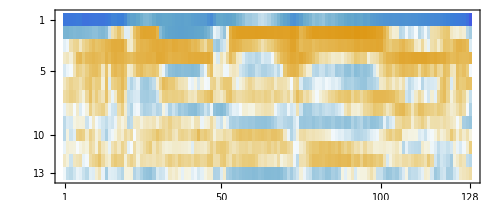
-Graphics-AudioMFCC

```mathematica
Labeled[MatrixPlot[Transpose@Normal[NetEncoder["AudioMFCC"][audioSpanish]]],"AudioMFCC"]
```